# Melt

## Functions for doing quantum things in Mathematica v. 1.1 (updated 09Feb2023) More information at https://melt1.notion.site/

### About

Created by Gabriel T . Landi - https://www.pas.rochester.edu/~gtlandi/

Contributors: Jader P. dos Santos, Artur Lacerda, Michael Kewming, Anthony Kiely, Steve Campbell, Giacomo Guarnieri, Marcelo Janovitch, Eoin Carolan, Eoin O’Connor.

### Auto-loading

```mathematica
LoadPauliMatrices[];
```

## General purpose functions

## Silly but useful functions

### mf: visualizing matrices

```mathematica
(* Prints in matrix form but does not alter definition *)
Clear[mf];
mf[A_]:=(Print[MatrixForm@Chop@A];A)
mf::usage = "mf[A] will print the matrix in a pretty way using Mathematica's MatrixForm[] function. The printed version also chops any small numbers.";
```

```mathematica
Clear[lmf];
lmf[list_]:=MatrixForm/@list;
```

#### Example usage

```mathematica
(* I normally use it like this *)
A = {{1,2},{3,4}}//mf;
```

(1 | 2
3 | 4)

```mathematica
ψ = 1/(√2){1,1}//mf;
```

(1/(√2)
1/(√2))

```mathematica
(* But one can also use it as *)
A = {{1,2},{3,4}};
mf[A];
```

(1 | 2
3 | 4)

### cf: FullSimplify assuming variables are real and positive

```mathematica
(* FullSimplifty + ComplexExpand (to get rid of "Conjugate"s) *)
Clear[cf];
(*cf[expr_]:=FullSimplify@ComplexExpand@expr;*)
cf[expr_]:=FullSimplify[Normal@expr,Thread[DeleteDuplicates@Cases[Normal@expr,_Symbol,∞]>0]]

cf::usage = "FullSimplify assuming that all symbols are real and positive.";
```

#### Example usage

```mathematica
(* Mathematica doesn't know when a symbol is real *)
x = {Cos[θ],Sin[θ]};
x*.x
FullSimplify[%]
```

Conjugate[Cos[θ]] Cos[θ]+Conjugate[Sin[θ]] Sin[θ]

Cosh[2 Im[θ]]

```mathematica
x*.x//cf
```

1

```mathematica
(* The function does not always works the way it is intended to *)
Clear[x]
√Cos[x]//cf
```

√Cos[x]

### out: Outer products

```mathematica
(* Outer product |v⟩⟨u| between two vectors *)
(* Properly conjugates *)
Clear[out];
out[v_,u_]:=Outer[Times,v,Conjugate[u]];
out::usage = "out[v,u] = |v⟩⟨u|";
```

#### Example usage

```mathematica
ψ = 1/(√2){1,ⅈ}//mf;
out[ψ,ψ]//mf;
```

(1/(√2)
ⅈ/(√2))

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

```mathematica
(* The second argument is complex conjugated *)
```

### ℂ: commutator

ℂ[A,B] = [A,B]
ℂ[A,B,-1] = {A,B} (anti-commutator)

```mathematica
(* ℂ writes as esc+dsC+esc *)
Clear[ℂ];
ℂ[A_,B_]:=A.B-B.A;
ℂ[A_,B_,ζ_]:=A.B-ζ B.A
```

#### Example usage

```mathematica
A = {{1,2},{3,4}};
B = {{5,4},{3,2}};
ℂ[A,B]//mf;
```

(-6 | -18
18 | 6)

```mathematica
ℂ[A,B,-1]//mf;
```

(28 | 34
36 | 34)

### ChopCheck: for checking the results of matrix calculations

```mathematica
(* Quick way of checking what are the distinct entries of a matrix or tensor *)
Clear[ChopCheck];
ChopCheck[A_,tol_:10^-10]:=DeleteDuplicates@Flatten@Chop[A,tol]

ChopCheck::usage = "ChopCheck[A] gives 0 when the matrix is 0, to a tolerance of 10^-10. I usually do ChopCheck[A-B] whenever I want to check numerically that A = B";
```

#### Example usage

Verify that A = SΛS† indeed is the correct diagonalization of a matrix A.

```mathematica
A = ({{2, 1, 0}, {1, 5, -3}, {0, -3, 2.}});
{Λ,S} = Eigsys[A]
```

{{0.,2.,7.},{{-0.267261,0.948683,0.169031},{0.534522,8.426×10^-16,0.845154},{0.801784,0.316228,-0.507093}}}

```mathematica
A-S.DiagonalMatrix[Λ].S†//ChopCheck
```

{0}

### range, linspace and logspace

- range[] you specify the stepsize. 
- linspace[] you specify the number of points . 
- logspace[] is the same, but in logscale (base 10) .

linspace/logspace were copied from python/Matlab
range[] is exactly like the native Range[] function in Mathematica. See below for an explanation.

```mathematica
(* Use just like Range[] function *)
Clear[range];
range[xi_,xf_,df_:1]:=N@Rationalize@Range[xi,xf,df]; 

(* Stolen from python/Matlab *)
Clear[linspace]
linspace[dd1_,dd2_,n_:100]:=With[{d1=N@dd1,d2=N@dd2},If[n==1,{d1},d1+(d2-d1)/(n-1) Range[0,n-1]]];
linspace::usage = "linspace[a,b,npts] yields npts linearly interpolated between a (inclusive) and b (inclusive).";

Clear[logspace];
logspace[dd1_,dd2_,n_:100]:=10^linspace[dd1,dd2,n];
logspace::usage = "Same as linspace, but in log scale. logscale[2,5,50] will give 50 pts between 10^2 and 10^5";
```

#### Example usage

```mathematica
range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
range[0,3]
```

{0.,1.,2.,3.}

```mathematica
linspace[0,3,20]
```

{0.,0.157895,0.315789,0.473684,0.631579,0.789474,0.947368,1.10526,1.26316,1.42105,1.57895,1.73684,1.89474,2.05263,2.21053,2.36842,2.52632,2.68421,2.84211,3.}

```mathematica
logspace[0,10,10]
```

{1.,12.9155,166.81,2154.43,27825.6,359381.,4.64159×10^6,5.99484×10^7,7.74264×10^8,1.×10^10}

```mathematica
logspace[2,5,4]
```

{100.,1000.,10000.,100000.}

```mathematica
logspace[2,5,6]
```

{100.,398.107,1584.89,6309.57,25118.9,100000.}

#### Why “range” instead of “Range”

Mathematica's  Range[] function looks normal:

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

But actually it has weird floating point imprecisions.

```mathematica
Range[0,1,0.1]//InputForm
```

{0., 0.1, 0.2, 0.30000000000000004, 0.4, 0.5, 0.6000000000000001, 
0.7000000000000001, 0.8, 0.9, 1.}

This may lead to weird things such as

```mathematica
Position[Range[0,1,0.1],0.6]
```

{{7}}

```mathematica
Position[Range[0,1,0.1],0.7]
```

{}

It cannot find “0.7” in the list because the actual number is 0.7000000000000001 (although Mathematica is printing 0.7). 
This is super annoying. 

The function range corrects this:

```mathematica
range[0,1,0.1]//InputForm
```

{0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.}

### PartitionIn: partition a list into x sublists, with proper paddings at the end

```mathematica
Clear[PartitionIn];
PartitionIn[list_,x_,pad_:""]:=Partition[list,Ceiling[Length[list]/x],Ceiling[Length[list]/x],1,pad]

PartitionIn::usage = "PartitionIn[list,x] partitions list into x sublists, possibly with paddings at the end.";
```

#### Example usage

Mathematica’s Partition[] splits a list into sublists of pre-defined lengths. 
But sometimes we want to partition a list into a pre-defined number of sublists instead, with possible paddings at the end.

```mathematica
list = Range[1,19]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Partition[list,3,3,1," "]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13,14,15},{16,17,18},{19, , }}

```mathematica
(* This splits the list into exactly 3 sublists *)
PartitionIn[list,3]
```

{{1,2,3,4,5,6,7},{8,9,10,11,12,13,14},{15,16,17,18,19,,}}

### PrettyTiming: AbsoluteTiming[] with pretty formatting

```mathematica
Clear[PrettyTiming];
SetAttributes[PrettyTiming,HoldAll];
PrettyTiming[computation_]:=Module[{t1,t2,output,time,h,m,s},
t1 = UnixTime[];
output=ReleaseHold[computation];
t2 = UnixTime[];
time = t2-t1;
(* h = Floor[time/3600];
m = Floor[Mod[time,3600]/60];
s = Round@Mod[time,60];
*)(*Print[ToString[h]<>"h : "<>ToString[m]<>"m : "<>ToString[s]<>"s"];*)
Print[TimeObject[{0,0,time}]];
Return[output]];

PrettyTiming::usage = "PrettyTiming[computation] uses Mathematica's AbsoluteTiming[] to time a computation, but prints the result in a prettier form.";
```

#### Example usage

```mathematica
(* This is how one would time a computation in Mathematica *)
AbsoluteTiming[Do[1,{10^9}]]
```

$Aborted

```mathematica
(* PrettyTiming does the same, but prints the time (instead of outputing it) and does so with a pretty format *)
PrettyTiming[Do[1,{5 10^8}]]
```

00:00:04TimeObject[{0,0,4},Instant]

```mathematica
(* Time a calculation of the variance of random variables *)
```

```mathematica
PrettyTiming[Variance@RandomVariate[BetaDistribution[2,3],10^8]]
```

0h : 0m : 10s

0.0399991

### do & table with Progress Monitor and Timing

Usage is exactly like Do[] & Table[]
But prints progress, as well as times the entire process.

```mathematica
Clear[do];
SetAttributes[do,HoldAll];
do[computation_,iterators__]:=Module[{iters = {iterators}⟦All,1⟧,symb,list,i,d },
symb = ToString/@iters;
d=Length@symb;
list = Flatten[Table[iters,iterators],Length[iters]-1];

PrettyTiming@Monitor[Do[computation,iterators],
(*Check[*)
StringJoin@Table[{symb⟦i⟧," = ", ToString@StandardForm[iters⟦i⟧],"\n"},{i,d}]
ProgressIndicator[Position[list,Table[iters⟦i⟧,{i,d}]]⟦1,1⟧,{1,Length@list}]
(*," "]*)
]
]
```

```mathematica
Clear[table];
SetAttributes[table,HoldAll];
table[computation_,iterators__]:=Module[{iters = {iterators}⟦All,1⟧,symb,list,i,d },
symb = ToString/@iters;
d=Length@symb;
list = Flatten[Table[iters,iterators],Length[iters]-1];

PrettyTiming@Monitor[Table[computation,iterators],
(*Check[*)
StringJoin@Table[{symb⟦i⟧," = ", ToString@StandardForm[iters⟦i⟧],"\n"},{i,d}]
ProgressIndicator[Position[list,Table[iters⟦i⟧,{i,d}]]⟦1,1⟧,{1,Length@list}]
(*," "]*)
]
]
```

#### Examples

```mathematica
do[ Pause[0.2],{i,10},{j,20}]
```

0h : 0m : 40s

```mathematica
table[ Pause[0.4];i+j,{i,5},{j,5}]
```

0h : 0m : 10s

{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},{6,7,8,9,10}}

Simulated driven qubit dynamics for several initial conditions.
Compute populations at final time t = 10

```mathematica
Clear[H,θs,ψ,ψ0];
H[t_]:= 1/2 σz + Cos[t] σx
θs = linspace[0,π,20];
pops=table[
ψ0 = {Cos[θ],Sin[θ]};
Abs[UnitaryDynamics[H,0.005,50,ψ0,True] ⟦2⟧]^2
,{θ,θs}]
```

0h : 0m : 4s

{0.82882,0.888112,0.905347,0.878656,0.810931,0.709512,0.58539,0.452014,0.323838,0.214752,0.136577,0.0977848,0.102579,0.150439,0.23618,0.35051,0.481039,0.613624,0.733895,0.82882}

Use do if you want to store the results (e.g. in an Association)

```mathematica
pops = Association[];
do[
ψ0 = {Cos[θ],Sin[θ]};
pops[θ]=Abs[UnitaryDynamics[H,0.005,50,ψ0,True] ⟦2⟧]^2
,{θ,θs}]
```

0h : 0m : 4s

```mathematica
pops
```

<|0.→0.82882,0.165347→0.888112,0.330694→0.905347,0.496041→0.878656,0.661388→0.810931,0.826735→0.709512,0.992082→0.58539,1.15743→0.452014,1.32278→0.323838,1.48812→0.214752,1.65347→0.136577,1.81882→0.0977848,1.98416→0.102579,2.14951→0.150439,2.31486→0.23618,2.4802→0.35051,2.64555→0.481039,2.8109→0.613624,2.97625→0.733895,3.14159→0.82882|>

Benchmark with Mathematica’s built-in Table: no penalty in execution speed.

```mathematica
AbsoluteTiming[Table[
ψ0 = {Cos[θ],Sin[θ]};
Abs[UnitaryDynamics[H,0.005,50,ψ0,True] ⟦2⟧]^2
,{θ,θs}];]
```

{4.34692,Null}

### nest and nestList with monitor

Taken from https://mathematica.stackexchange.com/questions/132003/progress-indicator-for-nestlist

```mathematica
Clear[nest];
nest[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]] Dynamic[ToString@Round[ 100 it/n]<>"%"]];
Nest[(it++;f[#])&,init,n]]
```

```mathematica
(*Clear[nestList0];
nestList0[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]] Dynamic[ToString@Round[ 100 it/n]<>"%"]];
NestList[(it++;f[#])&,init,n]]*)
```

```mathematica
Clear[nestList];
nestList[f_,init_,n_,split_:1000]:=Module[{it=0,n2=100,δ,f2,list},
If[n<split,
(PrintTemporary[ProgressIndicator[Dynamic[it/n]] Dynamic[ToString@Round[ 100 it/n]<>"%"]];
NestList[(it++;f[#])&,init,n])
,
(
δ = Floor[n/n2];
f2[x_]:=Rest@NestList[f,x[[-1]],δ];
PrintTemporary[ProgressIndicator[Dynamic[it/n2]] Dynamic[ToString@Round[ 100 it/n2]<>"%"]];
list=NestList[(it++;f2[#])&,{init},n2];
Join@@Append[list,Rest@NestList[f,list[[-1,-1]],n-n2 δ]]
)
]
]
```

#### Examples

```mathematica
Clear[f];
f[x_]:=(Pause[1];x+1);
nestList[f,1,5]
```

{1,2,3,4,5,6}

```mathematica
Clear[f];
f[x_]:=(Pause[1/1000];x+1);
nestList[f,1,1003]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004}

### makeGIF

Syntax is similar to Animate[], but exports the animation as a GIF. 
But there are 2 additional arguments: filename and the desired duration (in seconds)
Default fps = 20, but can be changed by passing an additional argument.

File is exported to the default directory, which can be located by typing “Directory[]”
If you want to set the directory to be the same as our notebook directory, type “Set Directory[NotebookDirectory[]]”

```mathematica
Clear[makeGIF];
SetAttributes[makeGIF,HoldAll];
makeGIF[thing_,iterator_,filename_,duration_,fps_:20]:=Module[{ i0,if,Δ,δ,frames,numberOfframes},

numberOfframes = duration fps;
i0 = iterator⟦2⟧;
if = iterator⟦3⟧;
δ = If[Length@iterator==4,iterator⟦4⟧,1];

Δ =  (if-i0)/numberOfframes ;   
If[IntegerQ[δ],Δ=Ceiling[Δ]];

If[Length@iterator==3,
frames = table[thing,Evaluate@Append[iterator, Δ]],
frames = table[thing,Evaluate@ReplacePart[iterator,4-> Δ]]
];
If[Length@frames < 0.8 numberOfframes,
Print["Could not match the desired framerate & duration. Reducing framerate to "<>ToString[(duration/(Length@frames))^-1//Round]<>" fps"];
Print["Requires a longer list"]
];

Print["Exporting "<>filename<>".gif (can take a while...)"];
Export[filename <>".gif",frames,"DisplayDurations"->duration/(Length@frames)] ;
Animate[frames⟦i⟧,{i,1,Length@frames,1}]
]
```

#### Example usage

Syntax is similar to Animate

```mathematica
Animate[Plot[Sin[a+x],{x,0,10}],{a,0,10}]
```

```mathematica
makeGIF[Plot[Sin[a+x],{x,0,10}],{a,0,10,1.},"myGIF",10]
```

0h : 0m : 1s

### RandomRep: randomly attributes numerical values to parameters

Useful for checking symbolic calculations with numerical comparisons

```mathematica
RandomRep[parameters_,seed_:0]:=Module[{},
If[Not[seed===0],SeedRandom[seed]];
Thread[parameters->RandomReal[{0,1},Length@parameters]]
]
```

### positionMax and positionMin

p is the element of the list with which the maximum will be searched. 
e.g. for list = {{“a”,2}, {“b”,1}} if one uses p =1 it will sort with {“a”,”b”} and if one uses p = 2 it will sort with {2,1}.

```mathematica
Clear[positionMax];
positionMax[list_,p_:1]:=Module[{list2,ord},
list2 = If[Length@Dimensions@list>1,list[[All,p]],list];
ord = Ordering[list2];
{Last@ord,list[[Last@ord]]}
]

Clear[positionMin]
positionMin[list_,p_:1]:=Module[{list2,ord},
list2 = If[Length@Dimensions@list>1,list[[All,p]],list];
ord = Ordering[list2];
{First@ord,list[[First@ord]]}
]
```

#### Example usage

```mathematica
tmp = {{"a",2},{"b",1},{"c",5}};
```

```mathematica
positionMax[tmp,2]
```

{3,{c,5}}

```mathematica
positionMax[tmp,1]
```

{3,{c,5}}

```mathematica
positionMin[tmp,1]
```

{1,{a,2}}

```mathematica
positionMin[tmp,2]
```

{2,{b,1}}

### Functions for handling larger simulations

```mathematica
Clear[loadComputation];
loadComputation[parameterList_,numberOfBatches_:100]:=Module[{ord},

ord=Join[Flatten@Transpose@Partition[Range[1,numberOfBatches],20],Range[1,numberOfBatches]]//DeleteDuplicates;
Clear[SIM];
SIM["done"] = 0;
SIM["rate"] = 0;
SIM["parameters_done"]={};
If[Length@parameterList===0,
SIM["parameters"] = {};
SIM["number_of_batches"]=0;
SIM["parameter_batches"]={};
,
(
SIM["parameters"] = Distribute[parameterList,List];
SIM["number_of_batches"]=numberOfBatches;
SIM["parameter_batches"]=If[Length@SIM["parameters"]<numberOfBatches,
{SIM["parameters"]},
Table[SIM["parameters"][[i;;-1;;numberOfBatches]],{i,numberOfBatches}][[ord]]
]
)];

If[Length@parameterList!=0,
Print["Length of each parameter list: ",Length/@parameterList];
Print["Total = ",Length@SIM["parameters"]]
];

]
```

```mathematica
Clear[appendComputation]
appendComputation[newpara_,numberOfBatches_:100]:=Module[{old,total,new,newsmall},
old = SIM["parameters"];
total = Distribute[newpara,List];
new = Complement[total,old];
If[new==={},Return[]];
newsmall = If[Length@ new<=numberOfBatches,
{new},
Table[new[[i;;-1;;numberOfBatches]],{i,numberOfBatches}]
];
SIM["number_of_batches"] = SIM["number_of_batches"]+Length@newsmall;
SIM["parameters_done"]=old;
SIM["parameters"]=total;
SIM["parameter_batches"]= Join[SIM["parameter_batches"],newsmall];
Print["Length of each parameter list: ",Length/@newpara];
Print["Total = ",Length@SIM["parameters"]," from which: ", Length@new," new and ",Length@SIM["parameters_done"], " are done."]

]
```

```mathematica
Clear[simulate];
simulate[computation_,amount_:100]:=Module[{paras,time,todo,p,nb,perc,i,pl,timeremaining},
nb = SIM["number_of_batches"];
If[SIM["done"]===nb,Return[]];
todo = Min[nb,SIM["done"]+amount];
paras = Join@@SIM["parameter_batches"][[SIM["done"]+1;;todo]];
pl = Length@paras;
time = First@AbsoluteTiming[
Monitor[Do[computation[paras[[i]]],{i,pl}],ToString@Round[100 i/pl]<>"%" ProgressIndicator[i,{1,pl}]];
];
SIM["rate"] = (SIM["rate"] SIM["done"] + time)/todo;  
SIM["done"] = todo;
SIM["parameters_done"] = Join@@SIM["parameter_batches"][[Range[1,SIM["done"]]]];
perc = SIM["done"]/nb 100//Round;
timeremaining = (nb-SIM["done"])SIM["rate"];
Print[ToString@SIM["done"]<>"/"<>ToString@nb" batches done."<>" This batch took:",TimeObject[{0,0,time}],". Estimated time remaining: ",TimeObject[{0,0,timeremaining}],"."];
]
```

```mathematica
Clear[save];
save[filename_,quantities__]:=Module[{variables},
SetDirectory[NotebookDirectory[]];
DumpSave[filename<>".mx",{SIM,quantities}];
]

Clear[load];
load[filename_]:=Module[{fname = filename<>".mx"},
SetDirectory[NotebookDirectory[]];
Get[fname ]
]
```

```mathematica
Clear[extractDone];
extractDone[paras_,list_:"parameters_done"]:=Module[{nvars,pos,selector},
nvars = DeleteCases[paras,""]//Length;
pos = Complement[Range[1,Length@paras],Flatten@Position[paras,""]];
selector[x_]:=And@@Table[MemberQ[Flatten@{paras[[pos[[i]]]]},x[[pos[[i]]]]],{i,nvars}];
Select[SIM[list],selector[#]&]
]

Clear[extract1D];
extract1D[quantity_,pos_,otherparas_]:=Module[{toloop,paras},
toloop=Complement[Range[1,Length@otherparas],{pos}];
paras = Select[SIM["parameters_done"],#[[toloop]]===otherparas[[toloop]]&];
Sort@Table[{p[[pos]],quantity@@p},{p,paras}]
]

Clear[extract2D];
extract2D[quantity_,p1_,p2_,otherparas_]:=Module[{tab,toloop,paras},
toloop=Complement[Range[1,Length@otherparas],{p1,p2}];
paras = Select[SIM["parameters_done"],#[[toloop]]===otherparas[[toloop]]&];
tab=Table[{p[[p1]],p[[p2]],quantity@@p},{p,paras}];
SortBy[tab,{#[[1]]&,#[[2]]&}]
]
```

```mathematica
(* no good *)
Clear[clearSims];
clearSims[parameters_,obj_]:=Module[{list = extractDone[parameters]},
Quiet@Do[obj@@p=.,{p,list}]
]
```

#### Example usage

Suppose we wish to do a computation that takes as input two parameters, μ and σ. 
They are defined within certain ranges

```mathematica
μs = Range[1,10,1];
σs = Range[0.1,0.5,0.1];
```

As an example of a concrete computation we might want to do, say we wish to compute the third moment of a Gaussian distribution by randomly generating multiple samples. That is, for a given (μ,σ), suppose the computation we want to do is

```mathematica
nsamps = 10^8;
μ = 1.0;
σ =0.3;
Mean@RandomVariate[NormalDistribution[μ,σ],nsamps]
```

0.99998

But we want to do many times, for μ and σ looping over the lists “μs” and “σs” above. 

The functions “loadComputation” and “simulate” above help with that. 
The starting point is to define a function “computation” which actually does the computation, given a set of parameters. 
In our case it would look like

```mathematica
computation[{μ_,σ_}]:=Mean@RandomVariate[NormalDistribution[μ,σ],10^7]
```

The input of the function “computation” must always be a list of the parameters involved. This is important.

We can now run the above simulation as follows:

```mathematica
μs = Range[1,10,0.1];
σs = Range[0.1,0.5,0.1];
loadComputation[μs,σs]
Length@PARAMETERSSMALL
```

100

```mathematica
simulate[computation,10]
```

60% done. Average time per 1% = 0.73 seconds

### toSphericalCoordinates

```mathematica
Clear[toSphericalCoordinates];
toSphericalCoordinates[{x_,y_,z_}]:={√(x^2+y^2+z^2),If[Norm[{x,y,z}]===0,0,ArcCos[z/(√(x^2+y^2+z^2))]],If[x===0&&y===0,0,Sign[y] ArcCos[x/(√(x^2+y^2))]]}
```

#### Example usage

This is the same as Mathematica’s ToSphericalCoordinates function, except that it works when x=y=0

```mathematica
ToSphericalCoordinates[{0.3,0.1,0.9}]
toSphericalCoordinates[{0.3,0.1,0.9}]
```

{0.953939,0.33789,0.321751}

{0.953939,0.33789,0.321751}

```mathematica
ToSphericalCoordinates[{0,0,1}]
toSphericalCoordinates[{0,0,1}]
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

{1,0,Indeterminate}

{1,0,0}

```mathematica
ToSphericalCoordinates[{0,0,0}]
toSphericalCoordinates[{0,0,0}]
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

{0,Indeterminate,Indeterminate}

{0,0,0}

### flat1 and flat2

Useful for functions like ListPlot3D

```mathematica
Clear[flat1,flat2];
flat1[list_]:=Flatten[list,1];
flat2[list_]:=Flatten[list,2];
```

#### Example usage

```mathematica
Clear[x,y]
```

```mathematica
tab = Table[{x,y,x+y},{x,{1,2,3}},{y,{20,50,100}}]
```

{{{1,20,21},{1,50,51},{1,100,101}},{{2,20,22},{2,50,52},{2,100,102}},{{3,20,23},{3,50,53},{3,100,103}}}

```mathematica
flat1@tab
```

{{1,20,21},{1,50,51},{1,100,101},{2,20,22},{2,50,52},{2,100,102},{3,20,23},{3,50,53},{3,100,103}}

```mathematica
flat2@tab
```

{1,20,21,1,50,51,1,100,101,2,20,22,2,50,52,2,100,102,3,20,23,3,50,53,3,100,103}

## Linear algebra

### kron: compact Kronecker products which correctly handles vectors

Mathematica’s KroneckerProduct handles vectors in a weird way.

```mathematica
Clear[kron];
kron[mats__?MatrixQ]:=KroneckerProduct[mats];
kron[vecs__?VectorQ]:=Flatten@KroneckerProduct[vecs];

kron::usage ="kron[A,B,C...] = A ⊗ B ⊗ C ⊗ .... For matrices, it is exactly like the native KroneckerProduct[] from Mathematica. For vectors, kron[u,v] produces the proper |u⟩ ⊗ |v⟩."

a_⊗b_:=kron[a,b];
```

kron[A,B,C...] = A ⊗ B ⊗ C ⊗ .... For matrices, it is exactly like the native KroneckerProduct[] from Mathematica. For vectors, kron[u,v] produces the proper |u⟩ ⊗ |v⟩.

```mathematica
(* 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ A ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 ⊗ 𝕀 *)
```

```mathematica
Clear[KronEye];
KronEye[A_,𝒩_,j_]:=kron[Eye[Length[A]^(j-1)],A,Eye[Length[A]^(𝒩-j)]]

KronEye::usage = "KronEye[A,𝒩,j] = (𝕀 ⊗ ... 𝕀 ⊗ A ⊗ 𝕀 ... ⊗ 𝕀, with A at site j and 𝒩 sites in total.";
```

#### Example usage

```mathematica
(* For matrices, kron[A,B] is just a compact notation of KroneckerProduct[A,B] *)
A = {{1,2},{3,4}};
B = {{0,1},{1,0}};
kron[A,B]//mf;
```

(0 | 1 | 0 | 2
1 | 0 | 2 | 0
0 | 3 | 0 | 4
3 | 0 | 4 | 0)

```mathematica
(* Tensor product symbol is entered as *)
(* esc + "c" + "*" + esc *)
A⊗B//mf;
```

(0 | 1 | 0 | 2
1 | 0 | 2 | 0
0 | 3 | 0 | 4
3 | 0 | 4 | 0)

```mathematica
kron[A,A,A]//mf;
```

(1 | 2 | 2 | 4 | 2 | 4 | 4 | 8
3 | 4 | 6 | 8 | 6 | 8 | 12 | 16
3 | 6 | 4 | 8 | 6 | 12 | 8 | 16
9 | 12 | 12 | 16 | 18 | 24 | 24 | 32
3 | 6 | 6 | 12 | 4 | 8 | 8 | 16
9 | 12 | 18 | 24 | 12 | 16 | 24 | 32
9 | 18 | 12 | 24 | 12 | 24 | 16 | 32
27 | 36 | 36 | 48 | 36 | 48 | 48 | 64)

```mathematica
(* For vectors, Mathematica is weirrrd *)
```

```mathematica
v0 = {1,0};
v1 = {0,1};
KroneckerProduct[v0,v1]//mf;
```

(0 | 1
0 | 0)

```mathematica
(* kron[] saves the day *)
kron[v0,v1]//mf;
```

(0
1
0
0)

```mathematica
(* Pauli matrix for site 2 of a spin chain with 4 sites *)
σx = ({{0, 1}, {1, 0}});
KronEye[σx,4,2]//mf;
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

### Proj & Basis: projection matrices and basis elements

```mathematica
Clear[Proj];
Proj[n_,i_]:=SparseArray[{{i,i}->1},{n,n}];
Proj[n_,i_,j_]:=SparseArray[{{i,j}->1},{n,n}];

Proj[{n_,m_},i_]:=SparseArray[{{i,i}->1},{n,m}];
Proj[{n_,m_},i_,j_]:=SparseArray[{{i,j}->1},{n,m}];


Proj::usage = "Proj[n,i,j] yields a n×n matrix with element (i,j) equal 1. Proj[n,i] = Proj[n,i,i].";
```

```mathematica
Clear[Basis];
Basis[n_,i_]:=Normal@SparseArray[{i->1},n]
Basis[n_,ilist_?ArrayQ]:=Total@Table[Basis[n,i],{i,ilist}]

Basis::usage = "Basis[n,i] = (0,...,0,1,0,...,0) with 1 at position i. Basis[n,{i1,i2,...}] yields the same, but with 1's at positions i1,i2,...";
```

#### Example usage

```mathematica
Proj[4,1]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Proj[4,2]//mf;
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Proj[4,1,2]//mf;
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Basis[4,1]//mf;
```

(1
0
0
0)

```mathematica
Basis[4,2]//mf;
```

(0
1
0
0)

```mathematica
Basis[4,{1,2}]//mf;
```

(1
1
0
0)

### Useful matrices

Eye  = Identity for symbolics. 
NEye = Identity for numerics. 

toeplitzMatrix = more flexible syntax than Mathematica’s ToeplitzMatrix[]. 
StiffnessMatrix =hopping matrix of the tight-binding model.
CirculantMatrix = same, but with periodic boundary conditions.

```mathematica
Clear[Eye,NEye];
Eye[n_]:=SparseArray[{{i_,i_}->1},{n,n}];
Eye[A_?ArrayQ]:=Eye[Length@A]

NEye[n_]:=SparseArray[{{i_,i_}->1.},{n,n},0.];
NEye[A_?ArrayQ]:=NEye[Length@A]
```

```mathematica
Clear[toeplitzMatrix];
toeplitzMatrix[a_,k_,L_]:=If[L==1,If[k==1,{{a}},{{0}}],SparseArray[{Band[{1,k}]->a,Band[{k,1}]->a},{L,L}]]
```

```mathematica
Clear[StiffnessMatrix,CirculantMatrix];
StiffnessMatrix[n_]:=toeplitzMatrix[-1,2,n];
CirculantMatrix[n_]:=toeplitzMatrix[-1,2,n]+toeplitzMatrix[-1,-1,n];
```

```mathematica
Clear[FirstDerivative];
FirstDerivative[n_,Δx_:1,boundary_:None]:=
If[boundary===None,
1/(2Δx)SparseArray[{
Band[{1,2}]->1,
Band[{2,1}]->-1
},{n,n}],
1/(2Δx)SparseArray[{
{i_,j_}/;j==i+1&&i!=1->1,
{i_,j_}/;j==i-1&&i!=n->-1,
{1,2}->2,
{1,1}->-2,
{n,n}->2,
{n,n-1}->-2
},{n,n}]];

Clear[SecondDerivative]
SecondDerivative[n_,Δx_:1,boundary_:None]:=Module[{mat=-(2Eye[n]+StiffnessMatrix[n])},
If[boundary===None,
1/Δx^2 mat,
(mat[[1,-1]]=1; mat[[-1,1]]=1; 1/Δx^2 mat)
]]
```

#### Example usage:

```mathematica
Eye[3]//mf;
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(* The distinction is silly, but for doing numerics it is useful to use NEye *)
NEye[3]//mf;
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

```mathematica
toeplitzMatrix[a,1,5]//mf;
```

(a | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0
0 | 0 | a | 0 | 0
0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | a)

```mathematica
toeplitzMatrix[a,2,5]//mf;
```

(0 | a | 0 | 0 | 0
a | 0 | a | 0 | 0
0 | a | 0 | a | 0
0 | 0 | a | 0 | a
0 | 0 | 0 | a | 0)

```mathematica
(* Also works with 1D matrices *)
toeplitzMatrix[a,1,1]
```

{{a}}

```mathematica
StiffnessMatrix[6]//mf;
```

(0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0)

```mathematica
CirculantMatrix[6]//mf;
```

(0 | -1 | 0 | 0 | 0 | -1
-1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1
-1 | 0 | 0 | 0 | -1 | 0)

### Boxcar function

A unit box from a to b:
Width b-a := 2δ, centered at c = (a+b)/2

Boxcar(a,b) = θ(x-a)θ(b-x)
	        = θ(x-a) - θ(x-b)
                  = π(1/(2δ)(x-c)
                  = θ(δ^2-(x-c)^2)

Here θ = HeavisideTheta and π = HeavisidePi

```mathematica
Clear[Boxcar];
Boxcar[a_,b_][x_]:=UnitStep[x-a]-UnitStep[x-b]

Boxcar[a_,b_,smooth_][x_]:=If[Abs[smooth]<10^-14,Boxcar[a,b][x],1/2(Tanh[(x-a)/smooth]-Tanh[(x-b)/smooth] )]

Boxcar::usage = "Boxcar[a,b][x] returns a boxcar function from a to b";
```

#### Example usage

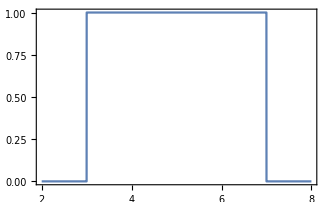

```mathematica
Plot[Boxcar[3,7][x],{x,2,8},Exclusions->None]
```

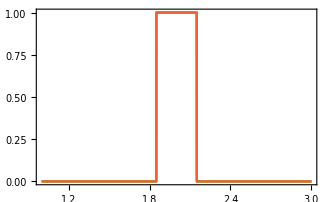

```mathematica
(* Different ways of implementing a boxcar, centered in c, of total width δ *)
c = 2;
δ = 0.15;
a = c-δ;
b = c+δ;
Plot[{
HeavisideTheta[x-a]-HeavisideTheta[x-b],
HeavisideTheta[x-a]HeavisideTheta[b-x],
HeavisidePi[1/(2δ)(x-c)],
HeavisideTheta[δ^2-(x-c)^2]
},{x,1,3},Exclusions->None,PlotStyle->Automatic]
```

```mathematica
Manipulate[Plot[Boxcar[a,b,smooth][x],{x,-2,2}],{{a,0},-1,1},{{b,1},0,2},{{smooth,0.1},0.01,0.2}]
```

### Eigstuff & Ground-state: sorts eigenvalues and correctly orders eigenvectors

These functions “fix” some weird outputs of Mathematica’s eigensystem functions. 
- Order eigenvalues by smaller in number, not magnitude: 1st eigenvalue is ground-state. 
- Output eigenvectors as a matrix, not a list of lists.

```mathematica
Clear[Eigvals,Eigvecs,Eigsys];

Eigvals[A_,neigs_:"all",Δ_:10^5]:=If[neigs==="all",
Sort@Eigenvalues[N@A],
Reverse@Eigenvalues[A + Δ NEye@Length@A,-neigs]-Δ];

Eigvecs[A_,neigs_:"all",Δ_:10^5]:=
Module[{tmp,e,v,ord},
If[neigs=="all",(
{e,v}=Eigensystem[N@A];
ord=Ordering[e];
Transpose[v⟦ord⟧]
),
(
{e,v}=Eigensystem[A + Δ NEye@Length@A,-neigs];
 Transpose@Reverse@v
)
]
]

Clear[Eigsys];
Eigsys[A_, neigs_:"all",Δ_:10^5]:=Module[{tmp,e,v,ord},

If[neigs=="all",(
{e,v}=Eigensystem[N@A];
ord=Ordering[e];
{e⟦ord⟧,Transpose[v⟦ord⟧]}
),
(
{e,v}=Eigensystem[A + Δ NEye@Length@A,-neigs];
 {Reverse@e-Δ,Transpose@Reverse@v}
)
]
]
```

```mathematica
Clear[GroundState];
GroundState[H_]:=Eigvecs[H,1]⟦All,1⟧

GroundState[H_,n_]:=Eigvecs[H,n]⟦All,-1⟧;
```

#### Example usage

```mathematica
(* Eigenvalues of a spin 3/2 Hamiltonian *)
LoadArbitrarySpinMatrices[3/2];
H = Sz + 0.3 Sx.Sx//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
(* Mathematica orders eigenvalues by magnitude. The ground-state in this case is actually -1.30398 *)
Eigenvalues[H]
```

{1.76382,-1.30398,1.05398,-0.0138194}

```mathematica
(* Eigvals order in the natural way *)
Eigvals[H]
```

{-1.30398,-0.0138194,1.05398,1.76382}

```mathematica
(* Suppose one wishes only the first two eigenvalues. Here is what Mathematica yields: *)
Eigenvalues[H,2]
```

{1.76382,-1.30398}

```mathematica
(* The ordering is weird because it is ordered by absolute value. For Eigvals the ordering is consistent with ground states: *)
Eigvals[H,2]
```

{-1.30398,-0.0138194}

```mathematica
(* Diagonalization is traditionally written as H = S.ℰ.S^-1, with eigenvectors being the columns of S. *)
(* Mathematica returns eigenvectors as the rows *)
```

```mathematica
{ℰ,S}=Eigensystem[H];
Sᵀ.DiagonalMatrix[ℰ].Inverse[Sᵀ]//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
(* Eigsys and Eigvecs return eigenvectors as the columns of S *)
{ℰ,S}=Eigsys[H];
S.DiagonalMatrix[ℰ].S†//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
S
```

{{0.,0.147776,0.,0.989021},{-0.110866,0.,-0.993835,0.},{0.,-0.989021,0.,0.147776},{0.993835,0.,-0.110866,0.}}

```mathematica
Eigvecs[H]
```

{{0.,0.147776,0.,0.989021},{-0.110866,0.,-0.993835,0.},{0.,-0.989021,0.,0.147776},{0.993835,0.,-0.110866,0.}}

### expect: operator average ⟨O⟩, handling pure and mixed states in equal footing

```mathematica
(* y can be a ket or a density matrix *)
Clear[expect];
expect[A_,y_]:=If[Length@Dimensions@y==2,Tr[A.y],y*.A.y];
```

#### Example usage

```mathematica
ψ = 1/(√2){1,1};
expect[σx,ψ]
```

1

```mathematica
(* Or use a density matrix *)
ρ = out[ψ,ψ];
expect[σx,ρ]
```

1

### DirectSum

```mathematica
Clear[DirectSum]
DirectSum[mats__]:=Module[{m=List@mats,tab, diag,a},
tab= Table[a[i],{i,Length@m}];
diag=DiagonalMatrix[Table[a[i],{i,Length@m}]];
diag/.Thread[tab->m]//ArrayFlatten
]

DirectSum::usage = "DirectSum[A,B,...] yields a diagonal block matrix diag(A,B,...)";
```

#### Example usage

```mathematica
LoadPauliMatrices[]
DirectSum[σx,σz]//mf;
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
DirectSum[σx,σy,σz]//mf;
```

(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1)

#### Alternative implementation from klgr in StackExchange

Based on https://mathematica.stackexchange.com/questions/19778/how-to-form-a-block-diagonal-matrix-from-a-list-of-matrices/19780#19780

```mathematica
DirectSum2=With[{r=MapIndexed[#2[[1]] {1,1}->#&,#,1]},SparseArray`SparseBlockMatrix[r]]&;
```

```mathematica
DirectSum2[{σx,σy,σz}]//mf;
```

(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1)

### BCHderiv: BCH formula for ∂_θ e^(G(θ))

Input is the operator G and the operator ∂_θ G. Implements the BCH formula in https://melt1.notion.site/Baker-Campbell-Hausdorf-BCH-formula-for-the-derivative-of-an-exponential-Dyson-series-integral-re-62fb312217454e38b2e6cf1d78d40403?pvs=4

```mathematica
BCHderiv[G_,dG_,nmax_:100]:=Module[{M},

M = dG;
(dG + Total@Table[
M=G.M-M.G;
1/(n!)M,{n,2,nmax} ]).MatrixExp[G]
]
```

#### Example usage

```mathematica
Δ = 0.3;
Ω = 1.0;
H = Δ σz + Ω σx;
dH = σx; (* Derivative of H with respect to Ω *)

BCHderiv[H,dH]//mf;
```

(1.30316 | 1.56294
1.56294 | 1.0805)

```mathematica
(* Sanity check *)
δ = 10^-5;
(MatrixExp[(Δ σz + (Ω+δ) σx)]-MatrixExp[(Δ σz + (Ω-δ) σx)])/(2δ)//mf;
```

(1.30316 | 1.56294
1.56294 | 1.0805)

## “Load” useful operators (Pauli matrices, fermionic and bosonic operators, &c.)

"Load" functions load into your system a set of matrices related to the problem at hand (qubits, fermions, bosons, etc.).

### LoadPauliMatrices: Pauli matrices for a single qubit

```mathematica
Clear[LoadPauliMatrices];
LoadPauliMatrices[]:=Module[{},
Clear[σ0,σx,σy,σz,σp,σm,GMAT];
σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σy = {{0,-I},{I,0}};
σz = {{1,0},{0,-1}};
σp = {{0,1},{0,0}}(*(σx + I σy)/2*);
σm = {{0,0},{1,0}}(*(σx - I σy)/2*);
(*nn = σp.σm; *)

GMAT[θ_,ϕ_] := MatrixExp[-ⅈ ϕ σz/2].MatrixExp[-ⅈ θ σy/2];

"Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]"
];
```

Pauli matrices are loaded automatically

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

#### Example usage

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

```mathematica
σx//mf;
```

(0 | 1
1 | 0)

```mathematica
(* Matrix diagonalizing an arbitrary direction in Bloch's sphere *)
GMAT//mf;
```

GMAT

```mathematica
GMAT†.GMAT//cf//mf;
```

(1 | 0
0 | 1)

```mathematica
sigmaN = Sin[θ] Cos[ϕ] σx + Sin[θ] Sin[ϕ] σy + Cos[θ] σz;
G†.sigmaN.G//cf//mf;
```

(1 | 0
0 | -1)

### LoadSpinChainMatrices: Pauli matrices for a spin chain

Use LoadSpinChainMatrices[N,"a"] for symbolics

```mathematica
LoadSpinChainMatrices[𝒩_,type_:"n"]:=Module[{one,σ0,σx,σy,σz,σp,σm},

(* 2 x 2 Pauli matrices *)
one = If[type=="n",1.0,1];
σ0 = SparseArray[one{{1,0},{0,1}}];
σx = SparseArray[one{{0,1},{1,0}}];
σy = SparseArray[one{{0,-I},{I,0}}];
σz =SparseArray[ one{{1,0},{0,-1}}];
σp =(σx + I σy)/2;
σm = (σx - I σy)/2;

Clear[eye,sp,sm,sx,sy,sz,c,cd];
eye = one Eye[2^𝒩];

If[𝒩>1,
Do[
eyeL = one Eye[2^(i-1)];
eyeR = one Eye[2^(𝒩-i)];
(* Spin matrices of site i *)
sx[i] = kron[eyeL,σx,eyeR];
sy[i] = kron[eyeL,σy,eyeR];
sz[i] = kron[eyeL,σz,eyeR];
sp[i] = kron[eyeL,σp,eyeR];
sm[i] = sp[i]ᵀ;

(* Fermionic operators using the Jordan Wigner transformation *)
c[i] = kron@@Join[Table[(-σz),{j,1,i-1}],{σm},Table[σ0,{j,i+1,𝒩}]];
cd[i] = c[i]†;

,{i,1,𝒩}],
(
sx[1] = σx;
sy[1] =σy;
sz[1] = σz;
sp[1] = σp;
sm[1] = σm;
c[1] = σm;
cd[1] = σp;)];

"Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, eye, sm, sp, sx, sy, sz, c, cd"

];
```

#### Example usage

```mathematica
LoadSpinChainMatrices[3]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, eye, sm, sp, sx, sy, sz, c, cd

```mathematica
σx//mf;
```

(0. | 1.
1. | 0.)

```mathematica
sx[1]//mf;
```

(0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.)

```mathematica
sx[2]//mf;
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.)

```mathematica
(* Now there are no more floating points *)
LoadSpinChainMatrices[3,"a"]
sx[2]//mf;
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

### LoadFermionicOperators: Fermionic operators & majoranas

Majorana definitions: 

“local”: 
Γ_(2n-1) = 1/(√2)(c_n+c_n^†)
Γ_(2n)     = i/(√2) (c_n^†-c_n)

“non-local” (default): 
Γ_n = 1/(√2)(c_n+c_n^†)
Γ_(n+N)     = i/(√2) (c_n^†-c_n)

In both cases: 
{Γ_i,Γ_j} =  δ_ij

Mimicking the notation in 
https://melt1.notion.site/The-ultimate-guide-to-Gaussian-open-things-covariance-matrix-Lyapunov-equations-fermions-bosons--7e45a124c7d64122b6d65d8ae7e4c59e

```mathematica
Clear[LoadFermionicOperators];
LoadFermionicOperators[𝒩_,type_:"n",ord_:"non-local"]:=Module[{},

LoadSpinChainMatrices[𝒩,type];
Clear[sp,sm,sx,sy,sz];
Clear[Γ];
If[ord=="local",
Do[
Γ[2n-1] = 1/(√2)(c[n] + cd[n]);
Γ[2n]= ⅈ/(√2) (cd[n]-c[n]),
{n,1,𝒩}],
Do[
Γ[n] = 1/(√2)(c[n] + cd[n]);
Γ[𝒩+n]= ⅈ/(√2) (cd[n]-c[n]),
{n,1,𝒩}]
];

Clear[sp,sm,sx,sy,sz];
"Matrices loaded: eye, c, cd, Γ"
]
```

#### Example usage

```mathematica
LoadFermionicOperators[3]
```

Matrices loaded: eye, c, cd, Γ

```mathematica
c[1]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0)

```mathematica
(* Majorana operators *)
Γ[3]//mf;
```

(0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
-1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0)

```mathematica
LoadFermionicOperators[3,"a"];
c[1]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

Changing the ordering to global affects Majorana operators, but not c and c†

```mathematica
LoadFermionicOperators[3,"a"];
Γ[3]//mf;
```

(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
LoadFermionicOperators[3,"a","global"];
Γ[3]//mf;
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

### LoadArbitrarySpinMatrices: Spin S operators

```mathematica
Clear[LoadArbitrarySpinMatrices];
LoadArbitrarySpinMatrices[S_,type_:"n",chain_:1]:=Module[{it,srange,tmp,Opset,opset},

it=If[type=="a",1,1.0];
srange = Range[S,-S,-it];

Clear[Sz,Sp,Sm,Sx,Sy,S0];

Sz= SparseArray@DiagonalMatrix[srange];
Sp = SparseArray@Table[√((S-s)(S+s+1))KroneckerDelta[r,s+1],{r,srange},{s,srange}];
Sm = Spᵀ;
Sx = (Sp+Sm)/2;
Sy = (Sp-Sm)/(2I);
S0 =Eye[2S+1];


If[chain===1,
"Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm",
(Clear[𝒮x,𝒮y,𝒮z,𝒮p,𝒮m];
Opset={𝒮x,𝒮y,𝒮z,𝒮p,𝒮m};
opset={Sx,Sy,Sz,Sp,Sm};
Do[Opset[[n]][i]=KronEye[opset[[n]],chain,i],{n,Length@Opset},{i,chain}];
"Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm and multi-site 𝒮x,𝒮y,𝒮z,𝒮p,𝒮m"
)
]
];
```

#### Example usage

```mathematica
(* Spin 1 particle *)
LoadArbitrarySpinMatrices[1]
```

```mathematica
Sx//mf;
```

(0. | 0.707107 | 0.
0.707107 | 0. | 0.707107
0. | 0.707107 | 0.)

```mathematica
(* Spin 5/2 particle; symbolics *)
LoadArbitrarySpinMatrices[5/2,"a"]
```

```mathematica
Sx//mf;
```

(0 | (√5)/2 | 0 | 0 | 0 | 0
(√5)/2 | 0 | √2 | 0 | 0 | 0
0 | √2 | 0 | 3/2 | 0 | 0
0 | 0 | 3/2 | 0 | √2 | 0
0 | 0 | 0 | √2 | 0 | (√5)/2
0 | 0 | 0 | 0 | (√5)/2 | 0)

### LoadBosonicOperators: Bosonic operators

N is the size of the matrix: Fock space goes from |0⟩ to |N-1⟩.

```mathematica
LoadBosonicOperators[𝒩_,type_:"n",chain_:1]:=Module[{one,tmp,n,m,Opset,opset},
one = If[type=="a",1,1.0];
Clear[𝕀,a,X,P(*,CoherentState*)];
𝕀= Eye[𝒩];
a=one DiagonalMatrix[SparseArray[Table[√n,{n,1,𝒩-1}]],1];
𝕏 = 1/(√2)(a†+a);
ℙ = I/(√2)(a†-a);
CoherentState[α_]:=Exp[-Abs[α]^2/2] Table[α^n/(√(n!)),{n,0,𝒩-1}];
BosonicThermalState[n0_]:=DiagonalMatrix@Table[n0^n (1+n0)^(-1-n),{n,0,𝒩-1}];

If[chain===1,
"Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]",
(Clear[ℐ,𝒶,𝓍,𝓅];
Opset={ℐ,𝒶,𝓍,𝓅};
opset={𝕀,a,𝕏,ℙ};
Do[Opset[[n]][i]=KronEye[opset[[n]],chain,i],{n,Length@Opset},{i,chain}];
"Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], BosonicThermalState[n0], and multi-site ℐ,𝒶,𝓍,𝓅"
)
]


]
```

#### Example usage

```mathematica
LoadBosonicOperators[10,"a"]
```

Matrices loaded: 𝕀 (=1), a, X, P, ℕ

```mathematica
a//mf;
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LoadBosonicOperators[10]
a†//mf;
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.41421 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.73205 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 2.23607 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2.44949 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.64575 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.82843 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3. | 0.)

## Alternative versions of simple numerics

### Trapz: Cheap & crappy numerical integration

Silly trapezoidal rule for function integration.

```mathematica
Clear[Trapz];
Trapz[fs_,Δx_]:=Δx/2(fs⟦1⟧ + 2 Total[fs⟦2;;-2⟧] + fs⟦-1⟧);

Trapz::usage = "Trapz[fs,Δx] integrates the list fs using the trapezoidal rule, with step Δx";
```

#### Example usage

```mathematica
NIntegrate[Sin[x]^3,{x,0,0.7}]
```

0.0509645

```mathematica
Δx = 0.01;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509725

```mathematica
Δx = 0.005;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509665

```mathematica
Δx = 0.001;
list = Sin[range[0,0.7,Δx]]^3;
Trapz[list,Δx]
```

0.0509646

### BracketRoot & FindAllRoots: pre-bracketing roots within a given interval:

Brackets the roots of f(x). 
Very useful function in root finding.

Output is a list of intervals [a_i,b_i], such that f(x) is guaranteed to have a root inside.

```mathematica
Clear[BracketRoot];
BracketRoot[f_,xmin_,xmax_,npts_:1000]:=Module[{xrange,tab,par,roots,pos,xtab,x},
xrange=linspace[xmin,xmax,npts];
tab = f/@xrange;
par = {Range[1,Length@tab-1],Most[tab] Rest[tab]}ᵀ;
pos =Select[par,#⟦2⟧≤ 0.0&]⟦All,1⟧;
Table[{xrange⟦p⟧,xrange⟦p+1⟧},{p,pos}]
]

BracketRoot::usage = "BracketRoot[f,xmin,xmax] tries to bracket all roots of f(x) within the interval [xmin,xmax].";
```

```mathematica
Clear[FindAllRoots];
FindAllRoots[f_,xmin_,xmax_,npts_:1000]:=Module[{x,xtab},
xtab = BracketRoot[f,xmin,xmax,npts];
Table[x/.FindRoot[f[x],{x,xt⟦1⟧,xt⟦2⟧}],{xt,xtab}]
]

FindAllRoots::usage = "FindAllRoots[f,xmin,xmax] finds all roots of f(x) within the interval [xmin,xmax].";
```

#### Example usage

This is a function with roots at x = 0 and x ≈ 0.43. 
Using Mathematica’s FindRoot, one may get one root or the other, depending on where you start.
This is a big pain.

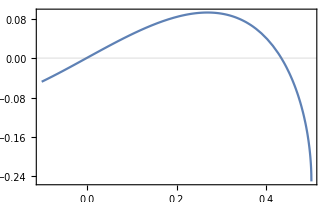

```mathematica
Clear[f];
f[x_] := x √(1-4 x^2)-x/2;
Plot[f[x],{x,-0.1,1/2},GridLines->{None,{0}}]
```

```mathematica
FindRoot[f[x],{x,0.1}]
FindRoot[f[x],{x,0.3}]
```

{x→-2.13961×10^-15}

{x→0.433013}

It is move convenient to bracket the roots before. 
i.e., one first determines intervals [a_i,b_i], inside which there is guaranteed to be a root.

```mathematica
brac=BracketRoot[f,0,1/2,100]
```

{{0.,0.00505051},{0.429293,0.434343}}

The actual position of the roots can now be determined using FindRoot and supplying the intervals as initial guesses.

```mathematica
FindRoot[f[x],{x,brac⟦1,1⟧,brac⟦1,2⟧}]
```

{x→0.}

```mathematica
FindRoot[f[x],{x,brac⟦2,1⟧,brac⟦2,2⟧}]
```

{x→0.433013}

FindAllRoots[] does that automatically: first brackets, then finds roots.

```mathematica
MultipleRoots[f,0,1/2,100]
```

{0.,0.433013}

### LegendreGauss: numerical integration in a sphere

For functions that depend only on θ: 

∫_0^π  f(θ) sin(θ) dθ = ∑_i w_i f(p_i)

For functions of θ,ϕ:

∫_0^(2π) dϕ ∫_0^π sin(θ) dθ f(θ,ϕ) = ∑_i w_i f(θ_i,ϕ_i)

```mathematica
Clear[LegendreGauss];
LegendreGauss[n_,prec_]:=Block[{roots,p,x,w},
roots=Solve[LegendreP[n,x]==0,x];
p=N[π/4(x+1)/.roots,prec];
w=(π/4)N[2(1-x^2)/((n+1)LegendreP[n+1,x])^2/.roots,prec];
{Join[p,p+π/2],Join[w Sin[p],w Sin[p+π/2]]}
];

LegendreGauss[nθ_,nϕ_,prec_]:=Block[{pθ,wθ,pϕ,wϕ,p,w},
{pθ,wθ} = LegendreGauss[nθ,prec];
pϕ = linspace[0,2π,nϕ];
wϕ = ConstantArray[(2π)/(nϕ-1),{nϕ}];  
p = Tuples[{pθ,pϕ}];
w = Times@@#&/@Tuples[{wθ,wϕ}];
{p,w}
]

LegendreGauss::usage = "Generates grid of (points,weights) for numerical integration in a sphere.";
```

#### Example usage

For integration of a function that only depends on θ:

```mathematica
(* Output is a list of (points,weights) *)
{p,w} = LegendreGauss[10,MachinePrecision]
```

{{0.668473,0.902324,0.44501,1.12579,0.251791,1.31901,0.105979,1.46482,0.0204938,1.5503,2.23927,2.47312,2.01581,2.69658,1.82259,2.8898,1.67678,3.03561,1.59129,3.1211},{0.143855,0.182148,0.0910359,0.190885,0.0428694,0.166644,0.0124164,0.11672,0.00107305,0.0523526,0.182148,0.143855,0.190885,0.0910359,0.166644,0.0428694,0.11672,0.0124164,0.0523526,0.00107305}}

```mathematica
(* Weird function *)
f[θ_]:=Cos[θ]^3.3 θ^2;
NIntegrate[f[θ] Sin[θ],{θ,0,π}]
f[p].w
```

-0.820751-1.25768 ⅈ

-0.820751-1.25768 ⅈ

For integration over the sphere (θ,ϕ), the syntax is the same, except that the points are now given as tuples (θ_i,ϕ_i). 
The correspondence is thus 

∫_0^(2π) dϕ ∫_0^π sin(θ) dθ f(θ,ϕ) = ∑_i w_i f(θ_i,ϕ_i)

```mathematica
(* Integration on θ,ϕ *)
{p,w}=ThetaPhiQuadrature[10,10,MachinePrecision];
```

```mathematica
Clear[f]
f[{θ_,ϕ_}]:=Cos[θ]^2 θ^2 Sin[ϕ]^2.2;
NIntegrate[f[{θ,ϕ}] Sin[θ],{θ,0,π},{ϕ,0,2π}]
(f[#]&/@p).w
```

6.16758+2.00397 ⅈ

6.16897+2.00442 ⅈ

Precision can be increased by increasing the number of points. 
Or one can also change MachinePrecision to another number

```mathematica
LegendreGauss[10,30]
```

{{0.668472530984266011469854691672,0.902323795810630607761466999968,0.445010216823424314597124473959,1.12578610997147230463419721768,0.251791136260741321809901259633,1.31900519053415529742142043201,0.105978983977506509750248854852,1.46481734281739010948107283679,0.0204937645792770232280713992446,1.5503025622156195960032502924,2.23926885777916263070117638331,2.47312012260552722699278869161,2.0158065436183209338284461656,2.69658243676636892386551890932,1.82258746305563794104122295127,2.88980151732905191665274212365,1.676775310772403128981570546492,3.03561366961228672871239452843,1.591290091374173642459393090884,3.12109888901051621523457198403},{0.14385538752309044885957303617,0.1821482346882985372549086829,0.091035865820022234120465153258,0.19088460570231520153832453701,0.042869357084832244193330384926,0.16664426881031131875686955118,0.012416414490632614636496831801,0.11672025914509963578847068992,0.0010730511780787534942954697879,0.052352555557319011357265657761,0.1821482346882985372549086829,0.14385538752309044885957303617,0.19088460570231520153832453701,0.091035865820022234120465153258,0.16664426881031131875686955118,0.042869357084832244193330384926,0.11672025914509963578847068992,0.0124164144906326146364968318,0.052352555557319011357265657761,0.001073051178078753494295469788}}

### RK4: manual Runge-Kutta 4, for silly things

Based on: https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods

RK4:   input is a time-independent function f(x). 
RK4t: f(t,x)

```mathematica
Clear[RK4,RK4t];
(* For time-indeendent RHS f(y) *)
RK4[f_,y0_,Δt_,tf_,onlyLastOutput_:False,quiet_:False]:=Module[{F},
(* input function f[y] *)
F[y_]:=Block[{k1,k2,k3,k4},
k1 = f[y];
k2 = f[y + Δt k1/2];
k3 = f[y + Δt k2/2];
k4 = f[y+Δt k3];
y + Δt/6(k1+2k2+2k3+k4)
];
If[quiet===False,
If[onlyLastOutput===False,
Transpose[{Range[0,tf,Δt],nestList[F,y0,Round[tf/Δt]]}],
nest[F,y0,Round[tf/Δt]]
],
If[onlyLastOutput===False,
Transpose[{Range[0,tf,Δt],NestList[F,y0,Round[tf/Δt]]}],
Nest[F,y0,Round[tf/Δt]]
]
]
]

(* for a time-dependent RHS f(t,y) -> y' *)
RK4t[f_,y0_,Δt_,tf_,onlyLastOutput_:False, quiet_:False]:=Module[{F},
(* input function f[t, y] *)
F[{t_,y_}]:=Block[{k1,k2,k3,k4},
k1 = f[t,y];
k2 = f[t+Δt/2,y + Δt k1/2];
k3 = f[t+Δt/2,y + Δt k2/2];
k4 = f[t+Δt,y+Δt k3];
{t+Δt,y + Δt/6(k1+2k2+2k3+k4)}
];

If[quiet===False,
If[onlyLastOutput===False,
nestList[F,{0,y0},Round[tf/Δt]],
nest[F,{0,y0},Round[tf/Δt]]⟦2⟧
],
If[onlyLastOutput===False,
NestList[F,{0,y0},Round[tf/Δt]],
Nest[F,{0,y0},Round[tf/Δt]]⟦2⟧
]
]

]
```

#### Example usage

Time-independent qubit dynamics
(This is just for illustrative purposes; see function UnitaryDynamics[] below for a properly quantum, implementation)

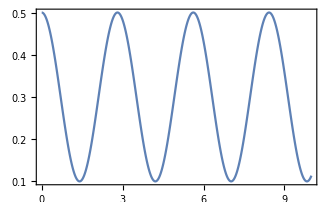

```mathematica
H = 1/2 σz+σx;
ψ0 = 1/(√2){1,1};

Clear[f];
f[ψ_]:=-ⅈ H.ψ;
ψ=RK4[f,ψ0,0.01,10];
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

The output is in general a list (t,x_t)

```mathematica
ψ=RK4[f,ψ0,0.01,0.02]
```

{{0.,{1/(√2),1/(√2)}},{0.01,{0.707063-0.0106064 ⅈ,0.707063-0.00353546 ⅈ}},{0.02,{0.70693-0.0212114 ⅈ,0.70693-0.00707048 ⅈ}}}

Optional last argument returns only the last output

```mathematica
ψ=RK4[f,ψ0,0.01,10,True]
```

{0.129907+0.932536 ⅈ,0.129907+0.310845 ⅈ}

Schrodinger equation for a driven qubit

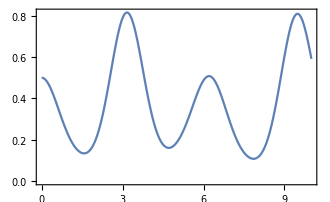

```mathematica
ψ0 = 1/(√2){1,1};
Clear[f];
f[t_,y_]:=With[{H=1/2 σz + Cos[t] σx}, -ⅈ H.y]

ψ=RK4t[f,ψ0,0.001,10];
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

Compare with Mathematica’s built in function

```mathematica
sol2 = NDSolveValue[{psi'[t]==-ⅈ  ({{1/2, Cos[t]}, {Cos[t], -1/2}}).psi[t],psi[0]==ψ0},psi,{t,0,10}];
```

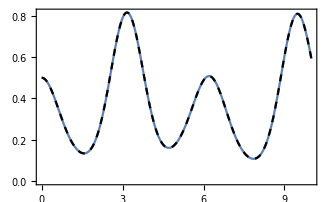

```mathematica
Show[
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ],
Plot[Abs[sol2[t]⟦2⟧]^2,{t,0,10},PlotStyle->Directive[Black,Dashed]]]
```

Unitary that generates a process from 0 to τ

```mathematica
Clear[f];
f[t_,y_]:=With[{H=1/2 σz + Cos[t] σx}, -ⅈ H.y]
τ = 10.0;
U0 = NEye[2];
U=RK4t[f,U0,0.01,10,True]//mf;
```

(0.223573+0.234591 ⅈ | -0.848373+0.418624 ⅈ
0.848373+0.418624 ⅈ | 0.223573-0.234591 ⅈ)

```mathematica
U†.U//mf;
```

(1. | 0
0 | 1.)

#### RK4 for Schrödinger’s equation

```mathematica
Clear[H,f,Δt];
f[t_,y_]:=-ⅈ H y;
RK4t[f,y,Δt,Δt,True]/y//Expand
```

1-ⅈ H Δt-(H^2 Δt^2)/2+1/6 ⅈ H^3 Δt^3+(H^4 Δt^4)/24

```mathematica
RK4[-ⅈ H #&,y,Δt,Δt,True]/y//Expand
```

1-ⅈ H Δt-(H^2 Δt^2)/2+1/6 ⅈ H^3 Δt^3+(H^4 Δt^4)/24

```mathematica
Clear[A]
```

```mathematica
RK4[A #&,y,Δt,Δt,True]/y//Expand
```

1+A Δt+(A^2 Δt^2)/2+(A^3 Δt^3)/6+(A^4 Δt^4)/24

```mathematica
Series[Exp[A Δt],{Δt,0,4}]
```

1+A Δt+(A^2 Δt^2)/2+(A^3 Δt^3)/6+(A^4 Δt^4)/24+O[Δt]^5

## Probability & Statistics

### Gram-Chalier-Edgeworth approximation of nearly Gaussian probability distributions

```mathematica
GramChalierEdgeworth[cumulants_]:=Module[{d = Length@cumulants,μ,σ,κlist,Bn},
μ = cumulants⟦1⟧;
σ = √cumulants⟦2⟧;
κlist = Join[{0,0},cumulants⟦3;;-1⟧];
Bn = Table[Sum[BellY[n,k,κlist],{k,1,n}],{n,3,d}];

Function[1/(√(2π σ^2))Exp[-(#-μ)^2/(2 σ^2)] (1 + Sum[1/(n!σ^n)Bn⟦n-2⟧ 2^(-n/2)HermiteH[n,(#-μ)/(σ √2)],{n,3,d}])]

(*1/(√(2π σ^2))Exp[-(x-μ)^2/(2 σ^2)] (1 + Sum[1/(n!σ^n)Bn⟦n-2⟧ 2^(-n/2)HermiteH[n,(x-μ)/(σ √2)],{n,3,d}])
*)]
```

#### Example

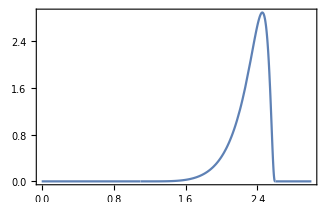

```mathematica
p=JohnsonDistribution["SB", -2,1.2,1.1,1.5];
Plot[PDF[p,x],{x,0,3}]
```

```mathematica
cumulants = Table[Cumulant[p,n],{n,1,30}]
```

{2.31925,0.0325114,-0.00707345,0.00166633,-0.000179148,-0.000219636,0.000250069,-0.000145431,3.02284×10^-6,0.000118885,-0.000171368,0.000111957,0.0000770668,-0.000345977,0.000514536,-0.000228521,-0.000937044,0.00295942,-0.00409383,-0.000980908,0.0209836,-0.0568379,0.0613496,0.139653,-0.865989,2.04755,-0.85214,-13.6282,60.952,-117.656}

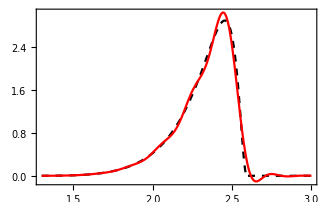

```mathematica
papprox= GramChalierEdgeworth[cumulants⟦1;;30⟧];
Plot[{PDF[p,x],papprox[x]},{x,1.3,3},PlotStyle->{Directive[Black,Dashed],Red,Blue}]
```

### SillySample: sample (inefficiently) from any probability distribution

```mathematica
(* The Ps do not have to be normalised *)
Clear[SillySample];
SillySample[xs_?VectorQ,Ps_?VectorQ,nsamp_:1]:=If[nsamp===1,RandomChoice[Ps->xs],RandomChoice[Ps->xs,nsamp]]
SillySample[P_?MatrixQ,nsamp_:1]:=SillySample[P⟦All,1⟧,P⟦All,2⟧,nsamp]
```

#### Example usage

Possible input syntax, with xs, Ps being vectors and nsamp being a number.

SillySample[xs,Ps]
SillySample[{xs,Ps}ᵀ]
SillySample[{xs,Ps}ᵀ,nsamp]
SillySample[xs,Ps,nsamp]

Sample the equilibrium distribution of a classical anharmonic oscillator

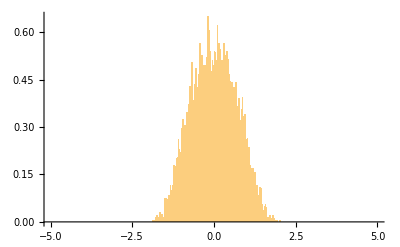

Compare with the exact distribution

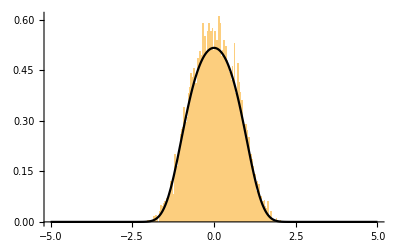

```mathematica
Z = NIntegrate[Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,-∞,∞}];

Show[
Histogram[samp,{-5,5,0.02},"PDF"],
Plot[1/Z Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,-5,5},PlotStyle->Black]]
```

Multidimensional distributions: Sample both x and p

```mathematica
Clear[prob];
prob[{x_,p_}]:=Exp[-(p^2/(2m)+1/2 m ω^2 x^2+1/4 Ω x^4)];
xs = range[-10,10,0.1];
ps = range[-10,10,0.1];
xps = Tuples[{xs,ps}];
Ps = prob[#]&/@xps;
samp = SillySample[xps,Ps,10^4];
Histogram3D[samp]
```

-Graphics3D-

#### Comparison with built in samplers

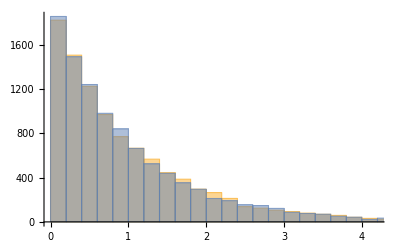

```mathematica
Clear[x,P];

rand1 = RandomVariate[ExponentialDistribution[1],10^4];
xs = range[0,20,0.02];
rand2 = SillySample[xs,Exp[-xs],10^4];
Histogram[{rand2,rand1}]
```

```mathematica
PairedHistogram[rand1,rand2]
```

-Graphics-

#### Alternative version

```mathematica
SillySample2[xs_?VectorQ,Ps_?VectorQ,nsamp_:1]:=Module[{Fs=Accumulate[Ps]/(Total@Ps),r,tab},
r = RandomReal[{0,1},nsamp];
tab=1-UnitStep@Table[f-r,{f,Fs}];
xs[[Total@tab]]
]
```

```mathematica
m = 1;
ω = 1;
Ω = 1.;
T = 1;
xs = range[-5,5,0.02];
Ps = Table[Exp[-(1/2 m ω^2 x^2+1/4 Ω x^4)],{x,xs}];
```

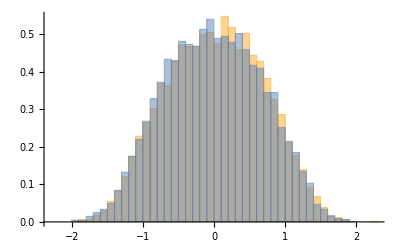

```mathematica
samp = SillySample[xs,Ps,10^4];
samp2 = SillySample2[xs,Ps,10^4];
Histogram[{samp,samp2},{-2.3,2.3,0.1},"PDF"]
```

This is analogous to Mathematica’s CovarianceFunction, but somehow is much faster.

```mathematica
Clear[TwoPointCorrelation];
TwoPointCorrelation[data_,hmax_,dt_:None,steps_:1]:=Module[{𝒩=Length@data,ave = Mean[data],vec1,M,corr},
vec1 = data⟦1;;𝒩-hmax⟧;
M = Table[data⟦1+i;;𝒩-hmax+i⟧,{i,1,hmax,steps}];
corr=1/𝒩(M.vec1-ave^2);
If[dt===None,corr,{dt Range[1, hmax,steps],corr}ᵀ]
]
```

### FourierWithFreqs

```mathematica
(* Computes ∫_(-∞)^∞ dk C(k) e^ikx for a generic function C(k) and a discrete set of points x from Subscript[x, i] to Subscript[x, f] in steps of dx *)

(* To compute with e^-ikx use "sign = -1" *)
Clear[FourierWithFreqs]
FourierWithFreqs[𝒞_,xi_,xf_,dx_,sign_:1]:=Module[{xs,M,dk,kf,ki,ur,P},
xs = range[xi,xf,dx];
M = Length@xs;
If[EvenQ[M],
M = M+1;
xs = range[xi,xf+dx,dx]
];
dk =(2π)/(M dx);
kf = (M-1)/M π/dx;
ki = -kf;
If[sign==1,
ur = Table[ⅇ^(ⅈ xi(r-1)dk)𝒞[ki + (r-1) dk],{r,1,M}];
P=dk  √M Table[ⅇ^(ⅈ ki xi+ⅈ ki(s-1) dx),{s,1,M}]Fourier[ur]//Chop(*//Reverse*);
,
ur = Table[ⅇ^(-ⅈ xi(r-1)dk)𝒞[ki + (r-1) dk],{r,1,M}];
P=dk  √M Table[ⅇ^(-ⅈ ki xi-ⅈ ki(s-1) dx),{s,1,M}]InverseFourier[ur]//Chop(*//Reverse*);
];
(*{xs[[2;;-1;;1]],P[[1;;-2;;1]]}ᵀ*)
{xs,P}ᵀ
]
```

```mathematica
(* OLD VERSION *)
(*Clear[FourierWithFreqs];
FourierWithFreqs[x_,dt_,transform_:Fourier]:=Module[{d,xf,ωs,ωs2,hamm},
d = Length@x;
If[OddQ[d],d=d-1];
hamm = Table[1/2(1.0-Cos[(2π j)/d]),{j,0,d-1}];
xf = transform[x⟦1;;d⟧ hamm];
ωs = Range[0,d/2] (2π)/(d dt);
ωs2 = -Reverse@Drop[Drop[ωs,1],{-1}];
{Join[ωs2,ωs],Join[xf⟦d/2+2;;d⟧,xf⟦1;;d/2+1⟧]}ᵀ
]*)
```

#### Example usage

Compute the PDF of a distribution from the Characteristic Function

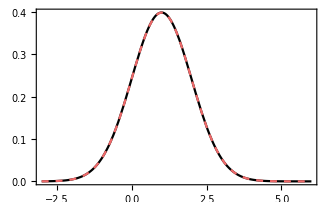

```mathematica
dist=NormalDistribution[1.,1.0];
P=FourierWithFreqs[1/(2π)CharacteristicFunction[dist,#]&,-3,6,0.1,-1];
Show[
Plot[PDF[dist,x],{x,-3,6},PlotStyle->Black],
ListLinePlot[P,PlotStyle->Directive[red,Dashed]]
]
```

### PowerSpectrum: Computes the FFT and the power spectrum with the actual frequencies in the horizontal axis

```mathematica
Clear[PowerSpectrum];
PowerSpectrum[x_,dt_,averaging_:1,overlap_:0.3]:=Module[{d,xf,ωs,hamm,S,k,xs,Ss},
d = Length@x;
If[OddQ[d],d=d-1];

k=If[averaging==1,d,(2d)/(2averaging-1)//Floor]; 
If[OddQ[k],k=k-1];

(*hamm = Table[1/2(1.0-Cos[(2π j)/k]),{j,0,k-1}]; *)

ωs = Range[1,k/2] (2π)/(k dt); 
ωs = Join[-Reverse@Drop[ωs,{-1}],ωs];

xs  = Partition[x,k,Floor[overlap k]];

xf = Table[Fourier[(*hamm*)(xx⟦1;;k⟧-Mean[xx])],{xx,xs}]; 
S = Mean@Table[dt Abs[xxf]^2,{xxf,xf}];      

{ωs,Join[S⟦k/2+2;;k⟧,S⟦2;;k/2+1⟧]}ᵀ  
]
```

#### Example usage

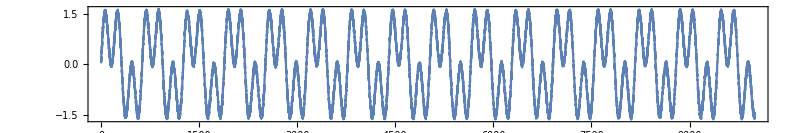

```mathematica
dt = 0.01;
𝒩 = 10000;
data = Table[Sin[n dt] + Sin[3 n dt],{n,1,𝒩}] + RandomReal[{-0.1,0.1},𝒩];
ListLinePlot[data,AspectRatio->1/6,ImageSize->800]
```

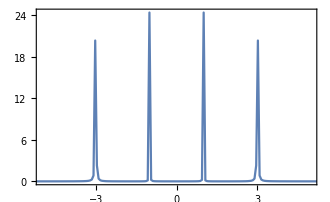

```mathematica
ListLinePlot[PowerSpectrum[data,dt],PlotRange->{{-5,5},All}]
```

#### Comparison with Mathematica’s PowerSpectralDensity

```mathematica
proc=ARMAProcess[1,{.5},{.3},1];
data=RandomFunction[proc,{500}];
```

```mathematica
sd=PowerSpectralDensity[data,w];
sd2 = PowerSpectrum[data["Values"],1,1];
```

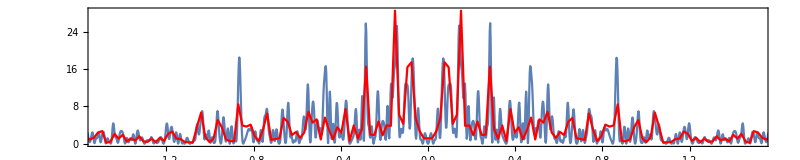

```mathematica
Show[
Plot[{sd},{w,-π,π},PlotRange->All],
ListLinePlot[sd2,PlotStyle->{Red},PlotRange->All],
AspectRatio->1/5,ImageSize->800,
PlotRange->{{-1.5,1.5},All}
]
```

### butter: Butterworth Filter

Based on https://mathematica.stackexchange.com/questions/46500/data-filtering-using-butterworth-filter

```mathematica
Clear[butter];
butter[data_,ωc_,dt_:1,order_:2]:=Module[{f,b},
f=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],data];
b=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],Reverse[data]];
(f+Reverse[b])/2
]
```

#### Example usage

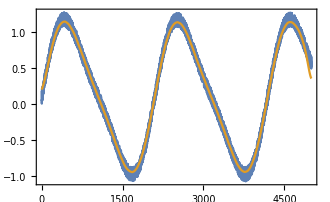

```mathematica
dt = 0.01;
ts = range[0,50,dt];
data = Table[Sin[0.3 t] + 0.2 Sin[0.6 t],{t,ts}]+0.2 RandomReal[{0,1},Length@ts];
filt = butter[data,2,dt];
ListLinePlot[{data,filt}]
```

### DistributionFromData: builds a distribution P(x), from a set of outcomes (X_1,X_2,...)

```mathematica
Clear[DistributionFromData];
DistributionFromData[data_,ΔΔx_:Automatic]:=Module[{Δx,max,min,d,x,p},
min = Min@data;
max = Max@data;
d = Length@data;
Δx=Which[
NumberQ[ΔΔx],ΔΔx,
matchString["discrete",ΔΔx] &&Not[ Head[data⟦1⟧]===Real],First@DeleteCases[Sort@Differences@Sort@Y,0],
True,10(max-min)/d];

x = N@Range[min,max,Δx];
p=BinCounts[data, {min,max+Δx,Δx}]/d//N;    

{x,p}ᵀ
]
```

#### Example usage

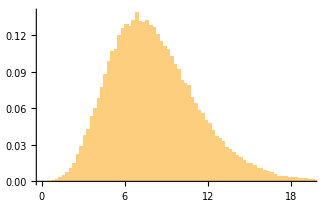

```mathematica
(* Generate samples *)
dist = NegativeBinomialDistribution[2,0.2];
n = 4;
nsamp=10^5;
Y = 1/n Total@RandomVariate[dist,{n,nsamp}];
Histogram[Y,{0.25},"PDF"]
```

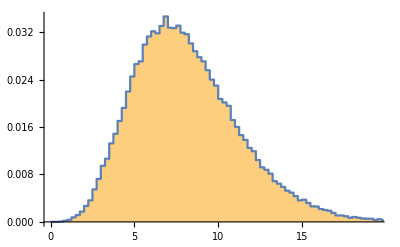

```mathematica
(* Build distribution *)
(* Option "discrete" causes functions to look for the appropriate Δx *)
P = DistributionFromData[Y,"discrete"];
Show[
Histogram[Y,{0.25},"Probability"],
ListLinePlot[P,InterpolationOrder->0]]
```

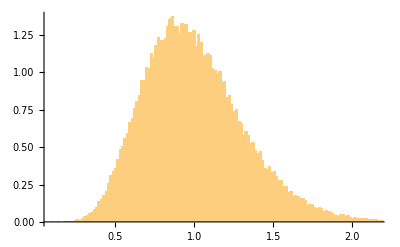

```mathematica
(* Same, but for a distribution with support over the entire real axis *)
dist = GammaDistribution[2.0,0.5];
n = 5;
nsamp=10^5;
Y = 1/n Total@RandomVariate[dist,{n,nsamp}];
Histogram[Y,{0.015},"PDF"]
```

```mathematica
P = DistributionFromData[Y,Δx];
```

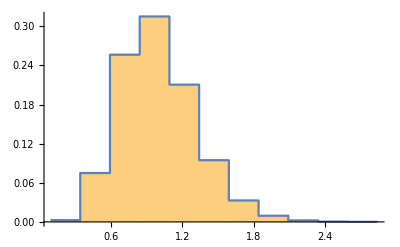

```mathematica
(* Build distribution with a specific choice of Δx *)
Δx=0.25;
P = DistributionFromData[Y,Δx];
Show[
Histogram[Y,(*{Δx}*){Min@Y,Max@Y,Δx},"Probability"],
ListLinePlot[P,InterpolationOrder->0]]
```

## Quantum theory, information & thermodynamics

## Important Hamiltonians, unitary dynamics

### Tight-binding Hamiltonian

```mathematica
Clear[TightBindingHamiltonian];
TightBindingHamiltonian[L_,V_:1,J_:1]:=J StiffnessMatrix[L] + Which[
ArrayQ[V],DiagonalMatrix@SparseArray[Flatten[Table[V,{Ceiling[L/Length@V]}]]⟦1;;L⟧],
True,toeplitzMatrix[V,1,L]
];
```

```mathematica
Clear[TightBindingHamiltonianPBC];
TightBindingHamiltonianPBC[L_,V_:1,J_:1]:=J CirculantMatrix[L] + Which[
ArrayQ[V],DiagonalMatrix@SparseArray[Flatten[Table[V,{Ceiling[L/Length@V]}]]⟦1;;L⟧],
True,toeplitzMatrix[V,1,L]
];
```

#### Example usage

```mathematica
TightBindingHamiltonian[3]//mf;
```

(1 | -1 | 0
-1 | 1 | -1
0 | -1 | 1)

```mathematica
TightBindingHamiltonian[3,ϵ0]//mf;
```

(ϵ0 | -1 | 0
-1 | ϵ0 | -1
0 | -1 | ϵ0)

```mathematica
TightBindingHamiltonian[3,{ϵ1,ϵ2,ϵ3}]//mf;
```

(ϵ1 | -1 | 0
-1 | ϵ2 | -1
0 | -1 | ϵ3)

```mathematica
TightBindingHamiltonian[4,{ϵ1,ϵ2}]//mf;
```

(ϵ1 | -1 | 0 | 0
-1 | ϵ2 | -1 | 0
0 | -1 | ϵ1 | -1
0 | 0 | -1 | ϵ2)

```mathematica
TightBindingHamiltonian[3,ϵ,j]//mf;
```

(ϵ | -j | 0
-j | ϵ | -j
0 | -j | ϵ)

```mathematica
TightBindingHamiltonianPBC[4,{ϵ1,ϵ2},J]//mf;
```

(ϵ1 | -J | 0 | -J
-J | ϵ2 | -J | 0
0 | -J | ϵ1 | -J
-J | 0 | -J | ϵ2)

### Non-interacting Hamiltonians and quasi-periodic sequences

```mathematica
(* Subscript[λ, c] = 2 *)
Clear[aubryAndreHarper];
aubryAndreHarper[L_,ϕ_:0,α_:0]:=Table[Cos[ 2.0π GoldenRatio n + ϕ]/(1-α Cos[2π GoldenRatio n + ϕ]),{n,1,L}];
```

```mathematica
Clear[fibonacciString];
fibonacciString[L_]:=Table[IntegerPart[(n+1)1/GoldenRatio^2]-IntegerPart[n 1/GoldenRatio^2],{n,1,L}];

fibonacciString[L_,a_,b_]:=fibonacciString[L]/.{0->a,1->b}
```

Based on https://arxiv.org/pdf/1803.03609.pdf

```mathematica
sshHamiltonian[L_,τ0_,δτ_,ϵ_:1]:= Module[{hop = Table[τ0-(-1)^j δτ,{j,1,L-1}]},
- ϵ DiagonalMatrix[ConstantArray[ϵ,L]]  + DiagonalMatrix[hop,1] + DiagonalMatrix[hop,-1]//SparseArray
]
```

#### Example usage

The model has a localization transition at λ = 2.0

```mathematica
Clear[λ];
TightBindingHamiltonian[6,λ aubryAndreHarper[6]]//mf;
```

(-0.737369 λ | -1 | 0 | 0 | 0 | 0
-1 | 0.0874257 λ | -1 | 0 | 0 | 0
0 | -1 | 0.608439 λ | -1 | 0 | 0
0 | 0 | -1 | -0.984713 λ | -1 | 0
0 | 0 | 0 | -1 | 0.843755 λ | -1
0 | 0 | 0 | 0 | -1 | -0.259604 λ)

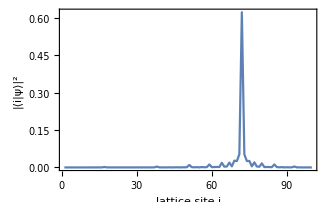

```mathematica
λ = 2.05;
(*λ = 1.95;*)
h = TightBindingHamiltonian[100,λ aubryAndreHarper[100]];
ψ = Eigvecs[h,10]⟦All,1⟧;
ListLinePlot[Abs[ψ]^2,PlotRange->All,
FrameLabel->{"lattice site i","|⟨i|ψ⟩|^2"}]
```

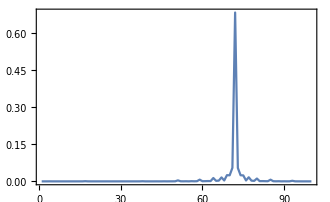

```mathematica
λ = 2.1;
h = TightBindingHamiltonian[100,λ aubryAndreHarper[100]];
ψ = Eigvecs[h,1]⟦All,1⟧;
ListLinePlot[Abs[ψ]^2,PlotRange->All]
```

Plot the average inverse participation ratio for different system sizes

```mathematica
inverseParticipationRatio[ψ_]:=Abs[ψ]^4//Total
```

```mathematica
Clear[λ,h,ψ,IPRs,L,Ls,tab];
Ls={100,200,300};
do[
tab[L] = Table[
h=TightBindingHamiltonian[L,λ aubryAndreHarper[L]];
ψs = Quiet@Eigvecs[h];
IPRs = Table[inverseParticipationRatio[ψ],{ψ,ψs}];
{λ,Mean@IPRs},{λ,0,2.5,0.03}];
,{L,Ls}]
```

00:00:01TimeObject[{0,0,1},Instant]

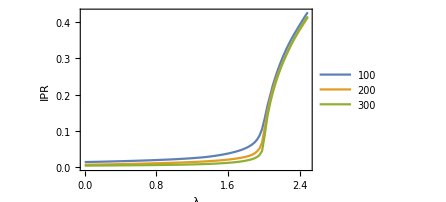

```mathematica
ListLinePlot[Evaluate@Table[tab[L],{L,Ls}],
FrameLabel->{"λ","IPR"},
PlotLegends->legend[Ls,{0.3,0.5}]]
```

### UnitaryDynamics

Input can be a function H(t), or a list {H(0), H(dt), H(2dt),...}

```mathematica
Clear[UnitaryDynamics]
UnitaryDynamics[H_?ListQ,dt_,τ_,y0_:"id",onlyLastOutput_:False]:=Module[{ntrotter,ψ0,f,ψ,results},
ntrotter = Round[τ/dt];
ψ0 = If[y0==="id",Eye[Length@H⟦0⟧],y0];
ψ = ψ0;
If[onlyLastOutput===False,
Transpose[{Range[0,(Length[H]-1) dt,dt],Table[ψ=MatrixExp[-ⅈ h dt,ψ],{h,H}]}],
Do[ψ=MatrixExp[-ⅈ h dt,ψ],{h,H}]; ψ
]
]

UnitaryDynamics[H_,dt_,τ_,y0_:"id",onlyLastOutput_:False]:=Module[{ntrotter,ψ0,f,ψ},
ntrotter = Round[τ/dt];
ψ0 = If[y0==="id",Eye[Length@H[0]],y0];
If[y0==="id",
f[{t_,ψ_}]:={t+dt,MatrixExp[-ⅈ dt H[t]].ψ},
f[{t_,ψ_}]:={t+dt,MatrixExp[-ⅈ dt H[t],ψ]}];

If[onlyLastOutput===False,
NestList[f,{0,ψ0},ntrotter],
Nest[f,{0,ψ0},ntrotter]⟦2⟧
]
]
```

#### Example usage

Input a function H(t)

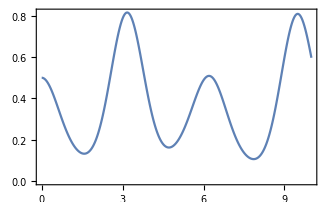

```mathematica
Clear[H];
H[t_]:= 1/2 σz + Cos[t] σx
ψ0 = 1/(√2){1,1};
ψ=UnitaryDynamics[H,0.01,10,ψ0] ;
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

Input a pre-Trotterrized list

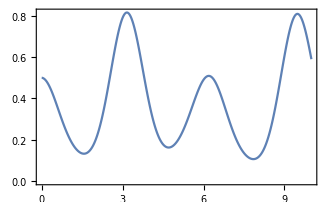

```mathematica
Hlist = Table[H[t],{t,0,10,0.01}];
ψ=UnitaryDynamics[Hlist,0.01,10,ψ0];
ListLinePlot[{ψ⟦All,1⟧,Abs[ψ⟦All,2,2⟧]^2}ᵀ]
```

Unitary from 0 to τ

```mathematica
Clear[H];
H[t_]:= 1/2 σz + Cos[t] σx

U=UnitaryDynamics[H,0.01,10,"id",True] //mf;
```

(0.227387+0.235257 ⅈ | -0.850269+0.412301 ⅈ
0.850269+0.412301 ⅈ | 0.227387-0.235257 ⅈ)

```mathematica
U†.U//mf;
```

(1. | 0
0 | 1.)

### CounterDiabaticHamiltonian

Contributors: Steve Campbell & Giacomo Guarnieri.
Given a time-dependent Hamiltonian H(t)=∑_n E_n(t) |ψ_n(t)⟩⟨ψ_n(t)|, computes the counter-diabatic Hamiltonian used in shortcuts to adiabaticity:

H_CD(t) = i ∑_n |∂_t ψ_n⟩⟨ψ_n|

Input: 
- H(t) as a function
- final time t_f
- time step dt
Output: 
- {H(t), H_CD} , with each given as a list evaluated at times 0,dt,2dt,...,t_f.

```mathematica
Clear[CounterDiabaticHamiltonian];
CounterDiabaticHamiltonian[Hs_,tf_,dt_]:=Module[{Hbare,T,Vs,HCD,hcd,V},

Hbare = Table[Hs[t],{t,0,tf,dt}];
T = Length@Hbare;

Vs=Normal@Table[
V=Eigvecs[Hbare⟦n⟧];
(Vᵀ Exp[ⅈ Arg[V⟦1⟧]])ᵀ  (* fixes so that eigenvectors always have the same phases *)
,{n,T}];

HCD =  Table[
hcd=ⅈ((Vs⟦n+1⟧-Vs⟦n-1⟧)/(2dt)).Vs⟦n⟧†; 
(hcd+hcd†)/2,{n,2,T-1}];

HCD=Join[{0 Hbare⟦1⟧},HCD,{0 Hbare⟦1⟧}];
{Hbare,HCD}

]
```

#### Example usage: Landau-Zener avoided crossing with a linear ramp

```mathematica
Clear[H];
τQ=10^1;
Δ0=-5.;
Δd=10.;
ω0=0.5;

H[t_] := 1/2(ω0 σx+ (Δ0+Δd t/τQ) σz)
ψ0 = GroundState[H[0]];

(* Generate the Hamiltonians *)
{Hbare,HCD} = CounterDiabaticHamiltonian[H,τQ,dt=1/300];
```

```mathematica
(* Simulate unitary dynamics with the Bare Hamiltonian, and compute fidelity with ground state. *)
ψbare = UnitaryDynamics[Hbare,dt,τQ,ψ0];
fidBare=Table[Abs[GroundState[H[(n-1) dt]]*.ψbare⟦n,2⟧]^2,{n,1,Length@ψbare}];
```

```mathematica
(* Include counter-diabatic driving *)
ψCD = UnitaryDynamics[Hbare + HCD,dt,τQ,ψ0];
fidCD=Table[Abs[GroundState[H[(n-1) dt]]*.ψCD⟦n,2⟧]^2,{n,1,Length@ψCD}];
```

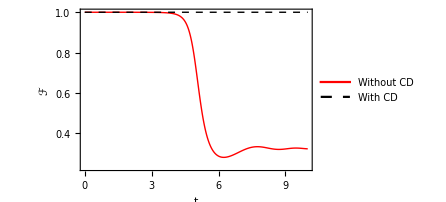

```mathematica
ListLinePlot[{fidBare,fidCD},DataRange->{0,τQ},PlotRangePadding->{None,0.05},PlotStyle->{{Thick,Red},{Thick,Black,Dashed}},FrameLabel->{"t","ℱ"},
PlotLegends->legend[{"Without CD","With CD"},{0.25,0.35}]
]
```

## Quantum information

### ThermalState

```mathematica
ThermalState[H_]:=Module[{ρ = MatrixExp[-H]},ρ/Tr[ρ]]
```

### DM: just normalizes thing so that it is a density matrix. Also works with probability vectors

```mathematica
Clear[DM];
DM[ρ_?MatrixQ]:=ρ/Tr[ρ];
DM[p_?VectorQ]:=p/Total[p];
```

#### Example usage

```mathematica
ρ = MatrixExp[-β σz]//DM
```

{{ⅇ^-β/(ⅇ^-β+ⅇ^β),0},{0,ⅇ^β/(ⅇ^-β+ⅇ^β)}}

### PTr: partial trace

You list what you want to trace: PTr[ρ,{1,4,5}] traces out subsystems 1, 4  and 5

Syntax: 
- Most general syntax is PTr[ρ,{1,4,5}, {d1,d2,d3,d4,d5}]
  
 -   PTr[ρ,{1,4,5}, d] = PTr[ρ,{1,4,5},{d,d,d,d,d}]

  -  PTr[ρ,{1,4,5}] = PTr[ρ,{1,4,5},{2,2,2,2,2}] (assumes qubits)

```mathematica
Clear[PTr]
PTr[state_,list_,locdimlist_]:=Module[{i,eye,v,L,n,tups,tab,𝒩,ρ},
ρ = If[Length@Dimensions[state]===2,state,out[state,state]];
n = Length@locdimlist;
Do[eye[l] = Eye[locdimlist⟦l⟧],{l,n}];

Do[v[l,i] = {eye[l]⟦i⟧}ᵀ,{l,n},{i,locdimlist⟦l⟧}];
tups = Tuples@Table[Range[1,l],{l,locdimlist⟦list⟧}];
tab = Table[
kron@@Table[If[MemberQ[list,l],v[l,j⟦Position[list,l]⟦1,1⟧⟧],eye[l]],{l,n}],{j,tups}];
Total@Table[(tab⟦i⟧)ᵀ.ρ.tab⟦i⟧,{i,Length@tab}]
];

PTr[ρ_,list_,locdim_?NumberQ]:= PTr[ρ,list,ConstantArray[locdim,Log[locdim, Length@ρ]]]

PTr[ρ_,list_]:=PTr[ρ,list,2];
```

#### Example usage

```mathematica
(* ρ = |Subscript[ψ, 1]⟩⟨Subscript[ψ, 1]|⊗|Subscript[ψ, 2]⟩⟨Subscript[ψ, 2]| *)
ψ1 = {1,1}//Normalize;
ψ2 = {2,ⅈ}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]]//mf;
```

(2/5 | -ⅈ/5 | 2/5 | -ⅈ/5
ⅈ/5 | 1/10 | ⅈ/5 | 1/10
2/5 | -ⅈ/5 | 2/5 | -ⅈ/5
ⅈ/5 | 1/10 | ⅈ/5 | 1/10)

```mathematica
PTr[kron[ψ1,ψ2],{2}]//mf (* ket as input *);
PTr[ρ,{2}]//mf (* density matrix as input *);
out[ψ1,ψ1]//mf;
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

```mathematica
PTr[ρ,{1}]//mf;
out[ψ2,ψ2]//mf;
```

(4/5 | -(2 ⅈ)/5
(2 ⅈ)/5 | 1/5)

(4/5 | -(2 ⅈ)/5
(2 ⅈ)/5 | 1/5)

```mathematica
(* PTr assumes in principle local dimension is d = 2. *)
(* If the dimensions are homogenous, pass out an extra number *)
ψ1 = {1,1,3}//Normalize;
ψ2 = {2,ⅈ,-3ⅈ}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]];
```

```mathematica
PTr[ρ,{2},3]//mf;
out[ψ1,ψ1]//mf;
```

(1/11 | 1/11 | 3/11
1/11 | 1/11 | 3/11
3/11 | 3/11 | 9/11)

(1/11 | 1/11 | 3/11
1/11 | 1/11 | 3/11
3/11 | 3/11 | 9/11)

```mathematica
PTr[ρ,{1},3]//mf;
out[ψ2,ψ2]//mf;
```

(2/7 | -ⅈ/7 | (3 ⅈ)/7
ⅈ/7 | 1/14 | -3/14
-(3 ⅈ)/7 | -3/14 | 9/14)

(2/7 | -ⅈ/7 | (3 ⅈ)/7
ⅈ/7 | 1/14 | -3/14
-(3 ⅈ)/7 | -3/14 | 9/14)

```mathematica
(* If each sub-system has a different dimension, pass out a list of dimensions *)
ψ1 = {1,1}//Normalize;
ψ2 = {1,2,3,4,5}//Normalize;
ρ = kron[out[ψ1,ψ1],out[ψ2,ψ2]];

PTr[ρ,{2},{2,5}]//mf;
out[ψ1,ψ1]//mf;
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

```mathematica
PTr[ρ,{1},{2,5}]//mf;
out[ψ2,ψ2]//mf;
```

(1/55 | 2/55 | 3/55 | 4/55 | 1/11
2/55 | 4/55 | 6/55 | 8/55 | 2/11
3/55 | 6/55 | 9/55 | 12/55 | 3/11
4/55 | 8/55 | 12/55 | 16/55 | 4/11
1/11 | 2/11 | 3/11 | 4/11 | 5/11)

(1/55 | 2/55 | 3/55 | 4/55 | 1/11
2/55 | 4/55 | 6/55 | 8/55 | 2/11
3/55 | 6/55 | 9/55 | 12/55 | 3/11
4/55 | 8/55 | 12/55 | 16/55 | 4/11
1/11 | 2/11 | 3/11 | 4/11 | 5/11)

### von Neumann & Rényi entropy

```mathematica
Clear[vonNeumann];
vonNeumann[ρ_?MatrixQ,base_:ⅇ]:= Module[{eigs,func},
eigs = Eigenvalues[ρ];
func[x_]:= If[NumberQ[x]&&Re@x<10^-12,0,-x Log[base,x]];
Chop@Sum[func[eigs⟦i⟧],{i,1,Length@eigs}]
]

vonNeumann[ρ_?VectorQ,base_:ⅇ]:= Module[{func},
func[x_]:= If[NumberQ[x]&&Re@x<10^-12,0,-x Log[base,x]];
Chop@Sum[func[ρ[[i]]],{i,1,Length@ρ}]
]
```

```mathematica
Clear[Renyi];
Renyi[ρ_?MatrixQ,α_,base_:ⅇ]:= Module[{eigs,func},
Which[
α ==1.0,vonNeumann[ρ],
α ==∞,-Log[base,Max@Eigenvalues[ρ]],
True,(eigs = Eigenvalues[ρ];
1/(1-α)Log[base,Sum[(eigs⟦i⟧)^α,{i,1,Length@eigs}]])]//Chop
]

Renyi[ρ_?VectorQ,α_,base_:ⅇ]:= Module[{func},
Which[
α ==1.0,vonNeumann[ρ],
α ==∞,-Log[base,Max@ρ],
True,(
1/(1-α)Log[base,Sum[(ρ⟦i⟧)^α,{i,1,Length@ρ}]])]//Chop
]
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
vonNeumann[ρ]
Renyi[ρ,3]
```

0.589514

0.458145

```mathematica
Renyi[ρ,1] (* returns von Neumann *)
```

0.589514

```mathematica
Renyi[ρ,0]
```

0.693147

```mathematica
Renyi[ρ,∞]
```

0.323507

### Kullback-Leibler & Rényi divergences: Quantum relative entropy

```mathematica
(* D(ρ||σ) *)
Clear[KullbackLeibler];
KullbackLeibler[ρ_?MatrixQ,σ_?MatrixQ]:=Module[{S1,S2,λ,Q,log},

S1 = vonNeumann[ρ];
{λ,Q} = Eigensystem[σ];
Q = Qᵀ; 
log = DiagonalMatrix@Log[λ];
S2 = - Tr[Q†.ρ.Q.log];
-S1+S2//Chop
]

KullbackLeibler[p_?VectorQ,q_?VectorQ]:=Total@Table[If[Abs[p⟦i⟧]<10^-12,0,p⟦i⟧ Log[p⟦i⟧/q⟦i⟧]],{i,Length@p}]
```

```mathematica
(* Subscript[D, α](ρ||σ) *)
Clear[RenyiDivergence];
RenyiDivergence[ρ_?MatrixQ,σ_?MatrixQ,α_]:=Module[{S1,S2,λ,Q,log,m1},

If[Abs[α-1]<10^-12,KullbackLeibler[ρ,σ],
m1 = MatrixPower[σ,(1-α)/(2α)];
-1/(1-α)Log@Tr[MatrixPower[m1.ρ.m1,α]]]//Chop
]
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
σ = ({{0.3, 0}, {0, 0.7}});
KullbackLeibler[ρ,σ]
```

0.0213498

```mathematica
ρ = ({{0.3, 0}, {0, 0.7}});
σ = ({{0.7, 0}, {0, 0.3}});
KullbackLeibler[ρ,σ]
```

0.338919

```mathematica
KullbackLeibler[ρ,ρ]
```

0

```mathematica
(* Also defined for vectors *)
p = {0.1,0.4,0.5};
q = {0.05,0.6,0.35};
KullbackLeibler[p,q]
```

0.0854661

### Mutual Information

Usage is similar to partial trace function.

```mathematica
Clear[MutualInformation];
MutualInformation[ρ_,{A_,B_},locdimlist_]:=Module[{ρA,ρB,ρAB,n},
n= Length@locdimlist;(* Number of sub-systems in this case *)
ρA = PTr[ρ,Complement[Range[n],Flatten@{A}],locdimlist];
ρB = PTr[ρ,Complement[Range[n],Flatten@{B}],locdimlist];
ρAB = PTr[ρ,Complement[Range[n],Flatten@Join[Flatten@{A},Flatten@{B}]],locdimlist];
Chop[vonNeumann[ρA]+vonNeumann[ρB]-vonNeumann[ρAB],10^-12]
];

(* When all subsystems have different dimensions *)
MutualInformation[ρ_,{A_,B_},locdim_?NumberQ]:= MutualInformation[ρ,{A,B},ConstantArray[locdim,Log[locdim, Length@ρ]]]

(* When all subsystems are qubits *)
MutualInformation[ρ_,{A_,B_}]:= MutualInformation[ρ,{A,B},ConstantArray[2,Log[2, Length@ρ]]]
```

#### Example usage

Usage is similar to partial trace function.

```mathematica
ψ = 1/(√2){1,0,0,1};
ρ = out[ψ,ψ];
MutualInformation[ρ,{1,2}]
MutualInformation[ρ,{1,2},2]
MutualInformation[ρ,{1,2},{2,2}]
```

2 Log[2]

2 Log[2]

2 Log[2]

```mathematica
(* 3 qubits *)
ψ = 1/(√2){1,0,0,1,0,0,1,0};
ρ = out[ψ,ψ];
MutualInformation[ρ,{1,2},2]
MutualInformation[ρ,{1,2},{2,2,2}]
```

Log[2]/2

Log[2]/2

### Concurrence & Entanglement of Formation

R = √(√ρ(σ_y⊗σ_y)ρ^*(σ_y⊗σ_y)√ρ)

```mathematica
Concurrence[ρ_]:=Module[{σy,ρt,ρsq,R,eigs},
σy = {{0,-ⅈ},{ⅈ,0}};
ρt = kron[σy,σy].ρ*.kron[σy,σy];
ρsq = MatrixPower[ρ,1/2];
R = MatrixPower[ρsq.ρt.ρsq,1/2];
eigs = Chop@Reverse@Sort@Eigenvalues[R];
Max[0,Re[eigs⟦1⟧-eigs⟦2⟧-eigs⟦3⟧-eigs⟦4⟧]]
];
```

```mathematica
EntanglementOfFormation[ρ_,b_:2]:=Module[{c,h},
h[x_]:=If[(x==0)||(x==1),0,-x Log[b,x]-(1-x)Log[b,1-x]];
c = Concurrence[ρ];
h[(1+√(1-c^2))/2]
]
```

#### Example usage

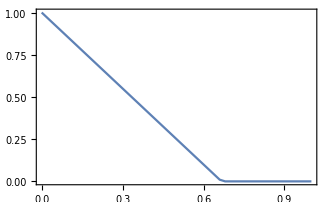
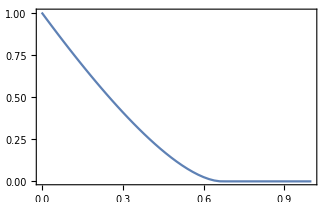

```mathematica
ψ = 1/(√2){0,1,1,0};
ρ = (1-p) out[ψ,ψ]+p Eye[4]/4;
{ListLinePlot[Table[{p,Concurrence[ρ]},{p,0,1,0.02}]],
ListLinePlot[Table[{p,EntanglementOfFormation[ρ]},{p,0,1,0.02}]]}
```

### Quantum Fidelity

```mathematica
Clear[QuantumFidelity];
QuantumFidelity[ρ_,σ_]:=Tr[MatrixPower[MatrixPower[ρ,1/2].σ.MatrixPower[ρ,1/2],1/2]]^2
```

#### Example usage

```mathematica
ρ = ({{0.3, 0}, {0, 0.7}});
σ = ({{0.7, 0}, {0, 0.3}});
QuantumFidelity[ρ,σ]
```

0.84

### Relative Entropy of Coherence with respect to the eigenbasis of an operator X

Computes the relative entropy of coherence of a state ρ in the basis of an observable X

C_X(ρ) = S(Δ_X(ρ)) - S(ρ)

where Δ_X is the maximally dephasing operation.

```mathematica
Clear[RelativeEntropyofCoherence];
RelativeEntropyofCoherence[ρ_,X_]:=Module[{v,V,Δρ},
V = Normalize/@Eigenvectors[X];
Δρ = Total@Table[out[v,v].ρ.out[v,v],{v,V}];
Chop[vonNeumann[Δρ]-vonNeumann[ρ],10^-12]
];
```

#### Example usage

```mathematica
ρ = ({{0.3, 0.1}, {0.1, 0.7}});
A = ({{1, 0}, {0, -1}});
FullDephasing[ρ,A]//mf;
```

(0.3 | 0.
0. | 0.7)

```mathematica
ρ = ({{0.3, 0.03+ⅈ 0.01}, {0.03-ⅈ 0.01, 0.7}});
```

```mathematica
RelativeEntropyofCoherence[ρ,σz]
```

0.00211989

```mathematica
(* Is the same as *)
KullbackLeibler[ρ,FullDephasingMap[ρ,σz]]
```

0.00211989

```mathematica
RelativeEntropyofCoherence[ρ,σx]
```

0.0834972

```mathematica
FullDephasingMap[ρ,σx]//mf;
```

(0.5 | 0.1
0.1 | 0.5)

### TraceDistance

```mathematica
Clear[TraceDistance]
TraceDistance[ρ_,σ_]:=With[{sings = SingularValueList[ρ-σ]}, 1/2 Total@sings]
```

## Quantum thermodynamics

### Work distribution & moments

The work distribution reads

P(W)=∑_(n,m) p_n|⟨m|U|n⟩|^2 δ(W - (E_m^f-E_n^i)) 

The characteristic function is 

G(k)=⟨e^(i k W)⟩ =tr(U^†e^(i k H_f) U e^(-i k H_i)ρ_d )

where ρ_d is the initial state, but diagonal in the basis of H_0.

The n-th moment can be computed as ⟨W^n⟩ = i^-n G^(n)(0). Carrying out the derivatives, we then find

⟨W^n⟩ = ∑_(k = 0)^n (-1)^(n-k) (n
k) ⟨(H̃)_1^k H_0^(n-k)⟩_i    where (H̃)_1 = U†H_1 U

#### Usage

WorkMoments[n_,y_,Hi_,Hf_]
Moments of the work distribution for a sudden quench, U = 𝕀. 
This function is fairly fast to be evaluated.
Input: 
- n: moment 
- y: initial state. Can be either pure, y = ψ, or mixed, y = ρ. 
      For the purpose of speed, the function does not test if [H_i,ρ] = 0 or not. 
      If this is not true, the resulting distribution becomes a quasi-probability. 
- Hi: initial Hamiltonian 
- Hf: final Hamiltonian 

WorkMoments[n_,y_,Hi_,Hf_,U_]
Same, but for a generic work protocol with unitary U. 
User has to supply U, computed by some other mean. 

WorkDistribution[Hi_,Hf_,ρ0type_,y_]
WorkDistribution[Hi_,Hf_,ρ0type_,y_,U_]
Full work distribution P(W) for a quench or for a finite-time work protocol (when U is provided).

ρ0type: type of initial state.  
y: auxiliary numerical quantity, which changes depending on ρ0type. 
- ρ0type == “GS”: ground-state. In this case the value of y is irrelevant. 
- ρ0type == “thermal”: thermal state. In this case y = β = 1/T
- ρ0type == “eigenstate”: a specific eigenstate of the Hamiltonian. In this case y = 1,2,...,d labels the eigenstate, with y = 1 being the GS. 
- ρ0type == “identity”: infinite temperature state. Value of y is irrelevant. 
-ρ0type == “generic”: in this case y = ρ  is a generic initial state; the initial probabilities are computed as p_n= ⟨n|ρ|n⟩.

#### Moments of work

```mathematica
(* MatrixPower but with A^0=identity, even if A is singular *)
matrixpower[A_,n_]:=If[n==0,Eye[Length@A],MatrixPower[A,n]]
matrixpower[A_,n_,y_]:=If[n==0,y,MatrixPower[A,n,y]]
```

```mathematica
Clear[WorkMoments];
WorkMoments[nn_,y_,Hi_,Hf_]:=Module[{n,Y,result},
result=Which[
y⟦1⟧==="thermal",
Y = MatrixExp[-y⟦2⟧ Hi];
Y = Y/Tr[Y];

Table[Sum[(-1)^(n-k)Binomial[n,k] Tr[matrixpower[Hf,k].matrixpower[Hi,n-k].Y],{k,0,n}],{n,Flatten[{nn}]}],

y⟦1⟧=="GS",
Y = GroundState[Hi];
Re@Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,Y]].matrixpower[Hi,n-k,Y],{k,0,n}],{n,Flatten[{nn}]}],

y⟦1⟧=="eigenstate",
Y = GroundState[Hi,y⟦2⟧];
Re@Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,Y]].matrixpower[Hi,n-k,Y],{k,0,n}],{n,Flatten[{nn}]}],

Length@Dimensions@y==2,
Table[
Sum[(-1)^(n-k)Binomial[n,k] Tr[matrixpower[Hf,k].matrixpower[Hi,n-k].y],{k,0,n}],{n,Flatten[{nn}]}],

True,Table[Sum[(-1)^(n-k)Binomial[n,k] Conjugate[matrixpower[Hf,k,y]].matrixpower[Hi,n-k,y],{k,0,n}],{n,Flatten[{nn}]}]
]//Chop;
If[Head[nn]===List,result,First@result]
]
WorkMoments[n_,y_,Hi_,Hf_,U_]:=WorkMoments[n,y,Hi,U†.Hf.U]
```

```mathematica
getCumulants[moms_]:=Module[{nmoms = Length@moms,rep,n},
rep = Thread[Table[Moment[j],{j,nmoms}]->moms];
Table[MomentConvert[Cumulant[n],Moment]/.rep,{n,1,nmoms}]]
```

#### Full work distribution

```mathematica
ProbMerger[x_,P_,tol_:10^-11]:=List@@@Normal[GroupBy[Table[{N[Round[x⟦i⟧,tol]],P⟦i⟧},{i,1,Length[x]}],First-> Last,Total]]
```

```mathematica
(* Full work distribution *)
Clear[WorkDistribution];
WorkDistribution[Hi_,Hf_,ρ0type_,y_,U_:1,mergetol_:10^-11]:=Module[{ord,i,Ei,Vi,Ef,Vf,ℳ,𝒬,d = Length@Hi,pi,works,probs},
{Ei,Vi} =Eigsys[Hi]; 
{Ef,Vf} =If[U===1,Eigsys[Hf],Eigsys[U†.Hf.U]];
𝒬 = Abs[Vf†.Vi]^2 (* The matrix |⟨j|U|i⟩|^2 *);

(* Initial probabilities *)
Which[
(* ground-state *)
ρ0type =="GS",
pi=IdentityMatrix[d]⟦1⟧,

(* Thermal: in this case y = β = 1/T *)
ρ0type=="thermal",
(pi = Table[Exp[-y(Ei⟦i⟧-Ei⟦1⟧)],{i,1,d}];
pi = pi/Total@pi;
),

(* Eigenstate of Subscript[H, i]. In this case y labels the eigenstate, with y = 1 being the GS *)
ρ0type =="eigenstate",
pi = IdentityMatrix[d]⟦y⟧,

(* Infinite temperature state *)
ρ0type =="identity",
pi = ConstantArray[1/d,{d}],

(* Generic. In this case y is the initial density matrix *)
ρ0type=="generic",
pi = Table[Vi⟦All,i⟧*.y.Vi⟦All,i⟧,{i,d}]
];

works = Flatten@Table[ef-ei,{ei,Ei},{ef,Ef}];
probs = Flatten@Table[𝒬⟦j,i⟧ pi⟦i⟧,{i,d},{j,d}];
ord = Ordering[works];

Select[ProbMerger[works⟦ord⟧,probs⟦ord⟧,mergetol],Abs[#⟦2⟧]>10^-10&]
]

(*WorkDistribution[Hi_,Hf_,ρ0type_,y_,U_]:=WorkDistribution[Hi,U†.Hf.U,ρ0type,y]*)
```

#### Example usage

```mathematica
(* Build two tight-binding Hamiltonians with different on-site potentials *)
Hi = TightBindingModel[{1,-1},30];
Hf = TightBindingModel[{1,0,1},30];
```

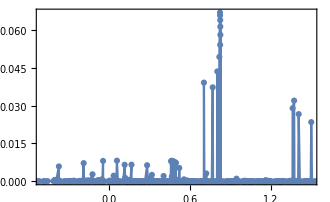

```mathematica
(* Work distribution starting from a thermal state at β = 0.5 *)
P=WorkDistribution[Hi,Hf,"thermal",0.5];
ListLinePlot[P,PlotMarkers->Automatic,PlotRange->{{-.5,1.5},All}]
```

```mathematica
(* First few moments *)
P⟦All,1⟧.P⟦All,2⟧
(P⟦All,1⟧^2).P⟦All,2⟧
(P⟦All,1⟧^3).P⟦All,2⟧
```

1.06874

2.20279

5.77457

```mathematica
(* Instead, the moments can be computed directly with the WorkMoments function, which is faster *)
y = MatrixExp[-0.5 Hi];
y = y/Tr[y];
WorkMoments[1,y,Hi,Hf]
WorkMoments[2,y,Hi,Hf]
WorkMoments[3,y,Hi,Hf]
```

1.06874

2.20279

5.77457

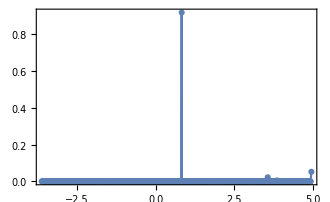

```mathematica
(* Starting from the GS. Last entry "0" is irrelevant *)
P=WorkDistribution[Hi,Hf,"GS",0];
ListLinePlot[P,PlotMarkers->Automatic(*,PlotRange->{{-.5,1.5},All}*)]
```

```mathematica
(* First few moments *)
P⟦All,1⟧.P⟦All,2⟧
(P⟦All,1⟧^2).P⟦All,2⟧
(P⟦All,1⟧^3).P⟦All,2⟧
```

1.11557

2.26513

8.16159

```mathematica
y = Eigvecs[Hi,1]//Flatten;
WorkMoments[1,y,Hi,Hf]
WorkMoments[2,y,Hi,Hf]
WorkMoments[3,y,Hi,Hf]
```

1.11557

2.26513

8.16159

#### Example: macrospin model with a finite unitary

```mathematica
LoadArbitrarySpinMatrices[S = 50];
Hi = Sz;
Hf = Sz;
U = MatrixExp[-ⅈ (Sz - 0.5 Sx) ];
P = WorkDistribution[Hi,Hf,"thermal",0.1,U]//Quiet;
```

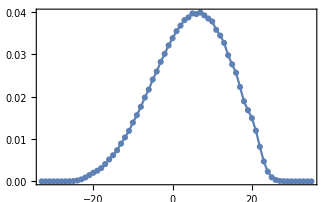

```mathematica
ListLinePlot[P,PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
WorkMoments[2,{"thermal",1},Hi,Hf,U]
```

42.2801

```mathematica
WorkMoments[2,{"GS"},Hi,Hf,U]
```

36.9552

```mathematica
ψ = GroundState[Hi];
WorkMoments[2,ψ,Hi,Hf,U]
```

36.9552-2.8581×10^-6 ⅈ

```mathematica
WorkMoments[2,{"eigenstate",2},Hi,Hf,U]
```

46.2138

#### Example: LMG model with a finite ramp

```mathematica
LoadArbitrarySpinMatrices[S=49/2];
𝒩 = 2S+1;
ℋ[h_]:=-2/𝒩 Sx.Sx-2 h Sz;
Hi= ℋ[hi=0.5];
Hf=ℋ[hf=1.5];
τ = 2.0;
(*U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.005,τ];*)
P1 = WorkDistribution[Hi,Hf,"GS",1]//Quiet;

Hf=ℋ[1.0];
P2 = WorkDistribution[Hi,Hf,"GS",1]//Quiet;

P1b = {#⟦1⟧+Egs,#⟦2⟧}&/@P1;
P2b = {#⟦1⟧+Egs,#⟦2⟧}&/@P2;
Egs=Eigvals[Hi,1]⟦1⟧;
```

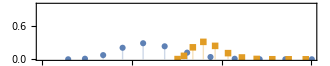

```mathematica
ListPlot[{P1b,P2b},PlotMarkers->Automatic,PlotRange->{{-80,-20},{0,1}},Filling->Axis,AspectRatio->1/5]
```

```mathematica
LoadArbitrarySpinMatrices[S=49/2];
𝒩 = 2S+1;
ℋ[h_]:=-2/𝒩 Sx.Sx-2 h Sz;
Hi= ℋ[hi=0.5];
Hf=ℋ[hf=1.5];
τ = 10.5;
PrettyTiming[U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.002,τ,"id","RK4"];]
P = WorkDistribution[Hi,Hf,"GS",1,U]//Quiet;

PrettyTiming[U = UnitaryDynamics[{-2/𝒩 Sx.Sx,-2 Sz},{Function[t,1],Function[t,hi+(hf-hi) t/τ]},0.1,τ,"id","Trotter"];]
P2 = WorkDistribution[Hi,Hf,"GS",1,U]//Quiet;
```

0h : 0m : 4s

0h : 0m : 0s

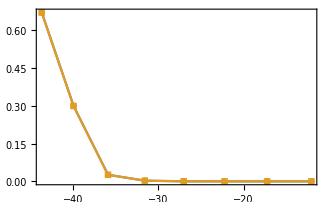

```mathematica
ListLinePlot[{P,P2},PlotMarkers->Automatic,PlotRange->All]
```

### Thermo-Majorization curve

```mathematica
(* Given probabilities and energies, yields the points (x,y) of a thermo-majorization curve *)
ThermoMajorizationCurve[pps_,Es_,β_]:=Module[{ord,x,y,ps},
ps = pps/Total[pps];
ord=Reverse@Ordering[ps Exp[β Es]];
y=Prepend[Accumulate[ps⟦ord⟧],0];
x = Prepend[Accumulate[Exp[-β Es]⟦ord⟧],0]//N;
Transpose[{x,y}]
]
```

#### Example usage

```mathematica
β = 1.0;
Es = {1.4,2,3.,2.5} (* energies *);
probs = {5,4,3,5} (* probs; don't have to be normalized *);
thermocurve = ThermoMajorizationCurve[probs,Es,β]
```

{{0.,0},{0.082085,5/17},{0.131872,8/17},{0.267207,12/17},{0.513804,1}}

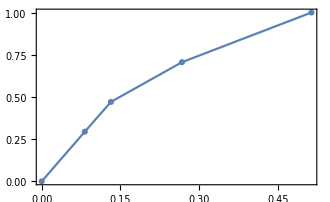

```mathematica
ListLinePlot[thermocurve,PlotMarkers->Automatic,PlotRange->All]
```

### Ergotropy

```mathematica
Ergotropy[H_,ρ_]:=Module[{P,ℰ,psiRho,psiH},
{P,psiRho}=Eigensystem[N@ρ];
{ℰ,psiH}=Eigensystem[1000 NEye[Length@H]-H];
ℰ = 1000 - ℰ;
Sum[P⟦i⟧ ℰ⟦j⟧(Abs[psiH⟦j⟧*.psiRho⟦i⟧]^2-KroneckerDelta[i,j]),{i,Length@ρ},{j,Length@H}]
]
```

## Metrology

QFI & SLD for Gaussian states can be found in the “Gaussian bosonic systems” section.

### Quantum Fisher Information

```mathematica
(* Determines if y = density matrix or if y = ket *)
(* For numerics use "eigen" *)
Clear[QuantumFisherInformation];
QuantumFisherInformation[y_,dy_]:=Module[{},
If[Length@Dimensions@y===2,
2Vec[dyᵀ].LinearSolve[kron[yᵀ,Eye[Length@y]]+kron[Eye[Length@y],y],Vec[dy]]//Chop,
4 (dy*.dy + (dy*.y)^2)//Chop
]
]

QuantumFisherInformation[ρ_,dρ_,"pseudo"]:=2Vec[dρᵀ].PseudoInverse[kron[ρᵀ,Eye[ρ]]+kron[Eye[ρ],ρ]].Vec[dρ]//Chop

QuantumFisherInformation[ρ_,dρ_,"eigen"]:=Module[{p,ψ,F},
{p,ψ} = Eigensystem[ρ];
(*Λ =2 Sum[If[p[[i]]+p[[j]]<10^-13,0,1/(p[[i]]+p[[j]])out[ψ[[i]],ψ[[i]]].dρ.out[ψ[[j]],ψ[[j]]]],{i,Length@ρ},{j,Length@ρ}]*)
F = 2 Sum[If[Re[p[[i]]+p[[j]]]<10^-13,0,1/(p[[i]]+p[[j]])Abs[ψ[[i]]*.dρ.ψ[[j]]]^2],{i,Length@ρ},{j,Length@ρ}]//Chop
]
```

```mathematica
SymmetricLogarithmicDerivative[ρ_,dρ_]:=Module[{n,A,b},
n = Length@ρ;
A = kron[ρᵀ,Eye[n]] + kron[Eye[n],ρ];
b = 2 Vec[dρ];
LinearSolve[A,b]//Unvec
]
```

#### Example usage

Quantum thermometry

```mathematica
Clear[ω,T,f];
ρ = ({{f, 0}, {0, 1-f}})/.f->1/(ⅇ^(ω/T)+1);
dρ = D[ρ,T];
QuantumFisherInformation[ρ,dρ]//Simplify
```

(ⅇ^(ω/T) ω^2)/((1+ⅇ^(ω/T))^2 T^4)

```mathematica
(* The SLD in this case is diagonal *)
SymmetricLogarithmicDerivative[ρ,dρ]//Simplify//mf;
```

((ⅇ^(ω/T) ω)/((1+ⅇ^(ω/T)) T^2) | 0
0 | -ω/((1+ⅇ^(ω/T)) T^2))

```mathematica
Clear[θ,ϕ,ψ];
ψ = 1/3 {θ,1}/(√2) + 2/3 {1,1}/(√2);
ψ = ψ/Norm[ψ]//cf;
dψ = D[ψ,θ];
F1=QuantumFisherInformation[ψ,dψ]//cf
```

36/(13+θ (4+θ))^2

```mathematica
(* Or, using density matrices *)
ρ = out[ψ,ψ]//cf;
dρ = D[ρ,θ]//cf;
F2=QuantumFisherInformation[ρ,dρ]//cf
```

36/(13+θ (4+θ))^2

```mathematica
QuantumFisherInformation[ρ,dρ,"pseudo"]//cf
```

36/(13+θ (4+θ))^2

```mathematica
QuantumFisherInformation[ρ/.θ->0.3,dρ/.θ->0.3,"pseudo"]
QuantumFisherInformation[ρ/.θ->0.3,dρ/.θ->0.3,"eigen"]
```

0.176294

0.176294

#### SLD: Explicit formula for a qubit

Symmetric logarithmic derivative:

```mathematica
ρ = ({{p, q}, {qs, 1-p}});
dρ = ({{dp, dq}, {dqs, -dp}});
```

```mathematica
Λ = ({{(-(-1+p) (dq* q + dq q*)+dp (-1+p + 2 q q*))/(-p+p^2+q q*), (q (dp-2 dp p-dq* q)+dq (-2 p+2 p^2+q q*))/(-p+p^2+q q*)}, {(q* (dp-2 dp p-dq q*)+dq* (-2 p+2 p^2+q q*))/(-p+p^2+q q*), (dp p+dq* p q+dq p q*-2 dp q q*)/(-p+p^2+q q*)}})
```

### Gammelmark-Mølmer Quantum Fisher information for continuous measurements

Based on https://link.aps.org/doi/10.1103/PhysRevLett.112.170401
(Eq. 21 of the Supplemental Material)

(This is the starting point for the Hasegawa bound https://link.aps.org/doi/10.1103/PhysRevLett.125.050601)

I focus here on the estimation of a single parameter for simplicity. 
Input: 
- Steady-state ρ
- Liouvillian ℒ 
- Hamiltonian H
- Derivative of H wrt to θ, H’
- List of jump operators {L_k}
- List of derivatives of the jump operators {L'_k}.

Note: formula only makes sense if ρ is the steady-state.

```mathematica
Clear[GammelmarkMolmerMFisher];
GammelmarkMolmerMFisher[ρ_,ℒ_, H_,Hp_,cops_,copsprime_]:=Module[{op1,𝕀,op2,ℒL,ℒR,ℒinv,outie},
op1 = -ⅈ Hp - 1/2 Sum[copsprime⟦k⟧†.cops⟦k⟧ + cops⟦k⟧†.copsprime⟦k⟧,{k,Length@cops}];
op2 = ⅈ Hp - 1/2 Sum[copsprime⟦k⟧†.cops⟦k⟧ + cops⟦k⟧†.copsprime⟦k⟧,{k,Length@cops}];
𝕀 = Eye[Length@H];
ℒL=kron[𝕀, op1] + Sum[kron[cops⟦k⟧*,copsprime⟦k⟧],{k,Length@cops}];
ℒR=kron[op2ᵀ,𝕀] + Sum[kron[copsprime⟦k⟧*,cops⟦k⟧],{k,Length@cops}];

(*outie = Eye[Length@ℒ]  - out[Vec[ρ], Vec[Eye[Length@ρ]]];
ℒinv = outie.PseudoInverse[ℒ].outie;
4Re@(Sum[Tr[c.ρ.c†],{c,copsprime}]- UnTr[ℒL.ℒinv.ℒR.Vec[ρ]]-UnTr[ℒR.ℒinv.ℒL.Vec[ρ]])*)
4Re@(Sum[Tr[c.ρ.c†],{c,copsprime}]- UnTr[ℒL.DrazinApply2[ℒ,Vec[ρ],ℒR.Vec[ρ]]]-UnTr[ℒR.DrazinApply2[ℒ,Vec[ρ],ℒL.Vec[ρ]]])
]
```

#### Example usage: non-resonant qubit

Reproducing Fig. 1 of the paper (1310.5802)

```mathematica
Clear[Δ,Ω,κ];
H = Δ/2 σz + Ω/2 σx;
cops = {√κ σm};
ℒ = Liouvillian[H,cops]//cf;
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(Ω^2/(4 Δ^2+κ^2+2 Ω^2) | -((2 Δ+ⅈ κ) Ω)/(4 Δ^2+κ^2+2 Ω^2)
(ⅈ (2 ⅈ Δ+κ) Ω)/(4 Δ^2+κ^2+2 Ω^2) | (4 Δ^2+κ^2+Ω^2)/(4 Δ^2+κ^2+2 Ω^2))

```mathematica
FΔ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,Δ],cops,Evaluate@D[cops,Δ]]//cf
FΩ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,Ω],cops,Evaluate@D[cops,Ω]]//cf
Fκ=GammelmarkMolmerMFisher[ρ,ℒ,H,Evaluate@D[H,κ],cops,Evaluate@D[cops,κ]]//cf
```

(8 (4 Δ^2+κ^2) Ω^2 (2 κ^2+Ω^2))/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

(4 (16 Δ^4 κ^2+8 Δ^2 κ^2 (κ-Ω) (κ+Ω)+(κ^2+2 Ω^2)^3))/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

Ω^2/(4 Δ^2 κ+κ^3+2 κ Ω^2)

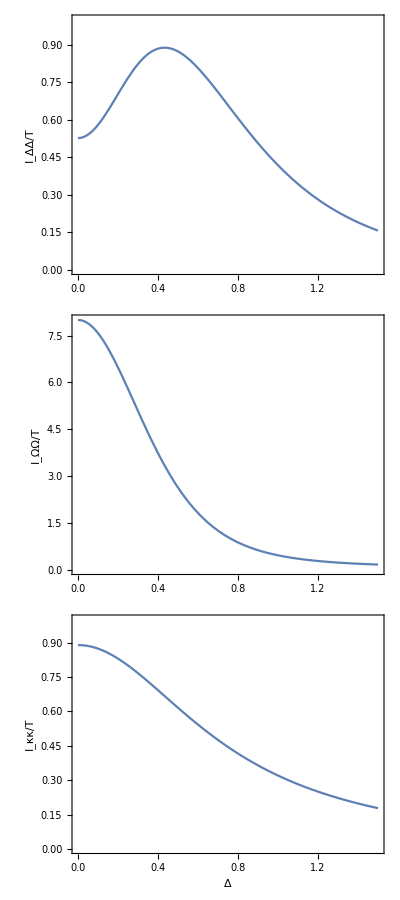

```mathematica
Grid[{{
Plot[FΔ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,1},FrameLabel->{None,"I_ΔΔ/T"}],
Plot[FΩ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,8},FrameLabel->{None,"I_ΩΩ/T"}],
Plot[Fκ/.{κ->1/2,Ω->1},{Δ,0,1.5},AspectRatio->1/3,PlotRange->{0,1},FrameLabel->{"Δ","I_κκ/T"}]}}ᵀ]
```

#### Kiilerich-Mølmer result: Fisher information from 2-point functions of a homodyne signal

Based on 1605.00902
The contribution of the sample mean to the Fisher information is 

ℐ^(1) = τ (∂_θ J)^2

The contribution from the two-point function is 

ℐ^(2) = τ ∫_0^∞ (dτ [∂_θ F(τ)])^2 = τ/(4π) ∫_(-∞)^∞ (dω [∂_θ S(ω)])^2

The actual Fisher information of the homodyne signal, ℐ^(hom) will be bounded by 

ℐ^Quantum ≥ ℐ^(hom) ≥ ℐ^(1)+ ℐ^(2)

Reproducing Fig. 3(b) of the paper (1605.00902)

```mathematica
Clear[Δ,Ω,κ];
H =  Ω/2 σx;
c = √κ σm;
ℒ = Liouvillian[H,{c}]//cf;
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(Ω^2/(κ^2+2 Ω^2) | -(ⅈ κ Ω)/(κ^2+2 Ω^2)
(ⅈ κ Ω)/(κ^2+2 Ω^2) | (κ^2+Ω^2)/(κ^2+2 Ω^2))

```mathematica
Clear[κ];
J = FCSAverage[ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]//cf
S = FCSPowerSpectrumLinearSys[{ω},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧//cf
G2 = FCSG2MEXP[{τ},ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Homodyne"]⟦1,2⟧//cf
F = G2 - J^2//cf
```

-(2 κ^(3/2) Ω)/(κ^2+2 Ω^2)

(κ^6+κ^4 (5 ω^2-2 Ω^2)+8 (-ω^2 Ω+Ω^3)^2+κ^2 (4 ω^4-6 ω^2 Ω^2+44 Ω^4))/((κ^2+2 Ω^2) (κ^4+4 (ω^2-Ω^2)^2+κ^2 (5 ω^2+4 Ω^2)))

1/((κ^2-16 Ω^2) (κ^2+2 Ω^2)^2)ⅇ^(-1/4 τ (3 κ+√(κ^2-16 Ω^2))) κ Ω^2 (4 ⅇ^(1/4 τ (3 κ+√(κ^2-16 Ω^2))) κ^2 (κ-4 Ω) (κ+4 Ω)+κ^3 √(κ^2-16 Ω^2)-ⅇ^(1/2 τ √(κ^2-16 Ω^2)) κ^3 √(κ^2-16 Ω^2)-10 κ Ω^2 √(κ^2-16 Ω^2)+10 ⅇ^(1/2 τ √(κ^2-16 Ω^2)) κ Ω^2 √(κ^2-16 Ω^2)-(1+ⅇ^(1/2 τ √(κ^2-16 Ω^2))) (κ^4-18 κ^2 Ω^2+32 Ω^4))

-(2 ⅇ^(-(3 κ τ)/4) κ Ω^2 ((κ^4-18 κ^2 Ω^2+32 Ω^4) Cosh[1/4 τ √(κ^2-16 Ω^2)]+κ √(κ^2-16 Ω^2) (κ^2-10 Ω^2) Sinh[1/4 τ √(κ^2-16 Ω^2)]))/((κ^2-16 Ω^2) (κ^2+2 Ω^2)^2)

```mathematica
ℐ1 = D[J,Ω]^2//cf
```

(4 κ^3 (κ^2-2 Ω^2)^2)/((κ^2+2 Ω^2)^4)

```mathematica
dF=D[F,Ω]//cf;
dS = D[S,Ω];
```

```mathematica
κ = 1;
ℐ2 = Table[{Ω,NIntegrate[dF^2,{τ,0,∞}]},{Ω,0.01,2,0.041}]//Quiet;
```

```mathematica
ℐ22 = Table[{Ω,1/(4π)NIntegrate[dS^2,{ω,-∞,∞}]},{Ω,0.01,2,0.041}]//Quiet;
```

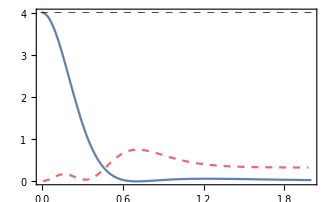

```mathematica
Show[
Plot[ℐ1,{Ω,0,2},PlotStyle->blue],
ListLinePlot[ℐ22,PlotStyle->Directive[red,Dashed]],
GridLines->{None,{4}},
GridLinesStyle->Directive[Black, Dashed]
]
```

```mathematica
int = dS^2//cf
```

(256 ((1+ω^2)^2 (1+4 ω^2) Ω-8 (1+5 ω^2+4 ω^4) Ω^3-4 (9+ω^2+4 ω^4) Ω^5-16 (1+ω^2) Ω^7+32 Ω^9)^2)/((1+2 Ω^2)^4 (4 ω^4+ω^2 (5-8 Ω^2)+(1+2 Ω^2)^2)^4)

```mathematica
int2=Integrate[int,{ω,0,∞},Assumptions->Ω>1]
```

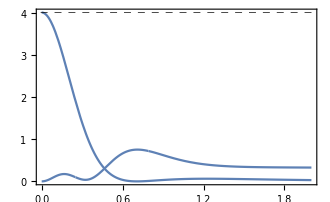

```mathematica
Show[
Plot[{ℐ1,1/(2π)Re@int2},{Ω,0,2},PlotStyle->blue],
GridLines->{None,{4}},
GridLinesStyle->Directive[Black, Dashed]
]
```

#### Example: Hasegawa steady-state TUR

Based on https://link.aps.org/doi/10.1103/PhysRevLett.125.050601

In this case H_θ = (1+θ) H and L_(k,θ) = √(1+θ)L_k
Hence 

∂_θ H = H   and   ∂_θ L_(k,θ) = 1/(2 √(1+θ))L_k= L_k/2 since  we want both evaluated in the limit θ → 0.

```mathematica
Clear[HasegawaSteadyStateTUR];
HasegawaSteadyStateTUR[ρ_,ℒ_,H_,cops_]:=GammelmarkMolmerMFisher[ρ,ℒ,H,H,cops,#/2&/@cops]
```

Example:

```mathematica
g = {1,0};
e = {0,1};
H = Δ out[e,e] + Ω/2(out[e,g] + out[g,e]);
L = √κ out[g,e];
ℒ = Liouvillian[H,{out[g,e]},{κ}];
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

(1-Ω^2/(4 Δ^2+κ^2+2 Ω^2) | (-2 Δ Ω+ⅈ κ Ω)/(4 Δ^2+κ^2+2 Ω^2)
-((2 Δ+ⅈ κ) Ω)/(4 Δ^2+κ^2+2 Ω^2) | Ω^2/(4 Δ^2+κ^2+2 Ω^2))

```mathematica
has=HasegawaTUR[ρ,ℒ,H,{L}]//cf
```

(κ^2 (4 Δ^2+κ^2)^2 Ω^2+4 (8 Δ^4+6 Δ^2 κ^2+3 κ^4) Ω^4+4 (16 Δ^2+9 κ^2) Ω^6+32 Ω^8)/(κ (4 Δ^2+κ^2+2 Ω^2)^3)

```mathematica
𝒟 = FCSDiffusionMatrix[ρ,ℒ,{L}]//cf
J=Tr[L†.L.ρ]//cf
```

(κ Ω^2 ((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4))/((4 Δ^2+κ^2+2 Ω^2)^3)

(κ Ω^2)/(4 Δ^2+κ^2+2 Ω^2)

```mathematica
𝒟
```

(κ Ω^2 ((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4))/((4 Δ^2+κ^2+2 Ω^2)^3)

```mathematica
𝒟/J^2//Simplify
```

((4 Δ^2+κ^2)^2-2 (-12 Δ^2+κ^2) Ω^2+4 Ω^4)/(κ Ω^2 (4 Δ^2+κ^2+2 Ω^2))

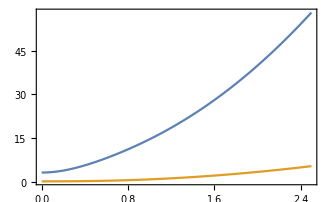

```mathematica
Plot[Evaluate[{𝒟/J^2,1/has}/.{Ω->1,κ->1/2}],{Δ,0,2.5}]
```

### Sequential Max-likelihood

Useful for visualization: max-likelihood estimator implemented sequentially, to show how adding more data improves the estimation procedure.

```mathematica
Clear[SequentialMaxLikelihood];
SequentialMaxLikelihood[loglike_,outcomes_,θgrid_,outputstep_:1]:=Module[{ll,posML,Lmax,θmax},
ll = Accumulate@Table[loglike[x,θ],{x,outcomes},{θ,θgrid}];
posML = First@Ordering[#,-1]&/@ll;
(*Lmax=Max/@ll;*)
θmax = θgrid⟦posML⟧;
θmax⟦1;;-1;;outputstep⟧
]
```

```mathematica
Clear[MeanSquaredError];
MeanSquaredError[θest_?MatrixQ,θreal_]:=Mean/@Transpose[(θest-θreal)^2]
MeanSquaredError[θest_?VectorQ,θreal_]:=MeanSquaredError[{θest},θreal]
```

#### Example usage

```mathematica
r = RandomVariate[ExponentialDistribution[1.5],10^4];
θs = linspace[0.01,3,1000];
```

```mathematica
(* Build the log-likelihood function *)
Log[PDF[ExponentialDistribution[θ],x]]
```

Log[Piecewise[{{ⅇ^(-x θ) θ, x≥0}, {0, True}}]]

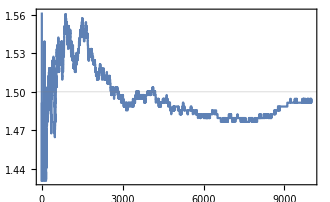

```mathematica
ListLinePlot[SequentialMaxLikelihood[Function[{x,θ},-x θ + Log[θ]],r,θs],GridLines->{None,{1.5}}]
```

A discrete distribution

```mathematica
r = RandomVariate[BinomialDistribution[10,0.5],50];
θs = linspace[0.001,0.999,1000];
```

```mathematica
Clear[p]
```

```mathematica
FullSimplify[Log[PDF[BinomialDistribution[10,p],x]],0<x<10]
```

Log[(1-p)^(10-x) p^x Binomial[10,x]]

{50,1000}

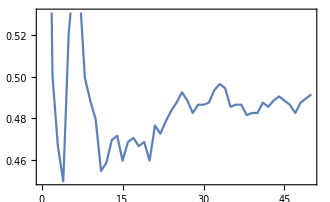

```mathematica
ListLinePlot[SequentialMaxLikelihood[Function[{x,p},Log[(1-p)^(10-x) p^x Binomial[10,x]]],r,θs],GridLines->{None,{1.5}}]
```

### Empirical Distribution

Based on https://arxiv.org/pdf/2305.16480.pdf

Input is a vector p of length(d) and a function 𝒞[x,y,k] [Eq. (23)] where x,y ∈ {1...d} and k = 1,2,... is an integer.
k = 1 it means a correlation between i and i+1
Output is the matrix (ℙ + Ψ.ℙ + ℙ.Ψᵀ)

```mathematica
Clear[EmpiricalDistributionFisherMatrix];
EmpiricalDistributionFisherMatrix[p_,𝒞_,Nmax_:100,L_:1]:=Module[{d = Length@p,ℙ,Ψ},
ℙ = DiagonalMatrix@p;
Ψ = Table[
Total@Table[(1-k/(Nmax+1-L))(𝒞[x,y,k]-p[[x]]),{k,1,Nmax-L}],{x,1,d},{y,1,d}
];
ℙ + Ψ.ℙ + ℙ.Ψᵀ
]
```

## Channels and gates

All channels and gates are applicable to act on states of L qubits.
- For instance, one may apply an Amplitude Damping channel to qubit 5, in an entangled state of 8 qubits. 
- Or one may apply a SWAP between qubits 3 and 6.

### Amplitude damping

γ ∈ [0,1] gives the strength of the interaction, with γ = 0 being the identity map and γ  = 1 being full thermalization

If γ = 1 the system will thermalize to (f | 0
0 | 1-f)

```mathematica
Clear[AmplitudeDampingKrausOperators];
AmplitudeDampingKrausOperators[f_,γ_]:=Module[{M},
M[0] = √f({{1, 0}, {0, √(1-γ)}});
M[1] = √f({{0, √γ}, {0, 0}});
M[2] = √(1-f)({{√(1-γ), 0}, {0, 1}});
M[3] = √(1-f)({{0, 0}, {√γ, 0}});
{M[0],M[1],M[2],M[3]}

]
```

```mathematica
Clear[AmplitudeDamping];
AmplitudeDamping[f_,γ_][ρ_]:=Module[{M = AmplitudeDampingKrausOperators[f,γ]},Total@Table[M⟦i⟧.ρ.M⟦i⟧ᵀ,{i,Length@M}]]

AmplitudeDamping[f_,γ_,qubit_][ρ_]:=Module[{M = AmplitudeDampingKrausOperators[f,γ]},
Total@Table[KronEye[M⟦i⟧,Log2[Length@ρ],qubit].ρ.KronEye[M⟦i⟧,Log2[Length@ρ],qubit]ᵀ,{i,Length@M}]

]
```

#### Example usage

AmplitudeDampingKrausOperators just gives a list of the 4 Kraus operators for the finite temperature amplitude damping:

```mathematica
mf/@AmplitudeDampingKrausOperators[f,γ];
```

(√f | 0
0 | √f √(1-γ))

(0 | √f √γ
0 | 0)

(√(1-f) √(1-γ) | 0
0 | √(1-f))

(0 | 0
√(1-f) √γ | 0)

To apply the map use AmplitudeDamping[f,γ][ρ]

```mathematica
ρ = ({{p, q}, {qs, 1-p}});
```

```mathematica
AmplitudeDamping[f,1][ρ]//Simplify//mf;
```

(f | 0
0 | 1-f)

```mathematica
AmplitudeDamping[1,γ][ρ]//Simplify//mf;
```

(p+γ-p γ | q √(1-γ)
qs √(1-γ) | (-1+p) (-1+γ))

```mathematica
AmplitudeDamping[0,γ][ρ]//Simplify//mf;
```

(p-p γ | q √(1-γ)
qs √(1-γ) | 1+p (-1+γ))

```mathematica
nn = 1/(ⅇ^x-1);
nn/(2nn+1)//Simplify
```

1/(1+ⅇ^x)

You can also enter a density matrix living in a higher dimensional Hilbert space and apply the map only in one qubit. 
To do that, use AmplitudeDamping[f, γ, i][ρ] where i is the position of the qubit you wish to apply.

```mathematica
ρAB = kron[({{p, q}, {qs, 1-p}}),({{1, 0}, {0, 0}})];
```

This will apply the map on qubit 1

```mathematica
ρABprime=AmplitudeDamping[f,γ,1][ρAB]//Simplify//mf;
```

(p+f γ-p γ | 0 | q √(1-γ) | 0
0 | 0 | 0 | 0
qs √(1-γ) | 0 | 1+p (-1+γ)-f γ | 0
0 | 0 | 0 | 0)

One can check that indeed only qubit 1 was affected

```mathematica
PTr[ρABprime,{2}]//Simplify//mf;
PTr[ρABprime,{1}]//Simplify//mf;
```

(p+f γ-p γ | q √(1-γ)
qs √(1-γ) | 1+p (-1+γ)-f γ)

(1 | 0
0 | 0)

Similarly, we can apply it in 2

```mathematica
ρABprime2=AmplitudeDamping[f,γ,2][ρAB]//Simplify//mf;
```

(p+(-1+f) p γ | 0 | q+(-1+f) q γ | 0
0 | -(-1+f) p γ | 0 | -(-1+f) q γ
qs+(-1+f) qs γ | 0 | -(-1+p) (1+(-1+f) γ) | 0
0 | -(-1+f) qs γ | 0 | (-1+f) (-1+p) γ)

Now the reduced density matrices become:

```mathematica
PTr[ρABprime2,{2}]//Simplify//mf;
PTr[ρABprime2,{1}]//Simplify//mf;
```

(p | q
qs | 1-p)

(1+(-1+f) γ | 0
0 | γ-f γ)

#### Amplitude damping, Lindblad equation and collision model - relation between the parameters

```mathematica
MatrixForm/@AmplitudeDampingKrausOperators[f,λ]
```

{(√f | 0
0 | √f √(1-λ)),(0 | √f √λ
0 | 0),(√(1-f) √(1-λ) | 0
0 | √(1-f)),(0 | 0
√(1-f) √λ | 0)}

Compare to a master equation

```mathematica
ρ = ({{p, q}, {qs, 1-p}});
AmplitudeDamping[f,λ][ρ]//Simplify//mf;
```

(p+f λ-p λ | q √(1-λ)
qs √(1-λ) | 1+p (-1+λ)-f λ)

q → √(1-λ)q
p → (1-λ) p + f λ

```mathematica
ℒ = Liouvillian[0 σz,{σm,σp},{γ (n+1),γ n}];
ρt = MatrixExp[ℒ t,Vec[ρ]]//Unvec//Simplify//mf;
```

((ⅇ^(-((1+2 n) t γ)) (p+n (-1+ⅇ^((1+2 n) t γ)+2 p)))/(1+2 n) | ⅇ^(-1/2 t (γ+2 n γ)) q
ⅇ^(-1/2 t (γ+2 n γ)) qs | (ⅇ^(-((1+2 n) t γ)) (n+ⅇ^((1+2 n) t γ) (1+n)-p-2 n p))/(1+2 n))

λ=1- e^(-γ(2n+1)t)

```mathematica
LoadSpinChainMatrices[2,"a"];
U = MatrixExp[-ⅈ g (sp[1].sm[2]+sm[1].sp[2])]//cf//mf;
```

```mathematica
CollisionMap[ρ,U,({{f, 0}, {0, 1-f}}),1]⟦2⟧//cf//mf;
```

(1/2 (f+p+(-f+p) Cos[2 g]) | q Cos[g]
qs Cos[g] | 1/2 (2-f-p+(f-p) Cos[2 g]))

√(1-λ)= cos(g)
λ = sin^2(g)

### SWAP and partial SWAP

SWAPs qubits a and b in a system with L qubits.
Default is for two qubits, and can be called as SWAP[]

```mathematica
Clear[SWAP]
SWAP[a_,b_,L_]:=Module[{𝕀,σx,σy,σz},

𝕀 = Eye[2^L];
σx = {{0,1},{1,0}};
σy = {{0,-ⅈ},{ⅈ,0}};
σz = {{1,0},{0,-1}};

1/2(𝕀 + KronEye[σx,L,a].KronEye[σx,L,b]+ KronEye[σy,L,a].KronEye[σy,L,b]+ KronEye[σz,L,a].KronEye[σz,L,b])
]

SWAP[]:=SWAP[1,2,2];

SWAP[a_,b_,L_,η_]:=Cos[η] Eye[2^L] + ⅈ Sin[η] SWAP[a,b,L]
```

Alternative definitions of the partial swap with s ∈ [0,1]. 
s = 1 is full swap

```mathematica
Clear[PartialSWAP]
PartialSWAP[s_,a_,b_,L_]:=( -ⅈ √(1-s^2) Eye[2^L] +s SWAP[a,b,L])
PartialSWAP[s_] := PartialSWAP[s,1,2,2]
```

A variation of the partial SWAP in which the operator is real.

```mathematica
Clear[RealPartialSWAP];
RealPartialSWAP[s_,a_,b_,L_]:=Module[{𝒳,σp,σm},
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};
𝒳 = KronEye[σp,L,a].KronEye[σm,L,b]-KronEye[σm,L,a].KronEye[σp,L,b];
Eye[2^L] + s 𝒳 +(1-√(1-s^2))𝒳.𝒳
]
RealPartialSWAP[s_]:=RealPartialSWAP[s,1,2,2]
```

#### Example usage

```mathematica
(* SWAP 1 and 2 in a system with 2 qubits *)
SWAP[]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* This is equivalent to *)
SWAP[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* SWAP 1 and 2 in a system with 3 qubits *)
SWAP[1,2,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* SWAP 1 and 3 in a system with 3 qubits *)
SWAP[1,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Qubit 1 prepared in ψ. Qubits 2 and 3 prepared in |0> *)
ψ = {Cos[θ/2],Sin[θ/2]};
Ψ = kronV[ψ,{1,0},{1,0}]//mf;
```

(Cos[θ/2]
0
0
0
Sin[θ/2]
0
0
0)

```mathematica
Ψprime = SWAP[1,3,3].Ψ//mf;
```

(Cos[θ/2]
Sin[θ/2]
0
0
0
0
0
0)

```mathematica
(* Trace over 2 and 3, we get |0> for qubit 1 and ψ for qubit 3*)
PTr[out[Ψprime,Ψprime],{2,3}]//cf//mf;
PTr[out[Ψprime,Ψprime],{1,3}]//cf//mf;
PTr[out[Ψprime,Ψprime],{1,2}]//cf//mf;
```

(1 | 0
0 | 0)

(1 | 0
0 | 0)

(Cos[θ/2]^2 | Sin[θ]/2
Sin[θ]/2 | Sin[θ/2]^2)

```mathematica
PartialSWAP[s,1,2,3]//mf;
```

(s-ⅈ √(1-s^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | s-ⅈ √(1-s^2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ √(1-s^2) | 0 | s | 0 | 0 | 0
0 | 0 | 0 | -ⅈ √(1-s^2) | 0 | s | 0 | 0
0 | 0 | s | 0 | -ⅈ √(1-s^2) | 0 | 0 | 0
0 | 0 | 0 | s | 0 | -ⅈ √(1-s^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | s-ⅈ √(1-s^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | s-ⅈ √(1-s^2))

```mathematica
PartialSWAP[s,1,2,3].Ψ//mf;
```

((s-ⅈ √(1-s^2)) Cos[θ/2]
0
s Sin[θ/2]
0
-ⅈ √(1-s^2) Sin[θ/2]
0
0
0)

### CNOT

CNOT between control qubit a and target qubit b in a system with L qubits.

```mathematica
Clear[CNOT]
CNOT[a_,b_,L_]:=Module[{σ0,σx,σp,σm},

σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};

(* Partial SWAP *)
KronEye[σp.σm,L,a].KronEye[σ0,L,b]+ KronEye[σm.σp,L,a].KronEye[σx,L,b]
]

(*CNOT[] := Normal@CNOT[1,2,2];*)
CNOT[]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});

CNOT::usage = "CNOT[] calls the standard 4x4 CNOT gate. 

CNOT[a,b,L] loads a CNOT gate in a space of L qubits, with a (=1,...,L) being the control qubit and b (=1,...,L) the target qubit. 

CNOT[1,2,2] is equivalent to CNOT[].";
```

#### Example usage

```mathematica
CNOT[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
(* One can construct the Bell basis by applying a Hadamard followed by a CNOT *)
H = kron[1/(√2)({{1, 1}, {1, -1}}),Eye[2]];
v0 = {1,0};
v1 = {0,1};
CNOT[1,2,2].H.kronV[v0,v0]
CNOT[1,2,2].H.kronV[v0,v1]
CNOT[1,2,2].H.kronV[v1,v0]
CNOT[1,2,2].H.kronV[v1,v1]
```

{1/(√2),0,0,1/(√2)}

{0,1/(√2),1/(√2),0}

{1/(√2),0,0,-1/(√2)}

{0,1/(√2),-1/(√2),0}

Two CNOTs

```mathematica
CNOT[1,2,2].CNOT[2,1,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

Three CNOTs become a SWAP

```mathematica
CNOT[1,2,2].CNOT[2,1,2].CNOT[1,2,2]//mf;
SWAP[1,2,2]//mf;
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

CNOT applied between 1 and 3 in a 3-qubit system

```mathematica
CNOT[1,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

### Hadamard & Toffoli gate

```mathematica
Clear[Hadamard]
Hadamard[]:=1/(√2)({{1, 1}, {1, -1}});
Hadamard[i_,𝒩_]:=kron[Eye[2^(i-1)],({{1/(√2), 1/(√2)}, {1/(√2), -1/(√2)}}),Eye[2^(𝒩-i)]]
Hadamard::usage = "Hadamard[] calls the 2x2 Hadamard matrix. 

Hadamard[i,𝒩] is a Hadamard gate on qubit i, in a space of 𝒩 qubits";
```

```mathematica
Clear[Toffoli]
Toffoli[a_,b_,c_,L_]:=Module[{σ0,σx,σp,σm},

σ0 = {{1,0},{0,1}};
σx = {{0,1},{1,0}};
σp = {{0,1},{0,0}};
σm = {{0,0},{1,0}};

(* Partial SWAP *)
KronEye[σp.σm,L,a].KronEye[σm.σp,L,b].KronEye[σ0,L,c]+KronEye[σm.σp,L,a].KronEye[σp.σm,L,b].KronEye[σ0,L,c]+KronEye[σp.σm,L,a].KronEye[σp.σm,L,b].KronEye[σ0,L,c]+ KronEye[σm.σp,L,a].KronEye[σm.σp,L,b].KronEye[σx,L,c]
]
```

#### Example usage

```mathematica
tmp=Toffoli[1,2,3,3]//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
tmp†.tmp//mf;
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Toffoli[2,3,1,3]-Toffoli[3,2,1,3]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Full dephasing map

```mathematica
(* Dephases A in the eigenbasis of X *)
Clear[FullDephasingMap]
FullDephasingMap[A_,X_,degeneracy_:False]:=Module[{λ,v,kd},

{λ,v}=Eigsys[X];
v=vᵀ;
kd[a_,b_,tol_:10^-10] := If[Abs[a-b]<tol,1,0];
If[degeneracy===False,
Total@Table[(v⟦i⟧*.A.v⟦i⟧) out[v⟦i⟧,v⟦i⟧],{i,Length@v}],
Total@Flatten[Table[(v⟦i⟧*.A.v⟦j⟧) out[v⟦i⟧,v⟦j⟧] kd[λ⟦i⟧,λ⟦j⟧],{i,Length@λ},{j,Length@λ}],1]]
]
```

#### Example usage

```mathematica
LoadArbitrarySpinMatrices[1];
ρ = MatrixExp[Sz+Sx];
ρ = ρ/Tr[ρ]//mf;
```

(0.607116 | 0.2584 | 0.0549899
0.2584 | 0.296673 | 0.102865
0.0549899 | 0.102865 | 0.0962105)

```mathematica
(* Dephase in the eigenbasis of Sz *)
FullDephasingMap[ρ,Sz]//mf;
```

(0.607116 | 0 | 0
0 | 0.296673 | 0
0 | 0 | 0.0962105)

```mathematica
(* Dephasing in the full eigenbasis of Sx *)
FullDephasingMap[ρ,Sx]//mf;
```

(0.324168 | 0.180632 | 0.0274949
0.180632 | 0.351663 | 0.180632
0.0274949 | 0.180632 | 0.324168)

```mathematica
(* Dephasing in the full eigenbasis of Sz^2 *)
(* Since Sz^2 is degenerate, one can choose to dephase with or without taking degeneracies into account *)
(* Default is without degeneracies *)
FullDephasingMap[ρ,Sz.Sz]//mf;
```

(0.607116 | 0 | 0
0 | 0.296673 | 0
0 | 0 | 0.0962105)

```mathematica
(* With degeneracies, the map keeps the coherences between degenerate subspaces *)
FullDephasingMap[ρ,Sz.Sz,True]//mf;
```

(0.607116 | 0 | 0.0549899
0 | 0.296673 | 0
0.0549899 | 0 | 0.0962105)

## Open quantum systems

## Vectorization-based routines

### Vectorization

```mathematica
(* Not vectorized *)
Clear[LindbladDissipator]
LindbladDissipator[A_,ρ_]:=A.ρ.A†-1/2(A†.A.ρ+ρ.A†.A);
LindbladDissipator[A_,B_,ρ_]:=A.ρ.B-1/2(B.A.ρ+ρ.B.A);
```

```mathematica
Clear[AdjointDissipator];
AdjointDissipator[𝒪_,L_]:=L†.𝒪.L-1/2(L†.L.𝒪+𝒪.L†.L)
AdjointDissipator[𝒪_,Ls_,γs_]:=Sum[γs[[i]] AdjointDissipator[𝒪,Ls[[i]]],{i,Length@Ls}]
```

```mathematica
Vec[X_]:=Flatten[Xᵀ];
Unvec[x_]:=With[{d = √(Length@x)},Partition[x,d]ᵀ];
UnTr[X_]:=Tr@Unvec@X
```

```mathematica
Clear[UnitaryToVec,LindbladToVec,AdjointToVec];

UnitaryToVec[H_]:=With[{ℐ = Eye[Length@H]},-ⅈ (kron[ℐ,H]- kron[Hᵀ,ℐ])]

LindbladToVec[L_]:=With[{ℐ = Eye[Length@L]},kron[Conjugate[L],L]-1/2 kron[(L†.L)ᵀ,ℐ]-1/2 kron[ℐ,L†.L]]

AdjointToVec[L_]:=With[{ℐ=Eye[Length[L]]},kron[Lᵀ,L†]-1/2 kron[Transpose[ConjugateTranspose[L].L],ℐ]-1/2 kron[ℐ,ConjugateTranspose[L].L]]
```

```mathematica
Clear[Liouvillian];
Liouvillian[H_,cops_]:=Module[{c},
If[Length[H]!=Length[cops⟦1⟧],0,UnitaryToVec[H]]+ 
If[Length@Dimensions@cops===3,
Sum[LindbladToVec[c],{c,cops}],
LindbladToVec[cops]
]]

Liouvillian[H_,cops_,rates_]:=Module[{c},
If[Length[H]!=Length[cops⟦1⟧],0,
UnitaryToVec[H]] +
If[Length@Dimensions@cops===3,
Sum[rates⟦i⟧ LindbladToVec[cops⟦i⟧],{i,Length@cops}],
rates LindbladToVec[cops]
]
 ]
```

```mathematica
Clear[EffectiveNonHermitianHamiltonian];
EffectiveNonHermitianHamiltonian[H_,cops_]:=Module[{c},
H -ⅈ/2 Sum[c†.c,{c,cops}]]

EffectiveNonHermitianHamiltonian[H_,cops_,rates_]:=Module[{c},
H -ⅈ/2 Sum[rates⟦i⟧ cops⟦i⟧†.cops⟦i⟧,{i,Length@cops}]]
```

### Steady-states of a master equation

```mathematica
(* Only meant for numerics *)
Clear[SteadyState];
SteadyState[A_]:=Module[{ρ,x,numeric},

numeric= AllTrue[Flatten@Normal@A,NumberQ];
If[numeric===False, AnalyticalSteadyState[A],
(x=SparseArray@First@Eigenvectors[A,-1];
ρ = Unvec[x] ;
ρ = (ρ+ρ†);
ρ = ρ/Tr[ρ]//Chop
)]
];

SteadyState[A_,𝕀_]:=AnalyticalSteadyState[A,𝕀]
```

```mathematica
Clear[AnalyticalSteadyState];
AnalyticalSteadyState[ℒ_]:=Module[{ℒ2,d,ρ},
d = Length@ℒ;
(*ℒ2 = Join[ℒ,{ConstantArray[1,d]}];*)
ℒ2 = Normal@Join[ℒ,{Vec@Eye[√d]}];
ρ = Unvec@LinearSolve[ℒ2,Eye[d+1]⟦-1⟧];
ρ
]

(* Specify the vectorized identity matrix 𝕀. Output in this case is not unvectorized. *)
AnalyticalSteadyState[ℒ_,𝕀𝕀_]:=Module[{ℒ2,d,𝕀},
d = Length@ℒ;
𝕀= If[Head[𝕀𝕀]===String,ConstantArray[1,{d}],𝕀𝕀];
ℒ2 = Normal@Join[ℒ,Normal@{𝕀}];
LinearSolve[ℒ2,Eye[d+1]⟦-1⟧]
]
```

```mathematica
(* Kind of buggy: use with care *)
Clear[AnalyticalSteadyStateSequential]
AnalyticalSteadyStateSequential[ℒ_]:=Module[{B,nn,x,i,p,ph,phh,ρ,tr},
Clear[B];
B = Normal@ℒ;
nn=Length@ℒ;
Do[
Do[
B⟦i⟧ = Together[B⟦i⟧-B⟦j⟧B⟦i,j⟧/B⟦j,j⟧]
,{i,j+1,nn}];
PrintTemporary[j];
(*Print[Normal@B⟦j+1⟧];*)
,{j,1,nn}];
x=ConstantArray[0,nn];
x⟦nn⟧=1;
Do[
x⟦i⟧=-Together@Total@Table[B⟦i,j⟧x⟦j⟧,{j,i+1,nn}]/B⟦i,i⟧;
(*Print[x⟦i⟧];*)
PrintTemporary[i]
,{i,nn-1,1,-1}];

Do[x⟦i⟧ = Simplify[x⟦i⟧];PrintTemporary[i];PrintTemporary[x⟦i⟧];,{i,Length@x}];
p = Unvec[x];
ph = ConstantArray[0,{Length@p,Length@p}];
phh = p†;
Do[
ph⟦i,j⟧=cf[phh⟦i,j⟧];
PrintTemporary[{i,j}];
PrintTemporary[ph⟦i,j⟧];
,{i,Length@p},{j,Length@p}];
ρ = p + ph;
tr = Tr[ρ]//Simplify;
ρ = ρ/tr;
Simplify@ρ
]
```

#### Crash course on vectorization

"Vec" means stacking columns

vec(a | b
c | d) = (a
c
b
d);

The fundamental identity from vectorization is 

vec(AρB ) = (Bᵀ⊗ A) vec(ρ)

This allows us to convert Lindblad equations into vector equations. 
For instance

Hρ = (𝕀 ⊗ H)vec(ρ)
ρH = (Hᵀ ⊗ 𝕀) vec(ρ)

∴   -i[H,ρ] = -i(𝕀 ⊗ H - Hᵀ ⊗ 𝕀)vec(ρ)

(This is what UnitaryToVec does)

Similarly:

vec(LρL^†-1/2{L†L,ρ}) = (L*⊗L - 1/2 𝕀 ⊗ L†L - 1/2 L†L ⊗ 𝕀) vec(ρ)

(This is what LindbladToVec does)

#### Example usage

```mathematica
ρ = ({{p, q}, {q*, 1-p}});
```

```mathematica
Vec[ρ]//mf;
```

(p
Conjugate[q]
q
1-p)

```mathematica
Unvec@Vec[ρ]//mf;
```

(p | q
Conjugate[q] | 1-p)

```mathematica
LoadPauliMatrices[]
```

```mathematica
H= Ω/2 σz;
𝒟 = γ (1-f) LindbladToVec[σm]+γ f LindbladToVec[σp];
Liouvillian = UnitaryToVec[H] + 𝒟//mf;
```

(-(1-f) γ | 0 | 0 | f γ
0 | -1/2 (1-f) γ-(f γ)/2+ⅈ Ω | 0 | 0
0 | 0 | -1/2 (1-f) γ-(f γ)/2-ⅈ Ω | 0
(1-f) γ | 0 | 0 | -f γ)

```mathematica
(* Steady-state should be a thermal state *)
ρth = ({{f, 0}, {0, 1-f}});
Liouvillian.Vec[ρth]//cf//mf;
```

(0
0
0
0)

```mathematica
(* Or we can check this without vectorization *)
γ (1-f) Lindbladian[σm][ρth] + γ f Lindbladian[σp][ρth]//cf//mf;
```

(0 | 0
0 | 0)

```mathematica
Clear[γ,Ω,f];
H= Ω/2 σx;
𝒟 = γ (1-f) LindbladToVec[σm]+γ f LindbladToVec[σp];
ℒ = UnitaryToVec[H] + 𝒟//mf;
```

(-((1-f) γ) | -(ⅈ Ω)/2 | (ⅈ Ω)/2 | f γ
-(ⅈ Ω)/2 | -1/2 (1-f) γ-(f γ)/2 | 0 | (ⅈ Ω)/2
(ⅈ Ω)/2 | 0 | -1/2 (1-f) γ-(f γ)/2 | -(ⅈ Ω)/2
(1-f) γ | (ⅈ Ω)/2 | -(ⅈ Ω)/2 | -f γ)

```mathematica
AnalyticalSteadyState[ℒ]
```

{{(f γ^2+Ω^2)/(γ^2+2 Ω^2),(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2)},{-(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2),(γ^2-f γ^2+Ω^2)/(γ^2+2 Ω^2)}}

```mathematica
AnalyticalSteadyState2[ℒ]
```

{{(f γ^2+Ω^2)/(γ^2+2 Ω^2),(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2)},{-(ⅈ (-1+2 f) γ Ω)/(γ^2+2 Ω^2),(γ^2-f γ^2+Ω^2)/(γ^2+2 Ω^2)}}

{0.008868,Null}

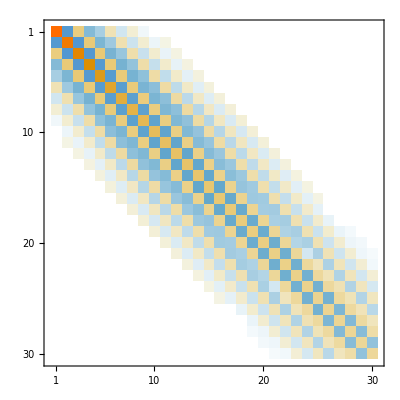

```mathematica
LoadBosonicOperators[nmax = 30];
ϵ = 0.8;
γ = 1.0;
nb = 3.0;
H = a†.a +ϵ (a + a†);
𝒟 = γ(nb+1)LindbladToVec[a] + γ nb LindbladToVec[a†];
ℒ = UnitaryToVec[H] + 𝒟;
AbsoluteTiming[(ρ = SteadyState[ℒ])//Chop;]
ρ//MatrixPlot
```

{0.187309,Null}

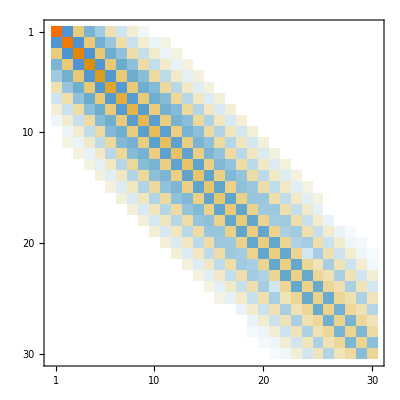

```mathematica
AbsoluteTiming[ρ2 = AnalyticalSteadyState2[ℒ]//Chop;]
ρ2//MatrixPlot
```

```mathematica
Tr[ρ]
```

1.

```mathematica
Tr[ρ2]
```

1.

```mathematica
ρ-ρ2//ChopCheck
```

{0}

```mathematica
(* Analytical Steady steate of an XXZ chain with 4 spins *)
LoadSpinChainMatrices[L=4,"a"] (* "a" makes the operators suitable for analytical calculations *) 
H = Sum[sx[i].sx[i+1] + sy[i].sy[i+1] + Δ sz[i].sz[i+1],{i,1,L-1}] + Sum[h sz[i],{i,1,L}];
ℒ = UnitaryToVec[H] + γ LindbladToVec[sp[1]] + γ LindbladToVec[sm[L]];
```

```mathematica
ρ = AnalyticalSteadyState[ℒ]
```

$Aborted

### Waiting time distributions (WTDs)

Waiting Time Distribution
Computes the general waiting time distribution between an initial jump 𝒥_i and a final jump 𝒥_f, with no jump Liouvillian ℒ_0

P_(f|i)(t) = (tr (𝒥_f e^(ℒ_0 t)𝒥_i ρ))/(tr(𝒥_i ρ))

The jump operators usually have the form 𝒥_k= L_k ρ L_k^†.
If no initial state ρ is input, it is assumed that ρ  = identity (maximally mixed state). This is convenient in the case of renewal processes, where ρ does not matter. 

For a Liouvillian decomposed as ℒ = ℒ_0 + ∑_k 𝒥_k, the WTD will be normalized as 

∑_f ∫ dt P_(f|i)(t) = 1 - P_no(∞), 

where P_no(∞) = lim_(t→ ∞) tr(e^(ℒ_0 t)ρ) is the no jump distribution. 
If after an infinite time, a jump definitely occurs, then P_no(∞)=0 and one gets the usual normalization. 

Moments of the waiting time
The moments are only implement for the case where the Liouvillian is split as ℒ = ℒ_0+ℒ_1 and the WTD is 

 P(t)=(tr (ℒ_1 e^(ℒ_0 t)ℒ_1 ρ))/(tr(ℒ_1 ρ))
 
The moments then read 

E(T^n) = ∫ dt P(t) t^n. 

For the general WTDs implemented above, it becomes a bit awkward to speak of moments since the distribution is not necessarily normalized. 
It also assumes that ℒ_0 has no zero eigenvalues (which means a jump must eventually occur). 

Implementation: 
Assuming that ℒ_0 has no dark subspaces, we get 

∫_0^∞ dt e^(ℒ_0 t)t^n = (-1)^(n+1)n! ℒ_0^(-(n+1))

Thus 

E(T^n) = (-1)^(n+1)n! (tr(ℒ_1 ℒ_0^(-(n+1))ℒ_1 ρ))/(tr(ℒ_1 ρ)).

But since ℒ_1=ℒ-ℒ_0 and ℒ is traceless, we can also write this as 

E(T^n) = (-1)^n n!  (tr(ℒ_0^-n ℒ_1 ρ))/(tr(ℒ_1 ρ))

The first moment, for instance, reads 

E(T) = -(tr(ℒ_0^-1 ℒ_1 ρ))/(tr(ℒ_1 ρ))

```mathematica
Clear[WaitingTimeDistribution];
WaitingTimeDistribution[t_,ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Module[{ρ,d=√(Length@ℒ0)},
ρ=If[ρ0===None,Eye[d]/d,ρ0];
UnTr[𝒥f.MatrixExp[ℒ0 t,𝒥i.Vec[ρ]]]/UnTr[𝒥i.Vec[ρ]]//Chop
]
  
WaitingTimeDistribution[ts_?ArrayQ, ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Table[WaitingTimeDistribution[t,ℒ0,𝒥i,𝒥f,ρ0],{t,ts}]
```

```mathematica
Clear[WaitingTimeDistributionClassical]
WaitingTimeDistributionClassical[t_,ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Module[{ρ,d=Length@ℒ0},
ρ=If[ρ0===None,ConstantArray[1,d]/d,ρ0];
Total[𝒥f.MatrixExp[ℒ0 t,𝒥i.ρ]]/Total[𝒥i.ρ]]      

WaitingTimeDistributionClassical[ts_?ArrayQ, ℒ0_,𝒥i_,𝒥f_,ρ0_:None]:=Table[WaitingTimeDistributionClassical[t,ℒ0,𝒥i,𝒥f,ρ0],{t,ts}]
```

```mathematica
Clear[WaitingTimeMoments];
WaitingTimeMoments[ρ_?MatrixQ,ℒ_,ℒ1_,n_,reset_:True]:=Module[{f,α,ρ0},
f = LinearSolve[ℒ-ℒ1];
ρ0 = If[reset==True,(ℒ1.Vec[ρ])/UnTr[ℒ1.Vec[ρ]],Vec[ρ]];
α = Nest[f,ρ0,n];
(-1)^n n! UnTr[α]  
];

WaitingTimeMoments[ρ_?VectorQ,ℒ_,ℒ1_,n_,reset_:True]:=Module[{f,α,ρ0},
f = LinearSolve[ℒ-ℒ1];
ρ0 = If[reset==True,(ℒ1.ρ)/Total[ℒ1.ρ],ρ];
α = Nest[f,ρ0,n];
(-1)^n n! Total[α]  
]
```

#### Waiting time distribution for resonance fluorescence

Eq. (30) of Carmichael 1989
 https://journals.aps.org/pra/abstract/10.1103/PhysRevA.39.1200

```mathematica
ℒ = Liouvillian[Ω/2 σx,{σm},{γ}];
𝒥 = γ JumpOp[σm];
ℒ0 = ℒ-𝒥;
P = cf[WaitingTimeDistribution[t,ℒ0,𝒥,𝒥]]/.γ->2β//Simplify
```

(2 ⅇ^(-t β) β Ω^2 Sinh[1/2 t √(β^2-Ω^2)]^2)/(β^2-Ω^2)

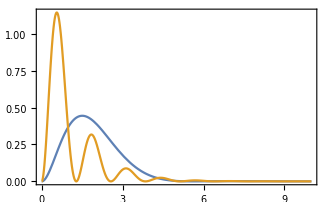

```mathematica
Plot[Evaluate@Table[P/.β->1,{Ω,{1.5,5.}}],{t,0,10}]
```

```mathematica
(* Average waiting time *)
WaitingTimeMoments[ρ,ℒ,𝒥,1]//cf
```

2/γ+γ/Ω^2

```mathematica
(* Variance of the waiting time *)
WaitingTimeMoments[ρ,ℒ,𝒥,2]-WaitingTimeMoments[ρ,ℒ,𝒥,1]^2//cf
```

4/γ^2+γ^2/Ω^4-2/Ω^2

#### Quantum model with multiple jumps

```mathematica
(* A quantum model with 3 jump operators, but only two of them being monitored *)
H = σz + σx;
cdn = √(1/2)σm; (* emission *)
cup = √(1/3)σp;  (* absorption *)
cdeph = √(1/10)σz ;(* dephasing *)
ℒ = Liouvillian[H,{cdn,cup,cdeph}];
Jdn = JumpOp[cdn];
Jup = JumpOp[cup];
ℒ0 = ℒ-Jdn-Jup;
```

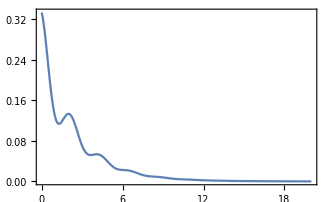

```mathematica
(* Waiting time distribution between an emission & an absorption *)
Pea=WaitingTimeDistribution[t,ℒ0,Jdn,Jup];
Plot[Pea,{t,0,20}]
```

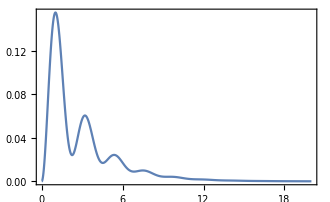

```mathematica
(* Waiting time distribution between two emissions (assuming that we still monitor the absorptions) *)
Pee=WaitingTimeDistribution[t,ℒ0,Jdn,Jdn];
Plot[Pee,{t,0,20}]
```

```mathematica
(* Normalization *)
NIntegrate[Pea,{t,0,∞}]+NIntegrate[Pee,{t,0,∞}]
```

1.

#### Autonomous Quantum Clock: classical version

Based on http://link.aps.org/doi/10.1103/PhysRevX.7.031022

Effective model as a Pauli (classical) Master equation

```mathematica
𝒲[d_,pup_,pdw_,Γ_]:=Module[{W},
W=DiagonalMatrix[ConstantArray[pup,{d-1}],-1] + DiagonalMatrix[ConstantArray[pdw,{d-1}],1] +DiagonalMatrix[ConstantArray[-pup-pdw,d]];
W⟦1,d⟧ = Γ;
W⟦d,d⟧ = W⟦d,d⟧-Γ+pup;
W⟦1,1⟧ = - pup;
W
]
𝒲1[d_,Γ_] := SparseArray[{{1,d}->Γ},{d,d}]
```

```mathematica
W=𝒲[5,Subscript[p, up],Subscript[p, dw],Γ]//mf;
W1 = 𝒲1[5,Γ]//mf;
```

(-p_up | p_dw | 0 | 0 | Γ
p_up | -p_dw-p_up | p_dw | 0 | 0
0 | p_up | -p_dw-p_up | p_dw | 0
0 | 0 | p_up | -p_dw-p_up | p_dw
0 | 0 | 0 | p_up | -Γ-p_dw)

(0 | 0 | 0 | 0 | Γ
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

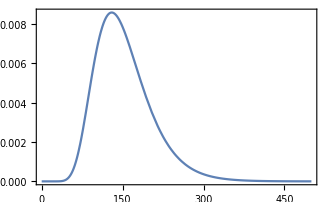

```mathematica
d = 20;
pup = 0.2;
pdw = 0.08;
Γ = 20;
P = WaitingTimeDistributionClassical[t,𝒲[d,pup,pdw,Γ]-𝒲1[d,Γ],𝒲1[d,Γ],𝒲1[d,Γ]];
Plot[P,{t,0,500}]
```

#### Autonomous Quantum Clock: full quantum version

Full quantum model, involving a d-level system + two qubits coupled to a hot & a cold bath

```mathematica
AutonomousClockWaitingTime[d_,ts_,{g_,γ_,Γ_},{Ec_,Ew_},{Tc_,Th_}]:=Module[{Eh,𝕀,σ,K,H0,Hint,cops,ℒ,ℒ1,ρ},
Eh = Ec + Ew;
𝕀 = Eye[d];
σ=({{0, 1}, {0, 0}});
Do[K[k] = Basis[d,k],{k,d}];

H0 = Ec kron[σ†.σ,σ0,𝕀] + Eh kron[σ0,σ†.σ,𝕀] + Sum[(k-1) Ew kron[σ0,σ0,out[K[k],K[k]]],{k,d}];

Hint = g Sum[kron[σ†,σ,out[K[k+1],K[k]]],{k,1,d-1}];
Hint = Hint + Hint†;
cops = {
√γ kron[σ,σ0,𝕀],
√(γ ⅇ^(-Ec/Tc))kron[σ†,σ0,𝕀],
√γ kron[σ0,σ,𝕀],
√(γ ⅇ^(-Eh/Th))kron[σ0,σ†,𝕀],
√Γ kron[σ0,σ0,out[K[1],K[d]]]};
ℒ = Liouvillian[H0+Hint ,cops];
ℒ1 = cf@JumpOp[cops⟦-1⟧];
ρ = kron[({{1/(1+Exp[-Ec/Tc]), 0}, {0, 1/(1+Exp[Ec/Tc])}}),({{1/(1+Exp[-Eh/Th]), 0}, {0, 1/(1+Exp[Eh/Th])}}),Proj[d,1,1]];  
Table[{t,WaitingTimeDistribution[t,ℒ-ℒ1,ℒ1,ℒ1]//Chop},{t,ts}]

]
```

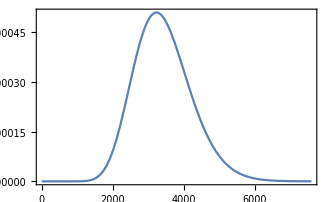

```mathematica
Pfull=AutonomousClockWaitingTime[
d = 18,
ts=linspace[0,7600,80],
{g=0.05,γ=0.3,Γ=0.05},
{Ec=20,Ew=1.0},
{Tc = 1.0,Th = 100}];
ListLinePlot[Pfull,PlotRange->All]
```

Comparison with the effective model

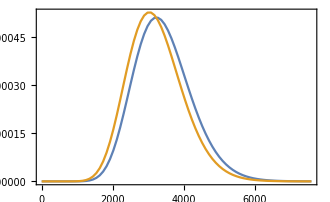

```mathematica
Zc = 1+ ⅇ^(-Ec/Tc);
Zh = 1+ ⅇ^(-Eh/Th);
Eh = Ec + Ew;
pdw = (4 g^2 Exp[-Ec/Tc])/(Zh Zc  γ (Zh+Zc));
pup = (4 g^2 Exp[-Eh/Th])/(Zh Zc  γ (Zh+Zc));

Peff =Table[{t, WaitingTimeDistributionClassical[t,SetPrecision[𝒲[d,pup,pdw,Γ]-𝒲1[d,Γ],20],SetPrecision[𝒲1[d,Γ],20],SetPrecision[𝒲1[d,Γ],20]]},{t,ts}];
ListLinePlot[{Pfull,Peff}]
```

### No-jump distribution

```mathematica
(* The actual no-jump distribution is computed as Subscript[P, no]=tr(ρf), where f is the output of "NoJumpDistributionFactor" *)
(* This is what the function NoJumpDistribution does *)

Clear[NoJumpDistributionFactor];
NoJumpDistributionFactor[ts_,ℒ0_]:=Module[{d = (Length[ℒ0])^(1/2)},
Table[UnTr@MatrixExp[ℒ0 t, kron[Basis[d,j],Basis[d,i]]],{j,d},{i,d},{t,ts}]]

NoJumpDistributionFactor[ts_,H_,cops_]:=Module[{d = H,He,ℰ},
He = H - ⅈ/2 Total@Table[c†.c,{c,cops}];
Transpose[Table[
ℰ = MatrixExp[-ⅈ He t];
ℰ†.ℰ,{t,ts}],{3,1,2}]
]
```

```mathematica
Clear[NoJumpDistribution];
NoJumpDistribution[ρ_,f_]:=Vec[ρ].Flatten[f,1]//Chop

NoJumpDistribution[ρ_,ts_,ℒ0_]:=With[{f = NoJumpDistributionFactor[ts,ℒ0]},NoJumpDistribution[ρ,f]];

NoJumpDistribution[ρ_,ts_,H_,cops_]:=With[{f = NoJumpDistributionFactor[ts,H,cops]},NoJumpDistribution[ρ,f]];
```

#### Example usage and sanity checks

```mathematica
H = 0.5 σx/2;
c1 = √0.1 σm;
c2 = √0.3 σp;
ℒ = Liouvillian[H,{c1,c2}];
ℒ1 = JumpOp[c1]+JumpOp[c2];
ℒ0 = ℒ-ℒ1;
ρ = ({{0.3, 0.1ⅈ}, {-0.1ⅈ, 0.7}});
He = H - ⅈ/2(c1†.c1+c2†.c2);
ts=range[0,2,0.1];
```

```mathematica
f=NoJumpDistributionFactor[ts,ℒ0]
f2=NoJumpDistributionFactor[ts,H,{c1,c2}]
```

{{{1.,0.990046,0.980167,0.970339,0.960541,0.950754,0.940958,0.931137,0.921276,0.911361,0.90138,0.891324,0.881182,0.870947,0.860612,0.850172,0.839624,0.828965,0.818193,0.807307,0.796308},{0,0.-0.000245001 ⅈ,0.-0.000960021 ⅈ,0.-0.00211516 ⅈ,0.-0.00368066 ⅈ,0.-0.00562701 ⅈ,0.-0.00792498 ⅈ,0.-0.0105457 ⅈ,0.-0.0134607 ⅈ,0.-0.016642 ⅈ,0.-0.0200622 ⅈ,0.-0.0236944 ⅈ,0.-0.0275124 ⅈ,0.-0.0314906 ⅈ,0.-0.0356043 ⅈ,0.-0.0398293 ⅈ,0.-0.0441423 ⅈ,0.-0.0485209 ⅈ,0.-0.0529434 ⅈ,0.-0.0573891 ⅈ,0.-0.0618381 ⅈ}},{{0,0.+0.000245001 ⅈ,0.+0.000960021 ⅈ,0.+0.00211516 ⅈ,0.+0.00368066 ⅈ,0.+0.00562701 ⅈ,0.+0.00792498 ⅈ,0.+0.0105457 ⅈ,0.+0.0134607 ⅈ,0.+0.016642 ⅈ,0.+0.0200622 ⅈ,0.+0.0236944 ⅈ,0.+0.0275124 ⅈ,0.+0.0314906 ⅈ,0.+0.0356043 ⅈ,0.+0.0398293 ⅈ,0.+0.0441423 ⅈ,0.+0.0485209 ⅈ,0.+0.0529434 ⅈ,0.+0.0573891 ⅈ,0.+0.0618381 ⅈ},{1.,0.97045,0.941796,0.914036,0.887164,0.861172,0.836053,0.811798,0.788396,0.765836,0.744106,0.723192,0.703079,0.683753,0.665197,0.647396,0.630331,0.613984,0.598337,0.583372,0.569068}}}

{{{1.,0.990046,0.980167,0.970339,0.960541,0.950754,0.940958,0.931137,0.921276,0.911361,0.90138,0.891324,0.881182,0.870947,0.860612,0.850172,0.839624,0.828965,0.818193,0.807307,0.796308},{0,0.-0.000245001 ⅈ,0.-0.000960021 ⅈ,0.-0.00211516 ⅈ,0.-0.00368066 ⅈ,0.-0.00562701 ⅈ,0.-0.00792498 ⅈ,0.-0.0105457 ⅈ,0.-0.0134607 ⅈ,0.-0.016642 ⅈ,0.-0.0200622 ⅈ,0.-0.0236944 ⅈ,0.-0.0275124 ⅈ,0.-0.0314906 ⅈ,0.-0.0356043 ⅈ,0.-0.0398293 ⅈ,0.-0.0441423 ⅈ,0.-0.0485209 ⅈ,0.-0.0529434 ⅈ,0.-0.0573891 ⅈ,0.-0.0618381 ⅈ}},{{0,0.+0.000245001 ⅈ,0.+0.000960021 ⅈ,0.+0.00211516 ⅈ,0.+0.00368066 ⅈ,0.+0.00562701 ⅈ,0.+0.00792498 ⅈ,0.+0.0105457 ⅈ,0.+0.0134607 ⅈ,0.+0.016642 ⅈ,0.+0.0200622 ⅈ,0.+0.0236944 ⅈ,0.+0.0275124 ⅈ,0.+0.0314906 ⅈ,0.+0.0356043 ⅈ,0.+0.0398293 ⅈ,0.+0.0441423 ⅈ,0.+0.0485209 ⅈ,0.+0.0529434 ⅈ,0.+0.0573891 ⅈ,0.+0.0618381 ⅈ},{1.,0.97045,0.941796,0.914036,0.887164,0.861172,0.836053,0.811798,0.788396,0.765836,0.744106,0.723192,0.703079,0.683753,0.665197,0.647396,0.630331,0.613984,0.598337,0.583372,0.569068}}}

```mathematica
Table[Chop@UnTr@MatrixExp[ℒ0 t,Vec[ρ]],{t,ts}]
Table[Chop@Tr[MatrixExp[-ⅈ He t].ρ.MatrixExp[ⅈ He† t]],{t,ts}]
NoJumpDistribution[ρ,f]
NoJumpDistribution[ρ,f2]
```

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

{1.,0.976279,0.953115,0.930504,0.908441,0.886921,0.86594,0.845491,0.825568,0.806165,0.787276,0.768892,0.751007,0.733613,0.716701,0.700263,0.68429,0.668774,0.653705,0.639074,0.624872}

«1 more identical outputs»

### Emission & absorption spectra

The steady-state emission spectra of a system, with jump operator c, is defined as 

ℰ(ω) = ∫ dτ e^(-ⅈ ω τ) ⟨c†(τ)c(0)⟩ = ⟨b_out^†(ω)b_out(ω)⟩

The absorption spectra, on the other hand, is given by 

𝒜(ω) = ∫ dτ e^(-ⅈ ω τ) ⟨c(0)c†(τ)⟩

The 2-time correlation functions can be computed using the quantum regression theorem: 

⟨A(t+τ)B(t)⟩ = tr(A e^(ℒ τ)(Bρ_t)) 
or
⟨A(t)B(t+τ)⟩ = tr(B e^(ℒ τ)(ρ_t A)) 

with τ > 0. 

We thus get 

ℰ(ω) = - tr(c† 1/(ℒ-ⅈ ω)(c ρ)) - tr(c 1/(ℒ+ⅈ ω)(ρ c†))
and
𝒜(ω) = -tr(c† 1/(ℒ-ⅈ ω)(ρ c)) - tr(c 1/(ℒ+ⅈ ω)(c†ρ ))

For Quantum white noise, the output field correlation function is given by 

⟨b_out^†(t) b_out(t')⟩ = γ N δ(t-t') + γ (N+1) ⟨c†(t)c(t’)⟩ - γ N ⟨c(t’) c†(t)⟩

Hence, the power spectrum of the measured output field is actually (in the steady-state)

𝒮(ω) = ∫ dτ e^(-ι ω τ) ⟨b_out^†(τ)b_out(0)⟩ = γ N + γ (N+1) ℰ(ω) - γ N 𝒜(ω)

That is, it can be readily determined from the emission and absorption spectra.

```mathematica
Clear[EmissionSpectrum];
EmissionSpectrum[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp,𝕀=Eye[Length@L]},

tab = Table[
α = LinearSolve[L-ⅈ ω 𝕀, Vec[c.ρ]];
(*β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[ρ.c†]];*)
tmp= -Tr[c†.Unvec[α]](*-Tr[c.Unvec[β]]*);
tmp+tmp*
,{ω,ωs}];

tab//Chop
]
```

```mathematica
Clear[AbsorptionSpectrum];
AbsorptionSpectrum[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[ρ.c]];
(*β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[c†.ρ]];*)
tmp= -Tr[c†.Unvec[α]](*-Tr[c.Unvec[β]]*);
tmp+tmp*
,{ω,ωs}];

tab//Chop
]
```

#### Checking the symmetry of the 2 terms

Verifying that 

tr(c 1/(ℒ+ⅈ ω)(ρ c†)) = conjugate of tr(c† 1/(ℒ-ⅈ ω)(c ρ))

```mathematica
H = 0.8 σz + 0.7 σx + 0.6 σy + 0.1 σ0;
ℒ=Liouvillian[H,{σm,σp,σz},{0.3,0.8,0.1}];
ρ = SteadyState[ℒ]//mf;
ωs = linspace[-10,10,100];
```

(0.630436 | 0.131167-0.0363424 ⅈ
0.131167+0.0363424 ⅈ | 0.369564)

```mathematica
S = EmissionSpectrum[ρ,ωs,ℒ,σm]
```

{0.00785336,0.00814129,0.00844567,0.00876781,0.00910915,0.00947129,0.00985599,0.0102652,0.0107012,0.0111664,0.0116636,0.0121958,0.0127666,0.01338,0.0140405,0.0147533,0.0155244,0.0163607,0.0172701,0.0182621,0.0193478,0.0205401,0.0218548,0.0233107,0.0249307,0.0267431,0.0287829,0.0310941,0.0337322,0.036768,0.0402913,0.0444138,0.0492665,0.0549788,0.0616123,0.0690098,0.0765912,0.0834256,0.0890678,0.094482,0.101537,0.111851,0.12656,0.146709,0.173564,0.208569,0.252721,0.304856,0.358825,0.402374,0.423658,0.422771,0.412578,0.407921,0.418755,0.450964,0.509177,0.59811,0.721009,0.873104,1.02881,1.13371,1.13153,1.01951,0.851442,0.682951,0.540831,0.429673,0.345098,0.281006,0.232088,0.194301,0.164708,0.141207,0.122292,0.106876,0.0941662,0.0835753,0.0746642,0.0670997,0.060626,0.0550448,0.0502002,0.0459686,0.0422512,0.0389682,0.0360545,0.0334569,0.0311311,0.0290407,0.0271548,0.0254475,0.0238971,0.0224848,0.0211946,0.0200129,0.0189278,0.017929,0.0170076,0.0161558}

```mathematica
S2 = EmissionSpectrum2[ρ,ωs,ℒ,σm]
```

{0.00785336,0.00814129,0.00844567,0.00876781,0.00910915,0.00947129,0.00985599,0.0102652,0.0107012,0.0111664,0.0116636,0.0121958,0.0127666,0.01338,0.0140405,0.0147533,0.0155244,0.0163607,0.0172701,0.0182621,0.0193478,0.0205401,0.0218548,0.0233107,0.0249307,0.0267431,0.0287829,0.0310941,0.0337322,0.036768,0.0402913,0.0444138,0.0492665,0.0549788,0.0616123,0.0690098,0.0765912,0.0834256,0.0890678,0.094482,0.101537,0.111851,0.12656,0.146709,0.173564,0.208569,0.252721,0.304856,0.358825,0.402374,0.423658,0.422771,0.412578,0.407921,0.418755,0.450964,0.509177,0.59811,0.721009,0.873104,1.02881,1.13371,1.13153,1.01951,0.851442,0.682951,0.540831,0.429673,0.345098,0.281006,0.232088,0.194301,0.164708,0.141207,0.122292,0.106876,0.0941662,0.0835753,0.0746642,0.0670997,0.060626,0.0550448,0.0502002,0.0459686,0.0422512,0.0389682,0.0360545,0.0334569,0.0311311,0.0290407,0.0271548,0.0254475,0.0238971,0.0224848,0.0211946,0.0200129,0.0189278,0.017929,0.0170076,0.0161558}

```mathematica
S-S2//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Clear[EmissionSpectrum2];
EmissionSpectrum2[ρ_,ωs_,L_,c_]:=Module[{one,J,α,β,tab,tmp},

tab = Table[
α = LinearSolve[L-ⅈ ω Eye[Length@L], Vec[c.ρ]];
β = LinearSolve[L+ⅈ ω Eye[Length@L], Vec[ρ.c†]];
tmp= -Tr[c†.Unvec[α]]-Tr[c.Unvec[β]];
(*tmp+tmp**)
tmp
,{ω,ωs}];

tab//Chop
]
```

#### Example: Mollow Triplet in the fluorescence spectrum of a qubit

```mathematica
ℒ = Liouvillian[Ω/2 σx,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(Ω^2/(γ^2+2 Ω^2) | -(ⅈ γ Ω)/(γ^2+2 Ω^2)
(ⅈ γ Ω)/(γ^2+2 Ω^2) | (γ^2+Ω^2)/(γ^2+2 Ω^2))

```mathematica
S=FCSEmissionSpectrum[ρ,{ω},ℒ,σm]//First//cf
```

(8 γ Ω^4 (2 (γ^2+ω^2)+Ω^2))/((γ^2+4 ω^2) (γ^2+2 Ω^2) (γ^4+4 (ω^2-Ω^2)^2+γ^2 (5 ω^2+4 Ω^2)))

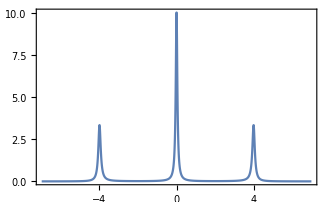

```mathematica
Plot[S/.{γ->0.1,Ω->4},{ω,-7,7}]
```

#### Emission spectrum of the tight-binding model

```mathematica
Clear[h,H,γ,ℒ,ρ];
h = TightBindingHamiltonian[4];
LoadFermionicOperators[4];
H = Sum[h⟦i,j⟧ cd[i].c[j],{i,4},{j,4}];
γ =0.01;
ℒ = N@Liouvillian[H,{cd[1],c[4]},{γ,γ}];
ρ = SteadyState[ℒ];
ωs = linspace[-2,4,100];
ee=EmissionSpectrum[ρ, ωs,ℒ,c[4]];
```

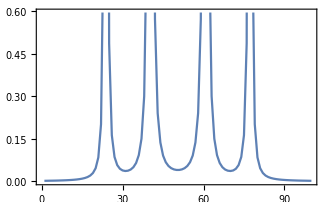

```mathematica
ListLinePlot[ee]
```

### Collision Models

```mathematica
Clear[CollisionMap];
CollisionMap[ρs0_,U_,ρa_,n_,output_:"system"]:=Module[{ds=Length@ρs0,da=Length@ρa},

Which[
output=="system",
NestList[PTr[U.kron[#,ρa].U†,{2},{ds,da}]&,ρs0,n],
output=="all",
NestList[
With[{ρsa=U.kron[#⟦1⟧,ρa].U†} , 
{PTr[ρsa,{2},{ds,da}],PTr[ρsa,{1},{ds,da}]}]&,{ρs0,ρa},n]
]
]
```

```mathematica
Clear[CollisionModelSteadyState]
CollisionModelSteadyState[U_,ρa_]:=Module[{da=Length@ρa,ds,ρ,𝒯,p},
ds = Length[U]/da;
ρ = Table[p[i,j],{i,ds},{j,ds}];
𝒯=Last@CoefficientArrays[Vec[PTr[U.kron[ρ,ρa].U†,{2},{ds,da}]],Vec[ρ]];
(*SteadyState[𝒯-Eye[ds^2]]*)
AnalyticalSteadyState[𝒯-Eye[ds^2]] (* "AnalyticalSteadyState handles multiple steady-states, by selecting one that is guaranteed physical *)
]
```

#### Example usage

```mathematica
ρs0 = ({{1, 0}, {0, 0}});
ρa = ({{0.4, 0}, {0, 0.6}});
U = PartialSWAP[0.5,1,2,2]//mf;
```

(0.5-0.866025 ⅈ | 0 | 0 | 0
0 | 0.-0.866025 ⅈ | 0.5 | 0
0 | 0.5 | 0.-0.866025 ⅈ | 0
0 | 0 | 0 | 0.5-0.866025 ⅈ)

```mathematica
mf/@CollisionMap[ρs0,U,ρa,10];
```

(1 | 0
0 | 0)

(0.85 | 0
0 | 0.15)

(0.7375 | 0
0 | 0.2625)

(0.653125 | 0
0 | 0.346875)

(0.589844 | 0
0 | 0.410156)

(0.542383 | 0
0 | 0.457617)

(0.506787 | 0
0 | 0.493213)

(0.48009 | 0
0 | 0.51991)

(0.460068 | 0
0 | 0.539932)

(0.445051 | 0
0 | 0.554949)

(0.433788 | 0
0 | 0.566212)

```mathematica
results=CollisionMap[ρs0,U,ρa,10,"all"]//Chop;
TableForm[Table[
{MatrixForm[results⟦i,1⟧],MatrixForm[results⟦i,2⟧]},
{i,10}],TableHeadings->{None,{"S","A"}}]
```

S | A
(1 | 0
0 | 0) | (0.4 | 0
0 | 0.6)
(0.85 | 0
0 | 0.15) | (0.55 | 0
0 | 0.45)
(0.7375 | 0
0 | 0.2625) | (0.5125 | 0
0 | 0.4875)
(0.653125 | 0
0 | 0.346875) | (0.484375 | 0
0 | 0.515625)
(0.589844 | 0
0 | 0.410156) | (0.463281 | 0
0 | 0.536719)
(0.542383 | 0
0 | 0.457617) | (0.447461 | 0
0 | 0.552539)
(0.506787 | 0
0 | 0.493213) | (0.435596 | 0
0 | 0.564404)
(0.48009 | 0
0 | 0.51991) | (0.426697 | 0
0 | 0.573303)
(0.460068 | 0
0 | 0.539932) | (0.420023 | 0
0 | 0.579977)
(0.445051 | 0
0 | 0.554949) | (0.415017 | 0
0 | 0.584983)

```mathematica
ρa = ({{0.4, 0}, {0, 0.6}});
U = PartialSWAP[0.5,1,2,2];
CollisionModelSteadyState[U,ρa]//mf;
```

(0.4 | 0
0 | 0.6)

```mathematica
χ = {√0.3,√(1-0.3)};
LoadSpinChainMatrices[2];
U = MatrixExp[-ⅈ sx[1].sx[2]];
𝒯=CollisionModelSteadyState[U,out[χ,χ]]//mf;
```

(0.5 | 0
0 | 0.5)

### Worked Examples

#### Minimal 2-qubit engine

Based on https://arxiv.org/pdf/1010.6029.pdf and http://arxiv.org/abs/2106.13817

```mathematica
LoadSpinChainMatrices[2,"a"];
H0 = ϵ1 sp[1].sm[1] + ϵ2 sp[2].sm[2];
V = g(sp[1].sm[2]+sp[2].sm[1]);

cops = {
√γ1m sm[1],
√γ1p sp[1],
√γ2m sm[2],
√γ2p sp[2]
};
ℒ = Liouvillian[V,{sm[1],sp[1],sm[2],sp[2]},{γ1m,γ1p,γ2m,γ2p}]//cf;
```

```mathematica
ρ = AnalyticalSteadyState[ℒ]//Simplify//mf;
```

((4 g^2 (γ1p+γ2p)^2+γ1p γ2p (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0 | 0 | 0
0 | (4 g^2 (γ1m+γ2m) (γ1p+γ2p)+γ1p γ2m (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | (2 ⅈ g (γ1p γ2m-γ1m γ2p))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0
0 | (2 ⅈ g (-γ1p γ2m+γ1m γ2p))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | (4 g^2 (γ1m+γ2m) (γ1p+γ2p)+γ1m γ2p (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))) | 0
0 | 0 | 0 | (4 g^2 (γ1m+γ2m)^2+γ1m γ2m (γ1m+γ1p+γ2m+γ2p)^2)/((γ1m+γ1p+γ2m+γ2p)^2 (4 g^2+(γ1m+γ1p) (γ2m+γ2p))))

```mathematica
𝒟1 = γ1m LindbladToVec[sm[1]] + γ1p LindbladToVec[sp[1]];
𝒟2 = γ2m LindbladToVec[sm[2]] + γ2p LindbladToVec[sp[2]];
Tr[V.Unvec[𝒟1.Vec[ρ]]]//Simplify
Tr[V.Unvec[𝒟2.Vec[ρ]]]//Simplify
```

0

0

```mathematica
W = ⅈ g (ϵ2-ϵ1) Tr[(sp[1].sm[2]-sp[2].sm[1]).ρ]//cf
```

(4 g^2 (-γ1p γ2m+γ1m γ2p) (ϵ1-ϵ2))/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
Q1 = Tr[H0.Unvec[𝒟1.Vec[ρ]]]//Simplify
Q1 = ϵ1 (γ1p Tr[sm[1].sp[1].ρ]- γ1m Tr[sp[1].sm[1].ρ])//cf
```

(4 g^2 (γ1p γ2m-γ1m γ2p) ϵ1)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

(4 g^2 (γ1p γ2m-γ1m γ2p) ϵ1)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
Q2 = Tr[H0.Unvec[𝒟2.Vec[ρ]]]//Simplify
```

(4 g^2 (-γ1p γ2m+γ1m γ2p) ϵ2)/((γ1m+γ1p+γ2m+γ2p) (4 g^2+(γ1m+γ1p) (γ2m+γ2p)))

```mathematica
W+Q1+Q2//cf
```

0

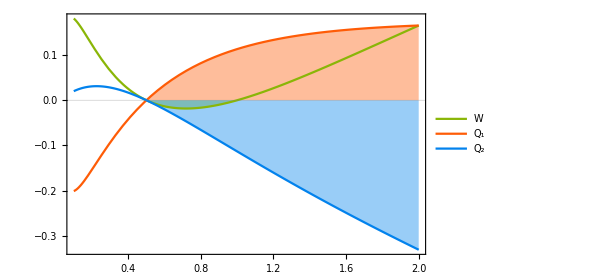

```mathematica
n1 = 1/(Exp[β1 ϵ1]-1);
n2 = 1/(Exp[β2 ϵ2]-1);
{c1,c2,c3} ={RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]};
rep = {γ1m->(n1+1),γ1p->n1,γ2m->n2+1,γ2p->n2,g->3};
(*Manipulate[Plot[Evaluate[{W,Q1,Q2}/.rep/.{ϵ1->1,β1->1/T1,β2->1/T2}],{ϵ2,0.1,2},
GridLines->{None,{0}},
PlotStyle->{c1,c2,c3},
ImageSize->450,
PlotLegends->legend[{"W","Q_1","Q_2"},{0.3,0.1},LegendLayout->Row],
Filling->{
1->{Axis,{Directive[c1,Opacity[0.4]],Opacity[0]}},
2->{Axis,{Opacity[0],Directive[c2,Opacity[0.4]]}},
3->{Axis,{Directive[c3,Opacity[0.4]],Opacity[0]}}}

],
{{T1,1},0.1,3},
{{T2,1/2},0.1,3}]*)

Plot[Evaluate[{W,Q1,Q2}/.rep/.{ϵ1->1,β1->1,β2->2}],{ϵ2,0.1,2},
GridLines->{None,{0}},
PlotStyle->{c1,c2,c3},
ImageSize->450,
PlotLegends->legend[{"W","Q_1","Q_2"},{0.3,0.1},LegendLayout->"Row"],
Filling->{
1->{Axis,{Directive[c1,Opacity[0.4]],Opacity[0]}},
2->{Axis,{Opacity[0],Directive[c2,Opacity[0.4]]}},
3->{Axis,{Directive[c3,Opacity[0.4]],Opacity[0]}}}
]
```

## Full counting statistics

### DrazinApply: Applies the Drazi inverse of an operator

```mathematica
(* Not yet sure which approach is more efficient. Found 1 example where DrazinApply does not work, but DrazinApply2 does. *)
```

```mathematica
DrazinApply[ℒ_,y_]:=LinearSolve[Join[ℒ,{Vec@Eye[√(Length@ℒ)]}], Join[y ,{0}]]

DrazinApply2[ℒ_,ρv_,y_]:=Module[{z},
z = LinearSolve[ℒ, y-ρv UnTr[y]];
z - ρv UnTr[z]
]
```

#### Example usage

```mathematica
ℒ = Liouvillian[σz,{√γm σm,√γp σp}]//cf;
ρ = AnalyticalSteadyState[ℒ];
ℒD=DrazinInverse[ℒ,ρ]//cf//mf;
```

(-γm/(γm+γp)^2 | 0 | 0 | γp/(γm+γp)^2
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γm/(γm+γp)^2 | 0 | 0 | -γp/(γm+γp)^2)

ℒ^+ℒ= 1 - |ρ⟩⟨1|:

```mathematica
P0 = out[Vec[ρ],Vec[Eye[2]]];
P = Eye[4]-P0;
```

```mathematica
ℒD.ℒ-P//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℒD.P0//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℒD.P-ℒD//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Comparison with the Moore-Penrose pseudo-inverse: it does not match. 
I have no idea what Mathematica does here. I think it is using SVD.

```mathematica
ℒMP=PseudoInverse[ℒ]//cf//mf;
```

(-γm/(2 (γm^2+γp^2)) | 0 | 0 | γm/(2 (γm^2+γp^2))
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γp/(2 (γm^2+γp^2)) | 0 | 0 | -γp/(2 (γm^2+γp^2)))

```mathematica
ℒD-P.ℒMP.P//cf//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Comparing with the integral formula

```mathematica
-Integrate[MatrixExp[ℒ t].(Eye[4]-out[Vec[ρ],Vec[Eye[2]]]),{t,0,∞},Assumptions->{γm>0,γp>0}]//mf;
```

(-γm/(γm+γp)^2 | 0 | 0 | γp/(γm+γp)^2
0 | -2/(-4 ⅈ+γm+γp) | 0 | 0
0 | 0 | -2/(4 ⅈ+γm+γp) | 0
γm/(γm+γp)^2 | 0 | 0 | -γp/(γm+γp)^2)

### Auxiliary Functions

```mathematica
fcsJumpterms = {"jump","Jumps","PD","Photo Detection"};
fcsDiffterms = {"diffusion","homodyne","diffusive","diff"};

Clear[JumpOp];
JumpOp[c_,type_:"jump"]:=
Which[
matchString[fcsJumpterms,type],kron[c*,c],
matchString[fcsDiffterms,type]||True,kron[Eye[Length@c],c]+kron[c*,Eye[Length@c]]
]

Clear[fcsGetL];
fcsGetL[LL_,type_]:=Module[{L,d},
L=If[Length@Dimensions[LL]==2,{JumpOp[LL,type]},JumpOp[#,type]&/@LL]; (* List of operators *);
d = Length@L;
{L,d}
]

Clear[fcsGetNu];
fcsGetNu[νν_,d_]:=Module[{ν,R},
ν = Which[
Dimensions[νν]==={d},{νν},
Dimensions[νν]==={},{νν ConstantArray[1,d]},
True,νν];
R = Length@ν;
{ν,R}
];

Clear[fcsGetK];
fcsGetK[μ_,L_,ρ_,type_]:=Module[{ρv,Jk,K},
ρv = Vec[ρ];
Jk = Table[UnTr[lop.ρv],{lop,L}];

K=Which[
matchString[fcsJumpterms,type],μ.DiagonalMatrix[Jk].(μᵀ)*,
matchString[fcsDiffterms,type]||True,μ.(μᵀ)*
]//Chop;
{K,Jk}
]
```

### Average current

```mathematica
Clear[FCSAverage];
FCSAverage[ρ_,ℒ_,LL_,νν_:1,type_:"jump"]:=Module[{L,ν,ρv,d,res,R},

{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];
res=Table[Total@Table[ν⟦α,i⟧ UnTr[L⟦i⟧.ρv],{i,d}],{α,Length@ν}]//Chop;
If[Length@res==1,res⟦1⟧,res]
]
```

```mathematica
Clear[FCSK];
FCSK[ρ_,ℒ_,LL_,νν_:1,type_:"jump"]:=fcsGetK[νν,LL,ρ,type][[1]];
```

### Noise (diffusion matrix)

```mathematica
Clear[FCSNoise];
FCSNoise[ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:=Module[{L,ν,ρv,d,Jk,M,R,ℒbig,ℒα,Jα,ws,𝒟,K},

{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];
{K,Jk} = fcsGetK[ν,L,ρ,type];

ℒα = ν.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
ℒbig =Join[ℒ,{Vec@Eye[√(Length@ℒ)]}];
ws = Table[LinearSolve[ℒbig, Join[ℒα⟦i⟧.ρv-Jα⟦i⟧ ρv ,{0}]],{i,R}];
𝒟 = -Table[UnTr[ℒα⟦i⟧.ws⟦j⟧],{i,R},{j,R}];
𝒟=𝒟 + 𝒟ᵀ + K//Chop;
If[R===1,𝒟⟦1,1⟧,𝒟]
]

(* Legacy name *)
Clear[FCSDiffusionMatrix];
FCSDiffusionMatrix[ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:= FCSNoise[ρ,ℒ,LL,νν,type]
```

### Power spectrum

```mathematica
Clear[FCSPowerSpectrum]
FCSPowerSpectrum[ωωs_,ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:=Module[{L,ν,ρv,d,Jk,K,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮,v1,v2,𝕀,ωs,S},

{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];
{K,Jk} = fcsGetK[ν,L,ρ,type];
ωs = Flatten@{ωωs};

ℒα = ν.L;
(*Jα = UnTr[#.ρv]&/@ℒα//Chop;*)

𝕀 = Eye[Length@ℒ];
S=Table[
v1=Table[LinearSolve[ℒ - ⅈ ω 𝕀, ℒα⟦i⟧.ρv],{i,R}];
v2=Table[LinearSolve[ℒ + ⅈ ω 𝕀, ℒα⟦i⟧.ρv],{i,R}];
𝒮=K - Table[UnTr[ℒα⟦β⟧.v1⟦α⟧] + UnTr[ℒα⟦α⟧.v2⟦β⟧],{α,R},{β,R}];
{ω,If[R===1,𝒮⟦1,1⟧,𝒮]}
,{ω,ωs}]//Chop;

If[Length@ωs==1,S[[1,2]],S]
]
```

```mathematica
Clear[FCSEigenPowerSpectrum]
FCSEigenPowerSpectrum[ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:=Module[{L,ν,ρv,d,Jk,K,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];
{K,Jk} = fcsGetK[ν,L,ρ,type];

ℒα = ν.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;
{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

Υ = Table[UnTr[ℒα⟦α⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦β⟧.ρv],{α,R},{β,R},{j,Length[λ]}];

If[R===1,
Function[K⟦1,1⟧ - Chop@Total@Table[1/(λ⟦j⟧-ⅈ #)Υ⟦1,1,j⟧+1/(λ⟦j⟧+ⅈ #)Υ⟦1,1,j⟧,{j,Length[λ]}] ],
Function[K -Table[Chop@Total@Table[1/(λ⟦j⟧-ⅈ #)Υ⟦β,α,j⟧+1/(λ⟦j⟧+ⅈ #)Υ⟦α,β,j⟧,{j,Length[λ]}] ,{α,R},{β,R}]]
]//Chop

]
```

```mathematica
Clear[FCSCoherence];
FCSCoherence[𝒮_,ω_]:=Abs[𝒮[ω]⟦1,2⟧]^2/(𝒮[ω]⟦1,1⟧ 𝒮[ω]⟦2,2⟧)
```

### 2-time correlation function ⟨A(t) B(t+τ) C(t)⟩

```mathematica
Clear[FCSCorr];
FCSCorr[tts_,ρ_,ℒ_,A_,B_,𝒞_]:=Module[{ts,res,R},
ts = Flatten@{tts};
R = 𝒞.ρ.A//Vec;

If[Length@ts==1,
Tr[B.Unvec@MatrixExp[ℒ ts[[1]],R]],
Table[{t,Tr[B.Unvec@MatrixExp[ℒ t,R]]},{t,ts}]
](*//Chop*)
];
```

```mathematica
Clear[FCSg2];
FCSg2[tts_,ρ_,ℒ_,c_]:= If[Length@Flatten@{tts}==1,

FCSCorr[Flatten@{tts},ρ,ℒ,c†,c†.c,c]/FCSAverage[ρ,ℒ,{c}]^2,
{#[[1]],(#[[2]])/FCSAverage[ρ,ℒ,{c}]^2}&/@FCSCorr[Flatten@{tts},ρ,ℒ,c†,c†.c,c]//Chop
];
```

```mathematica
Clear[FCSEigenCorr];
FCSEigenCorr[ρ_,ℒ_,A_,B_,𝒞_]:=Module[{res,R,λ,Q,x,y,Υ},
R = 𝒞.ρ.A//Vec;

{λ,Q} = Eigsys[ℒ];
x = (Qᵀ);
y=Inverse[Q];
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]}] *)

Υ = Table[Tr[B.Unvec[out[x⟦j⟧,y⟦j⟧*].R]],{j,Length[λ]}];
Function[(*Chop@*)Total@Table[Exp[λ[[j]] #] Υ[[j]],{j,Length@λ}]]
];
```

```mathematica
Clear[FCSEigeng2]
FCSEigeng2[ρ_,ℒ_,c_]:=Function[t,(FCSEigenCorr[ρ,ℒ,c†,c†.c,c][t])/FCSAverage[ρ,ℒ,{c}]^2];
```

### Two-point function F(τ)=tr(𝒥 e^(ℒ τ)𝒥 ρ)-J^2

```mathematica
Clear[FCSTwoPointFunction]
FCSTwoPointFunction[tts_,ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:=Module[{L,ν,ρv,d,R,ℒbig,ℒα,Jα,ws,𝒟,λ,Q,x,y,Υ,𝒮,F,ts},
ts = Flatten@{tts};
{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];

ℒα = ν.L;
Jα = UnTr[#.ρv]&/@ℒα//Chop;

F=If[R===1,
Chop@Table[{t,UnTr[ℒα⟦1⟧.MatrixExp[ℒ t,ℒα⟦1⟧.ρv]]-Jα⟦1⟧^2},{t,ts}],
Chop@Table[{t,Table[UnTr[ℒα⟦β⟧.MatrixExp[ℒ t,ℒα⟦α⟧.ρv]]-Jα⟦α⟧Jα⟦β⟧,{α,R},{β,R}]},{t,ts}]
];
If[Length@ts==1,F[[1,2]],F]
]
```

```mathematica
Clear[FCSEigenTwoPointFunction]
FCSEigenTwoPointFunction[ρ_,ℒ_,LL_,νν_:1,type_:"PD"]:=Module[{L,ν,ρv,d,R,ℒbig,ℒα,ws,𝒟,λ,Q,x,y,Υ,𝒮},

{L,d} = fcsGetL[LL,type];
{ν,R} = fcsGetNu[νν,d];
ρv = Vec[ρ];

ℒα = ν.L;

{λ,Q} = Eigsys[ℒ];
λ = Drop[λ,-1];
x = (Qᵀ)⟦1;;-2⟧;
y=Inverse[Q]⟦1;;-2⟧;
(*Defined so that ℒ = Sum[λ⟦i⟧ out[x⟦i⟧,y⟦i⟧*],{i,Length[ℒ]-1}] *)

Υ = Table[UnTr[ℒα⟦β⟧.out[x⟦j⟧,y⟦j⟧*].ℒα⟦α⟧.ρv],{α,R},{β,R},{j,Length[λ]}];

If[R===1,
Function[ Chop@Total@Table[Exp[λ⟦j⟧ #] Υ⟦1,1,j⟧,{j,Length[λ]}] ],
Function[Table[Chop@Total@Table[Exp[λ⟦j⟧ #]Υ⟦β,α,j⟧,{j,Length[λ]}] ,{α,R},{β,R}]]
]
]
```

### FCS probability P(N(t)=n), for the integrated current

P(n,t)=∫_-π^π e^(-i n χ) tr(e^(ℒ_χ t)ρ_0)dχ/(2π)

Only works when output currents are integers; e.g. particle currents etc.

```mathematica
Clear[FCSProbability]
FCSProbability[t_,ρ_,ℒ_,LL_,νν_:1,npts_:1000,tol_:10^-8]:=Module[{cops,L,χs,δχ,ℒs,ρv,Ms,n,ν,d,R,χ,nmax,prob,P},
{L,d} = fcsGetL[LL,"jump"];
{ν,R} = fcsGetNu[νν,d];
ν = First@ν;

χs = linspace[-π,π,npts];
δχ = χs⟦2⟧-χs⟦1⟧;
ℒs = Table[ℒ +Sum[(ⅇ^(ⅈ χ ν⟦i⟧) -1) L[[i]],{i,d}] ,{χ,χs}];

ρv = Vec[ρ];
Ms = Chop@Table[Tr[MatrixExp[ℒs[[i]] t,ρv]],{i,Length@ℒs}];

prob[nns_]:=Table[{n,1/(2π)Trapz[ⅇ^(-ⅈ n χs) Ms,δχ]},{n,nns}]//Chop;

nmax = 10;
P = prob[Range[-nmax,nmax]];
While[P⟦1,2⟧+P⟦-1,2⟧ > tol,
P=Join[prob[Range[-nmax-10,-nmax-1]],P,prob[Range[nmax+1,nmax+10]]];
nmax = nmax+10;
];
P
]
```

```mathematica
Clear[FCSProbabilityDiffusion];
FCSProbabilityDiffusion[t_,ρ_,ℒ_,L_,cutoff_:10,npts_:1000]:=Module[{χs,δχ,ℒs,ρv,Ms,prob,𝕃},

χs = linspace[-cutoff,cutoff,npts];
δχ = χs⟦2⟧-χs⟦1⟧;

ℒs = Table[ℒ + ⅈ χ JumpOp[L,"homodyne"]-χ^2/2 NEye[Length@ℒ] ,{χ,χs}];
ρv = Vec[ρ];
Ms = Chop@Table[Tr[MatrixExp[𝕃 t,ρv]],{𝕃,ℒs}];

prob[n_]:=1/(2π)Trapz[ⅇ^(-ⅈ n χs) Ms,δχ]//Chop;
prob
]
```

#### Example usage

```mathematica
H = 0.4σz+σx;
cops = {0.2σm};
ℒ = Liouvillian[H,cops];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(0.37873 | -0.302984-0.00757461 ⅈ
-0.302984+0.00757461 ⅈ | 0.62127)

```mathematica
(* Takes a second to run *)
```

```mathematica
Clear[P];
ts = Range[0,1000,4];
do[
P[t] = FCSProbability[t,ρ,ℒ,cops],
{t,ts}]
```

0h : 0m : 13s

```mathematica
(* run this to show animation *)
Animate[ListStepPlot[P[t],Filling->Axis,PlotRange->{{-3,30},{0,0.14}},PlotRangePadding->{{None,None},{None,Scaled[0.1]}},PlotLabel->t,ImageSize->350],{t,ts}]
```

### Worked Examples

#### Example usage

Single qubit model coupled to a bath, and with a coherent drive.

```mathematica
H = σz+0.8 σx;
c1 = √0.3 σm;
c2 = √0.65 σp;
ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ]//mf;
```

(0.641384 | 0.107068+0.0254285 ⅈ
0.107068-0.0254285 ⅈ | 0.358616)

Average
Average current of emission and absorptions

```mathematica
{FCSAverage[ρ,ℒ,c1],FCSAverage[ρ,ℒ,c2]}
```

{{1}}

{{1}}

{0.192415,0.233101}

```mathematica
{FCSAverage[ρ,ℒ,c1],FCSAverage[ρ,ℒ,c2]}
```

{0.192415,0.233101}

Net current (absorptions - emissions)

```mathematica
FCSAverage[ρ,ℒ,{c1,c2},{-1,1}]
```

0.0406857

The syntax also accepts multiple current choices at a time (here, all 3 results above)

```mathematica
FCSAverage[ρ,ℒ,{c1,c2},{{1,0},{0,1},{-1,1}}]
```

{0.192415,0.233101,0.0406857}

Choices of μ are not restricted to 0,1,-1. Any value can be provided (used in e.g. defining energy currents)

Diffusion matrix
The syntax is identical to that of the average

```mathematica
{FCSNoise[ρ,ℒ,c1],FCSNoise[ρ,ℒ,c2]}
```

{0.125456,0.164035}

```mathematica
(* But if we input multiple currents together, this also yields the covariance between them *)
FCSNoise[ρ,ℒ,{c1,c2},{{1,0},{0,1}}]//mf;
```

(0.125456 | 0.0884773
0.0884773 | 0.164035)

Homodyne detection
Add “diffusion” to convert results to that of homodyning. 
To add angle, redefine c1 c2

```mathematica
FCSAverage[ρ,ℒ,c1,1,"Diffusion"] (* factor of 1 is the optional choice of μ *)
FCSAverage[ρ,ℒ,c1 ⅇ^(ⅈ π/4),1,"Diffusion"]
```

0.117287

0.0632373

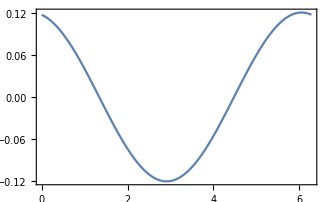

```mathematica
(* Homodyning the entire Bloch sphere *)
ListLinePlot[Table[{ϕ,FCSAverage[ρ,ℒ,c1 ⅇ^(ⅈ ϕ),1,"Diffusion"]},{ϕ,0,2π,0.01}]]
```

Same for the diffusion matrix

```mathematica
FCSNoise[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Diffusion"]//mf;
```

(1.32407 | 0.448941
0.448941 | 1.6195)

Power Spectrum also has the same syntax. 
But there are two options: 
- FCSPowerSpectrumEigen[] diagonalizes ℒ and returns a function of ω, which is then quick to evaluate. 
-  FCSPowerSpectrumLinearSys[] requires a specific list of frequencies “ωs” and operates by solving linear systems.

```mathematica
FCSPowerSpectrum[5.0,ρ,ℒ,{c1,c2},{{1,0},{0,1}}]//mf;
(*%⟦1,2⟧//mf;*)
```

(0.18864 | 0.00532234-0.0111098 ⅈ
0.00532234+0.0111098 ⅈ | 0.227761)

```mathematica
𝒮=FCSEigenPowerSpectrum[ρ,ℒ,{c1,c2},{{1,0},{0,1}}]
```

K$10625-Table[Chop[Total[Table[Υ$10625⟦β,α,j⟧/(λ$10625⟦j⟧-ⅈ #1)+Υ$10625⟦α,β,j⟧/(λ$10625⟦j⟧+ⅈ #1),{j,Length[λ$10625]}]]],{α,R$10625},{β,R$10625}]&

```mathematica
(* Evaluate at specific frequencies *)
𝒮[5.0]//mf;
```

(0.18864 | 0.00532234-0.0111098 ⅈ
0.00532234+0.0111098 ⅈ | 0.227761)

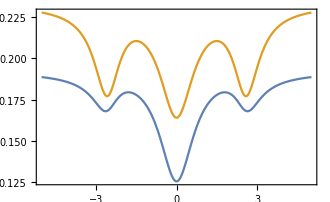

```mathematica
Plot[{
Evaluate@Re[𝒮[ω]⟦1,1⟧],
Evaluate@Re[𝒮[ω]⟦2,2⟧]
},{ω,-5,5}]
```

The “coherence” in the language of signal processing is 𝒞_xy(ω) = (|𝒮_xy(ω)|^2)/(𝒮_xx(ω)𝒮_yy(ω))
https://en.wikipedia.org/wiki/Coherence_(signal_processing)

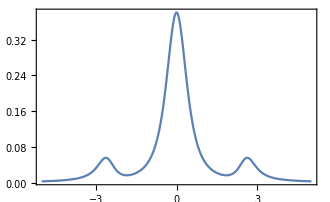

```mathematica
Plot[{
Evaluate@Re[Abs[𝒮[ω]⟦1,2⟧]^2/(𝒮[ω]⟦1,1⟧ 𝒮[ω]⟦2,2⟧)]
},{ω,-5,5},PlotRange->All]
```

Two-time correlation function ⟨A(t) B(t+τ) C(t)⟩

```mathematica
FCSCorr[3.0,ρ,ℒ,σx,σx,σx]//Chop
```

0.178179

```mathematica
FCSCorr[{0.0,3.0,5.0},ρ,ℒ,σx,σx,σx]//Chop
```

{{0,0.214135},{3.,0.178179},{5.,0.223324}}

```mathematica
FCSEigenCorr[ρ,ℒ,σx,σx,σx][5.0]//Chop
```

0.223324

Current 2-time correlation function

```mathematica
FCSTwoPointFunction[3.0,ρ,ℒ,{c1,c2},{1,0}]
```

-0.00224193

```mathematica
FCSEigenTwoPointFunction[ρ,ℒ,{c1,c2},{1,0}][3.0]
```

-0.00224193

#### Example: Reproducing Fig. 2(a) of arXiv 2103.07791

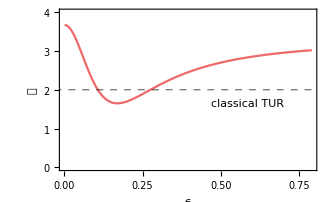

```mathematica
Clear[γu,γl,nu,nl,Δ,ϵ,σ];
γu = 2.0;
γl = 0.1;
nl = 5.0;
nu = 0.027; 
Δ = 0.0;

Do[σ[i,j] = Proj[3,i+1,j+1],{i,0,2},{j,0,2}];
H =  -Δ σ[1,1] + ϵ(σ[1,0] + σ[0,1]);
cops = {√(γl (nl+1))σ[0,2],√(γl nl)σ[2,0],√(γu(nu+1))σ[1,2],√(γu nu)σ[2,1]};
ℒ = Liouvillian[H,cops];
ρ = AnalyticalSteadyState[ℒ];
𝒬=Table[
ave = FCSAverage[ρ,ℒ,cops,{-1,1,0,0}];
var=FCSNoise[ρ,ℒ,cops,{-1,1,0,0}];
{ϵ,Log[(nl(nu+1))/(nu(nl+1))] var/ave},{ϵ,0.001,0.8,0.01}];
ListLinePlot[𝒬,PlotRange->{0,4},
GridLines->{None,{2}},
GridLinesStyle->Directive[Black, Dashed],
PlotStyle->red,
FrameLabel->{"ϵ","𝒬"},
Epilog->Text["classical TUR",Scaled[{0.73,0.42}]]
]
```

#### Example: “Mollow Triplet”; comparison with the emission & absorption spectra

I’m actually not sure this is really the Mollow triplet, since that refers to the emission spectrum and here I am plotting the coherence (in the signal processing sense)

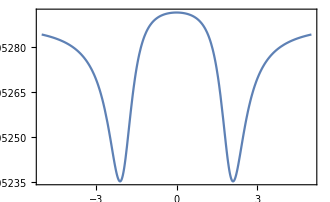
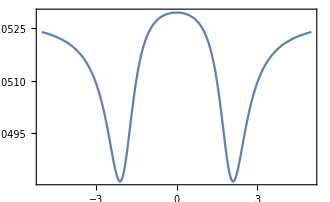
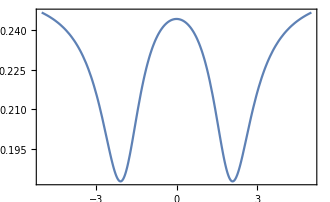
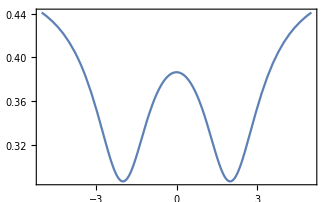

```mathematica
γs = {0.01,0.1,0.5,1.};
f = 0.7;
Clear[𝒮,ℰ,𝒮h,𝒜];
Do[
H =σx;
c1 = √γ σm;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSEigenPowerSpectrum[ρ,ℒ,{c1,c2},{{1,0},{0,1}}];
𝒮h[γ]=FCSEigenPowerSpectrum[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Diffusion"];
ℰ[γ]=EmissionSpectrum[ρ,{ω},ℒ,√γ σm];
𝒜[γ]=AbsorptionSpectrum[ρ,{ω},ℒ,√γ σm];
,{γ,γs}]
Table[Plot[{
Re@𝒮[γ][ω]⟦1,1⟧
},{ω,-5,5},PlotRange->All],{γ,γs}]
```

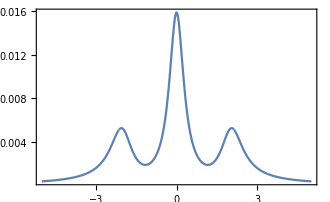
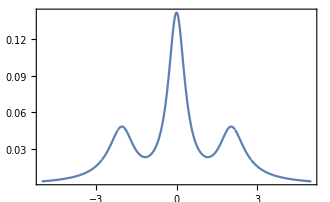
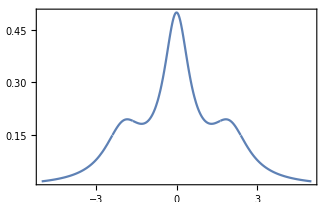
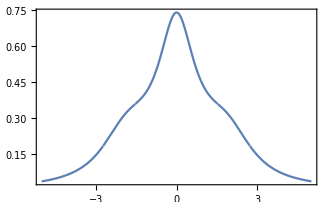

```mathematica
Table[Plot[ℰ[γ],{ω,-5,5}],{γ,γs}]
```

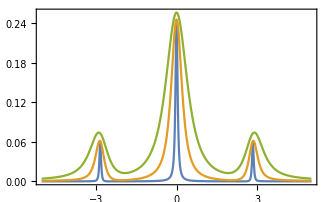

```mathematica
γs = {0.1,0.5,1.};
f = 0.7;
Clear[𝒮];
Do[
H =σz+ σx;
c1 = √(γ (1-f))σm;
c2 = √(γ f)σp;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSEigenPowerSpectrum[ρ,ℒ,{c1,c2},{{1,0},{0,1}}];
,{γ,γs}]
Plot[{
Evaluate@Table[Re[Abs[𝒮[γ][ω]⟦1,2⟧]^2/(𝒮[γ][ω]⟦1,1⟧ 𝒮[γ][ω]⟦2,2⟧)],{γ,γs}]
},{ω,-5,5},PlotRange->All]
```

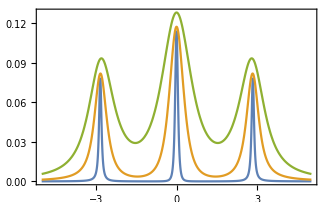

```mathematica
γs = {0.1,0.5,1.};
f = 0.7;
Clear[𝒮];
Do[
H =σz+ σx;
c1 = √(γ (1-f))σm;
c2 = √(γ f)σp;

ℒ = Liouvillian[H,{c1,c2}];
ρ = SteadyState[ℒ];
𝒮[γ]=FCSEigenPowerSpectrum[ρ,ℒ,{c1,c2},{{1,0},{0,1}},"Homodyne"];
,{γ,γs}]
Plot[{
Evaluate@Table[Re[Abs[𝒮[γ][ω]⟦1,2⟧]^2/(𝒮[γ][ω]⟦1,1⟧ 𝒮[γ][ω]⟦2,2⟧)],{γ,γs}]
},{ω,-5,5},PlotRange->All]
```

#### Ex: Mollow Triplet analytically

```mathematica
Clear[γ,Ω,Δ];
H = Δ/2 σz+σx;
c = √γ σm;
ℒ = Liouvillian[H,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(4/(8+γ^2+4 Δ^2) | -(2 ⅈ (γ-2 ⅈ Δ))/(8+γ^2+4 Δ^2)
(2 ⅈ (γ+2 ⅈ Δ))/(8+γ^2+4 Δ^2) | (4+γ^2+4 Δ^2)/(8+γ^2+4 Δ^2))

```mathematica
J=cf@FCSAverage[ρ,ℒ,{c}]
```

(4 γ)/(8+γ^2+4 Δ^2)

```mathematica
S = FullSimplify[FCSPowerSpectrum[ω,ρ,ℒ,{c}],γ>0]
```

(4 γ (γ^6+16 ω^2 (4+Δ^2-ω^2)^2+γ^4 (-8+8 Δ^2+9 ω^2)+8 γ^2 (8+2 Δ^4-8 ω^2+3 ω^4-3 Δ^2 (-4+ω^2))))/((8+γ^2+4 Δ^2) (γ^3+5 ⅈ γ^2 ω+4 γ (2+Δ^2-2 ω^2)+4 ⅈ ω (4+Δ^2-ω^2)) (γ^3-5 ⅈ γ^2 ω+4 γ (2+Δ^2-2 ω^2)+4 ⅈ ω (-4-Δ^2+ω^2)))

```mathematica
Fτ = FCSTwoPointFunction[τ,ρ,ℒ,{c}];
```

```mathematica
𝒲=WaitingTimeDistribution[t,ℒ,JumpOp@c,JumpOp@c(*,ρ*)];
```

```mathematica
Clear[γ,Δ];
Manipulate[
Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-20 γγ,20γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,15 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}],{{γγ,1},0.1,5},{{ΔΔ,0},0.,5}]
```

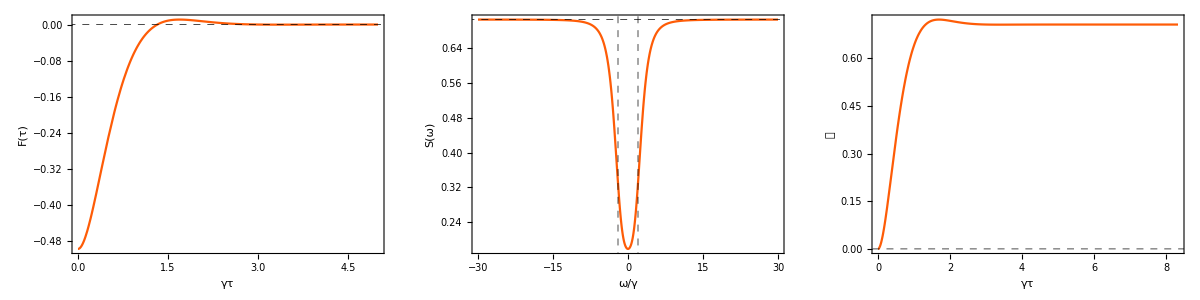
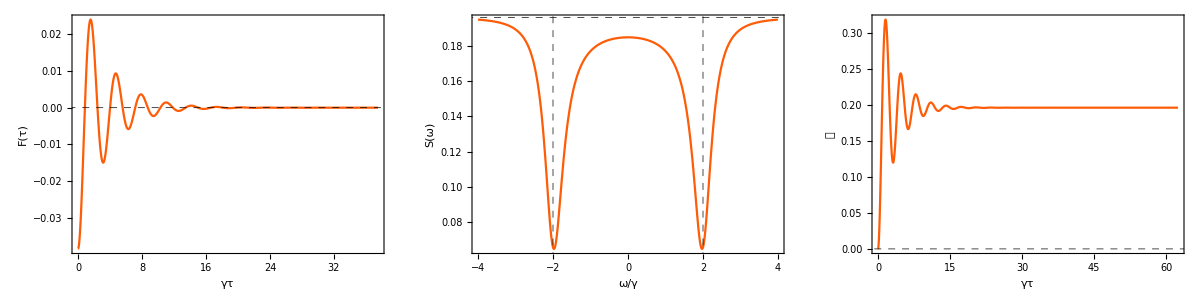
-Graphics-γ/Ω=3


-Graphics-γ/Ω=0.4

```mathematica
γγ = 3.0;
ΔΔ = 0.0;
plt1=Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-10 γγ,10γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,25 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}];
γγ = 0.4;
ΔΔ = 0.0;
plt2=Grid[{{
Plot[Evaluate[Re@Fτ/.{γ->γγ,Δ->ΔΔ}],{τ,0,15/ γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","F(τ)"},ImageSize->300],
Plot[S/.{γ->γγ,Δ->ΔΔ},{ω,-10 γγ,10γγ},GridLines->Evaluate[{{-√(4+Δ^2),√(4+Δ^2)},{(4 γ)/(8+γ^2+4 Δ^2)}}/.{γ->γγ,Δ->ΔΔ}],GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"ω/γ","S(ω)"},ImageSize->300],
Plot[𝒲/.{γ->γγ,Δ->ΔΔ},{t,0,25 /γγ},GridLines->{None,{0}},GridLinesStyle->Directive[Black, Dashed],PlotStyle->COLORLIST⟦2⟧,AspectRatio->1,FrameLabel->{"γτ","𝒲"},ImageSize->300]
}}];
Grid[{{Labeled[plt1,Style["γ/Ω=3",22,FontFamily->"Times"],Top]},{},{},{Labeled[plt2,Style["γ/Ω=0.4",22,FontFamily->"Times"],Top]}}]
```

```mathematica
ρt=Unvec@MatrixExp[ℒ t,Vec[Proj[2,2]]];
{sx,sy,sz} = {Tr[σx.ρt],Tr[σy.ρt],Tr[σz.ρt]};
Show[BlochSphere[],
ParametricPlot3D[{sx,sy,sz},{t,0,20},PlotStyle->Black,PlotRange->All],PlotRange->All]
```

-Graphics3D-

#### Example: homodyne spectrum of squeezing in a parametric amplifier

Based on chapter 7 of Walls & Milburn. 
Computes equations 7.61 & 7.62.

(there is a factor of 2 different, which I believe is related to the way they define the quadratures)

```mathematica
LoadBosonicOperators[nmax = 40];
ωs = range[-5,5,0.1]+0.02;
ϵ = 0.4;
γ = 2;
H = (ⅈ ϵ)/2 (a†.a†-a.a);
cop = √γ a;
ℒ = Liouvillian[H,{cop}];
ρ = SteadyState[ℒ];
```

```mathematica
Sx = FCSPowerSpectrum[ωs,ρ,ℒ,{a},1,"Diffusion"];
Sy = FCSPowerSpectrum[ωs,ρ,ℒ,{ⅈ a},1,"Diffusion"];
```

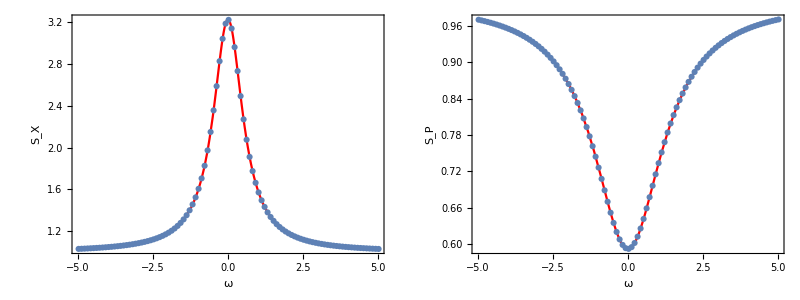

```mathematica
Grid@{{Show[
Plot[1+ (γ ϵ)/((γ/2-ϵ)^2+ω^2),{ω,-5,5},PlotStyle->Red],
ListLinePlot[Sx,Joined->False,PlotMarkers->Automatic],
FrameLabel->{"ω","S_X"}
],
Show[
Plot[1- (γ ϵ)/((γ/2+ϵ)^2+ω^2),{ω,-5,5},PlotStyle->Red],
ListLinePlot[Sy,Joined->False,PlotMarkers->Automatic],
FrameLabel->{"ω","S_P"}
]}}
```

#### Resonant qubit: g^(2) and S(ω)

Reproducing FIg. 1 of Mølmer’sSx =  Phys. Rev. A. 94 032103 (2016)

```mathematica
Clear[γ,Ω,Δ];
H = Ω/2 σx;
c = √γ σm;
ℒ = Liouvillian[H,{σm},{γ}];
ρ = AnalyticalSteadyState[ℒ]//mf;
```

(Ω^2/(γ^2+2 Ω^2) | -(ⅈ γ Ω)/(γ^2+2 Ω^2)
(ⅈ γ Ω)/(γ^2+2 Ω^2) | (γ^2+Ω^2)/(γ^2+2 Ω^2))

```mathematica
(* Jump current *)
FCSAverage[ρ,ℒ,{c},1]//cf
```

(γ Ω^2)/(γ^2+2 Ω^2)

```mathematica
(* Homodyne detection of Subscript[σ, x]*)
FCSAverage[ρ,ℒ,{c},1,"Diffusion"]//cf

(* Homodyne detection of Subscript[σ, y]*)
FCSAverage[ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Diffusion"]//cf
```

0

-(2 γ^(3/2) Ω)/(γ^2+2 Ω^2)

g^(2) function

```mathematica
g2=FCSg2[t,ρ,ℒ,c]//cf
```

(ⅇ^(-1/4 t (3 γ+√(γ^2-16 Ω^2))) (-3 (-1+ⅇ^(1/2 t √(γ^2-16 Ω^2))) γ-(1+ⅇ^(1/2 t √(γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 γ+√(γ^2-16 Ω^2)))) √(γ^2-16 Ω^2)))/(2 √(γ^2-16 Ω^2))

```mathematica
g2/.t->0
```

0

```mathematica
F = FCSTwoPointFunction[t,ρ,ℒ,c]//cf
J = FCSAverage[ρ,ℒ,c]//cf
```

-(ⅇ^(-(3 t γ)/4) γ^2 Ω^4 (√(γ^2-16 Ω^2) Cosh[1/4 t √(γ^2-16 Ω^2)]+3 γ Sinh[1/4 t √(γ^2-16 Ω^2)]))/(√(γ^2-16 Ω^2) (γ^2+2 Ω^2)^2)

(γ Ω^2)/(γ^2+2 Ω^2)

```mathematica
g2-(F/J^2+1)//cf
```

0

Two-point correlation function for homodyning σ_x or σ_y

```mathematica
Fx=FCSTwoPointFunction[t,ρ,ℒ,{c},{1},"Diffusion"]//cf
Fy=FCSTwoPointFunction[t,ρ,ℒ,{c ⅇ^(-ⅈ π/2)},{1},"Diffusion"]//cf
```

(2 ⅇ^(-(t γ)/2) γ Ω^2)/(γ^2+2 Ω^2)

-(2 ⅇ^(-(3 t γ)/4) γ Ω^2 ((γ^4-18 γ^2 Ω^2+32 Ω^4) Cosh[1/4 t √(γ^2-16 Ω^2)]+γ √(γ^2-16 Ω^2) (γ^2-10 Ω^2) Sinh[1/4 t √(γ^2-16 Ω^2)]))/((γ^2-16 Ω^2) (γ^2+2 Ω^2)^2)

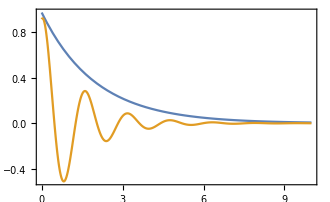

```mathematica
Plot[Evaluate[{Fx,Fy}/.{γ->1,Ω->4}],{t,0,10}]
```

```mathematica
Sx = FullSimplify[FCSPowerSpectrum[ω,ρ,ℒ,{c},1,"Diffusion"],γ>0]
Sy = FullSimplify[FCSPowerSpectrum[ω,ρ,ℒ,{c ⅇ^(-ⅈ π/2)},1,"Diffusion"],γ>0]
```

(γ^4+8 ω^2 Ω^2+2 γ^2 (2 ω^2+5 Ω^2))/((γ^2+4 ω^2) (γ^2+2 Ω^2))

(γ^6+γ^4 (5 ω^2-2 Ω^2)+8 (-ω^2 Ω+Ω^3)^2+γ^2 (4 ω^4-6 ω^2 Ω^2+44 Ω^4))/((γ^2+2 Ω^2) (γ^4+4 (ω^2-Ω^2)^2+γ^2 (5 ω^2+4 Ω^2)))

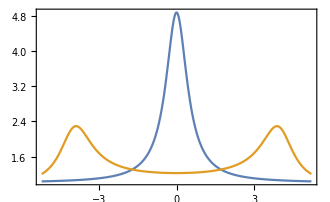

```mathematica
Plot[Evaluate[{Sx,Sy} /.{γ->1,Ω->4}],{ω,-5.2 ,5.2},PlotRange->{0.8,All}]
```

#### g^(2) function for a single qubit in a bad cavity

Based on Rice & Carmichael, IEEE JOURNAL OF QUANTUM ELECTRONICS, VOL . 24. NO . 7, JULY 1988

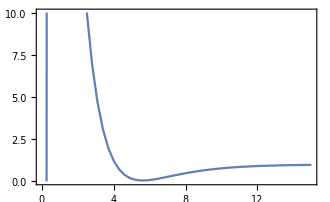

```mathematica
LoadBosonicOperators[nmax =16];
ϵ = 0.01;
g = 3;
κ = 25 ;
γ = 1/5 ;
H = ϵ kron[a+a†,σ0] + g (kron[a†,σm] + kron[a,σp]);
cops = {√(2κ)kron[a,σ0],√γ kron[𝕀,σm]};
ℒ=Liouvillian[H,cops];
ρ =AnalyticalSteadyState[ℒ];

ts = linspace[0.05,15,50];
g2=Re@FCSg2[ts,ρ,ℒ,√(2κ)kron[a,σ0]];
ListLinePlot[Re@g2,PlotRange->{0,10}]
```

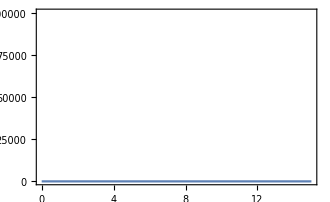

```mathematica
ListLinePlot[g2,PlotRange->{0,100000}]
```

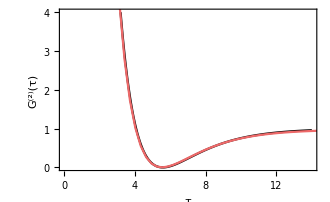

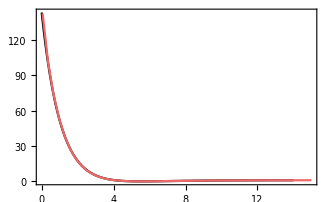

```mathematica
(* Comparison with Eq. (41) of Rice & Carmichael *)
g2RiceCarmichael[ϵ_,g_,κ_,γ_]:=Module[{𝒞 = g^2/(κ γ),ns = γ^2/(8 g^2),μ = 2κ/γ,Y = ϵ/(κ √ns),Ω,τp},
Ω = 1/4(1-(8 Y^2)/(1+2𝒞)^2)^(1/2);
τp = γ (1+2𝒞) τ;

(1-4 𝒞^2 ⅇ^(-τp/2))^2]

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,14},PlotRange->{0,4},PlotStyle->Black],
ListLinePlot[g2,PlotStyle->red],
FrameLabel->{"τ","G^(2)(τ)"}
]

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,14},PlotRange->{0,All},PlotStyle->Black],
ListLinePlot[g2,PlotStyle->red,PlotRange->All]]
```

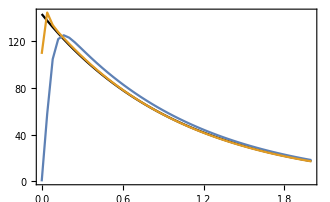

```mathematica
(* What happens if we approximate the bosonic mode by a qubit *)
(* Only differs at very short times *)
ϵ = 1/100.;
g = 3;
κ = 25 ;
γ = 1/5 ;
H = ϵ kron[σx,σ0] + g (kron[σp,σm] + kron[σm,σp]);
cops = {√(2κ)kron[σm,σ0],√γ kron[σ0,σm]};
ℒ=Liouvillian[H,cops];
(*ℒ=SetPrecision[ℒ,pres=30];*)
ρ =AnalyticalSteadyState[ℒ];
ts = linspace[0,2,50]//Rationalize;
g2q=FCSg2[ts,ρ,ℒ,√(2κ)kron[σm,σ0]];

H = ϵ kron[a+a†,σ0] + g (kron[a†,σm] + kron[a,σp]);
cops = {√(2κ)kron[a,σ0],√γ kron[𝕀,σm]};
ℒ=Liouvillian[H,cops];
ρ =AnalyticalSteadyState[ℒ];
g2b=FCSg2[ts,ρ,ℒ,√(2κ)kron[a,σ0]];

Show[
Plot[g2RiceCarmichael[ϵ,g,κ,γ],{τ,0,2},PlotRange->All,PlotStyle->Black],
ListLinePlot[{g2q,g2b}]
]
```

#### Homodyne spectrum for dephasing of a qubit

```mathematica
Clear[γ,Ω];
H = Ω/2 σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}]//cf;
ρ = AnalyticalSteadyState[ℒ]//mf;

(* Average homodyne current is zero *)
FCSAverage[ρ,ℒ,{c},1,"Homodyne"]//cf
```

(1/2 | 0
0 | 1/2)

0

```mathematica
(* But the spectrum is not *)
S = FCSPowerSpectrum[ω,ρ,ℒ,{c},1,"Diffusion"]//cf
F = FCSTwoPointFunction[t,ρ,ℒ,{c},1,"Diffusion"]//cf
```

1+(16 γ^2 Ω^2)/(4 γ^2 ω^2+(ω^2-Ω^2)^2)

4 ⅇ^(-t γ) γ (Cosh[t √(γ^2-Ω^2)]+(γ Sinh[t √(γ^2-Ω^2)])/(√((γ-Ω) (γ+Ω))))

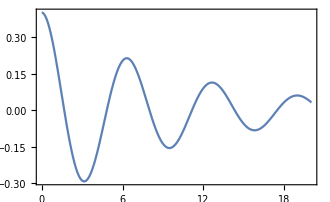
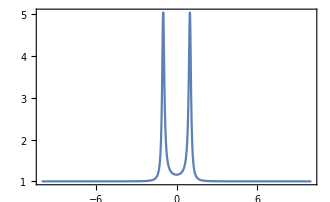

```mathematica
Row[
{Plot[F/.{Ω->1,γ->0.1},{t,0.01,20}],
Plot[S/.{Ω->1,γ->0.1},{ω,-10,10}]}
]
```

Compute the spectrum numerically using Homodyne solver

```mathematica
dt = 0.01;
tf = 1000;
Ω = 1.0;
γ = 0.1;
sim = QuantumDiffusion[{1,0},H,c,dt,tf]["J"];
```

0h : 0m : 2s

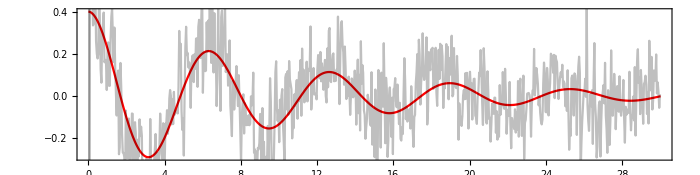

```mathematica
F=TwoPointCorrelation[butter[sim,150,dt],Round[30/dt],dt,4];
Show[
Plot[G2/.{Ω->1,γ->0.1},{t,0.01,30},PlotStyle->Red],
ListLinePlot[F,PlotStyle->Directive[Black,Opacity[0.25]]],
AspectRatio->1/4,
ImageSize->700
]
```

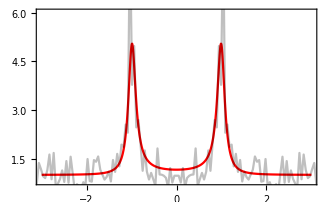

```mathematica
Show[
Plot[S/.{Ω->1,γ->0.1},{ω,-3,3},PlotStyle->Red,PlotRange->{{-3,3},{0.8,6}}],
ListLinePlot[PowerSpectrum[sim,dt,8],PlotStyle->Directive[Black,Opacity[0.25]],PlotRange->{{-3,3},All}]
]
```

## Quantum trajectories & stochastic processes

### Standard integrator for Markov Processes and Master equations

```mathematica
Clear[MarkovSimulate];
MarkovSimulate[QQ_,nmax_,i0_]:=Module[{Q},
Q=#/Total[QQ,1]&/@QQ;
(*Q=#/Total[QQ,1]&/@QQ;*)
First[Normal@RandomFunction[DiscreteMarkovProcess[i0,Qᵀ],{0,nmax-1}]][[All,2]]
]

MarkovSimulate[Q_,nmax_]:=MarkovSimulate[Q,nmax,Basis[Length@Q,1]]
```

```mathematica
Clear[MasterEquationSimulate];
MasterEquationSimulate[W_,Δt_,tf_,i0_]:=Module[{𝒲,Q,ts,nmax,δt,c},
𝒲 = W - DiagonalMatrix@Diagonal@W - DiagonalMatrix@Total@W;
Q = Eye[W] + Δt 𝒲; 
Q=#/Total[Q,1]&/@Q;
c = 0;
While[Min@Q<0,
δt = Δt/2;
Q = Eye[W] + δt 𝒲; 
Q=#/Total[Q,1]&/@Q;
c = c+1;
If[c>10,Abort[]];
Print["Δt halved to make the dynamics physical"];
];
ts = range[0,tf,Δt];
nmax = Length@ts;
{ts,MarkovSimulate[Q,nmax,i0]}ᵀ
]

MasterEquationSimulate[W_,Δt_,tf_]:= MasterEquationSimulate[W,Δt,tf,Basis[Length@W,1]]
```

#### Example usage

```mathematica
Q = ({{0.8, 0.3}, {0.2, 0.7}});
MarkovSimulate[Q,20,1]
MarkovSimulate[Q,20]
```

{1,1,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,1,1}

{1,1,1,2,2,2,1,1,1,2,2,2,1,1,1,1,1,1,1,1}

```mathematica
W = ({{0, 0.3}, {0.1, 0}});
MasterEquationSimulate[W,0.01,1,2]
```

{{0.,2},{0.01,2},{0.02,2},{0.03,2},{0.04,2},{0.05,2},{0.06,2},{0.07,2},{0.08,2},{0.09,2},{0.1,2},{0.11,2},{0.12,2},{0.13,2},{0.14,2},{0.15,2},{0.16,2},{0.17,2},{0.18,2},{0.19,2},{0.2,2},{0.21,2},{0.22,2},{0.23,2},{0.24,2},{0.25,2},{0.26,2},{0.27,2},{0.28,2},{0.29,2},{0.3,1},{0.31,1},{0.32,1},{0.33,1},{0.34,1},{0.35,1},{0.36,1},{0.37,1},{0.38,1},{0.39,1},{0.4,1},{0.41,1},{0.42,1},{0.43,1},{0.44,1},{0.45,1},{0.46,1},{0.47,1},{0.48,1},{0.49,1},{0.5,1},{0.51,1},{0.52,1},{0.53,1},{0.54,1},{0.55,1},{0.56,1},{0.57,1},{0.58,1},{0.59,1},{0.6,1},{0.61,1},{0.62,1},{0.63,1},{0.64,1},{0.65,1},{0.66,1},{0.67,1},{0.68,1},{0.69,1},{0.7,1},{0.71,1},{0.72,1},{0.73,1},{0.74,1},{0.75,1},{0.76,1},{0.77,1},{0.78,1},{0.79,1},{0.8,1},{0.81,1},{0.82,1},{0.83,1},{0.84,1},{0.85,1},{0.86,1},{0.87,1},{0.88,1},{0.89,1},{0.9,1},{0.91,1},{0.92,1},{0.93,1},{0.94,1},{0.95,1},{0.96,1},{0.97,1},{0.98,1},{0.99,1},{1.,1}}

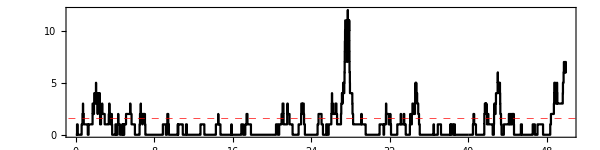

```mathematica
(* A quantum harmonic oscillator *)
Nb = 1.56;
γ = 1.0;
nmax = 20;
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1];
data = MasterEquationSimulate[W,0.005,5000,1];
data = {#[[1]],#[[2]]-1}&/@data;
ListLinePlot[data[[1;;10000]],PlotRange->All,AspectRatio->1/4,ImageSize->600,PlotStyle->Black,InterpolationOrder->0,
GridLines->{None,{Nb}},
GridLinesStyle->Directive[Red,Dashed,Thick]
]
```

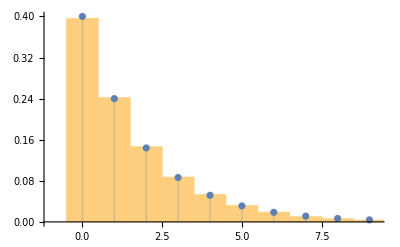

```mathematica
Show[
Histogram[data[[All,2]],{1},"PDF"],
ListPlot[Table[{k,PDF[GeometricDistribution[1/(1+Nb)],k]},{k,0,10}],Filling->Axis]
]
```

### Gillespie algorithm for classical stochastic processes

```mathematica
Gillespie[W_,x0_,njumps_]:=Module[{χ,r1,𝒲,x,λ,τ,tab},
χ = Range[1,Length@W];
r1 = RandomReal[{0,1},njumps];
𝒲 = W - DiagonalMatrix@Diagonal@W; (* Make sure the matrix has zero diagonals *)

x = x0;
τ = 0;
tab=Table[
λ = Total[𝒲⟦All,x⟧];
τ =τ -1/λ Log[1-r1⟦n⟧];
x = RandomChoice[Drop[𝒲⟦All,x⟧,{x}]/λ->Drop[χ,{x}]];

{τ,x},{n,njumps}];

Prepend[tab,{0,x0}]
];

GillespieMoment[result_,n_]:=(Differences[result⟦All,1⟧].(result⟦1;;-2,2⟧)^n)/result⟦-1,1⟧
```

#### Example: quantum harmonic oscillator

```mathematica
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1]//mf;
```

(0 | (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Nb γ | 0 | 2 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 Nb γ | 0 | 3 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 Nb γ | 0 | 4 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 Nb γ | 0 | 5 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 Nb γ | 0 | 6 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 Nb γ | 0 | 7 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 Nb γ | 0 | 8 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 Nb γ | 0 | 9 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 Nb γ | 0 | 10 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 Nb γ | 0 | 11 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 Nb γ | 0 | 12 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 Nb γ | 0 | 13 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 Nb γ | 0 | 14 (1+Nb) γ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 Nb γ | 0 | 15 (1+Nb) γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 Nb γ | 0 | 16 (1+Nb) γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 Nb γ | 0 | 17 (1+Nb) γ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 Nb γ | 0 | 18 (1+Nb) γ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 Nb γ | 0 | 19 (1+Nb) γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 Nb γ | 0 | 20 (1+Nb) γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 Nb γ | 0)

```mathematica
Clear[W];
Nb = 1.5;
γ = 1.0;
nmax = 50;
(*W = Table[KroneckerDelta[m,n+1] γ(Nb+1)(n+1)+KroneckerDelta[m,n-1] γ Nb n,{n,0,nmax},{m,0,nmax}]//mf;*)
W = DiagonalMatrix[Table[γ (Nb+1)(n+1),{n,0,nmax-1}],1] + DiagonalMatrix[Table[γ Nb n,{n,1,nmax}],-1];
result = {#⟦1⟧,#⟦2⟧-1}&/@Gillespie[W,10,550];
```

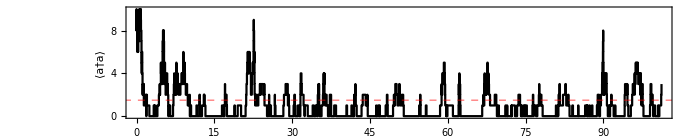

```mathematica
ListLinePlot[result,InterpolationOrder->0,
AspectRatio->1/5,
ImageSize->700,
PlotStyle->Black,
GridLines->{None,{Nb}},
GridLinesStyle->Directive[Red,Dashed,Thick],
FrameLabel->{"time","⟨a†a⟩"}
]
```

```mathematica
GillespieMoment[{#⟦1⟧,#⟦2⟧-1}&/@Gillespie[W,10,10^5],1]
```

1.49466

### Pauli master equation

Input: 
- p_up: vector (or scalar) of upward transition rates
- p_dw: vector (or scalar) of downward transition rates.

Syntax: 
- If p_(up(dw)) are vectors: PauliEquation[p_up,p_dw]
- If p_(up(dw)) are scalars: PauliEquation[d,p_up,p_dw] , where d is the dimension

```mathematica
Clear[PauliEquation];
PauliEquation[pup_?VectorQ,pdw_?VectorQ]:=Module[{W,d=Length@pup+1},
W = DiagonalMatrix[pup,-1] + DiagonalMatrix[pdw,1] - DiagonalMatrix[Append[pup,0]]-DiagonalMatrix[Prepend[pdw,0]]
]

PauliEquation[d_,pup_,pdw_]:=PauliEquation[ConstantArray[pup,{d-1}],ConstantArray[pdw,{d-1}]]
```

#### Example usage

```mathematica
(* Non-uniform rates *)
W=PauliEquation[Table[p[i],{i,5}],Table[q[i],{i,5}]]//mf;
```

(-p[1] | q[1] | 0 | 0 | 0 | 0
p[1] | -p[2]-q[1] | q[2] | 0 | 0 | 0
0 | p[2] | -p[3]-q[2] | q[3] | 0 | 0
0 | 0 | p[3] | -p[4]-q[3] | q[4] | 0
0 | 0 | 0 | p[4] | -p[5]-q[4] | q[5]
0 | 0 | 0 | 0 | p[5] | -q[5])

```mathematica
Table[Total[W⟦All,i⟧],{i,6}]
```

{0,0,0,0,0,0}

```mathematica
(* Uniform rates *)
W = PauliEquation[6,Subscript[p, up],Subscript[p, dw]]//mf;
```

(-p_up | p_dw | 0 | 0 | 0 | 0
p_up | -p_dw-p_up | p_dw | 0 | 0 | 0
0 | p_up | -p_dw-p_up | p_dw | 0 | 0
0 | 0 | p_up | -p_dw-p_up | p_dw | 0
0 | 0 | 0 | p_up | -p_dw-p_up | p_dw
0 | 0 | 0 | 0 | p_up | -p_dw)

```mathematica
Table[Total[W⟦All,i⟧],{i,6}]
```

{0,0,0,0,0,0}

### Auxiliary functions for quantum jump dynamics

#### JumpHighlight: highlighting quantum jumps in a plot

```mathematica
(* For plotting the quantum jumps *)
Clear[JumpHighlight];
JumpHighlight[jumpList_,times_:None,named_:True,thickness_:0.015,yi_:0,yf_:1]:=Module[{shift,ts,types,typ,jL,i,j,tab,names},
ts = If[times===None,Range[1,jumpList⟦-1,1⟧],times];
types = DeleteDuplicates[jumpList⟦All,2⟧];
shift = (ts⟦-1⟧-ts⟦1⟧)0.02;
names = Which[
named===True,types,
ListQ[named],named,
True,False];
Table[
typ = types⟦i⟧;
jL = Select[jumpList,#⟦2⟧==typ&];
tab={
(Rest@COLORLIST)⟦i⟧,Thickness[thickness],Opacity[0.4],
Table[Line[{
{ts⟦j⟦1⟧⟧,yi},
{ts⟦j⟦1⟧⟧,yf}}],{j,jL}]
};

If[Not[names===False] ,AppendTo[tab,Table[Text[Style[names⟦i⟧,(Rest@COLORLIST)⟦i⟧,Bold,Opacity[1]],{shift+ts⟦j⟦1⟧⟧,(*(yf-yi)0.7*)Rescale[0.7,{0,1},{yi,yf}]}],{j,jL}]]];
tab
,{i,Length@types}]
]
```

#### WTDfromJumps: Waiting time distribution from quantum jumps

```mathematica
(* "FromTo" refer to the jump channels. Defaul "All" picks WTD between any kind of jump *)
(* "FromTo = {i,j}" selects the WTD for jumps from i -> j, without being blind to any intermediate jumps. 
 i.e. i -> k -> j would not count *)
(* "From To = {i,j,{k1,k2,...}}" selects the WTD for jumps from i -> j, assuming one is blind to jumps in 
  channels {k1,k2,...} *)

Clear[WTDfromJumps];
WTDfromJumps[jumpList_,times_:None,FromTo_:All]:=Module[{Δt,exclude,jL2},
Δt = Which[
ArrayQ[times],times[[2]]-times[[1]],
NumberQ[times],times,
True,1
];

jL2 = Which[
FromTo===All,
Differences[jumpList[[All,1]]],

Length[FromTo]===2,
Differences[#[[All,1]]]&/@Select[Partition[jumpList,2,1],#[[1,2]]==FromTo[[1]] && #[[2,2]]==FromTo[[2]]&]//Flatten,

Length[FromTo]===3,
(exclude = Select[jumpList,Not@MemberQ[FromTo[[3]],#[[2]]]&];
Differences[#[[All,1]]]&/@Select[Partition[exclude,2,1],#[[1,2]]==FromTo[[1]] && #[[2,2]]==FromTo[[2]]&]//Flatten
)
];

jL2 Δt

]
```

#### IntegratedCurrentfromJumps: computes the integrated current (defined by weights ν) from the jumpList

```mathematica
(* Let k = 1,2,3,... denote the jump channels. *)
(* A current is defined by a set of weights Subscript[ν, k] for each channel. *)
(* Let Subscript[dN, k] = 1 when a jump in channel k occurs *)
(* This function computes the integrated current N(t) = ∑_k ∫_0^t dt' Subscript[ν, k] Subscript[dN, k](t') *)

(* Input ν must be a list of weights with the same length as the number of channels in jumpList *)

(* ν = {1,1,...} yields the dynamical activity. *)
(* ν = {1,-1,0,0,...} might yield some particle current (depending on the dissipators) *)
Clear[IntegratedCurrentfromJumps];
IntegratedCurrentfromJumps[ν_,jumpList_,step_:100,times_:None]:=Module[{JLtyped,max,Δt,newTimes,intCurrent},
Δt = Which[
ArrayQ[times],times[[2]]-times[[1]],
NumberQ[times],times,
True,1
];
JLtyped = #[[All,1]]&/@GatherBy[jumpList,Last];
max = Max[jumpList[[All,1]]];

newTimes =Δt Most@Range[0,max,step];
intCurrent=Total@Table[
ν[[k]]Accumulate@BinCounts[JLtyped[[k]],{0,max,step}]
,{k,Length@ν}];
Transpose[{newTimes,intCurrent}]
]
```

### Quantum Jump unravelling

```mathematica
Clear[QuantumJumpUnravelling];
QuantumJumpUnravelling[H_,cops_,ψ0_,ts_,seed_:0,onlyJumps_:False]:=Module[{r,Δt,npts,ncops = Length@cops,He,ψ,𝒰,states,jump,jumpList,dyna,n,ss},
If[seed!=0,SeedRandom[seed]];
Δt = ts⟦2⟧-ts⟦1⟧;
npts=Length[ts]-1;
r = RandomReal[{0,1},npts];
He = H - ⅈ/2 Sum[c†.c,{c,cops}];
𝒰 = Eye[Length@He]-ⅈ He Δt-(He.He Δt^2)/2+1/6 ⅈ He.He.He Δt^3+(He.He.He.He Δt^4)/24; 
ψ = N@ψ0;
jumpList = {};
states = {};
n=1;
While[n<npts,
ss=NestWhileList[𝒰.#&,ψ,Norm[#]^2>r⟦n⟧&,1,npts-n+1];
If[onlyJumps===False,AppendTo[states,Normalize/@ss]];
ψ = ss⟦-1⟧;
n = n + Length@ss;
jump=If[ncops==1,1,RandomChoice[Table[Re[ψ*.c†.c.ψ],{c,cops}]->Range[1,ncops]]];
If[n<=npts,AppendTo[jumpList,{n-1, jump}]];
ψ = cops⟦jump⟧.ss⟦-1⟧;
ψ = ψ/Norm[ψ];

{states}];

If[onlyJumps===False,{Flatten[states,1],jumpList},jumpList]

]
```

```mathematica
Clear[QuantumJumpUnravellingMixedStates];
QuantumJumpUnravellingMixedStates[H_,cops_,sops_,ρ0_,ts_,seed_:0,onlyJumps_:False]:=Module[{r,Δt,npts,ncops = Length@cops,He,ρ,𝒱,states,jump,jumpList,dyna,n,ss,ℒ,𝒥,ℒ0},
If[seed!=0,SeedRandom[seed]];
Δt = ts⟦2⟧-ts⟦1⟧;
npts=Length[ts]-1;
r = RandomReal[{0,1},npts];

ℒ = Liouvillian[H,Join[cops,sops]];
𝒥 = Table[JumpOp[c],{c,cops}];
ℒ0 = ℒ-Total@𝒥;
𝒱 =NEye[ℒ0]+ ℒ0 Δt+(ℒ0.ℒ0 Δt^2)/2+1/6  ℒ0.ℒ0.ℒ0 Δt^3+(ℒ0.ℒ0.ℒ0.ℒ0 Δt^4)/24; 
ρ = N@Normal@Vec@ρ0;
jumpList = {};
states = {};
n=1;

While[n<npts,
ss=NestWhileList[𝒱.#&,ρ,UnTr[#]>r⟦n⟧&,1,npts-n+1];
If[onlyJumps===False,AppendTo[states,#/UnTr[#]&/@ss]];
ρ = ss⟦-1⟧;
n = n + Length@ss;
jump=If[ncops==1,1,RandomChoice[Table[Re@UnTr[j.ρ],{j,𝒥}]->Range[1,ncops]]];
If[n<=npts,AppendTo[jumpList,{n-1, jump}]];
ρ = 𝒥⟦jump⟧.ss⟦-1⟧;
ρ = ρ/UnTr[ρ];

{states}];

If[onlyJumps===False,{Unvec/@Flatten[states,1],jumpList},jumpList]

]
```

#### Example usage

```mathematica
H=1/2(σz + 0.5 σx);
cops = {0.5σm,0.5σp};
ψ0 = {1,1}/√2;
ts = Range[0,30.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,ψ0,ts,3];
jumpList
```

{{2950,1},{9271,2},{15176,1},{16905,2},{22762,1},{27355,2},{28276,1}}

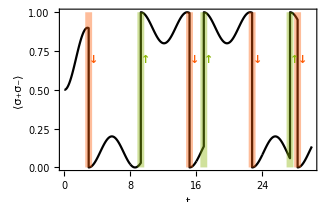

```mathematica
ListLinePlot[{ts,Abs[ψ⟦All,1⟧]^2}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
FrameLabel->{Style["t",Italic],"⟨σ_+σ_-⟩"}
]
```

A pretty drawing:

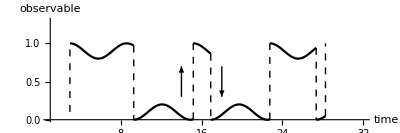

```mathematica
ups = Select[jumpList,#⟦2⟧==1&];
dws = Select[jumpList,#⟦2⟧==2&];
ListLinePlot[Table[{ts⟦jumpList⟦j,1⟧;;jumpList⟦j+1,1⟧-1⟧,Abs[ψ⟦jumpList⟦j,1⟧;;jumpList⟦j+1,1⟧-1,2⟧]^2}ᵀ,{j,Length@jumpList-1}],
PlotStyle->Black,
Epilog->{
Black,Dashed,
Table[Line[{
{ts⟦ups⟦j,1⟧⟧,Abs[ψ⟦ups⟦j,1⟧-1,2⟧]^2},
{ts⟦ups⟦j,1⟧⟧,1}}],{j,Length@ups}],
Table[Line[{
{ts⟦dws⟦j,1⟧⟧,Abs[ψ⟦dws⟦j,1⟧-1,2⟧]^2},
{ts⟦dws⟦j,1⟧⟧,0}}],{j,Length@dws}]
},
AspectRatio->1/3,
ImageSize->400,
AxesLabel->{"time","observable"},
Ticks->None,
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.05],Black],
PlotRange->{{1,32},{0,1.3}},
Prolog->{
Arrow[{{14,0.3},{14,0.7}}],
Arrow[{{18,0.7},{18,0.3}}]
}

]
```

#### Ex: Incoherent qubit (“single electron transistor”)

```mathematica
H=σz;
γ = 1;
fL = 0.3;
fR = 0.4;
cops = {√(γ(1-fL))σm,√(γ fL)σp,√(γ(1-fR))σm,√(γ fR)σp};
ψ0 = {1,0};
ts = Range[0,10.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,ψ0,ts,2];
jumpList
```

{{253,1},{416,4},{532,3},{1101,2},{2461,1},{3125,2},{3593,1},{5077,4},{5697,3},{6342,4},{6985,3},{8149,4},{8572,1}}

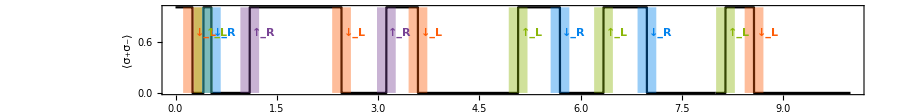

```mathematica
ListLinePlot[{ts,Abs[ψ⟦All,1⟧]^2}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓_L","↑_L","↓_R","↑_R"}],
FrameLabel->{Style["t",Italic],"⟨σ_+σ_-⟩"},
PlotRange->{-0.1,1.1},
AspectRatio->1/8,
ImageSize->900
]
```

Particle charge (= accumulated particle current up to time t)

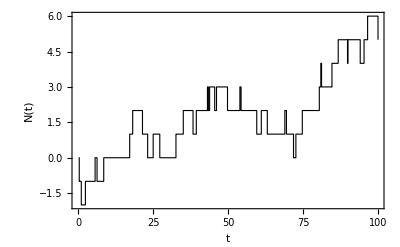

```mathematica
ts = Range[0,100.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,ψ0,ts,2];

charge={ts⟦jumpList⟦All,1⟧⟧,Accumulate[jumpList⟦All,2⟧/.{1->1,2->-1,3->0,4->0}]}//Transpose;
ListLinePlot[charge,
InterpolationOrder->0,
PlotStyle->Directive[Black,Thickness[0.002](*,Dotted*)],
FrameLabel->{Style["t",Italic],Style["N(t)",Italic]},
ImageSize->{Automatic,200}
]
```

#### Ex: Zeno effect in a 3-level system

```mathematica
LoadArbitrarySpinMatrices[1,"a"]
ψ0 = Basis[3,1];
ρ0 = out[ψ0,ψ0];
κ = 15.0;
cops = {√κ Proj[3,3,3]};
ℒ = Liouvillian[Sx,cops];

ts = Range[0,tf=30,0.005];

Clear[res];
Do[
res[i] = Table[{t,Tr[Proj[3,i,i].Unvec@MatrixExp[ℒ t,Vec[ρ0]]]},{t,0,tf,0.1}]//Chop;
,{i,1,3}]
```

Matrices loaded: S0 (=1), Sx, Sy, Sz, Sp, Sm

```mathematica
rasta@ListLinePlot[{res[1],res[2],res[3]},PlotRange->All]
```

-Graphics-

```mathematica
ψs=QuantumJumpUnravelling[Sx,cops,ψ0,ts,1]⟦1⟧;
Do[
res2[i] = Table[expect[Proj[3,i,i], ψs⟦n⟧],{n,1,Length@ψs}]//Chop;
,{i,1,3}]
```

```mathematica
rasta@ListLinePlot[{res2[1],res2[2],res2[3]},PlotRange->{0,1.1},DataRange->{0,tf}]
```

-Graphics-

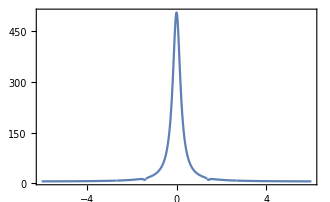

```mathematica
S=FCSPowerSpectrumLinearSys[{ω},Eye[3]/3,ℒ,cops]⟦1,2⟧;
Plot[S,{ω,-6,6}]
```

#### Ex: 2 qubits connected to a single bath

Two coupled qubits. But only the first is coupled to a bath.

```mathematica
LoadSpinChainMatrices[2];
H = sp[1].sm[2]+sm[1].sp[2] (* Exchange interaction *);
cops = {sm[1],sp[1]} (* Baths only in qubit 1 *);
ts = Range[0,7.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,{1,0,0,0},ts,4];
jumpList
```

{{1169,1},{1455,2},{2770,1},{3744,2},{3925,1},{5694,1},{6719,2}}

```mathematica
(* Reduced density matrices *)
ρ1 = Table[PTr[out[ψ⟦i⟧,ψ⟦i⟧],{2}],{i,Length@ψ}];
ρ2 = Table[PTr[out[ψ⟦i⟧,ψ⟦i⟧],{1}],{i,Length@ψ}];
```

```mathematica
entanglement = Table[vonNeumann[ρ],{ρ,ρ1}];
occupation = Table[2 Abs[ϕ⟦1⟧]^2+Abs[ϕ⟦2⟧]^2+Abs[ϕ⟦3⟧]^2,{ϕ,ψ}];
```

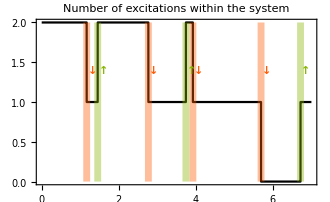
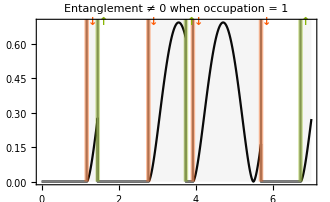

```mathematica
sel = {ts,Round[occupation]/.{2->0}}ᵀ;
Row@{ListLinePlot[{ts,occupation}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"},0.015,0,2],
PlotLabel->Style["Number of excitations within the system",Black,14]
],
Show[ListLinePlot[{ts,entanglement}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"},0.01],
PlotLabel->Style["Entanglement ≠ 0 when occupation = 1",14,Black]
],
ListLinePlot[sel,Filling->Axis,PlotStyle->Gray,FillingStyle->Opacity[0.08]]
]}
```

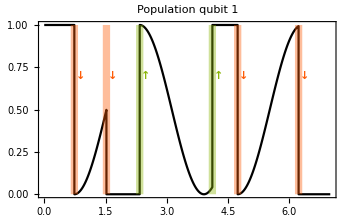
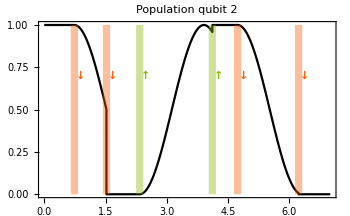

```mathematica
{ListLinePlot[{ts,ρ1⟦All,1,1⟧}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
ImageSize->350,
PlotLabel->"Population qubit 1"
],
ListLinePlot[{ts,ρ2⟦All,1,1⟧}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
ImageSize->350,
PlotLabel->"Population qubit 2"
]}
```

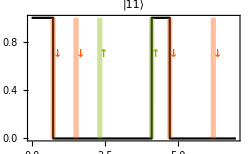
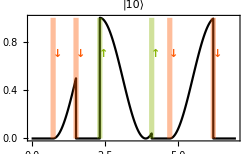
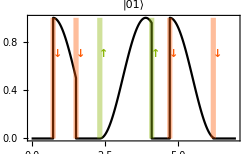
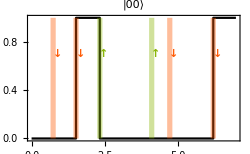

```mathematica
states = {"|11⟩","|10⟩","|01⟩","|00⟩"};
Row@Table[ListLinePlot[{ts,Abs[ψ⟦All,i⟧]^2}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
PlotLabel->states⟦i⟧,
ImageSize->250
],{i,4}]
```

#### Waiting time distributions from quantum jumps

Same model as “2 qubits connected to a single bath”

```mathematica
LoadSpinChainMatrices[2];
H = sp[1].sm[2]+sm[1].sp[2] (* Exchange interaction *);
cops = {sm[1],sp[1]} (* Baths only in qubit 1 *);
ts = Range[0,5000,0.001];
jumpList=QuantumJumpUnravelling[H,cops,{1,0,0,0},ts,4,True];
ℒ = Liouvillian[H,cops];
```

Waiting time distribution between any jump

```mathematica
(* Exact WTD *)
𝒥 = JumpOp[sm[1]] + JumpOp[sp[1]];
ℒ0 = ℒ-𝒥;
WTDexact = Table[{t,WaitingTimeDistribution[t,ℒ0,𝒥,𝒥]},{t,0,5,0.1}];
```

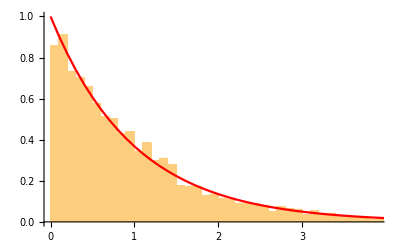

```mathematica
Show[
Histogram[WTDfromJumps[jumpList,ts],{0.1},"PDF"],
ListLinePlot[WTDexact,PlotStyle->Red]
]
```

WTD  between jumps of channel 1 (sm[1]), assuming one is blind to channel 2 (sp[1])

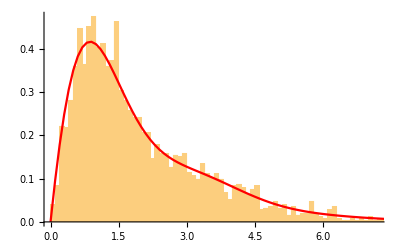

```mathematica
𝒥 = JumpOp[sm[1]];
ℒ0 = ℒ-𝒥;
WTDexact = Table[{t,WaitingTimeDistribution[t,ℒ0,𝒥,𝒥]},{t,0,10,0.1}];
Show[
Histogram[WTDfromJumps[jumpList,ts,{1,1,{2}}],{0.1},"PDF"],
ListLinePlot[WTDexact,PlotStyle->Red]
]
```

WTD between jumps of channel 1 (sm[1]),  not blind to channel 2 (sp[1])

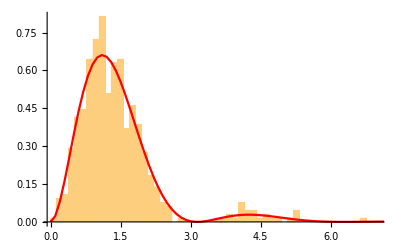

```mathematica
𝒥 = JumpOp[sm[1]];
ℒ0 = ℒ-𝒥-JumpOp[sp[1]];
WTDexact = Table[{t,WaitingTimeDistribution[t,ℒ0,𝒥,𝒥]},{t,0,10,0.1}];
(* normalize: *) WTDexact={WTDexact[[All,1]],WTDexact[[All,2]]/(Total[WTDexact[[All,2]]] 0.1)}ᵀ;
Show[
Histogram[WTDfromJumps[jumpList,ts,{1,1}],{0.13},"PDF"],
ListLinePlot[WTDexact,PlotStyle->Red],
PlotRange->{{0,7},All}
]
```

#### Dynamical activity & particle current

```mathematica
LoadSpinChainMatrices[2];
H = sp[1].sm[2]+sm[1].sp[2] (* Exchange interaction *);
cops = {√0.6 sm[1],sp[1]} (* Baths only in qubit 1 *);
ts = Range[0,150,0.001];
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
jumpLists=Table[
QuantumJumpUnravelling[H,cops,{1,0,0,0},ts,seed,True],{seed,1,10}];
```

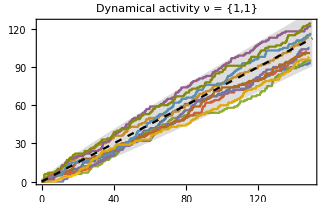

```mathematica
mean=FCSAverage[ρ,ℒ,cops,{1,1}];
noise = FCSDiffusionMatrix[ρ,ℒ,cops,{1,1}];
Show[
ListLinePlot[Table[IntegratedCurrentfromJumps[{1,1},jL,100,ts],{jL,jumpLists}],
PlotLabel->"Dynamical activity ν = {1,1}"
],
Plot[{mean t,mean t + 2 √(noise t),mean t - 2 √(noise t)},{t,0,150},Filling->{2->{3}},PlotStyle->{Directive[Black,Dashed],Directive[Lighter@Black,Opacity[0]],Opacity[0]}]
]
```

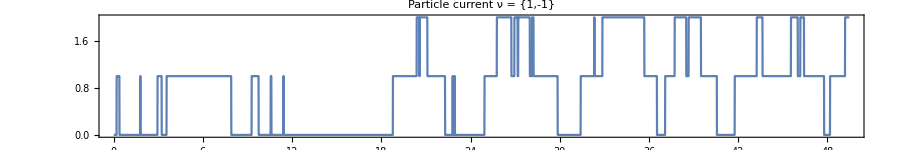

```mathematica
ListLinePlot[Table[IntegratedCurrentfromJumps[{1,-1},jL,10,ts],{jL,jumpLists[[{1}]]}],
PlotLabel->"Particle current ν = {1,-1}",
AspectRatio->1/6,
ImageSize->900
]
```

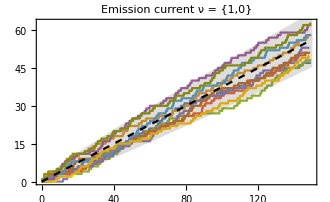

```mathematica
mean=FCSAverage[ρ,ℒ,cops,{1,0}];
noise = FCSDiffusionMatrix[ρ,ℒ,cops,{1,0}];
Show[
ListLinePlot[Table[IntegratedCurrentfromJumps[{1,0},jL,100,ts],{jL,jumpLists}],
PlotLabel->"Emission current ν = {1,0}"
],
Plot[{mean t,mean t + 2 √(noise t),mean t - 2 √(noise t)},{t,0,150},Filling->{2->{3}},PlotStyle->{Directive[Black,Dashed],Directive[Lighter@Black,Opacity[0]],Opacity[0]}]
]
```

### Quantum Gillespie algorithm for jump unravelling

```mathematica
Clear[QuantumJumpGillespie];
QuantumJumpGillespie[H_,M_,ψ0_,ts_,njumps_,seed_:0,onlyJumps_:True]:=Module[{v,He,𝒥,Qs,ψ,τ,Ps,norm,V,tr,T,weights,k,cr,tab},
If[seed!=0,SeedRandom[seed]];
𝒥 = Sum[c†.c,{c,M}];
He = H - ⅈ/2 𝒥;

tr = Range[1,Length@ts];
cr = Range[1,Length@M];
V = Table[MatrixExp[-ⅈ He t],{t,ts}];
Qs = Table[ v†.𝒥.v,{v,V}];
norm = Norm[Qs⟦-1⟧];

ψ = Normal@ψ0;
τ= 0;
tab=Table[
Ps = Table[ψ*.Q.ψ,{Q,Qs}]//Chop;
T = SillySample[tr,Ps];
τ = τ + ts⟦T⟧;
ψ = V⟦T⟧.ψ;
weights = Table[ψ*.c†.c.ψ,{c,M}]//Chop;
k=RandomChoice[weights->cr];
ψ = M⟦k⟧.ψ;
ψ = ψ/Norm[ψ];
{τ,k,ψ},{n,njumps}];

If[onlyJumps===True,tab[[All,{1,2}]],tab]

]
```

```mathematica
(* Assumes it is a renewal process *)
Clear[QuantumJumpGillespieRenewal];
QuantumJumpGillespieRenewal[H_,cops_,ψ0_,ts_,njumps_]:=Module[{He,𝒥,Qs,V,ψ,τ,Ps,norm,Vs,tr,δτr,weights,jump,cr,tab,δτrs},

𝒥 = Sum[c†.c,{c,cops}];
He = H - ⅈ/2 𝒥;

tr = Range[1,Length@ts];
cr = Range[1,Length@cops];
Vs = Table[MatrixExp[-ⅈ He t],{t,ts}];
Qs = Table[ V†.𝒥.V,{V,Vs}];
norm = Norm[Qs⟦-1⟧];

Do[
ψ = cops⟦c⟧.RandomReal[{0,1},Length@ψ0];
ψ = ψ/Norm[ψ];
Ps[c] = Table[ψ*.Q.ψ,{Q,Qs}]//Chop;
δτrs[c] = SillySample[tr,Ps[c],njumps];
,{c,cr}];

τ= 0;
jump = 1;
ψ = cops⟦jump⟧.RandomReal[{0,1},Length@ψ0];
ψ = ψ/Norm[ψ];
tab=Table[
(*δτr = SillySample[Ps[jump],tr];*)
δτr = δτrs[jump]⟦n⟧;
τ = τ + ts⟦δτr⟧;
ψ = Vs⟦δτr⟧.ψ;
weights = Table[ψ*.c†.c.ψ,{c,cops}]//Chop;

jump=RandomChoice[weights->cr];
ψ = cops⟦jump⟧.ψ;
ψ = ψ/Norm[ψ];
{τ,jump},{n,njumps}];

(*{tab,norm,He}*)
tab

]
```

```mathematica
(* UNTESTED *)
Clear[QuantumJumpGillespieMixedStates];
QuantumJumpGillespieMixedStates[H_,cops_,sops_,ρ0_,Δt_,tf_,njumps_,seed_:0,onlyJumps_:True]:=Module[{v,He,𝒥,Qs,ψ,τ,Ps,norm,V,tr,T,weights,k,cr,tab,ts,ℒ,ℒ0,y,ρ,𝒥s},
If[seed!=0,SeedRandom[seed]];

cr = Range[1,Length@cops];
ℒ = Liouvillian[H,Join[cops,sops]];
𝒥s = Table[JumpOp[c],{c,cops}];
𝒥 = Sum[JumpOp[c],{c,cops}];
ℒ0 = ℒ-𝒥;

ts = Range[0,tf,Δt];
tr = Range[1,Length@ts];
v = MatrixExp[ℒ0 Δt];
y = NEye[ℒ0];
V = Prepend[Table[y = v.y,{Length@ts-1}],NEye[ℒ0]];
Qs = Table[𝒥.v,{v,V}];

norm = Norm[Qs⟦-1⟧];

ρ = Vec@Normal@ρ0;
τ= 0;
tab=Table[
Ps = Table[UnTr[Q.ρ],{Q,Qs}]//Chop;
T = SillySample[tr,Ps];
τ = τ + ts⟦T⟧;
ρ = V⟦T⟧.ρ;
weights = Table[UnTr[j.ρ],{j,𝒥s}]//Chop;
k=RandomChoice[weights->cr];
ρ = 𝒥s⟦k⟧.ρ;
ρ = ρ/UnTr[ρ];
{τ,k,ρ},{n,njumps}];

{norm,If[onlyJumps===True,tab[[All,{1,2}]],tab]}

]
```

#### Example usage

```mathematica
H=(σz + σx);
cops = {σm};
ψ0 = {1,1}/√2;
ts = linspace[0,50.0,2000];
(*tab=QuantumJumpGillespie[H,cops,ψ0,ts,10^4];*)
tab=QuantumJumpGillespieRenewal[H,cops,ψ0,ts,10^4];
```

```mathematica
tab
```

Compare with the numerically exact waiting time distribution.
They only coincide in this case because this is a renewal process. 
In general, the stochastic method here is more general, since it allows for memory in the renewal.

```mathematica
ℒ = Liouvillian[H,cops];
ℒ1 = Sum[JumpOp[c],{c,cops}];
𝒲 = WaitingTimeDistribution[ts,ℒ-ℒ1,ℒ1,ℒ1,out[ψ0,ψ0]]//Chop;
```

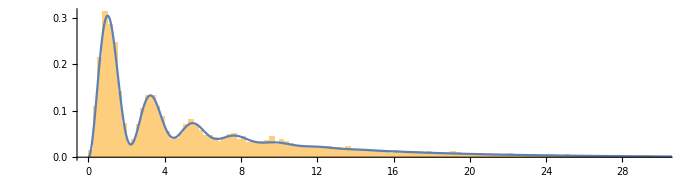

```mathematica
Show[
Histogram[Differences[tab⟦All,1⟧],{0,30,0.25},"PDF"],
ListLinePlot[𝒲,PlotRange->{{0,30},All},DataRange->{0,Last@ts}],
ImageSize->700,
AspectRatio->1/4]
```

### QuantumDiffusion: Stochastic master equation in the Diffusion unravelling

Based on Eqs. (4) and (7) of https://arxiv.org/pdf/1410.5345.pdf

```mathematica
Clear[QuantumDiffusion]
QuantumDiffusion[y0_,H_,ccops_,dt_,tf_,ssops_:None,seed_:0,func_:None,quiet_:False]:=Module[{n,sops,nsteps,S,ρ,ψ,dW,M,xave,dY,tab,𝕀,M0,x,c2,xs,c2s,dc,tr,cops,Υ,f,ff},
(* cops are monitored. sops are not *)
If[seed!=0,SeedRandom[seed]];
cops = If[Length@Dimensions[ccops]===2,{ccops},ccops];
dc = Length@cops;

sops = If[ssops===None,
{ConstantArray[0,{Length@H,Length@H}]},
If[Length@Dimensions[sops]===2,
{ssops},
ssops]];

nsteps = Round[tf/dt];
S= Association[];
If[func===None,f[ψ_]:=1,f[ψ_]:=func[ψ]];

S["dt"]=dt;
S["tf"]=tf;
S["nsteps"]=nsteps;
𝕀 = NEye[Length@H];
M0 = 𝕀 - (ⅈ H + 1/2 Sum[c†.c,{c,cops}] + 1/2 Sum[c†.c,{c,sops}])dt;
dW = RandomVariate[NormalDistribution[0,√dt],{nsteps,dc}];
xs = Table[c + c†,{c,cops}];
c2s = Table[c1.c2,{c1,cops},{c2,cops}];
tr = Sum[c.c,{c,cops}];

If[quiet==False,

If[MatrixQ[y0]||Not[sops===None],
(ρ = If[MatrixQ[y0],y0,out[y0,y0]];
tab=table[
ff=f[ρ];
xave = Table[Tr[x.ρ],{x,xs}];
dY = xave dt + dW⟦n⟧; 

Υ = dY.cops;
M = M0 + Υ + 1/2(Υ.Υ-dt tr);
ρ = M.ρ.M† + dt Sum[c.ρ.c†,{c,sops}];
ρ = ρ/Tr[ρ];
{ρ,dY,xave,ff},{n,nsteps}];
),
(ψ = y0;
tab=table[
ff=f[ψ];
xave = Table[ψ*.x.ψ,{x,xs}];
dY = xave dt + dW⟦n⟧; 

Υ = dY.cops;
M = M0 + Υ + 1/2(Υ.Υ-dt tr);
ψ = M.ψ//Normalize;
{ψ,dY,xave,ff},{n,nsteps}]
)],

If[MatrixQ[y0]||Not[sops===None],
(ρ = If[MatrixQ[y0],y0,out[y0,y0]];
tab=Table[
ff=f[ρ];
xave = Table[Tr[x.ρ],{x,xs}];
dY = xave dt + dW⟦n⟧; 

Υ = dY.cops;
M = M0 + Υ + 1/2(Υ.Υ-dt tr);
ρ = M.ρ.M† + dt Sum[c.ρ.c†,{c,sops}];
ρ = ρ/Tr[ρ];
{ρ,dY,xave,ff},{n,nsteps}];
),
(ψ = y0;
tab=Table[
ff=f[ψ];
xave = Table[ψ*.x.ψ,{x,xs}];
dY = xave dt + dW⟦n⟧; 

Υ = dY.cops;
M = M0 + Υ + 1/2(Υ.Υ-dt tr);
ψ = M.ψ//Normalize;
{ψ,dY,xave,ff},{n,nsteps}]
)]];

S["state"]=tab⟦All,1⟧//Chop;
S["I"]=If[Length@Dimensions@ccops==3,tab⟦All,2⟧,Flatten[tab⟦All,2⟧]]/dt//Chop;
S["xave"]=If[Length@Dimensions@ccops==3,tab⟦All,3⟧,Flatten[tab⟦All,3⟧]]//Chop;
S["f"]=If[Length@Dimensions@ccops==3,tab⟦All,4⟧,Flatten[tab⟦All,4⟧]]//Chop;
S
]
```

#### Example usage

```mathematica
(* Pure initial state *)
QuantumDiffusion[{1,0},σz,σm,0.1,1]
```

<|dt→0.1,tf→1,nsteps→10,state→{{0.952488-0.100262 ⅈ,0.287602},{0.957815-0.203905 ⅈ,0.198039+0.0423426 ⅈ},{0.936156-0.304664 ⅈ,0.158616+0.0750573 ⅈ},{0.879475-0.39223 ⅈ,0.263331+0.0577568 ⅈ},{0.848956-0.491035 ⅈ,0.0559803+0.18715 ⅈ},{0.791078-0.575893 ⅈ,0.158232+0.132309 ⅈ},{0.704273-0.635535 ⅈ,-0.0701125+0.308511 ⅈ},{0.585661-0.652089 ⅈ,-0.238155+0.418405 ⅈ},{0.467993-0.646057 ⅈ,-0.362132+0.482134 ⅈ},{0.405088-0.704187 ⅈ,-0.400265+0.424042 ⅈ}},J→{2.8685,-1.07701,-0.449861,1.13287,-2.33148,1.34555,-2.70623,-2.06257,-1.70866,0.745349},xave→{0,0.547874,0.362102,0.251243,0.417877,-0.088745,0.097956,-0.490896,-0.824631,-0.961922},f→{1,1,1,1,1,1,1,1,1,1}|>

#### Example: homodyne for dephasing

dρ/dt=-i [Ωσ_x,ρ] + γ D[σ_z]

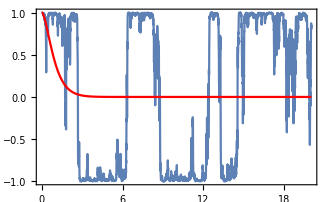

```mathematica
(* γ >> Ω: zeno-like dynamics *)
SeedRandom[1];
Ω = 1.0;
γ = 2.0;
H = Ω σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}];
dt = 0.005;
tf = 20;
ψ0 = {1,0};
szExact=Tr[σz.Unvec@MatrixExp[ℒ t,Vec@out[ψ0,ψ0]]]//Chop//Simplify;
sim = QuantumDiffusion[ψ0={1,0},H,c,dt,tf];

Show[
ListLinePlot[sim["xave"]/(2 √γ),PlotRange->All,DataRange->{dt,tf}],
Plot[Re@szExact,{t,0,20},PlotStyle->Red]]
```

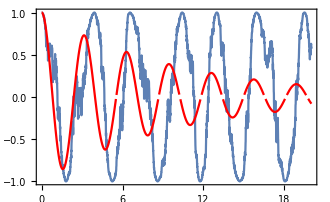

```mathematica
(* γ << Ω *)
SeedRandom[1];
Ω = 1.0;
γ = 0.1;
H = Ω σx;
c = √γ σz;
ℒ = Liouvillian[H,{c}];
dt = 0.005;
tf = 20;
szExact=Tr[σz.Unvec@MatrixExp[ℒ t,Vec@out[ψ0,ψ0]]]//Chop//Simplify;
sim = QuantumDiffusion[ψ0={1,0},H,c,dt,tf];

Show[
ListLinePlot[sim["xave"]/(2 √γ),PlotRange->All,DataRange->{dt,tf}],
Plot[szExact,{t,0,20},PlotStyle->Red]]
```

#### Example: diffusion for spontaneous emission

```mathematica
γ =0.2;
Δ = 1.;
H =Δ/2 σz+ σx;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ψ0 = 1/(√2){1,1(*ⅈ*)};
dt = 0.01;
tf = 20.0;

sim =table[QuantumDiffusion[ψ0,H,c,dt,tf]["xave"],{i,200}];
xave=√γ Tr[σx.Unvec[MatrixExp[ℒ t,Vec[out[ψ0,ψ0]]]]]//cf//Chop;
```

0h : 0m : 14s

```mathematica
rasta@Show[
Plot[xave,{t,0,tf},PlotStyle->Black],
ListLinePlot[Mean@sim,DataRange->{0,tf},PlotRange->All],
PlotRange->All
]
```

-Graphics-

#### Comparison with QuTIP

Comparing with the example given here: https://qutip.org/docs/latest/guide/dynamics/dynamics-stochastic.html

In the QuTIP example, if one uses a large dt (e.g. dt = 0.003), the simulations diverge. 
Instead, since algorithm implemented here always produces a valid POVM, if dt is not small enough here one will observe a phase lag in the dynamics. 

QuantumDiffusionPureState takes a similar amount of time as QuTIP.

```mathematica
LoadBosonicOperators[nmax = 20];
Δ = 5 2π;
κ = 2;
H = Δ a†.a;
c = √κ a;
intensity = 4.;
ψ0 = CoherentState[√intensity];

dt = 0.0012;
tf = 1.0;

ℒ = Liouvillian[H,{c}];
ρ0 = out[ψ0,ψ0];

(* Analytical (unconditional) Subscript[⟨x⟩, t] *)
ρ = Vec@ρ0;
ℰ = MatrixExp[ℒ dt];
ana = Table[
ρ=ℰ.ρ;
{t,1/(√κ)Tr[(c+c†).Unvec@ρ]},{t,dt,tf,dt}]//Chop;

PrettyTiming[
J=Mean@table[MovingAverage[QuantumDiffusion[ψ0,H,c,dt,tf]["J"],2],{i,800}]
];
```

0h : 5m : 11s

0h : 5m : 11s

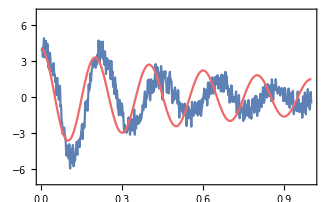

```mathematica
Show[
(*ListLinePlot[sim,Filling->Axis,DataRange->{dt,tf}],*)
ListLinePlot[J/√κ,DataRange->{dt,tf}],
ListLinePlot[ana,PlotStyle->red],
PlotRange->{-7,7}
]
```

# Corresponding QuTIP code

import numpy as np
import matplotlib.pyplot as plt
import qutip as qt

# parameters
DIM = 20             # Hilbert space dimension
DELTA = 5*2*np.pi    # cavity detuning
KAPPA = 2            # cavity decay rate
INTENSITY = 4        # intensity of initial state
NUMBER_OF_TRAJECTORIES = 500

# operators
a = qt.destroy(DIM)
x = a + a.dag()
H = DELTA*a.dag()* a

rho_0 = qt.coherent(DIM, np.sqrt(INTENSITY))
times = np.arange(0, 1, 0.0025)

stoc_solution = qt.smesolve(H, rho_0, times,
                            c_ops=[],
                            sc_ops=[np.sqrt(KAPPA) * a],
                            e_ops=[x],
                            ntraj=NUMBER_OF_TRAJECTORIES,
                            nsubsteps=2,
                            store_measurement=True,
                            dW_factors=[1],
                            method='homodyne')

fig, ax = plt.subplots()
ax.set_title('Stochastic Master Equation - Homodyne Detection')
ax.plot(times, np.array(stoc_solution.measurement).mean(axis=0)[:].real,
        'r', lw=2, label=r'$J_x$')
ax.plot(times, stoc_solution.expect[0], 'k', lw=2,
        label=r'$\langle x \rangle$')
ax.set_xlabel('Time')
ax.legend()

#### Reproducing Fig. 4.6 of Wiseman and Milburn

I think there is a typo in that figure. I think (a) is for Φ = π/2 and (b) is for Φ = 0, not the other way around.

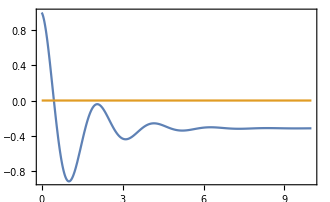

```mathematica
γ =1;
Δ = 0;
Ω = 3 γ;
H =Δ/2 σz+ Ω/2 σy;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ψ0 = 1/(√2){1,1};
ρ0 = out[ψ0,ψ0];
dt = 0.01;
tf = 10.0;

simX =QuantumDiffusion[ρ0,H,c ,dt,tf];
simY =QuantumDiffusion[ρ0,H,c ⅇ^(ⅈ π/2),dt,tf];

xave=√γ Tr[σx.Unvec[MatrixExp[ℒ t,Vec[ρ0]]]]//cf//Chop;
yave=√γ Tr[σy.Unvec[MatrixExp[ℒ t,Vec[ρ0]]]]//cf//Chop;
Plot[{xave,yave},{t,0,tf}]
```

```mathematica
PhiTheta[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["state"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["state"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["state"]}]
},
{Table[ArcTan[sx⟦i⟧,sy⟦i⟧],{i,Length@sx}],ArcCos[#]&/@sz}
]
```

```mathematica
BlochSpherePlot[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["state"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["state"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["state"]}]
},
Show[BlochSphere[],
ListLinePlot3D[{sx,sy,sz}ᵀ,PlotStyle->Black,PlotRange->All,AspectRatio->1],PlotRange->All,AspectRatio->1,ImageSize->270]
]
```

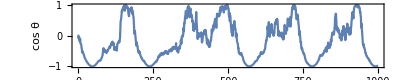

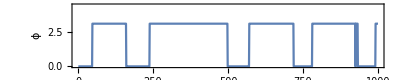

-Graphics3D-

```mathematica
{ϕx,θx}=PhiTheta[simX];
ListLinePlot[Cos@θx,AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","cos θ"},ImagePadding->{{60,10},{50,10}}]
ListLinePlot[ϕx,PlotRange->{0,4.5},AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","ϕ"},ImagePadding->{{60,10},{50,10}}]
BlochSpherePlot[simX]
```

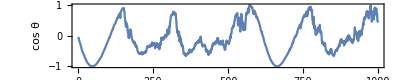

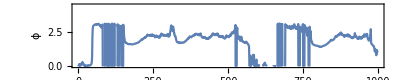

-Graphics3D-

```mathematica
{ϕy,θy}=PhiTheta[simY];
ListLinePlot[Cos@θy,AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","cos θ"},ImagePadding->{{60,10},{50,10}}]
ListLinePlot[ϕy,PlotRange->{0,4.5},AspectRatio->1/5,ImageSize->{Automatic,180},FrameLabel->{"γt","ϕ"},ImagePadding->{{60,10},{50,10}}]
BlochSpherePlot[simY]
```

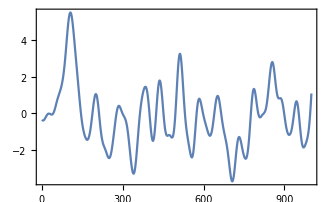
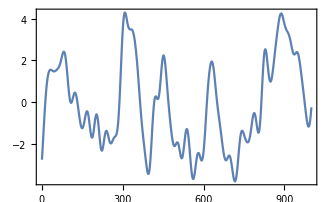

```mathematica
{ListLinePlot[LowpassFilter[simX,0.1]],ListLinePlot[LowpassFilter[simY,0.1]]}
```

```mathematica
timeseries = TimeSeries[{range[dt,tf,dt],sim}ᵀ]
```

TimeSeries[…]

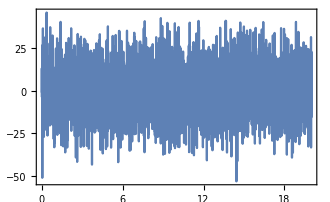

```mathematica
ListLinePlot[timeseries]
```

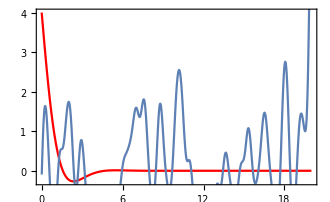

```mathematica
Show[Plot[4xave/√γ,{t,0,tf},PlotStyle->Red],
ListLinePlot[LowpassFilter[timeseries,5]]]
```

#### Two-point function & power spectrum from the stochastic homodyne current

```mathematica
Clear[ω,γ,Ω];
γ =0.7;
Δ = 0;
Ω = 5 γ;
H =Δ/2 σz+ Ω/2 σy;
c = √γ σm;
ℒ = Liouvillian[H,{c}];
ℒ = Liouvillian[H,{c}]//cf;
ρ = AnalyticalSteadyState[ℒ];
ψ0 = {1,0};
𝒮=FCSPowerSpectrum[{ω},ρ,ℒ,c,1,"Homodyne"]
ℱ = FCSTwoPointFunction[{τ},ρ,ℒ,c,1,"Homodyne"];
```

1.-((0.+0.686275 ⅈ) ((0.-0.546228 ⅈ)+4.74198 ω+(0.+15.0063 ⅈ) ω^2-20.7025 ω^3-(0.+11.2 ⅈ) ω^4+1. ω^5))/((-3.185-(0.+9.45 ⅈ) ω+1. ω^2) ((0.+4.37325 ⅈ) ω-12.8625 ω^2-(0.+1.4 ⅈ) ω^3+1. ω^4))+((0.+0.686275 ⅈ) ((0.+0.546228 ⅈ)+4.74198 ω-(0.+15.0063 ⅈ) ω^2-20.7025 ω^3+(0.+11.2 ⅈ) ω^4+1. ω^5))/((-3.185+(0.+9.45 ⅈ) ω+1. ω^2) ((0.-4.37325 ⅈ) ω-12.8625 ω^2+(0.+1.4 ⅈ) ω^3+1. ω^4))

```mathematica
dt = 0.01;
tf = 4000.0;
sim =QuantumDiffusion[ψ0,H,c ,dt,tf]["I"];
```

00:00:05TimeObject[{0,0,5},Instant]

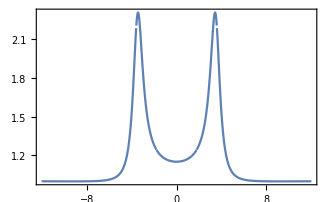
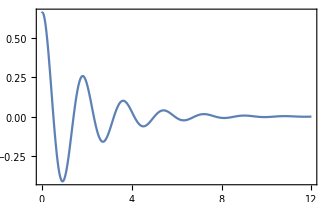

```mathematica
{Plot[𝒮,{ω,-12,12}],Plot[ℱ,{τ,0,12}]}
```

```mathematica
PrettyTiming[F=TwoPointCorrelation[sim,Round[8/dt],dt,3];]
```

0h : 0m : 1s

```mathematica
(* Butterworth filter smooths the 2-point function *)
PrettyTiming[Ffilt=TwoPointCorrelation[butter[sim,50,dt],Round[8/dt],dt,4];]
```

0h : 0m : 3s

```mathematica
rasta@Show[
ListLinePlot[{F,Ffilt},PlotStyle->{Directive[Black,Opacity[0.25]],Black}],
Plot[ℱ,{τ,0,9},PlotStyle->red]
]
```

-Graphics-

```mathematica
Grid@PartitionIn[Table[rasta@Show[
ListLinePlot[PowerSpectrum[sim,dt,av],PlotRange->{{-10,10},All}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick}],
PlotLabel->"Averaging = " <>ToString@av
],{av,{1,5,10,20,40,80}}],2]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* Power spectrum using Butterworth filter is no good, because it suppresses the shotnoise frequency *)
rasta@Show[
ListLinePlot[{PowerSpectrum[sim,dt,20],PowerSpectrum[butter[sim,10,dt],dt,10]},PlotRange->{{-10,10},All}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick}]
]
```

-Graphics-

```mathematica
(* More detailed simulations with 10x more points *)
```

```mathematica
sim2 =QuantumDiffusion[ρ,H,c ,dt,10tf]["I"];
```

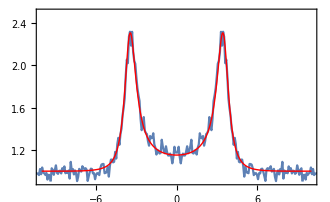

```mathematica
Show[
ListLinePlot[PowerSpectrum[sim2,dt,500],PlotRange->{{-10,10},{0.9,2.5}}],
Plot[𝒮,{ω,-10,10},PlotStyle->{Red,Thick},PlotRange->{{-10,10},{0.9,2.5}}]
]
```

### QuantumDiffusionBasic: a more elementary implementation of the quantum diffusion SME

```mathematica
Clear[QuantumDiffusionBasic];
QuantumDiffusionBasic[ρ0_,ℒ_,c_,dt_,tf_]:=Module[{ρ,x,ts,nsteps,𝒳,cd,dW,xave,dI,𝒥},
x = c + c†;
ts = Range[dt,tf,dt];
nsteps = Length@ts;
dW = RandomVariate[NormalDistribution[0,√dt],nsteps];
𝒳 = (Vec@x)†;
cd = c†;
ρ = Vec@ρ0;
𝒥 = JumpOp[c,"diffusion"];
Table[
xave = 𝒳.ρ;
ρ = ρ+ dt ℒ.ρ + dW[[n]] (𝒥.ρ-ρ xave);
{Unvec@ρ,{ts[[n]],xave},{ts[[n]],xave+dW[[n]]/dt}},
{n,2,Length@ts}
]ᵀ
]
```

### Quantum Diffusion Filtered Gaussian Measurements

```mathematica
Clear[QuantumDiffusionFilteredGaussianMeasurements];
QuantumDiffusionFilteredGaussianMeasurements[ρ0_,ℒ_,Y_,λ_,dt_,tf_,func_:None,γ_:∞]:=Module[{f,𝒱,ρ,nsteps,dW,ζ,𝒟,𝒞,λdt,χ,𝔻,yvals,S,ℰ,z,d,j,𝒴,ℱ,yave},
𝒱 = MatrixExp[ℒ dt];
ρ = Vec@ρ0;
nsteps = Round[tf/dt];
dW = RandomVariate[NormalDistribution[0,√dt],nsteps];
ζ = ConstantArray[0,nsteps];
𝒟 = ConstantArray[0,nsteps];
𝒴 = ConstantArray[0,nsteps];
ℱ = ConstantArray[0,nsteps];
𝒞 = ((2λ dt)/π)^(1/2);
λdt = λ dt;

If[γ ===∞,𝔻[ζ_,j_]:=ζ[[j]],
(
χ = Reverse@Chop@Table[γ dt ⅇ^(-k γ dt),{k,0,nsteps}];
𝔻[ζ_,j_]:=χ[[nsteps-j+1;;nsteps]] .ζ[[1;;j]];
)];

Which[
func===None,f[ρ_]:=1,
func===All,f[ρ_]:=ρ,
True,f[ρ_]:=func[ρ]
];

{yvals,S} = Eigsys[Y];
ℰ[z_,ρ_]:=With[{Λ=DiagonalMatrix@Table[ⅇ^(-λdt (z-y)^2),{y,yvals}]},
𝒞 S.Λ.S†.Unvec[ρ].S.Λ.S†//Vec];

Do[
ρ = 𝒱.ρ;
yave = Tr[Unvec[ρ].Y];
z =yave  + 1/(2 √λ)dW[[j]]/dt//Chop;
d = 𝔻[ζ,j];
ρ = ℰ[z,ρ];
ρ = ρ/UnTr[ρ];

ζ[[j]]=z;
𝒟[[j]]=d;
𝒴⟦j⟧=yave;
ℱ[[j]]=f[Unvec@ρ];
,{j,nsteps}
];
If[func===None,
{ζ,𝒟,𝒴},
{ζ,𝒟,𝒴,ℱ}
]
]
```

#### Example usage

```mathematica
Ω = 1.0;
λ = 0.2;
ℒ = Liouvillian[Ω σx,{0σz}];
ρ0 = Proj[2,1,1];
Y = σz;
QuantumDiffusionFilteredGaussianMeasurements[ρ0,ℒ,Y,λ,dt =0.005,tf = 30,2]
Row[{rasta@ListLinePlot[{ζ,𝒟}],rasta@ListLinePlot[𝒟,PlotRange->All,Joined->True]}]
```

## Kerr model & Coherent Quantum Absorber

### CQA solution

```mathematica
Clear[KerrPsi];
KerrPsi[nmax_,Δ_,G_,U_,κ_,ϵ_,κ2_,normalize_:True]:=Module[{α,n,tol=10^-14.,ψ},
ψ=Which[
Abs[G]<tol&&Abs[ϵ]<tol,Normal@Eye[nmax][[1]],
Abs[G]<tol&&Abs[ϵ]>tol,Prepend[Chop@RecurrenceTable[{
((U-ⅈ κ2) n -(2Δ + ⅈ κ) )√(n+1)α[n+1]+2 √2 ϵ α[n]==0,
α[0]==1
},α
,{n,1,nmax-1}],1],
Abs[G]>tol,Prepend[Chop@RecurrenceTable[{
((U-ⅈ κ2) n -(2Δ + ⅈ κ) )√(n+1)α[n+1]+2 G √n α[n-1]+2 √2 ϵ α[n]==0,
α[0]==1,α[-1]==0
},α
,{n,1,nmax-1}],1]
];
If[normalize===True,Normalize@ψ,ψ]
]
```

```mathematica
(* ⟨a⟩ *)
Clear[KerrA];
KerrA[nmax_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{ψ},
ψ = KerrPsi[nmax,Δ,G,U,κ,ϵ,κ2];
1/(√2)ψ[[1;;-2]]*.(√Range[1,nmax-1] ψ[[2;;-1]])//Chop
]
```

```mathematica
(* ⟨a†a⟩ *)
Clear[KerrAda];
KerrAda[nmax_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{ψ},
ψ = KerrPsi[nmax,Δ,G,U,κ,ϵ,κ2];
1/2 ψ*.(Range[0,nmax-1] ψ)//Chop
]
```

```mathematica
(* Auxiliary matrix necessary to compute ρ *)
Clear[KerrB];
KerrB[nmax_]:= N@Table[1/2^((k+j)/2)√Binomial[k+j,j],{k,0,nmax-1},{j,0,nmax-1}];
```

```mathematica
(* ρ steady-state *)
Clear[KerrRho];
KerrRho[B_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{nmax=Length@B,ψ,S,A},
ψ = KerrPsi[2nmax,Δ,G,U,κ,ϵ,κ2];
(*α = Join[ψ,ConstantArray[0,nmax]];*)
A = Table[ψ[[k+j-1]],{k,1,nmax},{j,1,nmax}];
S = A B;
S.S†
]
```

#### Example usage

Comparing with the full solution using vectorization

```mathematica
LoadBosonicOperators[nmax=50];
Δ = 2.0;
U = 1/3;
κ = 1.0;
G = 1.;
ϵ = 0.3;
H = - Δ a†.a + G/2(a†.a†+a.a)+U/2 a†.a†.a.a +ϵ (a+a†);
ℒ = Liouvillian[H,{√κ a}];
ρ = SteadyState[ℒ];
{Tr[a.ρ],Tr[a†.a.ρ]}//Chop
{KerrA[nmax,Δ,G,U,κ,ϵ,0],KerrAda[nmax,Δ,G,U,κ,ϵ,0]}
B = KerrB[nmax];
ρ2=KerrSteadyState[B,nmax,Δ,G,U,κ,ϵ,0];
ρ-ρ2//ChopCheck
```

{0.653098-2.6417 ⅈ,8.22252}

{0.653098-2.6417 ⅈ,8.22252}

{0}

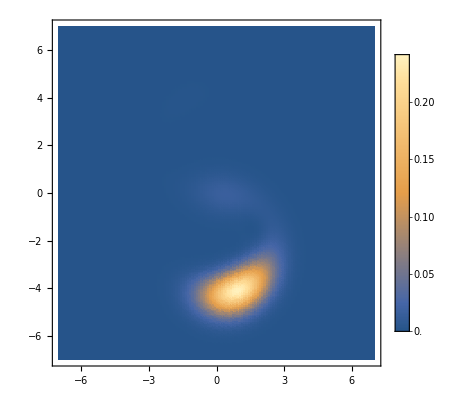

```mathematica
ListDensityPlot[WignerFunction[ρ2,7,0.1],
PlotRange->All,
PlotLegends->Automatic
]
```

#### Kerr Phase diagram

```mathematica
Δs = range[-3,5,0.08];
Gs = range[0.02,1.5,0.015];
Clear[Δ,G];
tab = Flatten[Table[{G,Δ,KerrAda[500,Δ,G,1/25,1.0,0,0]},{Δ,Δs},{G,Gs}],1];
```

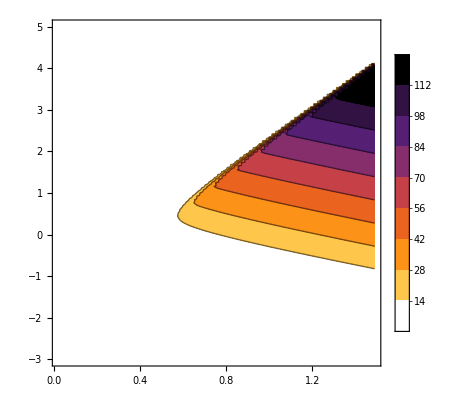

```mathematica
ListContourPlot[tab,
ColorFunction->colorGradient2["SunsetColors",-1],
PlotLegends->Automatic,PlotRange->All,
Contours->8
]
```

### ∂_θ ρ and Quantum Fisher Information using the CQA

```mathematica
(* Computes ∂_θ ψ where θ can be any of the parameters Δ,G,U,κ,ϵ,κ2 and ψ === ψ_+ is the CQA pure state *)
Clear[KerrPsiPrime]
KerrPsiPrime[para_,nmax_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{𝒟,tol=10^-14.,n,α,ψt,ϕt,ψ0,ϕ0,ϕ,Ψ,Φ,A,Ap,S,Sp,ψ,tmp,ψtt},
ψt = KerrPsi[nmax,Δ,G,U,κ,ϵ,κ2,False]; (*unnormalized solution; starting at 0*)
ψtt = ψt[[2;;-1]] (* Starting at Subscript[ψ, 1] *);
ψ0 = 1/(√(1+ψtt*.ψtt));
ψ = Normalize@ψt;

(* Here n = 0,1,2,... *);
Clear[𝒟];
Which[
para==="Δ",
Do[𝒟[n]=-2 √(n+1) ψt[[n+2]](*ψ[n+1]*),{n,0,nmax-2}],
para==="G",
Do[𝒟[n]=If[n===0,0,2 √n ψt[[n]]](*ψ[n-1]*),{n,0,nmax}],
para==="U",
Do[𝒟[n]= n √(n+1) ψt[[n+2]](*ψ[n+1]*),{n,0,nmax-2}],
para==="κ",
Do[𝒟[n]=-ⅈ √(n+1) ψt[[n+2]](*ψ[n+1]*),{n,0,nmax-2}],
para==="ϵ",
Do[𝒟[n]=2 √2 ψt[[n+1]](*ψ[n]*),{n,0,nmax-1}],
para==="κ2",
Do[𝒟[n]=-ⅈ n √(n+1) ψt[[n+2]](*ψ[n+1]*),{0,nmax-2}]
];

(* Starting at Subscript[ϕ̃, 1] *);
ϕt = Which[
Abs[G]<tol&&Abs[ϵ]<tol,0 Normal@Eye[nmax-1][[1]],
Abs[G]<tol&&Abs[ϵ]>tol,Chop@RecurrenceTable[{
((U-ⅈ κ2) n -(2Δ + ⅈ κ) )√(n+1)α[n+1]+2 √2 ϵ α[n]==-𝒟[n],
α[0]==0
},α
,{n,1,nmax-1}],
Abs[G]>tol,Chop@RecurrenceTable[{
((U-ⅈ κ2) n -(2Δ + ⅈ κ) )√(n+1)α[n+1]+2 G √n α[n-1]+2 √2 ϵ α[n]==-𝒟[n],
α[0]==0,α[-1]==0
},α
,{n,1,nmax-1}]
];

ϕ0 = -ψ0^3/2(ϕt*.ψtt+ψtt*.ϕt);
ϕ =Prepend[ ϕt ψ0 + ψtt ϕ0,ϕ0];

{ψ,ϕ}
]
```

```mathematica
(* Computes ∂_θ ρ where θ can be any of the parameters Δ,G,U,κ,ϵ,κ2 *)
Clear[KerrRhoPrime]
KerrRhoPrime[para_,B_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{nmax=Length@B,ψ,ϕ,A,Ap,S,Sp},
{ψ,ϕ} = KerrPsiPrime[para,2nmax,Δ,G,U,κ,ϵ,κ2];

A = Table[ψ[[k+j-1]],{k,1,nmax},{j,1,nmax}];
S = A B;

Ap = Table[ϕ[[k+j-1]],{k,1,nmax},{j,1,nmax}];
Sp = Ap B;

{S,S.S†,Sp.S†+S.Sp†}

]
```

```mathematica
(* Fisher information contained in the coherent quantum absorber *)
Clear[KerrCQAFisherInformation]
KerrCQAFisherInformation[para_,nmax_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{ψ,ϕ},
{ψ,ϕ} = KerrPsiPrime[para,nmax,Δ,G,U,κ,ϵ,κ2];
4 (ϕ*.ϕ + (ϕ*.ψ)^2)//Chop
]
```

```mathematica
(* Fisher information in the steady-state ρ of the CQA *)
Clear[KerrFisherInformation]
KerrFisherInformation[para_,B_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{nmax=Length@B,S,ρ,dρ},
{S,ρ,dρ} = KerrRhoPrime[para,B,Δ,G,U,κ,ϵ,κ2];
QuantumFisherInformation[ρ,dρ]
]
```

```mathematica
(* Symmetric logarithmic derivative of the steady-state ρ of the CQA *)
Clear[KerrSLD]
KerrSLD[para_,B_,Δ_,G_,U_,κ_,ϵ_,κ2_]:=Module[{nmax=Length@B,S,ρ,dρ,Λ},
{S,ρ,dρ} = KerrRhoPrime[para,B,Δ,G,U,κ,ϵ,κ2];
Λ=SymmetricLogarithmicDerivative[ρ,dρ];
{Λ,Tr[Λ.Λ.ρ]//Chop}
]
```

#### Example usage

```mathematica
B = KerrB[nmax=10];
dρ1=KerrRhoPrime["Δ",B,10,1,1,1,1,0,0]//mf;
```

(-0.0169279 | 0 | 0.113064-0.113295 ⅈ | 0 | -0.0601992+0.122279 ⅈ | 0 | 0.0158474-0.0450622 ⅈ | 0 | 0.0000168334+0.0104451 ⅈ | 0
0 | -0.160223 | 0 | 0.0674823+0.0547966 ⅈ | 0 | -0.0238363-0.0333659 ⅈ | 0 | 0.00920101+0.00495759 ⅈ | 0 | 0
0.113064+0.113295 ⅈ | 0 | -0.0129998 | 0 | -0.0267216+0.0435757 ⅈ | 0 | 0.00354068-0.0189512 ⅈ | 0 | 0.00230025+0.0012394 ⅈ | 0
0 | 0.0674823-0.0547966 ⅈ | 0 | 0.0950581 | 0 | -0.047879+0.0208569 ⅈ | 0 | 0.00682256-0.00610094 ⅈ | 0 | 0
-0.0601992-0.122279 ⅈ | 0 | -0.0267216-0.0435757 ⅈ | 0 | 0.0610564 | 0 | -0.0186524+0.0064109 ⅈ | 0 | 0.00120607-0.0010785 ⅈ | 0
0 | -0.0238363+0.0333659 ⅈ | 0 | -0.047879-0.0208569 ⅈ | 0 | 0.0256778 | 0 | -0.00450255+0.00109202 ⅈ | 0 | 0
0.0158474+0.0450622 ⅈ | 0 | 0.00354068+0.0189512 ⅈ | 0 | -0.0186524-0.0064109 ⅈ | 0 | 0.00703184 | 0 | -0.000649887+0.00015762 ⅈ | 0
0 | 0.00920101-0.00495759 ⅈ | 0 | 0.00682256+0.00610094 ⅈ | 0 | -0.00450255-0.00109202 ⅈ | 0 | 0.00117952 | 0 | 0
0.0000168334-0.0104451 ⅈ | 0 | 0.00230025-0.0012394 ⅈ | 0 | 0.00120607+0.0010785 ⅈ | 0 | -0.000649887-0.00015762 ⅈ | 0 | 0.00014744 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
δ = 10^-4;
ρp = KerrRho[B,10,1+δ,1,1,1,0,0];
ρm = KerrRho[B,10,1-δ,1,1,1,0,0];
dρ2 = (ρp-ρm)/(2δ);
dρ1-dρ2//Chop//mf;
```

(6.23768×10^-10 | 0 | -2.24449×10^-9-7.35749×10^-10 ⅈ | 0 | -7.02305×10^-10+5.0055×10^-10 ⅈ | 0 | 5.31312×10^-10-1.43408×10^-10 ⅈ | 0 | -1.55305×10^-10 | 0
0 | -1.04037×10^-9 | 0 | 1.14541×10^-10+3.86182×10^-10 ⅈ | 0 | 1.93593×10^-10-2.99637×10^-10 ⅈ | 0 | 0.+1.02245×10^-10 ⅈ | 0 | 0
-2.24449×10^-9+7.3561×10^-10 ⅈ | 0 | 0 | 0 | -1.83529×10^-10+1.23534×10^-10 ⅈ | 0 | 1.21042×10^-10 | 0 | 0 | 0
0 | 1.14541×10^-10-3.86252×10^-10 ⅈ | 0 | 4.58134×10^-10 | 0 | -1.52217×10^-10 | 0 | 0 | 0 | 0
-7.02305×10^-10-5.00515×10^-10 ⅈ | 0 | -1.83529×10^-10-1.23499×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.93593×10^-10+2.99672×10^-10 ⅈ | 0 | -1.52217×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
5.31312×10^-10+1.43408×10^-10 ⅈ | 0 | 1.21042×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-1.02245×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.55305×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Derivative with respect to G *)
B = KerrB[nmax=10];
dρ1=KerrRhoPrime["G",B,10,1,1,1,1,1,0];
δ = 10^-4;
ρp = KerrRho[B,10,1,1+δ,1,1,1,0];
ρm = KerrRho[B,10,1,1-δ,1,1,1,0];
dρ2 = (ρp-ρm)/(2δ);
dρ1-dρ2//Chop//Norm
```

1.33534×10^-9

```mathematica
(* Derivative with respect to U *)
B = KerrB[nmax=10];
dρ1=KerrRhoPrime["U",B,10,1,1,1,1,0,0];
δ = 10^-4;
ρp = KerrRho[B,10,1,1,1+δ,1,0,0];
ρm = KerrRho[B,10,1,1,1-δ,1,0,0];
dρ2 = (ρp-ρm)/(2δ);
dρ1-dρ2//Chop//Norm
```

8.64395×10^-9

```mathematica
(* Derivative with respect to κ *)
B = KerrB[nmax=10];
dρ1=KerrRhoPrime["κ",B,10,1,1,1,1,0,0];
δ = 10^-4;
ρp = KerrRho[B,10,1,1,1,1+δ,0,0];
ρm = KerrRho[B,10,1,1,1,1-δ,0,0];
dρ2 = (ρp-ρm)/(2δ);
dρ1-dρ2//Chop//Norm
```

1.23413×10^-9

```mathematica
(* Derivative with respect to ϵ *)
B = KerrB[nmax=10];
dρ1=KerrRhoPrime["ϵ",B,10,1,1,1,1,1,0];
δ = 10^-4;
ρp = KerrRho[B,10,1,1,1,1,1+δ,0];
ρm = KerrRho[B,10,1,1,1,1,1-δ,0];
dρ2 = (ρp-ρm)/(2δ);
dρ1-dρ2//Chop//Norm
```

1.86038×10^-9

#### Fisher information phase diagrams

Phase diagram of the Fisher information in ρ and the Fisher information in the CQA for the parameter Δ.
Calculations take a few minutes to run.

```mathematica
nmax = 50;
B = KerrB[nmax];
```

```mathematica
Δs = range[-3,5,0.08];
Gs = range[0.02,1.5,0.015];
Clear[Δ,G];
tab = Flatten[table[{G,Δ,KerrFisherInformation["Δ",B,Δ,G,1/3,1.0,0,0]},{Δ,Δs},{G,Gs}],1];
```

00:06:58TimeObject[{0,6,58},Instant]

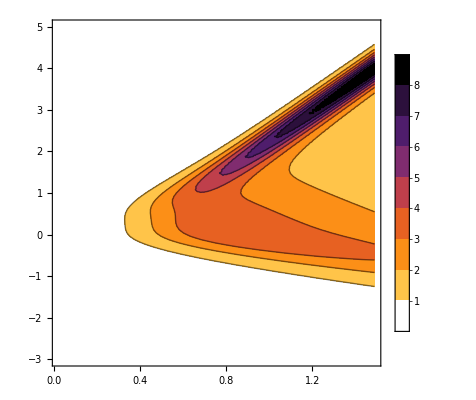

```mathematica
ListContourPlot[tab,
ColorFunction->colorGradient2["SunsetColors",-1],
PlotLegends->Automatic,PlotRange->All,
Contours->8
]
```

```mathematica
Δs = range[-3,5,0.08];
Gs = range[0.02,1.5,0.015];
Clear[Δ,G];
tab2 = Flatten[table[{G,Δ,KerrCQAFisherInformation["Δ",nmax,Δ,G,1/3,1.0,0,0]},{Δ,Δs},{G,Gs}],1];
```

00:00:09TimeObject[{0,0,9},Instant]

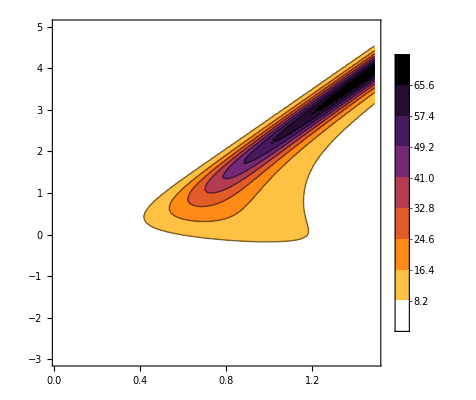

```mathematica
ListContourPlot[tab2,
ColorFunction->colorGradient2["SunsetColors",-1],
PlotLegends->Automatic,PlotRange->All,
Contours->8
]
```

```mathematica
G = 1.0;
Δs = range[-3,5,0.08];
Fsys = Table[{Δ,KerrFisherInformation["Δ",B,Δ,G,1/3,1.0,0,0]},{Δ,Δs}];
Fcqa = Table[{Δ,KerrCQAFisherInformation["Δ",nmax,Δ,G,1/3,1.0,0,0]},{Δ,Δs}];
```

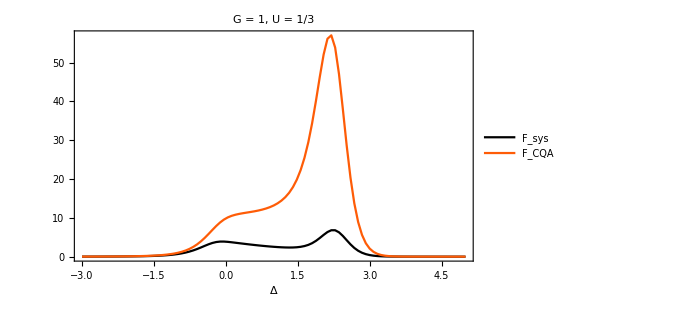

```mathematica
ListLinePlot[{Fsys,Fcqa},PlotRange->All,Joined->True,FrameLabel->{"Δ",None},PlotStyle->COLORLIST,ImageSize->500,
PlotLegends->legend[{"F_sys","F_CQA"},{0.25,0.6}],
PlotLabel->"G = 1, U = 1/3"
]
(*ListLogPlot[{Fsys,Fcqa},PlotRange->All,Joined->True]*)
```

## Charge-resolved dynamics, feedback

### Charge-resolved jump dynamics

```mathematica
(* Assumes Subscript[ν, k] = ± 1 *)
Clear[ChargeResolvedJumpDynamics];
ChargeResolvedJumpDynamics[ts_,a_,b_,rho0_,H_,Ls_,νs_]:=Module[{dt,r,d,He,L,𝕀,M,Ns,nl,ℤ,ρ,zpos,ℐ,band,𝒱,Ip,maxν,t,d2,comp,pos,ρ0,ρ2,𝒱p,stepprint,ℒ0,P,G,f},

r = Length@Ls;
d = Length@First@Ls;
d2 = d^2;
𝕀 = Eye[d];

maxν = Max@Abs@νs;
He = H - ⅈ/2 Sum[L†.L,{L,Ls}] ;
ℒ0 = kron[𝕀,-ⅈ He]+kron[ⅈ He*,𝕀];

Ns = Range[a,b,1];
nl = Length@Ns;

ℤ = Vec@ConstantArray[0,{d,d}];
ρ0 = Table[ℤ,{i,nl}];
zpos = Position[Ns,0][[1,1]];
ρ0[[zpos]] = Normal@Vec@rho0;
ρ0 = Flatten@ρ0;

ℐ = Eye[nl];
band[ν_,L_]:=DiagonalMatrix[ConstantArray[1,L-Abs@ν],ν];
𝒱 = kron[ℐ,ℒ0]+Sum[kron[band[-νs[[k]],nl],JumpOp[Ls[[k]]]],{k,r}]//SparseArray;
dt = If[Length@ts===0,ts,First@Differences@ts];
𝒱p = MatrixExp[𝒱 dt];
ρ = ρ0;

P=Table[
ρ = 𝒱p.ρ;
{Ns,Chop@Table[UnTr[Partition[ρ,d2][[i]]],{i,1,nl}]}ᵀ
,{Flatten@{ts}}];
If[Length@ts===0,P[[1]],
(
PrependTo[P,{Ns,Chop@Table[UnTr[Partition[ρ0,d2][[i]]],{i,1,nl}]}ᵀ];
G=Table[ Total@P[[i,All,2]],{i,Length@P}];
f= - Table[(G[[i+1]]-G[[i-1]])/(2dt),{i,2,Length@G-1}];
{P,{Prepend[ts,0],G}ᵀ,{Drop[ts,-1],f}ᵀ}
)]
]
```

#### Example usage

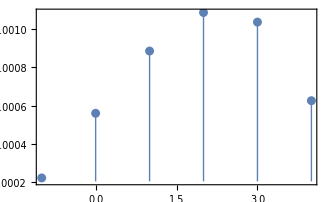
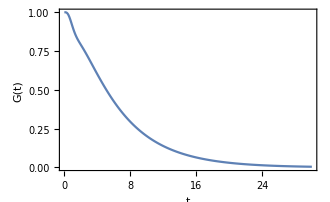
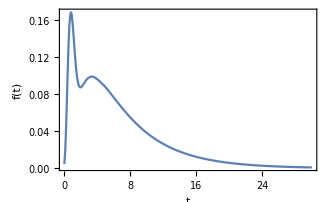

```mathematica
γ=1.;
Ω = 2.;
nb = 2.0;

H = Ω σx;
Ls = { √(γ(nb+1))σm ,√(γ nb)σp};
νs = {1,-1};
ℒ = Liouvillian[H,Ls];
ρ0 = SteadyState@Liouvillian[0H,Ls];
dt = 0.1;
tf = 30;
ts=Range[dt,tf,dt];
a = -1;
b = 4;
{P,G,f} = ChargeResolvedJumpDynamics[ts,a,b,ρ0,H,Ls,νs];
{ListLinePlot[P[[-1]],PlotRange->{{a,b},All},Joined->False,
Filling->Axis,FillingStyle->Thick,PlotRangePadding->Scaled[0.02]],
ListLinePlot[G,PlotRange->{0,1},FrameLabel->{"t","G(t)"}],
ListLinePlot[f,PlotRange->All,FrameLabel->{"t","f(t)"}]
}
```

```mathematica
Animate[ListLinePlot[P[[n]],
PlotRange->{{a-2,b+2},{0,0.3}},
GridLines->{{a,b},None},
GridLinesStyle->Directive[Opacity[0.3],Red,Thick,Dashed],
Epilog->{
Opacity[0.3],
Red,Rectangle[{a-2,0},{a,1}],
Red,Rectangle[{b+2,0},{b,1}]
},
Joined->False,
PlotStyle->Black,
PlotMarkers->Automatic,
Filling->Axis,
FillingStyle->Thick],{n,1,Length@P,1}]
```

#### Making a GIF

```mathematica
dt = 0.02;
tf=35;
ts=Range[dt,tf,dt];
a = -5;
b = 5;
γ=1.0;
Ω = 2.0;
ω = 0.0;
nb = 2.0;

H = Ω σx;
Ls = { √(γ(nb+1))σm ,√(γ nb)σp};
νs = {1,-1};
ℒ = Liouvillian[H,Ls];
ρ0 = SteadyState@Liouvillian[0H,Ls];

{P,G,f}=ChargeResolvedJumpDynamics[ts,a,b,ρ0,H,Ls,νs];
```

```mathematica
Animate[
Row[{
ListLinePlot[P[[n]],
PlotRange->{{a-1,b+2},{0,0.5}},
GridLines->{{a,b},None},
PlotStyle->Red,
FrameLabel->{"n","P(n,t)"},
GridLinesStyle->Directive[Black,Thick,Dashed],
Joined->False,
PlotMarkers->Automatic,
Filling->Axis,
FillingStyle->Thick],

ListLinePlot[G[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[G[[n]]]},
PlotRange->{{0,G[[-1,1]]},{0,1.05}},
FrameLabel->{"t","G_ℛ(t)"}
],
ListLinePlot[f[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[f[[n]]]},
PlotRange->{{0,f[[-1,1]]},{0,1.15Max[f[[All,2]]]}},
FrameLabel->{"t","f_ℛ(t)"}
]

}],{n,1,Length@P-1,1}]
```

```mathematica
makeGIF[Row[{
ListLinePlot[P[[n]],
PlotRange->{{a-1,b+1},{0,0.5}},
GridLines->{{a,b},None},
PlotStyle->Red,
FrameLabel->{"n","P(n,t)"},
GridLinesStyle->Directive[Black,Thick,Dashed],
Joined->False,
AspectRatio->1,
PlotMarkers->Automatic,
Filling->Axis,
FillingStyle->Thick],

ListLinePlot[G[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[G[[n]]]},
PlotRange->{{0,G[[-1,1]]},{0,1.05}},
FrameLabel->{"t","G_ℛ(t)"},
AspectRatio->1
],
ListLinePlot[f[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[f[[n]]]},
PlotRange->{{0,f[[-1,1]]},{0,1.15Max[f[[All,2]]]}},
FrameLabel->{"t","f_ℛ(t)"},
AspectRatio->1
]

}],{n,1,Length@P-1,1},"charge_resolved_dynamics",10];
```

00:00:04TimeObject[{0,0,4},Instant]

Exporting charge_resolved_dynamics.gif (can take a while...)

### Charge-resolved diffusive dynamics

```mathematica
(* H can also be the Liouvillian *)
Clear[ChargeResolvedDiffusiveDynamics];
ChargeResolvedDiffusiveDynamics[ts_,a_,b_,Δn_,rho0_,H_,Ls_,νs_:1]:=Module[{r,Kd,𝒦,Ns,nl,d,zpos,ρ0,ρ,ℤ,t,ℐ,𝒱,𝒱p,ℒ ,P,G,f,dt},
r = Length@Ls;
d = Length@First@Ls;

ℒ = If[Length@H===d,Liouvillian[H,Ls],H](* nasty trick to include the possibility that H is actually the vectorized Liouvillian, not the Hamiltonian *);

Kd = If[νs===1,r,Total[νs^2] ];

𝒦 = If[νs===1,
Sum[JumpOp[L,"diffusion"],{L,Ls}],
Sum[νs[[i]]JumpOp[Ls[[i]],"diffusion"],{i,r}]
];

Ns = N@Chop@Range[a,b,Δn];
nl = Length@Ns;
zpos = Position[Ns,0.][[1,1]];

ℤ = Vec@ConstantArray[0,{d,d}];
ρ0 = Table[ℤ,{i,nl}];
ρ0[[zpos]] = 1/Δn Normal@Vec@rho0;

(* Big matrix *)
𝒱 = kron[Eye[nl],ℒ] - kron[FirstDerivative[nl,Δn],𝒦] + Kd/2 kron[SecondDerivative[nl,Δn],Eye[ℒ]];
ℐ = NEye[𝒱];
dt = If[Length@ts===0,ts,First@Differences@ts];

(* Euler propagator *)
(*𝒱p = ℐ + ℐ.𝒱 dt;*)

(* RK4 propagator *)
𝒱p = ℐ + 𝒱 dt + 𝒱.𝒱 dt^2/2 + 𝒱.𝒱.𝒱 dt^3/6+𝒱.𝒱.𝒱.𝒱 dt^4/24;
ρ = Flatten@ρ0;
P=Table[
ρ = 𝒱p.ρ;
{ Ns,Chop@Table[UnTr[Partition[ρ,d^2][[i]]],{i,1,nl}]}ᵀ
,{Flatten@{ts}}
];

PrependTo[P,{ Ns,Chop@Table[UnTr[Partition[Flatten@ρ0,d^2][[i]]],{i,1,nl}]}ᵀ];
G=Δn Table[ Total@P[[i,All,2]],{i,Length@P}];
f= - Table[(G[[i+1]]-G[[i-1]])/(2dt),{i,2,Length@G-1}];
{P,{Prepend[ts,0],G}ᵀ,{Drop[ts,-1],f}ᵀ}
]
```

#### Example usage

```mathematica
γ=1.0;
Ω = 3.0;
H = Ω σx;
L = ⅈ √γ σm ;
ℒ = Liouvillian[H,{L}];
ρss = SteadyState[ℒ];

dt = 0.001;
tf = 1.0;
ts=Range[dt,tf,dt];
a = -2;
b = 2;
Δn = 0.1;
{P,G,f}=ChargeResolvedDiffusiveDynamics[ts,a,b,Δn,ρss,H,{L}];
```

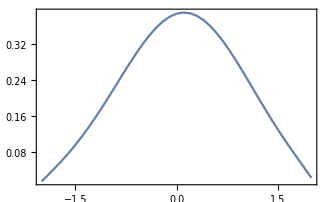

-Graphics-

-Graphics-

```mathematica
ListLinePlot[P[[-1]],PlotRange->All]
ListLinePlot[G]
ListLinePlot[f]
```

#### Making a GIF

```mathematica
γ=1.0;
Ω = 2.0;
ω = 0.0;
H = ω/2 σz+Ω σx;
L = ⅈ √γ σm ;
ℒ = Liouvillian[H,{L}];
ρss = SteadyState[ℒ];

dt = 0.001;
tf = 10.0;
ts=Range[dt,tf,dt];
a = -10;
b = 1;
Δn = 0.1;
{P,G,f}=ChargeResolvedDiffusiveDynamics[ts,a,b,Δn,ρss,H,{L}];
ListLinePlot[f,AspectRatio->1/3,PlotRange->All]
```

-Graphics-

```mathematica
Animate[
Row[{
ListLinePlot[P[[n]],
PlotRange->{{a-1,b+1},{0,All}},
GridLines->{{a,b},None},
PlotStyle->Red,
FrameLabel->{"n","P(n,t)"},
GridLinesStyle->Directive[Black,Thick,Dashed],
Joined->True,
AspectRatio->1,
(*Filling->Axis,*)
FillingStyle->Thick],

ListLinePlot[G[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[G[[n]]]},
PlotRange->{{0,G[[-1,1]]},{0,1.05}},
FrameLabel->{"t","G_ℛ(t)"},
AspectRatio->1
],
ListLinePlot[f[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[f[[n]]]},
PlotRange->{{0,f[[-1,1]]},{0,1.15Max[f[[All,2]]]}},
FrameLabel->{"t","f_ℛ(t)"},
AspectRatio->1
]

}],{n,1,Length@P-1,1}]
```

```mathematica
makeGIF[Row[{
ListLinePlot[P[[n]],
PlotRange->{{a-1,b+1},{0,All}},
GridLines->{{a,b},None},
PlotStyle->Red,
FrameLabel->{"n","P(n,t)"},
GridLinesStyle->Directive[Black,Thick,Dashed],
Joined->True,
AspectRatio->1,
(*Filling->Axis,*)
FillingStyle->Thick],

ListLinePlot[G[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[G[[n]]]},
PlotRange->{{0,G[[-1,1]]},{0,1.05}},
FrameLabel->{"t","G_ℛ(t)"},
AspectRatio->1
],
ListLinePlot[f[[1;;n]],PlotStyle->Red,Epilog->{PointSize[Large],Red,Point[f[[n]]]},
PlotRange->{{0,f[[-1,1]]},{0,1.15Max[f[[All,2]]]}},
FrameLabel->{"t","f_ℛ(t)"},
AspectRatio->1
]

}],{n,1,Length@P-1,1},"charge_resolved_dynamics_diffusive",10];
```

## Quantum jumps without time tags

### Constructing of relevant super-operators

```mathematica
Clear[NoTimeTagMatrices];
NoTimeTagMatrices[H_,cops_,sops_:0]:=Module[{Ls,Ls2,ℒ,𝒥s,ℒ0,ℒ0inv,ℳ},
Ls = If[Length@Dimensions@cops===3,cops,{cops}];
Ls2 = If[sops===0,
Ls,
If[Length@Dimensions@sops===3,Join[Ls,sops],Prepend[Ls,sops]]];

ℒ = Liouvillian[H,Ls2];
𝒥s = Table[JumpOp[c],{c,Ls}];
ℒ0 = ℒ-Total@𝒥s;
ℒ0inv = Inverse[ℒ0];
ℳ = Table[-J.ℒ0inv,{J,𝒥s}]

]
```

```mathematica
Clear[NoTimeTagJumpSteadyState];
NoTimeTagJumpSteadyState[ℳ_]:=SteadyState[Total@ℳ-Eye@First@ℳ]
```

#### Example usage

```mathematica
LoadSpinChainMatrices[L=3];
H = Sum[sp[i].sm[i+1]+sm[i].sp[i+1],{i,L-1}]+1/3 Sum[sp[i].sp[i+1]+sm[i].sm[i+1],{i,L-1}];
(* Monitored ops *)
γ = 1.0;
f1 = 0.3;
fL = 0.6;

L1 = √(γ(1-f1))sm[1];
L2 = √(γ fL)sp[L];
(* Unmonitored ops *)
V1 = √(γ f1)sp[1];
V2 = √(γ (1-fL))sm[L];
ℳ = NoTimeTagMatrices[H,{L1,L2},{V1,V2}];
M = ℳ[[1]]+ℳ[[2]];
```

Compare the jump steady-state with a manual calculation

```mathematica
NoTimeTagJumpSteadyState[ℳ]//mf;
```

(0.099893 | 0 | 0 | 0 | 0 | 0 | 0.-0.0136715 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.117819 | 0 | 0.-0.0294644 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.+0.0294644 ⅈ | 0 | 0.243141 | 0 | 0 | 0.+0.00500158 ⅈ
0 | 0 | 0 | 0 | 0 | 0.116542 | 0.-0.025111 ⅈ | 0
0.+0.0136715 ⅈ | 0 | 0 | 0 | 0 | 0.+0.025111 ⅈ | 0.285149 | 0
0 | 0 | 0 | 0 | 0.-0.00500158 ⅈ | 0 | 0 | 0.137456)

```mathematica
ρ = SteadyState[Liouvillian[H,{L1,L2,V1,V2}]];
pi = (JumpOp[L1]+JumpOp[L2]).Vec[ρ]//Unvec;
pi = pi/Tr[pi]//mf;
```

(0.099893 | 0 | 0 | 0 | 0 | 0 | 0.-0.0136715 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.117819 | 0 | 0.-0.0294644 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.+0.0294644 ⅈ | 0 | 0.243141 | 0 | 0 | 0.+0.00500158 ⅈ
0 | 0 | 0 | 0 | 0 | 0.116542 | 0.-0.025111 ⅈ | 0
0.+0.0136715 ⅈ | 0 | 0 | 0 | 0 | 0.+0.025111 ⅈ | 0.285149 | 0
0 | 0 | 0 | 0 | 0.-0.00500158 ⅈ | 0 | 0 | 0.137456)

### Stochastic Dynamics & Probabilities

```mathematica
Clear[NoTimeTagDynamics];
NoTimeTagDynamics[ℳ_,ρ0_,nsteps_]:=Module[{ρ,r = Length@ℳ,𝒜,p,x},
𝒜 = Range[1,r] (* alphabet *);
ρ = Vec@ρ0;
Table[
p = Table[UnTr[ℳ[[x]].ρ],{x,Most@𝒜}];
AppendTo[p,1-Total@p];
x = RandomChoice[Chop@p->𝒜];
ρ = ℳ[[x]].ρ;
ρ = ρ/UnTr[ρ];
{x,p,Unvec[ρ]},{nsteps}
]//Transpose//Chop
]
```

```mathematica
(* Outputs Subscript[M, Subscript[x, n]]... Subscript[M, Subscript[x, 1]] *)
Clear[NoTimeTagStringProduct];
NoTimeTagStringProduct[X_,ℳ_]:=Module[{x=Flatten@{X},r},
r = ℳ[[x[[1]]]];
Do[r = ℳ[[x[[j]]]].r,{j,2,Length@x}];
r//Chop];

(* Outputs Subscript[M, Subscript[x, n]]... Subscript[M, Subscript[x, 1]] ρ *)
NoTimeTagStringProduct[X_,ℳ_,ρ_]:=Module[{x = Flatten@{X},r=Vec@ρ},
Do[r=ℳ⟦x[[i]]⟧.r,{i,1,Length@x}];
Unvec[r]//Chop
];
```

```mathematica
(* Outputs tr(Subscript[M, Subscript[x, n]]... Subscript[M, Subscript[x, 1]] ρ) *)
Clear[NoTimeTagStringProbability];
NoTimeTagStringProbability[x_,ℳ_,ρ_]:=Tr@NoTimeTagStringProduct[x,ℳ,ρ]
```

```mathematica
(* Outputs P(x|y,ρ) *)
Clear[NoTimeTagStringConditionalProbability];
NoTimeTagStringConditionalProbability[x_,y_,ℳ_,ρ_]:=(Tr@NoTimeTagStringProduct[Join[Flatten@{x},Flatten@{y}],ℳ,ρ])/(Tr@NoTimeTagStringProduct[Flatten@{y},ℳ,ρ])

(* Outputs Subscript[P, k](x|y,ρ) where there is a gap k between x and y*)
NoTimeTagStringConditionalProbability[X_,Y_,ℳ_,ρ_,k_]:=Module[{Mx,My,M,x=Flatten@{X},y=Flatten@{Y}},
My =  NoTimeTagStringProduct[y,ℳ];
M = Total@ℳ;
Which[
k==0,
NoTimeTagStringConditionalProbability[x,y,ℳ,ρ],
k>0,
(Mx = NoTimeTagStringProduct[x,ℳ];
UnTr[Mx.MatrixPower[M,k].My.Vec[ρ]]/UnTr[My.Vec[ρ]]//Chop),
k<0 (* overlap *),
(
Mx = NoTimeTagStringProduct[Drop[x,-k],ℳ];
KroneckerDelta[x[[1;;-k]],y[[k;;-1]]] UnTr[Mx.My.Vec[ρ]]/UnTr[My.Vec[ρ]])
]//Chop
]
```

```mathematica
KroneckerDelta[{1,2,1},{1,2,2}]
```

0

#### Example usage

```mathematica
LoadSpinChainMatrices[L=3];
H = Sum[sp[i].sm[i+1]+sm[i].sp[i+1],{i,L-1}]+1/3 Sum[sp[i].sp[i+1]+sm[i].sm[i+1],{i,L-1}];
(* Monitored ops *)
γ = 1.0;
f1 = 0.3;
fL = 0.6;

L1 = √(γ(1-f1))sm[1];
L2 = √(γ fL)sp[L];
(* Unmonitored ops *)
V1 = √(γ f1)sp[1];
V2 = √(γ (1-fL))sm[L];
ℳ = NoTimeTagMatrices[H,{L1,L2},{V1,V2}];
ρ0 = NoTimeTagJumpSteadyState[ℳ];
```

```mathematica
{xs,ps,ρs}=NoTimeTagDynamics[ℳ,ρ0,10];
(* String of outcomes *)
xs
(* Probabilities at each outcome *)
ps
```

{1,1,2,2,1,1,2,2,1,1}

{{0.501103,0.498897},{0.398295,0.601705},{0.369362,0.630638},{0.557847,0.442153},{0.63193,0.36807},{0.430177,0.569823},{0.371446,0.628554},{0.563469,0.436531},{0.633785,0.366215},{0.431751,0.568249}}

```mathematica
(* Matrix Subscript[M, 1] Subscript[M, 1] Subscript[M, 2] Subscript[M, 1] *)
NoTimeTagStringProduct[{1,2,1,1},ℳ];
```

```mathematica
(* State of the system after sequence of outcomes 1 -> 2 -> 1 -> 1 *)
NoTimeTagStringProduct[{1,2,1,1},ℳ,ρ0]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00931833 | 0 | 0 | 0.-0.0014882 ⅈ
0 | 0 | 0 | 0 | 0 | 0.0169805 | 0.-0.00167536 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.00167536 ⅈ | 0.0159246 | 0
0 | 0 | 0 | 0 | 0.+0.0014882 ⅈ | 0 | 0 | 0.0280232)

```mathematica
(* Probability of observing the sequence 1 -> 2 -> 1 -> 1 *)
NoTimeTagStringProbability[{1,2,1,1},ℳ,ρ0]
```

0.0702466

```mathematica
(* Probability distribution for all sequences of length 3 *)
Table[NoTimeTagStringProbability[x,ℳ,ρ0],{x,Tuples[{1,2},3]}]
Total@%
```

{0.0737198,0.125867,0.175253,0.126264,0.125867,0.175649,0.126264,0.0711173}

1.

## Monitoring operator formalism for stochastic quantum metrology

### For general super-operator channels

See https://melt1.notion.site/General-stochastic-Fisher-information-Monitoring-operator-formalism-e6a35512bb9f4482ab3dee8272fe3f23?pvs=4 for a description

Specify a set of super-operators ℳ_x, with x = 1,2,3...
The dynamics of the system will evolve as follows: 

→ With probability p_j=tr(ℳ_j ρ_(j-1))  we choose to apply channel j and then update the state of the system as ρ_j=(ℳ_j ρ_(j-1))/p_j 
→ The monitoring operator formalism evolves as  ξ_j=((∂_θ ℳ_x_j)ρ_(j-1)+ℳ_x_j ξ_j)/p_j with initial condition ξ_j=0

```mathematica
Clear[MonitoringOperator];
MonitoringOperator[ℳ_,dℳ_,ρ0_,nsteps_,fulloutput_:False]:=Module[{ρ,r = Length@ℳ,𝒜,p,x,ξ},
𝒜 = Range[1,r] (* alphabet *);
ρ = Vec@ρ0;
ξ = 0 ρ;
If[fulloutput===True,
Table[
p = Table[UnTr[ℳ[[x]].ρ],{x,Most@𝒜}];
AppendTo[p,1-Total@p];
x = RandomChoice[Chop@p->𝒜];
ξ = (dℳ[[x]].ρ + ℳ[[x]].ξ)/p[[x]];
ρ = (ℳ[[x]].ρ)/p[[x]];
{x,(*p,*)Unvec[ρ],Unvec@ξ,UnTr[ξ]^2},{nsteps}
],

Table[
p = Table[UnTr[ℳ[[x]].ρ],{x,Most@𝒜}];
AppendTo[p,1-Total@p];
x = RandomChoice[Chop@p->𝒜];
ξ = (dℳ[[x]].ρ + ℳ[[x]].ξ)/p[[x]];
ρ = (ℳ[[x]].ρ)/p[[x]];
{x,UnTr[ξ]^2},{nsteps}
]
]//Transpose//Chop
]
```

#### Example usage

3-qubit chain with injection and extraction at the boundaries

```mathematica
LoadSpinChainMatrices[L=3,"a"];
Clear[γ];
H = Sum[sp[i].sm[i+1]+sm[i].sp[i+1],{i,L-1}];
𝒥1 = γ JumpOp[sp[1]];
𝒥2 = γ JumpOp[sm[L]];
ℒ0 = Liouvillian[H,{sp[1],sm[L]},{γ,γ}]-𝒥1-𝒥2;
ℒ0inv = Inverse[ℒ0];
M1 = -𝒥1.ℒ0inv//Simplify;
M2 = -𝒥2.ℒ0inv//Simplify;
ℳ = {M1,M2};
dℳ={D[M1,γ],D[M2,γ]};
γ = 1.0;
ψ0 = Basis[2^L,1];
ρ0 = out[ψ0,ψ0];
{xs,ρs,ξs,fs}=MonitoringOperator[ℳ,dℳ,ρ0,10,True];
xs
(*lmf@ρs*)
lmf@ξs
fs
```

{2,1,2,2,1,2,1,1,2,2}

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-0.545455 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.545455 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0681818 | 0 | 0.-0.0340909 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.+0.0340909 ⅈ | 0 | -0.409091 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0407056 | 0.+0.0691995 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.0691995 ⅈ | -0.244233 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.171373 | 0 | 0.+0.102824 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.102824 ⅈ | 0 | -0.220336 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.268492 | 0.+0.155012 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.155012 ⅈ | -0.166601 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-0.369127 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.369127 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.178386 | 0 | 0.+0.0320318 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.0320318 ⅈ | 0 | -0.342968 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0,0.297521,0.297521,0.116219,0.0414236,0.00239743,0.0103816,0.136255,0.136255,0.0270872}

```mathematica
{xs,fs}=MonitoringOperator[ℳ,dℳ,ρ0,1000,False];
```

```mathematica
ListLinePlot[fs/Range[1,Length@fs],PlotRange->All]
```

-Graphics-

### In the quantum jump unravelling

```mathematica
Clear[MonitoringOperatorQuantumJumpNEnsemble];
MonitoringOperatorQuantumJumpNEnsemble[ψ0_,H_,dH_,L_,dL_,τs_,njumps_,ntrajs_:1,seed_:0,onlyJumps_:True]:=Module[{A,𝒜,𝔸,nk,nts,He,Q,ψ,τ,tab,P,Xp,X,nA,x,j,i,dA,dHe,ϕ,ξ,f,δ,dV,n},

If[seed!=0,SeedRandom[seed]];

nk = Length@L;
nts = Length@τs;
𝒜 = Distribute[{Range[1,nk],τs},List];
𝔸 = Range[1,Length@𝒜];
nA = Length@𝔸;

He = H - ⅈ/2 Sum[c†.c,{c,L}];
dHe = dH - ⅈ/2 Sum[dL⟦i⟧†.L[[i]]+L[[i]]†.dL[[i]],{i,Length@L}];

δ = 10^-6;
Do[
x = 𝒜[[j]];
A[j] = L[[x[[1]]]].MatrixExp[-ⅈ He x[[2]]];
Q[j] = A[j]†.A[j];
dV = (MatrixExp[-ⅈ (He + δ dHe)x[[2]]]-MatrixExp[-ⅈ (He-δ dHe)x[[2]]])/(2δ)(* ∂_θ e^(-i Subscript[H, e] t) *);
dA[j] = dL[[x[[1]]]].MatrixExp[-ⅈ He x[[2]]] + L[[x[[1]]]].dV(*BCHderiv[-ⅈ He x[[2]],-ⅈ dHe x[[2]]]*);
,{j,𝔸}] ;

PrintTemporary[Norm[Q[𝔸[[-1]]]]];

table[
ψ = Normal@ψ0;
τ= 0;
tab = {};
ξ = ConstantArray[0,{Length@ψ0,Length@ψ0}];
Do[(*τ< tf,*)
P = Table[ψ*.Q[i].ψ,{i,𝔸}]//Chop;
j=SillySample[𝔸,P];
X = 𝒜⟦j⟧;

τ = τ + X[[2]];
ϕ = (dA[j].ψ)/(√P[[j]]);
ψ = (A[j].ψ)/(√P[[j]]);
ξ = out[ϕ,ψ]+out[ψ,ϕ] + (A[j].ξ.A[j]†)/P[[j]];
f = Tr[ξ]^2;
AppendTo[tab,{X,τ,ψ,ξ,f}];
,{njumps}
];
Chop@If[onlyJumps===True,tab[[All,{1,2,5}]]ᵀ,tabᵀ]
,{n,ntrajs}]


]
(*MonitoringOperatorQuantumJumpGillespie[ψ0,H,dH,L,0L,τs,250,1,0,True];*)
```

#### Example usage

```mathematica
ψ0 = {1,0};
Ω = 0.5;
γ = 1.0;
H = Ω σx;
L = {σm};

dH = σx;
dL =0 L;

τs = Range[0,50,0.01];
sims=MonitoringOperatorQuantumJumpNEnsemble[ψ0,H,dH,L,0L,τs,100,400,0,True];
```

{{{0,0},{0,0}}}

00:02:37TimeObject[{0,2,37},Instant]

```mathematica
sims2=MonitoringOperatorQuantumJumpNEnsemble[ψ0,H,dH,L,0L,τs,100,800,2,True];
```

00:05:35TimeObject[{0,5,35},Instant]

```mathematica
sims3=MonitoringOperatorQuantumJumpNEnsemble[ψ0,H,dH,L,0L,τs,100,800,3,True];
```

00:05:34TimeObject[{0,5,34},Instant]

```mathematica
(*sims1 = sims;*)
sims = Join[sims1,sims2,sims3];
```

```mathematica
ListLinePlot[Mean@sims[[All,3]]]
ListLinePlot[(Mean@sims[[All,3]])/Range[1,100],GridLines->{None,{48}},PlotRange->{0,50}]
```

-Graphics-

-Graphics-

```mathematica
Clear[Δ,γ,Ω,nb];
H = (*σz+*)Ω σx;
ℒ = Liouvillian[H,σm,γ(*(nb+1)*)];
𝒥 = γ(*(nb+1)*) JumpOp[σm];
ρ= SteadyState[ℒ]//mf;
ℒ0 = ℒ-𝒥;
W=WaitingTimeDistribution[t,ℒ0,𝒥,𝒥]//Simplify
Jave = UnTr[𝒥.Vec@ρ]//Simplify
```

((4 Ω^2)/(γ^2+8 Ω^2) | -(2 ⅈ γ Ω)/(γ^2+8 Ω^2)
(2 ⅈ γ Ω)/(γ^2+8 Ω^2) | (γ^2+4 Ω^2)/(γ^2+8 Ω^2))

(4 ⅇ^(-1/2 t (γ+√(γ^2-16 Ω^2))) (-1+ⅇ^(1/2 t √(γ^2-16 Ω^2)))^2 γ Ω^2)/(γ^2-16 Ω^2)

(4 γ Ω^2)/(γ^2+8 Ω^2)

```mathematica
FF = D[W,Ω]^2/W//Simplify;
Ω = 0.5;
γ = 1.0;
Fana =  NIntegrate[FF,{t,0,∞}]//Chop

Fana =  NIntegrate[Jave FF,{t,0,∞}]//Chop
```

48.

16.

#### Example usage - estimating time à la Hasegawa, by taking H→ (1+θ) H and L-> √(1+θ)L

## Non-interacting systems (covariance matrix, Lyapunov, &c.)

## Non-interacting systems (Lyapunov etc.)

### LyapunovEigen: solves the Lyapunov equation using eigen-decomposition

This function solves WC + CW†=F using eigendecomposition of W. 
Apparently this turns out to be faster than “LyapunovSolve[W,F]”. 
I believe this is related to the fact that in Lindblad dynamics, F is usually quite sparse.

```mathematica
Clear[LyapunovEigen]
LyapunovEigen[W_,F_]:=Module[{ℐ,Λ,S,Sinv},
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ;
Sinv = Inverse[S];

ℐ = 1/Outer[Plus,Λ,Λ*] Sinv.F.Sinv†;
S.ℐ.S†//Chop
];
```

#### Example usage

NESS of an Aubry-Andre quantum spin chain. 
Localization transition occurs at λ = 1

```mathematica
Clear[h,H,Γ,W,F];
λ = 0.5;
γ = 1;
f1 = 0.9;
fL = 0.1;
L = 5;

h[n_]:=λ Cos[ 2π GoldenRatio n ];

Γ = SparseArray[{{1,1}->γ,{L,L}->γ},{L,L}];
H = SparseArray[{{i_,i_}->2h[i],{i_,j_}/;j==i+1->-1,{i_,j_}/;j==i-1->-1},{L,L}];
W = ⅈ H-Γ;

F= SparseArray[{{1,1}->γ f1,{L,L}->γ fL},{L,L}];
```

```mathematica
LyapunovEigen[W,F]//Chop//mf;
```

(0.403979 | 0.0310366+0.046021 ⅈ | -0.0216419+0.00692131 ⅈ | -0.00605492+0.0309566 ⅈ | 0.00112528+0.0223755 ⅈ
0.0310366-0.046021 ⅈ | 0.310717 | 0.0471862+0.046021 ⅈ | -0.0529709+0.0308989 ⅈ | -0.0525851-0.00217123 ⅈ
-0.0216419-0.00692131 ⅈ | 0.0471862-0.046021 ⅈ | 0.254804 | -0.0561362+0.046021 ⅈ | -0.0121533-0.0424196 ⅈ
-0.00605492-0.0309566 ⅈ | -0.0529709-0.0308989 ⅈ | -0.0561362-0.046021 ⅈ | 0.206188 | 0.0417284+0.046021 ⅈ
0.00112528-0.0223755 ⅈ | -0.0525851+0.00217123 ⅈ | -0.0121533+0.0424196 ⅈ | 0.0417284-0.046021 ⅈ | 0.096021)

### LyapunovLinearSys: solves the Lyapunov equation as a linear system using vectorization

```mathematica
Clear[LyapunovLinearSys];
LyapunovLinearSys[W_,F_]:=Unvec@LinearSolve[Eye[W]⊗W+W*⊗ Eye[W],Vec[F]]
```

### LyapunovDriven: time-dependent Lyapunov dynamics

Solves dC/dt= -(W_t C + C W_t^†) + F_t.

W and F can either be (matrix-valued) functions (W(t), F(t)) or matrices.

```mathematica
LyapunovDriven[W_,F_,𝒞0_,Δt_,tf_,sparse_:1,quiet_:False]:=Module[{f,testW,testF},
(* Check if input is a function or a matrix *)
testW = Head[W] ===Symbol || Head[W] ===Function;
testF = Head[F] ===Symbol || Head[F] ===Function;
Which[
testW&&testF,
f[t_,𝒞_]:=-W[t].𝒞-𝒞.W[t]†+F[t],
testW && Not[testF],
f[t_,𝒞_]:=-W[t].𝒞-𝒞.W[t]†+F,
Not[testW] && testF,
f[t_,𝒞_]:=-W.𝒞-𝒞.W†+F[t],
True,
f[t_,𝒞_]:=-W.𝒞-𝒞.W†+F
];
RK4t[f,𝒞0,Δt,tf,False,quiet]⟦1;;-1;;sparse⟧
]
```

#### Example usage

Double quantum dot + Local Lindblad + Periodic drive on dot 2. 
Recall that 

W = i h + Γ/2

We first create the undriven matrices, and then add a drive to the unitary (complex) part of W:

```mathematica
(* Undriven matrices *)
{W,F}=BDMatrices[1,2,0.1,{0.2,0.5}];
𝒲[t_]:=W +3 ({{0, 0}, {0, ⅈ}})Cos[t];

𝒞0 = ({{0, 0}, {0, 1}});

(* We pass to the function a matrix F, and the function 𝒲 *)
res=LyapunovDriven[W +3 ({{0, 0}, {0, ⅈ}})Cos[#]&,F,𝒞0,0.005,50,10];
```

```mathematica
(* Plot the populations *)
ListLinePlot[{
{res⟦All,1⟧,res⟦All,2,1,1⟧}ᵀ,
{res⟦All,1⟧,res⟦All,2,2,2⟧}ᵀ},
PlotRange->All
]
```

-Graphics-

### BD: Boundary-driven chains (fermions & bosons)

```mathematica
Clear[BDMatrices]
BDMatrices[h_,γ_,f_]:=Module[{L=Length@h,Γ,F0},
Γ =If[Length@γ===Length@h, SparseArray@DiagonalMatrix@γ,SparseArray[{{1,1}->γ,{L,L}->γ},{L,L}]];
F0 =Which[
Length@f===Length@h, SparseArray@DiagonalMatrix@f ,
Length@f === 2,SparseArray[{{1,1}-> f⟦1⟧,{L,L}-> f⟦2⟧},{L,L}],
True,f Eye[L]
];
{ⅈ h + Γ/2, Γ F0}
]

BDMatrices[V_,L_,γ_,f_]:=Module[{Γ,A,W,F,g,h,i}, 
BDMatrices[TightBindingHamiltonian[L,V], γ,f]
];
```

```mathematica
Clear[BDCovMat];
BDCovMat[W_,F_]:=LyapunovEigen[W,F]
BDCovMat[h_,γ_,{f1_,fL_}]:=LyapunovEigen@@BDMatrices[h,γ,{f1,fL}];
BDCovMat[V_,L_,γ_,{f1_,fL_}]:=LyapunovEigen@@BDMatrices[V,L,γ,{f1,fL}]
```

```mathematica
(* Only holds for nearest-neighbor tight-binding models *)
Clear[BDCurrent];
BDCurrent[𝒞_]:=(*Im@𝒞⟦2,1⟧*) -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
BDCurrent[W_,F_]:=BDCurrent[LyapunovEigen[W,F]]
BDCurrent[h_,γ_,{f1_,fL_}]:=BDCurrent[LyapunovEigen@@BDMatrices[h,γ,{f1,fL}]];
BDCurrent[V_,L_,γ_,{f1_,fL_}]:=BDCurrent[LyapunovEigen@@BDMatrices[V,L,γ,{f1,fL}]];
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[4,1]//mf;
```

(1 | -1 | 0 | 0
-1 | 1 | -1 | 0
0 | -1 | 1 | -1
0 | 0 | -1 | 1)

```mathematica
MatrixForm/@BDMatrices[h,{γ1,γ2,γ3,γ4},{f1,f2,f3,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ+γ2/2 | -ⅈ | 0
0 | -ⅈ | ⅈ+γ3/2 | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ4/2),(f1 γ1 | 0 | 0 | 0
0 | f2 γ2 | 0 | 0
0 | 0 | f3 γ3 | 0
0 | 0 | 0 | f4 γ4)}

```mathematica
MatrixForm/@BDMatrices[h,γ1,{f1,f2,f3,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f4 γ1)}

```mathematica
MatrixForm/@BDMatrices[h,γ1,{f1,f4}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f4 γ1)}

```mathematica
MatrixForm/@BDMatrices[1,5,γ1,{f1,f5}]
```

{(ⅈ+γ1/2 | -ⅈ | 0 | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0 | 0
0 | -ⅈ | ⅈ | -ⅈ | 0
0 | 0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | 0 | -ⅈ | ⅈ+γ1/2),(f1 γ1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | f5 γ1)}

```mathematica
{W,F}=BDMatrices[ϵ,4,γ,{f1,fL}];
mf@W;
mf@F;
```

(γ/2+ⅈ ϵ | -ⅈ | 0 | 0
-ⅈ | ⅈ ϵ | -ⅈ | 0
0 | -ⅈ | ⅈ ϵ | -ⅈ
0 | 0 | -ⅈ | γ/2+ⅈ ϵ)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
{W,F}=BDMatrices[1,4,0.1,{0.3,0.7}];
mf@W;
mf@F;
```

(0.05+1. ⅈ | -ⅈ | 0 | 0
-ⅈ | ⅈ | -ⅈ | 0
0 | -ⅈ | ⅈ | -ⅈ
0 | 0 | -ⅈ | 0.05+1. ⅈ)

(0.03 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.07)

```mathematica
BDMatrices[1,7,1,{1/2,0.3}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
LyapunovEigen@@BDMatrices[1.,7,1,{1/2,0.3}]
```

{{0.42,0.-0.04 ⅈ,0,0,0,0,0},{0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0,0,0},{0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0,0},{0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0,0},{0,0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ,0},{0,0,0,0,0.+0.04 ⅈ,0.4,0.-0.04 ⅈ},{0,0,0,0,0,0.+0.04 ⅈ,0.38}}

```mathematica
LyapunovEigen@@{W,F}
```

{{0.499501,0.+0.00997506 ⅈ,0,0},{0.-0.00997506 ⅈ,0.5,0.+0.00997506 ⅈ,0},{0,0.-0.00997506 ⅈ,0.5,0.+0.00997506 ⅈ},{0,0,0.-0.00997506 ⅈ,0.500499}}

```mathematica
LyapunovEigen[W,F]//mf;
```

(0.499501 | 0.+0.00997506 ⅈ | 0 | 0
0.-0.00997506 ⅈ | 0.5 | 0.+0.00997506 ⅈ | 0
0 | 0.-0.00997506 ⅈ | 0.5 | 0.+0.00997506 ⅈ
0 | 0 | 0.-0.00997506 ⅈ | 0.500499)

```mathematica
CovMatCurrent[W,F]
```

-0.00997506

```mathematica
{W,F}=BDMatrices[{ϵ1,ϵ2,ϵ3,ϵ4},4,γ,{f1,fL}];
mf@W;
mf@F;
```

(γ/2+ⅈ ϵ1 | -ⅈ | 0 | 0
-ⅈ | ⅈ ϵ2 | -ⅈ | 0
0 | -ⅈ | ⅈ ϵ3 | -ⅈ
0 | 0 | -ⅈ | γ/2+ⅈ ϵ4)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
{W,F}=BDMatrices[RandomReal[{0,1},{4,4}],γ,{f1,fL}];
mf@W;
mf@F;
```

((0.+0.493385 ⅈ)+γ/2 | 0.+0.963652 ⅈ | 0.+0.571679 ⅈ | 0.+0.527462 ⅈ
0.+0.744496 ⅈ | 0.+0.656838 ⅈ | 0.+0.317111 ⅈ | 0.+0.151104 ⅈ
0.+0.619738 ⅈ | 0.+0.67314 ⅈ | 0.+0.231151 ⅈ | 0.+0.831389 ⅈ
0.+0.131986 ⅈ | 0.+0.616602 ⅈ | 0.+0.907259 ⅈ | (0.+0.284962 ⅈ)+γ/2)

(f1 γ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | fL γ)

```mathematica
CovMatCurrent[1.,87,1,{0.2,0.3}]
```

-0.02

```mathematica
BDCovMat[1.0,10,1,{0.2,0.3}]//mf;
```

(0.24 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.25 | 0.+0.02 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.02 ⅈ | 0.26)

```mathematica
(* Aubry-André model *)
```

```mathematica
g = GoldenRatio;
V[n_]:=λ Cos[ 2π g n + ϕ]/(1-α Cos[2π g n + ϕ]);
```

#### Example: quantum transport in the Fibonnacci model (based arXiv 2106.11406)

The Fibonnacci model is quite incredible because, even though it is a non-interacting chain, it can show any kind of transport coefficient.

```mathematica
(* Takes a couple of minutes to run *)
Clear[L,λ];
λrange = range[0,7,0.1];
Lrange ={8,13,21,34,55,89,144,233,377,610,987};
sims = Association[];
```

```mathematica
Monitor[Do[
Clear[V];
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
sims[{λ,L}]=BDCurrent[λ V,L,1,{1,0}];
,{λ,λrange},{L,Lrange}],{λ,L}]

fits = Association[];
Do[
fits[λ] = Fit[Table[{Log10@L,Log10@sims[{λ,L}]},{L,Lrange}],{1,x},x];
,{λ,λrange}]
```

```mathematica
Show[
ListLogLogPlot[Table[{L,sims[{λ,L}]},{λ,range[0,5,1.]},{L,Lrange}],Joined->False,PlotMarkers->Automatic,
AspectRatio->1,
PlotStyle->Drop[ColorData[3,"ColorList"],3]
],
LogLogPlot[Evaluate@Table[10^(fits[λ]/.x->Log10[y]),{λ,range[0,5,1.]}],{y,0.1,10^3},
PlotStyle->Drop[ColorData[3,"ColorList"],3],
PlotLegends->legend[Round@range[0,5,1.],{0.29,0.12},LegendLayout->{"Row",2}]],
FrameLabel->{"L","J"}
]
```

-Graphics-

```mathematica
ListLinePlot[Table[{λ,-fits[λ]⟦2,1⟧},{λ,λrange}],PlotMarkers->Automatic,
GridLines->{None,{1}},
GridLinesStyle->Directive[Black, Dashed]]
```

-Graphics-

### Dephasing

```mathematica
Clear[DephasingSolve];
DephasingSolve[W_,F_,Γ_]:=Module[{L = Length@W,vecW,vecRemoveDiag,vecF},
vecW = kron[W*,NEye[L]]+kron[NEye[L],W];
vecRemoveDiag = SparseArray[{i_,i_}/;Last@QuotientRemainder[i,L+1]≠1->1,{L^2,L^2}];

LinearSolve[vecW + Γ vecRemoveDiag, Vec[F]]//Unvec//Chop
]
```

```mathematica
Clear[BDCovMatDephasing];
BDCovMatDephasing[W_,F_,Γ_]:=DephasingSolve[W,F,Γ];
BDCovMatDephasing[h_,γ_,{f1_,fL_},Γ_]:=Module[{W,F} ,
{W,F} = BDMatrices[h,γ,{f1,fL}];
DephasingSolve[W,F,Γ]
];
BDCovMatDephasing[V_,L_,γ_,{f1_,fL_},Γ_]:=Module[{W,F} ,
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
DephasingSolve[W,F,Γ]
];
```

```mathematica
(* Only holds for nearest-neighbor tight-binding models *)
Clear[BDCurrentDephasing];
BDCurrentDephasing[𝒞_]:=(*Im@𝒞⟦2,1⟧*) -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
BDCurrentDephasing[W_,F_,Γ_]:=BDCurrentDephasing[BDCovMatDephasing[W,F,Γ]]
BDCurrentDephasing[h_,γ_,{f1_,fL_},Γ_]:=BDCurrentDephasing[BDCovMatDephasing[h,γ,{f1,fL},Γ]];
BDCurrentDephasing[V_,L_,γ_,{f1_,fL_},Γ_]:=BDCurrentDephasing[BDCovMatDephasing[V,L,γ,{f1,fL},Γ]];
```

#### QuotientRemainder logic

This vectorized superoperator removes the diagonal of a matrix

```mathematica
L=4;
tmp=SparseArray[{i_,i_}/;Last@QuotientRemainder[i,L+1]≠1->1,{L^2,L^2}]/.L->10//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tmp.Vec@Table[Subscript[a, i,j],{i,L},{j,L}]//Unvec//mf;
```

(0 | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | 0 | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | 0 | a_(3,4)
a_(4,1) | a_(4,2) | a_(4,3) | 0)

#### Example: noise-assisted transport in a Fibonnacci subdiffusive chain (arXiv 2106.11406)

Define a tight-binding model with Fibonnacci on-site potentials

```mathematica
L = 100;
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
BDCurrent[V,L,1,{1,0}]
```

0.0770395

```mathematica
BDCurrentDephasing[V,L,1,{1,0},0.0]
```

0.0770395

```mathematica
Γrange = logspace[-3,2,30];
L = 500;
V = N@Table[IntegerPart[(i+1)/GoldenRatio^2]-IntegerPart[i/GoldenRatio^2],{i,1,L}];
results = Table[{Γ,BDCurrentDephasing[4 V,L,1,{1,0},Γ]},{Γ,Γrange}]
```

{{0.001,0.00033293},{0.00148735,0.000351493},{0.00221222,0.000371302},{0.00329034,0.000391671},{0.0048939,0.000411741},{0.00727895,0.000430803},{0.0108264,0.000447989},{0.0161026,0.00046374},{0.0239503,0.000479437},{0.0356225,0.000496692},{0.0529832,0.000516324},{0.0788046,0.000536324},{0.11721,0.000554202},{0.174333,0.000569738},{0.259294,0.000586251},{0.385662,0.00060827},{0.573615,0.000632935},{0.853168,0.000652367},{1.26896,0.000664039},{1.88739,0.000667492},{2.80722,0.000652044},{4.17532,0.000596975},{6.21017,0.000498174},{9.23671,0.000380927},{13.7382,0.000274105},{20.4336,0.000190525},{30.392,0.00013012},{45.2035,0.0000881205},{67.2336,0.0000594439},{100.,0.0000400273}}

```mathematica
ListLogLinearPlot[results,Joined->True,PlotMarkers->Automatic]
```

-Graphics-

## Quantum information with Covariance Matrices

### Get full ρ from Cov Mat 𝒞

Given a bosonic or fermionic covariance matrix 𝒞_ij= ⟨c_j^†c_i⟩, returns a pair (M,Z) which can be used to reconstruct the state as ρ=e^(-c†.M.c) /Z

```mathematica
Clear[CovMatRhoFromC];
CovMatRhoFromC[𝒞_,statistic_:"Fermions"]:=Module[{𝕀 = Eye[Length@𝒞],λ,V,Z,M},
{λ,V} = Eigsys[𝒞];
If[matchString["Fermions", statistic],
Z = 1/Det[𝕀-𝒞];
M=V.DiagonalMatrix[Log[(1-λ)/λ]].V†;
,
Z = Det[𝕀+𝒞];
M=V.DiagonalMatrix[Log[(1+λ)/λ]].V†;
];
{M,Z}//Chop
]
```

#### Example usage

Covariance matrix obtained from a boundary-driven problem with 3 sites

```mathematica
𝒞=BDCovMat[1,3,0.1,{0.8,0.2}]//mf;
```

(0.500748 | 0.-0.0149626 ⅈ | 0
0.+0.0149626 ⅈ | 0.5 | 0.-0.0149626 ⅈ
0 | 0.+0.0149626 ⅈ | 0.499252)

Reconstruct the full quantum state in the case of Fermions

```mathematica
{M,Z} = RhoFromC[𝒞,"fermions"]
```

{{{-0.00299431,0.+0.0598862 ⅈ,0},{0.-0.0598862 ⅈ,0,0.+0.0598862 ⅈ},{0,0.-0.0598862 ⅈ,0.00299431}},8.01437}

```mathematica
LoadFermionicOperators[L = Length@𝒞];
ρ = 1/Z MatrixExp[-Sum[M⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]]//mf;
```

(0.124776 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.125374 | 0.-0.00749249 ⅈ | 0 | -0.000223879 | 0 | 0 | 0
0 | 0.+0.00749249 ⅈ | 0.125224 | 0 | 0.-0.0074701 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.125374 | 0 | 0.-0.00749249 ⅈ | -0.000223879 | 0
0 | -0.000223879 | 0.+0.0074701 ⅈ | 0 | 0.124626 | 0 | 0 | 0
0 | 0 | 0 | 0.+0.00749249 ⅈ | 0 | 0.125224 | 0.-0.0074701 ⅈ | 0
0 | 0 | 0 | -0.000223879 | 0 | 0.+0.0074701 ⅈ | 0.124626 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.124776)

Check that this gives back the correct covariance matrix

```mathematica
𝒞2 = Table[Tr[cd[j].c[i].ρ],{i,L},{j,L}];
𝒞-𝒞2//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Entropy (von Neumann & Rényi)

Considers a bosonic or fermionic system with covariance matrix 𝒞_ij= ⟨c_j^†c_i⟩.
Computes vonNeumann or Rényi entropy.

```mathematica
Clear[CovMatEntropy];
CovMatEntropy[𝒞_,α_:1,statistic_:"Fermions"]:=Module[{𝕀 = Eye[Length@𝒞],Z,M,λ,V},
{λ,V} = Eigsys[𝒞];
If[matchString["Fermions", statistic],
Z = 1/Det[𝕀-𝒞];
M=V.DiagonalMatrix[Log[(1-λ)/λ]].V†;
,
Z = Det[𝕀+𝒞];
M=V.DiagonalMatrix[Log[(1+λ)/λ]].V†;
];
Chop@If[Abs[α-1]<10^-12,
Log[Z] + Tr[M.𝒞],
-α/(1-α)Log[Z] + 1/(1-α)If[matchString["Fermions", statistic],
Total@Log[1+((1-λ)/λ)^-α],-Total@Log[1-((1+λ)/λ)^-α]]]
]
```

#### Example usage

Covariance matrix obtained from a boundary-driven problem with 3 sites

```mathematica
𝒞=BDCovMat[1,3,0.1,{0.8,0.2}]//mf;
```

(0.500748 | 0.-0.0149626 ⅈ | 0
0.+0.0149626 ⅈ | 0.5 | 0.-0.0149626 ⅈ
0 | 0.+0.0149626 ⅈ | 0.499252)

Reconstruct the full quantum state in the case of Fermions

```mathematica
{M,Z} = RhoFromC[𝒞,"fermions"];
LoadFermionicOperators[L = Length@𝒞];
ρ = 1/Z MatrixExp[-Sum[M⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]];
```

Compute the von Neumann entropy

```mathematica
vonNeumann[ρ]
CovMatEntropy[𝒞]
```

2.07765

2.07765

Compute Rényi entropies

```mathematica
{Renyi[ρ,0.5],CovMatEntropy[𝒞,0.5]}
{Renyi[ρ,1.5],CovMatEntropy[𝒞,1.5]}
```

{2.07854,2.07854}

{2.07675,2.07675}

### Relative entropy (von Neumann & Rényi)

```mathematica
Clear[CovMatRelativeEntropy];
CovMatRelativeEntropy[𝒞1_,𝒞2_,α_:1,statistic_:"Fermions"]:=Module[{𝕀 = Eye[Length@𝒞1],Z1,M1,λ1,V1,Z2,M2,λ2,V2,s,ζ,ξ},
{λ1,V1} = Eigsys[𝒞1];
{λ2,V2} = Eigsys[𝒞2];
If[matchString["Fermions", statistic],
Z1 = 1/Det[𝕀-𝒞1];
M1=V1.DiagonalMatrix[Log[(1-λ1)/λ1]].V1†;
Z2 = 1/Det[𝕀-𝒞2];
M2=V2.DiagonalMatrix[Log[(1-λ2)/λ2]].V2†; 
,
Z1 = Det[𝕀+𝒞1];
M1=V1.DiagonalMatrix[Log[(1+λ1)/λ1]].V1†;
Z2 = Det[𝕀+𝒞2];
M2=V2.DiagonalMatrix[Log[(1+λ2)/λ2]].V2†; 
];
s = If[matchString["Fermions", statistic],1,-1];

Chop@If[Abs[α-1]<10^-12,
-(Log[Z1] + Tr[M1.𝒞1]) + Log[Z2] + Tr[M2.𝒞1]
,
ζ = DiagonalMatrix[(λ2/(1-s λ2))^((1-α)/(2α))].V2†.V1.DiagonalMatrix[(λ1/(1-s λ1))].V1†.V2.DiagonalMatrix[(λ2/(1-s λ2))^((1-α)/(2α))]; 
ξ = Eigvals[ζ];
Log[Z2]+α/(1-α)Log[Z1] - 1/(1-α)s Total@Log[1+s ξ^α]
]
]
```

#### Example usage

Covariance matrix obtained from a boundary-driven problem with 3 sites

```mathematica
𝒞=BDCovMat[1,3,0.1,{0.8,0.2}]//mf;
```

(0.500748 | 0.-0.0149626 ⅈ | 0
0.+0.0149626 ⅈ | 0.5 | 0.-0.0149626 ⅈ
0 | 0.+0.0149626 ⅈ | 0.499252)

Change some parameter to obtain a new covariance matrix

```mathematica
𝒞2=BDCovMat[1,3,0.2,{0.8,0.2}]//mf;
```

(0.50297 | 0.-0.029703 ⅈ | 0
0.+0.029703 ⅈ | 0.5 | 0.-0.029703 ⅈ
0 | 0.+0.029703 ⅈ | 0.49703)

```mathematica
{M2,Z2} = RhoFromC[𝒞2,"fermions"];
ρ2 = 1/Z2 MatrixExp[-Sum[M2⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]];
```

Compute relative entropy

```mathematica
KullbackLeibler[ρ,ρ2]
CovMatRelativeEntropy[𝒞,𝒞2]
```

0.00176687

0.00176687

Compute Rényi divergences

```mathematica
{RenyiDivergence[ρ,ρ2,0.5],CovMatRelativeEntropy[𝒞,𝒞2,0.5]}
{RenyiDivergence[ρ,ρ2,1.5],CovMatRelativeEntropy[𝒞,𝒞2,1.5]}
```

{0.000882713,0.000882713}

{0.00265207,0.00265207}

## Mesoscopic leads (“thermleads”)

### Reaction coordinates & star-to-chain mapping

```mathematica
Clear[ReactionCoordinateMappingNumerics];
ReactionCoordinateMappingNumerics[Js_,ωs_]:=Module[{Λ1,Ω1,P,ω,ωmin,ωmax,dω,Jnew},

ωmin = First@ωs;
ωmax = Last@ωs;
dω = ωs⟦2⟧-ωs⟦1⟧;

Λ1 = √(1/(2π)Trapz[Js,dω]);
Ω1 = 1/(2π Λ1^2)Trapz[ωs Js,dω];

P = 1/π Table[Trapz[Drop[Js,{i}]/Drop[ωs-ωs⟦i⟧,{i}],dω],{i,Length@ωs}]; 
Jnew = (4 Λ1^2 Js)/(P^2+Js^2);
{Λ1,Ω1,Jnew}
]
```

```mathematica
StarToChainMapping[𝒥s_,ωs_,Lb_]:=Module[{Λ1,Ω1,P,ω,ωmin,ωmax,dω,Jnew,Js},

ωmin = First@ωs;
ωmax = Last@ωs;
dω = ωs⟦2⟧-ωs⟦1⟧;
Js=𝒥s;
Table[
Λ1 = √(1/(2π)Trapz[Js,dω]);
Ω1 = 1/(2π Λ1^2)Trapz[ωs Js,dω];

P = 1/π Table[Trapz[Drop[Js,{i}]/Drop[ωs-ωs⟦i⟧,{i}],dω],{i,Length@ωs}]; 
Js = (4 Λ1^2 Js)/(P^2+Js^2);
{Λ1^2,Ω1}
,{Lb}]
]
```

#### Example usage

```mathematica
(* Boxcar *)
γ = 0.3;
δ =1.0;
ϵ = 0.3;
ωs = linspace[ϵ-δ,ϵ+δ,999];
Js = Table[γ Boxcar[ϵ-δ,ϵ+δ][ω],{ω,ωs}];

{Λ1,Ω1,Jnew}=ReactionCoordinateMappingNumerics[Js,ωs];

{Λ1^2,Ω1}
{(γ δ)/π,ϵ}
```

{0.095493,0.3}

{0.095493,0.3}

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[(4 π δ)/(π^2+4 ArcTanh[(ϵ-ω)/δ]^2),{ω,ϵ-δ,ϵ+δ},PlotStyle->Directive[Red,Dotted]]
]
```

-Graphics-

{0.074996,0.199968}

{0.075,0.2}

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[(δ(2δ)^2)/((ω-ϵ)^2+(2δ)^2),{ω,-20,20},PlotStyle->Directive[Red,Dotted]]
]
```

-Graphics-

```mathematica
(* Quadratic Lorentzian. Bit weird *)
γ = 0.3;
δ =1.0;
ϵ = 0.2;
ωs = linspace[-20,20,1000];
Js = Table[(γ δ^2)/((ω-ϵ)^2+δ^2),{ω,ωs}];

{Λ1,Ω1,Jnew}=ReactionCoordinateMappingNumerics[Js,ωs];

{Λ1^2,Ω1}
{(γ δ)/2,ϵ}
```

{0.145229,0.193441}

{0.15,0.2}

```mathematica
Show[
ListLinePlot[{ωs,Jnew}ᵀ,PlotRange->All],
Plot[2δ,{ω,-30,30},PlotStyle->Red],
PlotRange->{{-20,20},All}
]
```

-Graphics-

#### Star-to-chain

```mathematica
(* Quartic Lorentzian *)
γ = 0.3;
δ =1.0;
ϵ = 0.2;
ωs = linspace[-4,4,1000];
Js = Table[(γ δ^4)/(((ω-ϵ)^2+δ^2)^2),{ω,ωs}];

StarToChainMapping[Js,ωs,50]
```

{{0.0745313,0.196439},{0.699475,0.125942},{3.20508,-0.0154157},{4.70386,-0.00229059},{4.18537,-0.000573852},{4.09302,-0.000609534},{4.06204,0.000232555},{4.04339,-0.000513866},{4.03714,0.00035079},{4.0301,-0.000393887},{4.02836,0.000278304},{4.02535,-0.000256235},{4.02471,0.000178137},{4.02348,-0.000147772},{4.02324,0.000101511},{4.02283,-0.0000774687},{4.0228,0.000053977},{4.02279,-0.000037022},{4.0229,0.0000278337},{4.02307,-0.0000156261},{4.02328,0.0000146065},{4.02353,-5.04961×10^-6},{4.02379,8.30661×10^-6},{4.02408,-1.60047×10^-7},{4.02436,5.40235×10^-6},{4.02466,1.89955×10^-6},{4.02494,4.03158×10^-6},{4.02522,2.60535×10^-6},{4.02549,3.29531×10^-6},{4.02575,2.68278×10^-6},{4.02599,2.79582×10^-6},{4.02622,2.47845×10^-6},{4.02644,2.37615×10^-6},{4.02664,2.1576×10^-6},{4.02682,1.98619×10^-6},{4.02698,1.8011×10^-6},{4.02713,1.61857×10^-6},{4.02726,1.45057×10^-6},{4.02738,1.27973×10^-6},{4.02749,1.12821×10^-6},{4.02758,9.77935×10^-7},{4.02766,8.45603×10^-7},{4.02772,7.18869×10^-7},{4.02778,6.07663×10^-7},{4.02783,5.04608×10^-7},{4.02787,4.14793×10^-7},{4.0279,3.33965×10^-7},{4.02792,2.64318×10^-7},{4.02794,2.03322×10^-7},{4.02796,1.51611×10^-7}}

### “Thermleads:” Mesoscopic leads approach for non-interacting fermion dynamics

Based on https://journals.aps.org/prx/pdf/10.1103/PhysRevX.10.031040

```mathematica
(* Function for sampling the energies and couplings of the mesoscopic leads approach *)
Clear[ThermleadsEnergySamples];
ThermleadsEnergySamples[Lb_,w_,Γ_,type_:"linear"]:=Module[{energies,gammas,kappas,Γs,Llog,Llin,Wstar =w/2,logsamp,samples},
Which[
type==="linear",
(energies = linspace[-w,w,Lb];
gammas = ConstantArray[First@Differences@energies,Lb];
kappas = √(Γ gammas/(2π))
),
type==="newns",
((* 𝒥(ϵ) = 8 Γ/(2π)√(1-ϵ^2/w^2)θ(w-|ϵ|) *)
(* Define with a factor of 8 to make it comparable to the wideband limit *)

energies = linspace[-w,w,Lb];
gammas = ConstantArray[First@Differences@energies,Lb];
 Γs= 8 Γ/(2π)√(1-#^2/w^2)&/@energies; 

kappas = √(Γs gammas/(2π))
),
type==="loglin",
(Llog = Round[0.2 Lb];
Llin=Lb -2 Round[0.2 Lb];
logsamp = logspace[Log10[Wstar],Log10[w],Llog+1];
samples=Join[
Most@Reverse[-logsamp],
linspace[-Wstar,Wstar,Llin+1],
Rest@logsamp];
energies = (Most@samples+Rest@samples)/2;
gammas = Differences[samples];
kappas = √(Γ gammas/(2π));
)

];

{energies,kappas,gammas}

]
```

```mathematica
Clear[ThermleadsMatrices];
ThermleadsMatrices[h_,Γ_,{TL_,TR_,μL_,μR_},Lb_,w_,type_:"linear"]:=Module[{energies,couplings,gamma,Ls=Length@h,HB1,HB2,VS1,VS2,H,W,F,Fermis,ws=w/2},

{energies,couplings,gamma} = ThermleadsEnergySamples[Lb,w,Γ,type];

HB1 = DiagonalMatrix[energies];
HB2 = HB1;

VS1=Sum[couplings⟦n⟧ Proj[{Lb,Ls},n,1],{n,Length@couplings}];
VS2=Sum[couplings⟦n⟧ Proj[{Ls,Lb},Ls,n],{n,Length@couplings}];


H=ArrayFlatten[({{HB1, VS1, 0}, {VS1†, h, VS2}, {0, VS2†, HB2}})]; 

Fermis[T_,μ_,energies_]:=1/(Exp[(energies-μ)/T]+1) ;


W = ⅈ H + 1/2 DiagonalMatrix@Join[gamma,ConstantArray[0,Ls],gamma];

F = Quiet@DiagonalMatrix@Join[Fermis[TL,μL,energies]gamma,ConstantArray[0,Ls],Fermis[TR,μR,energies]gamma];

{W,F}
]
```

```mathematica
Clear[ThermleadsGetSysCM];
ThermleadsGetSysCM[𝒞_,Lb_]:=Module[{Ls = Length@𝒞-2Lb},𝒞⟦Lb+1;;Lb+Ls,Lb+1;;Lb+Ls⟧]
```

```mathematica
Clear[ThermleadsDecomposeW];
ThermleadsDecomposeW[W_,Lb_,bath_]:=Module[{γ,ϵ,Ls = Length@W-2Lb,rg,κ},
rg = If[bath==="left",1;;Lb,Lb+Ls+1;;Ls+2Lb];
γ = Diagonal[(W+W†)]⟦rg⟧;
ϵ = Im[Diagonal@W]⟦rg⟧;
κ = If[bath=="left",Im@W⟦Lb+1,rg⟧,Im@W⟦Lb+Ls,rg⟧];
{ϵ,κ,γ}//Chop
]
```

```mathematica
Clear[ThermleadsParticleCurrent];
ThermleadsParticleCurrent[𝒞_,W_,F_,Lb_,bath_:"left",energyResolved_:False]:=Module[{Ls = Length@𝒞-2Lb,ϵ,κ,γ,rg,J1,J2,c1},
If[bath=="difference",1/2(ThermleadsParticleCurrent[𝒞,W,F,Lb,"left",energyResolved]-ThermleadsParticleCurrent[𝒞,W,F,Lb,"right",energyResolved]),
(
rg = If[bath==="left",
Range[1,Lb],
Range[Lb+Ls+1,Lb+Ls+Lb]];
c1 = If[bath==="left",Lb+1,Lb+Ls];
{ϵ,κ,γ} = ThermleadsDecomposeW[W,Lb,bath];
J1 = ⅈ Table[κ[[i]] (𝒞[[c1,rg[[i]]]]-𝒞[[c1,rg[[i]]]]*),{i,Lb}];
(*J2 = Table[F[[rg[[i]],rg[[i]]]]-γ[[i]] 𝒞[[rg[[i]],rg[[i]]]],{i,Lb}];*)
If[energyResolved===True,J1,Total@J1]//Chop
)]
]
```

```mathematica
Clear[ThermleadsEnergyCurrent];
ThermleadsEnergyCurrent[𝒞_,W_,F_,Lb_,bath_:"left",energyResolved_:False]:=Module[{Ls = Length@𝒞-2Lb,γ,ϵ,κ,JEprx,JEartur,term1,term2,term3,rg,c1},
rg = If[bath==="left",
Range[1,Lb],
Range[Lb+Ls+1,Lb+Ls+Lb]];
c1 = If[bath==="left",Lb+1,Lb+Ls];

{ϵ,κ,γ} = ThermleadsDecomposeW[W,Lb,bath];
(* Relevant terms *)
(* tr(Subscript[H, L] ℒ(ρ)) = ∑_k Subscript[ϵ, k] Subscript[γ, k](Subscript[f, k]-⟨Subscript[a, k]^†Subscript[a, k]⟩) *)
term1 = Table[ϵ⟦i⟧ (F⟦rg[[i]],rg[[i]]⟧-γ⟦i⟧ 𝒞⟦rg[[i]],rg[[i]]⟧),{i,Lb}]//Chop;

(* tr(Subscript[V, SL] ℒ(ρ)) = -1/2∑_k Subscript[κ, k] Subscript[γ, k]⟨Subscript[c, 1]^†Subscript[a, k]+Subscript[a, k]^†Subscript[c, 1]⟩ *)
term2 =-1/2 Table[κ[[i]] γ[[i]](𝒞[[c1,rg[[i]]]]+𝒞[[c1,rg[[i]]]]*),{i,Lb}]//Chop;

(* i ⟨[Subscript[H, L],Subscript[V, SL]]⟩ = -i Subscript[ϵ, k] Subscript[κ, k] ⟨Subscript[c, 1]^†Subscript[a, k]-Subscript[a, k]^†Subscript[c, 1]⟩ *)
term3 = ⅈ Table[κ[[i]] ϵ[[i]](𝒞[[c1,rg[[i]]]]-𝒞[[c1,rg[[i]]]]*),{i,Lb}]//Chop;


(* The two energy currents below only coincide in steady-state. Otherwise, JEartur is the correct one *);
(* Energy current in Marlon's PRX https://journals.aps.org/prx/pdf/10.1103/PhysRevX.10.031040*)
(* tr(Subscript[H, L] ℒ(ρ)) + tr(Subscript[V, SL] ℒ(ρ)) *)
JEprx = term1+term2;

(* Energy current in Artur's PRB https://journals.aps.org/prb/pdf/10.1103/PhysRevB.107.195117) *)
(* i ⟨[Subscript[H, L],Subscript[V, SL]]⟩ + tr(Subscript[V, SL] ℒ(ρ)) *)
JEartur = term3+term2;

If[energyResolved===True,
{{JEprx,JEartur},{term1,term2,term3}},
{{Total@JEprx,Total@JEartur},{Total@term1,Total@term2,Total@term3}}]
]
```

```mathematica
(* Gives a matrix with entry ⅈ  in site i of the system *)
Clear[ThermleadsDriveMatrix];
ThermleadsDriveMatrix[Lb_,Ls_,site_]:=SparseArray[{{j_,j_}/;j==Lb+site:>ⅈ},{Lb+Ls+Lb,Lb+Ls+Lb}]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[3,1]//mf;
{W,F}=ThermleadsMatrices[h,1,{0.5,0.4,0,0},Lb=10,8];
```

(1 | -1 | 0
-1 | 1 | -1
0 | -1 | 1)

```mathematica
W//Abs//MatrixPlot
```

-Graphics-

```mathematica
{W,F}=ThermleadsMatrices[h,1,{0.5,0.4,0,0},Lb=150,8];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb]//mf;
```

(0.293755 | 0.219708-0.00256656 ⅈ | 0.0836406+0.00213347 ⅈ
0.219708+0.00256656 ⅈ | 0.32079 | 0.222487-0.00256656 ⅈ
0.0836406-0.00213347 ⅈ | 0.222487+0.00256656 ⅈ | 0.298967)

```mathematica
(* Compare with the exact solution using NEGF *)
C2=NEGFCovMat[h,1,{0.5,0.4,0,0}]//mf;
C1-C2//mf;
```

(0.299931 | 0.220131-0.0026735 ⅈ | 0.08466+0.00210373 ⅈ
0.220131+0.0026735 ⅈ | 0.315236 | 0.222945-0.0026735 ⅈ
0.08466-0.00210373 ⅈ | 0.222945+0.0026735 ⅈ | 0.30545)

(-0.00617646 | -0.000423455+0.000106938 ⅈ | -0.00101941+0.000029743 ⅈ
-0.000423455-0.000106938 ⅈ | 0.00555451 | -0.000457844+0.000106938 ⅈ
-0.00101941-0.000029743 ⅈ | -0.000457844-0.000106938 ⅈ | -0.00648259)

```mathematica
Clear[Lb];
tab=table[
{W,F}=ThermleadsMatrices[h,1,{0.5,0.4,0,0},Lb,16];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb];
{Lb,Norm[C1-C2]},{Lb,10,500,30}];
```

00:00:08TimeObject[{0,0,8},Instant]

```mathematica
ListLogPlot[tab,PlotMarkers->Automatic,FrameLabel->{"L_B","|C_TL - C_NEGF|"},PlotRange->All,Joined->True,
PlotLabel->"Convergence of thermleads"
]
```

-Graphics-

```mathematica
tab=table[
{W,F}=ThermleadsMatrices[h,1,{0.5,0.4,0,0},Lb,Wmax];
C1=ThermleadsGetSysCM[BDCovMat[W,F],Lb];
{Wmax,Norm[C1-C2]},{Lb,{150,300,450}},{Wmax,4,30,2}];
```

00:00:25TimeObject[{0,0,25},Instant]

```mathematica
ListLogPlot[tab,PlotMarkers->Automatic,FrameLabel->{"W_max","|C_TL - C_NEGF|"},PlotRange->All,Joined->True,
PlotLabel->"Convergence of thermleads",
PlotLegends->legend[{"L_B=500","L_B=300","L_B=450"},{0.35,0.75}],
ImageSize->400
]
```

-Graphics-

#### Particle current in a double quantum dot: comparison with Landauer-Büttiker

```mathematica
T = 100;
γ = 1.0;
eV = 100; 
μL = eV/2;
μR = -eV/2;
gs = linspace[0.001,4,10];
Clear[LB,Meso,g,𝒯];
𝒯[g_,γ_,ϵ_:0]:=NEGFTransmissionFunction[({{ϵ, g}, {g, ϵ}}),γ];
Do[
LB[g] = LandauerButtiker[𝒯[g,γ],{T,T,μL,μR}];
{W,F}=ThermleadsMatrices[({{0, g}, {g, 0}}),γ,{T,T,μL,μR},Lb=100,8];
𝒞 = BDCovMat[W,F];

Meso[g] = ThermleadsParticleCurrent[𝒞,W,F,Lb]

,{g,gs}]
```

```mathematica
Show[
ListLinePlot[Table[{g,LB[g]["IN"]},{g,gs}]],
ListLinePlot[Table[{g, Meso[g]},{g,gs}],PlotStyle->Black]]
```

-Graphics-

#### Energy-resolved particle current compared to the Landauer-Büttiker transmission function

```mathematica
T = 1;
Γ = 1.0;
w = 3;
eV = 0.5; 
μL = eV/2;
μR = -eV/2;
g=1.0;
𝒯=NEGFTransmissionFunction[({{0, g}, {g, 0}}),Γ];
{W,F}=ThermleadsMatrices[({{0, g}, {g, 0}}),Γ,{T,T,μL,μR},Lb=30,w];
𝒞 = BDCovMat[W,F];
ILs = ThermleadsParticleCurrent[𝒞,W,F,Lb,"left",True];
IRs = ThermleadsParticleCurrent[𝒞,W,F,Lb,"right",True];
energies = First@ThermleadsEnergySamples[Lb,w,Γ];
δ = First@Differences@energies;

{W,F}=ThermleadsMatrices[({{0, g}, {g, 0}}),Γ,{T,T,μL,μR},Lb=150,w];
𝒞 = BDCovMat[W,F];
ILs2 = ThermleadsParticleCurrent[𝒞,W,F,Lb,"left",True];
IRs2 = ThermleadsParticleCurrent[𝒞,W,F,Lb,"right",True];
energies2 = First@ThermleadsEnergySamples[Lb,w,Γ];
δ2 = First@Differences@energies2;


tab = Table[{ϵ,1/(2π)𝒯[ϵ](1/(ⅇ^((ϵ-μL)/T)+1)-1/(ⅇ^((ϵ-μR)/T)+1))},{ϵ,linspace[-3,3,300]}];
ListLinePlot[{tab,{energies,1/δ(ILs-IRs)/2}ᵀ,{energies2,1/δ2(ILs2-IRs2)/2}ᵀ},
Joined->{True,False,False},
PlotMarkers->{None,{"■",15},{"●",6}},
PlotRange->All,
PlotStyle->{Black,Red,COLORLIST[[4]]},
PlotLegends->Placed[
PointLegend[
{Black,Red,COLORLIST[[4]]},
{Style["L.B.",FontFamily->"Times"],Style[30,FontFamily->"Times"],Style[150,FontFamily->"Times"]},
LegendMarkers->{None,{"■",16},"●"}
],
Scaled[{0.15,0.71}]],
FrameLabel->{"Energy","Current"},
ImageSize->400
]
```

-Graphics-

#### Energy current in the transient regime

```mathematica
h = TightBindingHamiltonian[2,1];
{W0,F}=ThermleadsMatrices[h,1,{0.5,0.5,0,0},Lb=20,8];
C0=BDCovMat[W0,F];

h1 = ({{0, 0}, {0, 1}});
W1 = ⅈ ArrayFlatten[({{ConstantArray[0,{Lb,Lb}], 0, 0}, {0, h1, 0}, {0, 0, ConstantArray[0,{Lb,Lb}]}})]//Normal;
```

```mathematica
(* Pulsed field *)
σ = 5;
ω = 0.2;

ℰ[t_]:=Exp[-(t-15)^2/σ^2]Cos[ω t ]
dt = 0.02;
tf = 50;
ℰ0 = 2.0;

Clear[f];
f[t_,𝒞_]:=With[{W = W0 +ℰ0  ℰ[t]W1},-W.𝒞-𝒞.W†+F];
sol = RK4t[f,C0,dt,tf];
```

```mathematica
currLeft=Table[ThermleadsEnergyCurrent[c⟦2⟧,W0+ℰ0  ℰ[c⟦1⟧]W1,F,Lb,"left"]⟦1⟧,{c,sol}];
currRight=Table[ThermleadsEnergyCurrent[c⟦2⟧,W0+ℰ0  ℰ[c⟦1⟧]W1,F,Lb,"right"]⟦1⟧,{c,sol}];
```

```mathematica
ListLinePlot[Flatten[{currLeftᵀ⟦1;;2⟧,currRightᵀ⟦1;;2⟧},1],PlotRange->All,
ImageSize->500,
PlotLegends->legend[{"left 1","left 2","right 1", "right 2"},{0.75,0.25}]
]
```

-Graphics-

#### Energy current: comparison withe Landauer-Büttiker

```mathematica
Clear[TL,Lb]
TLs = Range[0.2,2,0.1];
Lbs = {100,150,200(*,250*)};
h = TightBindingHamiltonian[Ls=5];
γ = 0.1;
𝒯=NEGFTransmissionFunction[h,γ];
(*Clear[simsLB,simsTL,simsArchak];*)
do[
LB=LandauerButtiker[𝒯,{TL,TR=1.9,μL=0.,μR=0.3}]//Quiet;
simsLandauerButtiker[TL,"IE"]=LB["IE"];

Do[
{W,F}=ThermleadsMatrices[h,γ,{TL,TR,μL,μR},Lb,8];
(*simsTL[TL,Lb,"IE"]=ThermleadsFCSAverage[W,F,{Ls,Lb},"energy","left"] ;*)
𝒞= BDCovMat[W,F];
simsMesoscopicLeads[TL,Lb,"IE"]=ThermleadsEnergyCurrent[𝒞,W,F,Lb];

,{Lb,Lbs}];
,{TL,TLs}]
```

00:00:15TimeObject[{0,0,15},Instant]

```mathematica
Show[
ListLinePlot[Table[{TL,simsLandauerButtiker[TL,"IE"]},{TL,TLs}],PlotStyle->Black],
ListLinePlot[
Table[{TL,simsMesoscopicLeads[TL,Lb,"IE"]⟦1,2⟧},{Lb,Lbs},{TL,TLs}]
]
]
```

-Graphics-

## Full Counting Statistics with Covariance Matrices

### BDFCS: Full counting statistics for non-interacting fermions with local Lindblad

This is made with respect to the notation developed in 
https://melt1.notion.site/The-ultimate-guide-to-Gaussian-open-things-covariance-matrix-Lyapunov-equations-fermions-bosons--7e45a124c7d64122b6d65d8ae7e4c59e

The master equation is assumed to be given by

Input: A, B, ϵ, γ_-, γ_+ and the current weights ν_- and ν_+

```mathematica
Clear[BDFCSload];
BDFCSload[A_,{γγm_,γγp_},{ννm_,ννp_},ϵϵ_:0,statistic_:"boson",B_:0,{ϕϕm_:0,ϕϕp_:0}]:=Module[{tol = 10^-12,L = Length@A,size,fixMatSize,γp,γm,νp,νm,𝒲,Υ,s,Vj, Vj2,Vd,Γ,Ω,Θ,f,r,ϵ,𝕀,o,Kj,Kd,Jj,Jd,ϕm,ϕp},
LoadPauliMatrices[];

s = If[matchString[statistic,"boson"],1,-1] ;
Ω = If[matchString[statistic,"boson"],ⅈ kron[σy,Eye[L]],-ⅈ Eye[2L]];
size = 2L;
(*size = If[Norm[B]< tol, L,2L];*)

𝕀=Eye[size];

(* Adjust the matrices γp, γm, νp, νm to allow for multiple types of inputs *);
fixMatSize[mat_]:=Which[
Length@Dimensions@mat===1 &&Length@mat===2,
SparseArray[{{1,1}->mat[[1]],{L,L}->mat[[2]]},{L,L}],
Length@Dimensions@mat===1 &&Length@mat===L,
DiagonalMatrix@mat,
True,
mat];

ϕm = ϕϕm//DiagonalMatrix;
ϕp = ϕϕp//DiagonalMatrix;

γp = fixMatSize[γγp];
γm = fixMatSize[γγm];
νp = fixMatSize[ννp];
νm = fixMatSize[ννm];

Γ = γm - s γp;

Vj = 1/2 σ0⊗ (νp.γp + νm.γm)+1/2 σy ⊗ (νp.γp - νm.γm);
Vj2 = 1/2 σ0⊗ (νp.νp.γp +νm. νm.γm)+1/2 σy ⊗ (νp.νp.γp -νm. νm.γm);
Vd=If[ϕϕm===0&&ϕϕp===0,
1/(√2)Join[Diagonal[νp.√γp+νm.√γm],ⅈ Diagonal[νm.√γm-νp.√γp]]//DiagonalMatrix,
1/(√2)Join[Diagonal[ⅇ^(-ⅈ ϕp)νp.√γp+(ⅇ^(-ⅈ ϕm)).νm.√γm],ⅈ Diagonal[(ⅇ^(-ⅈ ϕm)).νm.√γm-(ⅇ^(-ⅈ ϕp)).νp.√γp]]//DiagonalMatrix
];

𝒲 = ⅈ/2(σ0 ⊗ (A-Aᵀ) -σy ⊗ (A+Aᵀ) - ⅈ σx ⊗ (B+B*) +σz ⊗ (B-B*)) + 1/2 σ0 ⊗ Γ ;
Υ = If[matchString[statistic,"boson"],1/2 σ0⊗(γp + γm), -1/2 σy ⊗ (γm-γp)];
Θ = LyapunovSolve[𝒲,Υ];

ϵ = If[Norm[ϵϵ]<tol||matchString[statistic,"fermion"],ConstantArray[0,L],ϵϵ];

r = LinearSolve[𝒲,Ω.kron[1/(√2)({{1, 1}, {-ⅈ, ⅈ}}),Eye[L]].Join[ϵ,ϵ*]];
o = ConstantArray[1,size];

Jj = Tr[Vj.(s (Θ-ⅈ Ω/2)+out[r,r])]//Chop;
Kj = Tr[Vj2.(s (Θ-ⅈ Ω/2)+out[r,r])];

Jd = o.(Vd+Vd†).r//Chop;
Kd = νm^2+νp^2//Total//First;

<|"size"->size,
"s"->s,
"statistic"->statistic,
"Ω"->Ω//Normal//Chop,
"𝕀"->𝕀//Normal//Chop,
"γp"->γp//Normal//Chop,
"γm"->γm//Normal//Chop,
"νp"->νp//Normal//Chop,
"νm"->νm//Normal//Chop,
"Γ"->Γ//Normal//Chop,
"𝒲"->𝒲//Normal//Chop,
"Υ"->Υ//Normal//Chop,
"Vj"->Vj//Normal//Chop,
"Vd"->Vd//Normal//Chop,
"Θ"->Θ//Normal//Chop,
"r"->r//Normal//Chop,
"o"->o//Normal//Chop,
"Jj"->Jj//Normal//Chop,
"Jd"->Jd//Normal//Chop,
"Kj"->Kj//Normal//Chop,
"Kd"->Kd//Normal//Chop
|>
]
```

```mathematica
Clear[BDFCSTwoPointFunction];
BDFCSTwoPointFunction[tts_,𝕃_,type_:"jump"]:=Module[{G,Θt,g,V,r = 𝕃["r"],s = 𝕃["s"],ts,o = 𝕃["o"],F},
ts = Flatten@{tts};
G[τ_]:=MatrixExp[-𝕃["𝒲"] τ];
Θt =𝕃["Θ"]-ⅈ 𝕃["Ω"]/2; 

F = If[matchString[type,"jump"],
V = 𝕃["Vj"];
Table[g = G[τ]; {τ,Tr[g†.(Vᵀ+s V).g.Θt.V.Θt] + r.(V.Θt.g†.(Vᵀ+V) + (Vᵀ+V).g.Θt.V).r},{τ,ts}],
V = 𝕃["Vd"];
Table[g = G[τ]; {τ,o.((V+V†).g.Θt.V†+V.Θt.g†.(V+V†)).o},{τ,ts}]
];
If[Length@tts===0,F[[1,2]],F]//Chop
];
```

```mathematica
Clear[BDFCSPowerSpectrum];
BDFCSPowerSpectrum[ωωs_,𝕃_,type_:"jump"]:=Module[{ωs,K,Θt,V,rhs,Bp,Bm,ξ,𝒲 = 𝕃["𝒲"],r = 𝕃["r"],s = 𝕃["s"],o = 𝕃["o"],S,𝕀=𝕃["𝕀"]},
ωs = Flatten@{ωωs};
K = If[matchString[type,"jump"],𝕃["Kj"],𝕃["Kd"]];
Θt =𝕃["Θ"]-ⅈ 𝕃["Ω"]/2; 

S=If[matchString[type,"jump"],

V = 𝕃["Vj"];
rhs = Θt.V.Θt;
Table[
Bp = LyapunovSolve[𝒲-ⅈ (ω/2) 𝕀,𝒲†-ⅈ (ω/2) 𝕀,rhs];
Bm = LyapunovSolve[𝒲+ⅈ( ω/2) 𝕀,𝒲†+ⅈ( ω/2) 𝕀,rhs];
ξ =LinearSolve[𝒲.𝒲 + ω^2 𝕀,𝒲.Θt.V];
{ω,K+Tr[(Bp+Bm).(Vᵀ+s V)] + 2r.((Vᵀ+V).ξ + ξ†.(Vᵀ+V)).r},{ω,ωs}]

,(* *)

V = 𝕃["Vd"];
Table[
ξ =LinearSolve[𝒲.𝒲 + ω^2 𝕀,𝒲.Θt.V†];
{ω,K+ 2o.((V†+V).ξ + ξ†.(V†+V)).o},{ω,ωs}]
];

If[Length@ωωs===0,S[[1,2]],S]//Chop

]
```

```mathematica
Clear[BDFCSNoise];
BDFCSNoise[𝕃_,type_:"jump"]:=Module[{K,Θt,rhs,B0,ξ,V,𝒲 = 𝕃["𝒲"],r = 𝕃["r"],s = 𝕃["s"],o = 𝕃["o"],S,𝕀=𝕃["𝕀"]},
K = If[matchString[type,"jump"],𝕃["Kj"],𝕃["Kd"]];
Θt =𝕃["Θ"]-ⅈ 𝕃["Ω"]/2; 

If[matchString[type,"jump"],

V = 𝕃["Vj"];
rhs = Θt.V.Θt;
B0 = LyapunovSolve[𝒲,rhs];
ξ =LinearSolve[𝒲,Θt.V];
K+2Tr[B0.(Vᵀ+s V)] + 2r.((Vᵀ+V).ξ + ξ†.(Vᵀ+V)).r

, (* *)
V = 𝕃["Vd"];
ξ =LinearSolve[𝒲,Θt.V†];
K+ 2o.((V†+V).ξ + ξ†.(V†+V)).o
]//Chop

]
```

#### Example usage & consistency checks - Fermions

```mathematica
(* Auxiliary functions to generate random A and B matrices *)
RandomAmatrix[n_]:=Module[{mat = RandomReal[{0,3},{n,n}] + ⅈ RandomReal[{0,3},{n,n}],mat2},
mat2 = mat + mat†
]
RandomBmatrix[n_,type_]:=Module[{mat = RandomReal[{0,3},{n,n}] + ⅈ RandomReal[{0,3},{n,n}],mat2},
If[matchString[type,"b"], mat + matᵀ,mat-matᵀ]
]
```

Fermions

```mathematica
LoadFermionicOperators[L=2];
SeedRandom[7];
A = RandomAmatrix[L];
B = RandomBmatrix[L,"f"];
γm = RandomReal[{0,1},2];
γp = RandomReal[{0,1},2];
νm = RandomReal[{-1,1},2];
νp = RandomReal[{-1,1},2];

H = Sum[A[[i,j]] cd[i].c[j] + 1/2(B[[i,j]] cd[i].cd[j] + B[[i,j]]* c[j].c[i]),{i,L},{j,L}];

cops ={c[1],c[L],cd[1],cd[L]} √{γm[[1]],γm[[2]],γp[[1]],γp[[2]]};
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
Table[Tr[ρ.Γ[i]],{i,2L}]//Chop;
Θ1=1/2 Table[Tr[ρ.ℂ[Γ[i],Γ[j]]],{i,2L},{j,2L}]//mf;

𝕃=BDFCSload[A,{γm,γp},{νm,νp},0,"fermion",B];
𝕃["Θ"]//mf;
Θ1-𝕃["Θ"]//mf;
```

(0 | 0.-0.00261248 ⅈ | 0.+0.0494988 ⅈ | 0.+0.0219127 ⅈ
0.+0.00261248 ⅈ | 0 | 0.-0.00411149 ⅈ | 0.+0.0439851 ⅈ
0.-0.0494988 ⅈ | 0.+0.00411149 ⅈ | 0 | 0.+0.0203629 ⅈ
0.-0.0219127 ⅈ | 0.-0.0439851 ⅈ | 0.-0.0203629 ⅈ | 0)

(0 | 0.-0.00261248 ⅈ | 0.+0.0494988 ⅈ | 0.+0.0219127 ⅈ
0.+0.00261248 ⅈ | 0 | 0.-0.00411149 ⅈ | 0.+0.0439851 ⅈ
0.-0.0494988 ⅈ | 0.+0.00411149 ⅈ | 0 | 0.+0.0203629 ⅈ
0.-0.0219127 ⅈ | 0.-0.0439851 ⅈ | 0.-0.0203629 ⅈ | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Average current *)
FCSAverage[ρ,ℒ,cops,Join[νm,νp]]
𝕃["Jj"]
```

0.87284

0.87284

```mathematica
(* 2-point function *)
ts = range[0,5,1];
F1=FCSTwoPointFunctionMEXP[ts,ρ,ℒ,cops,Join[νm,νp]][[All,2]]
F2=BDFCSTwoPointFunction[ts,𝕃][[All,2]]
F1-F2//ChopCheck
```

{-0.0418169,-0.00349388,-0.00145511,-0.000396843,-0.000162878,-9.44344×10^-6}

{-0.0418169,-0.00349388,-0.00145511,-0.000396843,-0.000162878,-9.44344×10^-6}

{0}

```mathematica
(* Power spectrum *)
ωs = range[-15,15,3.1];
S1=FCSPowerSpectrumLinearSys[ωs,ρ,ℒ,cops,Join[νm,νp]][[All,2]]
S2=BDFCSPowerSpectrum[ωs,𝕃][[All,2]]
S1-S2//ChopCheck
```

{0.778567,0.776889,0.767671,0.774937,0.771063,0.747773,0.773989,0.773063,0.770542,0.777787}

{0.778567,0.776889,0.767671,0.774937,0.771063,0.747773,0.773989,0.773063,0.770542,0.777787}

{0}

```mathematica
D1=FCSDiffusionMatrix[ρ,ℒ,cops,Join[νm,νp]]
D2=BDFCSNoise[𝕃]
D1-D2//Chop
```

0.743574

0.743574

0

#### Example usage & consistency checks - Bosons

```mathematica
LoadBosonicOperators[nmax = 50];
ϵ = {0.2 + 0.3ⅈ};
A = {{1.0}};
B ={{0.1 + 0.1 ⅈ}};
γ = 0.3;
Nb = 0.3;
γm = {γ (Nb+1)};
γp = {γ Nb};
νm = {0.7};
νp = {0.1};

H = A[[1,1]] a†.a +1/2(B[[1,1]] a†.a† + B[[1,1]]* a.a)+ ϵ[[1]] a† + ϵ[[1]]* a;
cops = {a,a†} √{γ(Nb+1),γ Nb};

ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
Clear[R];
R[1] = 𝕏; R[2] = ℙ;
r1 = Table[Tr[ρ.R[i]],{i,2}]//Chop;
Θ1=1/2 Table[Tr[ρ.ℂ[R[i],R[j],-1]],{i,2},{j,2}]- out[r1,r1];

𝕃 = BDFCSload[A,{γm,γp},{νm,νp},ϵ,"boson",B];
𝕃["r"]
r1
𝕃["Θ"]//mf;
Θ1//mf;
```

{-0.148122,-0.479634}

{-0.148122,-0.479634}

(0.74813 | -0.0917706
-0.0917706 | 0.883791)

(0.74813 | -0.0917706
-0.0917706 | 0.883791)

```mathematica
(* Average current - jump case *)
FCSAverage[ρ,ℒ,cops,Join[νm,νp]]
𝕃["Jj"]
```

0.133631

0.133631

```mathematica
(* Average current - diffusion case *)
FCSAverage[ρ,ℒ,cops,Join[νm,νp],"homodyne"]
𝕃["Jd"]
```

-0.0978568

-0.0978568

```mathematica
(* 2-point function - jump case *)
ts = range[0,15,3];
F1=FCSTwoPointFunctionMEXP[ts,ρ,ℒ,cops,Join[νm,νp]][[All,2]]
F2=BDFCSTwoPointFunction[ts,𝕃][[All,2]]
F1-F2//ChopCheck
```

{0.0201731,0.00101618,0.00464309,-0.000562727,0.00109827,-0.000239844}

{0.0201731,0.00101618,0.00464309,-0.000562727,0.00109827,-0.000239844}

{-2.45248×10^-9,-5.45095×10^-10,-3.11702×10^-10,0}

```mathematica
(* 2-point function - diffusion case *)
ts = range[0,15,3];
F1=FCSTwoPointFunctionMEXP[ts,ρ,ℒ,cops,Join[νm,νp],"homodyne"][[All,2]]
F2=BDFCSTwoPointFunction[ts,𝕃,"diffusion"][[All,2]]
F1-F2//ChopCheck
```

{0.136327,-0.0881147,0.0552892,-0.0336458,0.0197969,-0.0111953}

{0.136327,-0.0881147,0.0552892,-0.0336458,0.0197969,-0.0111953}

{-2.58941×10^-10,1.73794×10^-10,-2.45983×10^-10,1.05527×10^-10,-1.65476×10^-10,0}

```mathematica
(* Power spectrum - jump case *)
ωs = range[-15,15,3.1];
S1=FCSPowerSpectrumLinearSys[ωs,ρ,ℒ,cops,Join[νm,νp]][[All,2]]
S2=BDFCSPowerSpectrum[ωs,𝕃][[All,2]]
S1-S2//ChopCheck
```

{0.0857852,0.085803,0.0858431,0.0859685,0.0871337,0.116029,0.086328,0.0859082,0.0858259,0.0857959}

{0.0857852,0.085803,0.0858431,0.0859685,0.0871337,0.116029,0.086328,0.0859082,0.0858259,0.0857959}

{-3.13104×10^-10,-3.10692×10^-10,-3.05251×10^-10,-2.88369×10^-10,-2.87219×10^-10,-5.61055×10^-9,-2.47618×10^-10,-2.96436×10^-10,-3.07584×10^-10,-3.11664×10^-10}

```mathematica
(* Power spectrum - diffusion case *)
ωs = range[-15,15,3.1];
S1=FCSPowerSpectrumLinearSys[ωs,ρ,ℒ,cops,Join[νm,νp],"homodyne"][[All,2]]
S2=BDFCSPowerSpectrum[ωs,𝕃,"diffusion"][[All,2]]
S1-S2//ChopCheck
```

{0.500384,0.500613,0.501134,0.502797,0.517051,0.529705,0.50768,0.501992,0.50091,0.500521}

{0.500384,0.500613,0.501134,0.502797,0.517051,0.529705,0.50768,0.501992,0.50091,0.500521}

{0,-3.00647×10^-10,2.01152×10^-9,-1.45285×10^-10}

```mathematica
(* Noise - jump case *)
D1=FCSDiffusionMatrix[ρ,ℒ,cops,Join[νm,νp]]
D2=BDFCSNoise[𝕃]//Chop
D1-D2//Chop
```

0.174036

0.174036

-1.33156×10^-8

```mathematica
(* Noise - Diffusion case *)
D1=FCSDiffusionMatrix[ρ,ℒ,cops,Join[νm,νp],"homodyne"]
D2=BDFCSNoise[𝕃,"diffusion"]
D1-D2//Chop
```

0.496076

0.496076

1.68627×10^-9

### Emission & absorption spectra in terms of Lyapunov dynamics

The system satisfies the Lyapunov equation 

dC/dt = -(W C + C W†) + F

The emission and absorption spectra are given by 

ℰ_ij(ω) = ∫dτ e^(-i ω τ)⟨c_j^†(τ)c_i(0)⟩

and 

𝒜_ij(ω) = ∫ dτ e^(-i ω τ)⟨c_i(0) c_j^†(τ)⟩ 

For Gaussian dynamics, using the quantum regression theorem we can write 

⟨c_j^†(t') c_i(t) ⟩ = (θ(t'-t) [C_t e^(-W†(t'-t))])_ij + (θ(t-t') [e^(-W(t-t'))C_t'])_ij

and

⟨c_i(t) c_j^†(t') ⟩ = (θ(t'-t) [(C̄)_t e^(-W†(t'-t))])_ij + (θ(t-t') [e^(-W(t-t'))(C̄)_t'])_ij

where C̄ = 1 ± C (with + for bosons and - for fermions).

Computing the Fourier transforms, we therefore get 

ℰ_ij(ω) = [C 1/(W†+ i ω)+ 1/(W-i ω)C]_ij

𝒜_ij(ω) = [C̄ 1/(W†+i ω)- 1/(W-iω)C̄]_ij 

Thus, 

𝒜(ω)= [1/(W†+i ω)- 1/(W-i ω)]  ± ℰ(ω)  

The spectrum of the output field is then 

𝒮_ii (ω) = γ_i^++ γ_i^- ℰ_ii(ω) - γ_i^+𝒜_ii(ω) 

One can probably compute an analogous formula for 𝒮_ij. To be done.

```mathematica
Clear[w,wd]
```

```mathematica
Integrate[Exp[(-wd-ⅈ ω)τ],τ]
```

ⅇ^(-τ (wd+ⅈ ω))/(-wd-ⅈ ω)

```mathematica
Integrate[Exp[(w-ⅈ ω)τ],τ]
```

ⅇ^(τ (w-ⅈ ω))/(w-ⅈ ω)

```mathematica
Clear[BDEmissionSpectra];
BDEmissionSpectra[W_,F_,ωs_]:=Module[{𝒞,𝕀,inv1,inv2},
𝒞 = BDCovMat[W,F];
𝕀 = Eye[Length@W];
Table[
inv1 = Inverse[W†+ⅈ ω 𝕀 ];
inv2 = Inverse[W-ⅈ ω 𝕀];
𝒞.inv1+inv2.𝒞,{ω,ωs}]//Chop
]
```

```mathematica
(* Fermions *) 
Clear[BDAbsorptionSpectra];
BDAbsorptionSpectra[W_,F_,ωs_]:=Module[{𝒞,𝕀,inv1,inv2,𝒞b},
𝕀 = Eye[Length@W];
𝒞 = BDCovMat[W,F];
𝒞b = 𝕀-𝒞;

Table[
inv1 = Inverse[W†+ⅈ ω 𝕀 ];
inv2 = Inverse[W-ⅈ ω 𝕀];
𝒞b.inv1+inv2.𝒞b,{ω,ωs}]//Chop
]
```

#### Example usage

Emission = absorption for infinite temperature input/output

```mathematica
{W,F} = BDMatrices[1,6,0.1,{0.5,0.5}];
ωs = linspace[-2,4,2500];
ℰ=BDEmissionSpectra[W,F,ωs];
```

```mathematica
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h]
```

{-0.801938,-0.24698,0.554958,1.44504,2.24698,2.80194}

```mathematica
ListLinePlot[{
{ωs,ℰ⟦All,1,1⟧}ᵀ,
{ωs,ℰ⟦All,5,5⟧}ᵀ},PlotRange->All,GridLines->{eigs,None}]
```

-Graphics-

```mathematica
ListLinePlot[{
{ωs,ℰ⟦All,1,6⟧}ᵀ},PlotRange->All,GridLines->{eigs,None}]
```

-Graphics-

Example 2: dissipators acting on all sites

```mathematica
{W,F} = BDMatrices[1,L=12,ConstantArray[0.1,L],ConstantArray[0.5,L]];
ωs = linspace[-2,4,2500];
ℰ=BDEmissionSpectra[W,F,ωs];
```

```mathematica
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
ListLinePlot[Evaluate@Table[{ωs,ℰ⟦All,i,i⟧}ᵀ,{i,1,L}]
,PlotRange->All,GridLines->{eigs,None},ImageSize->900,GridLinesStyle->Black]
```

-Graphics-

Example 3: absorption spectra at zero temperature & bath only at a single site.

```mathematica
Clear[𝒜];
Do[
{W,F} = BDMatrices[1,L=12,0.3Basis[L,k],0 Basis[L,1]];
ωs = linspace[-2,4,2500];
𝒜[k]=BDAbsorptionSpectra[W,F,ωs];
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
,{k,L}]
```

```mathematica
Table[ListLinePlot[Evaluate@Table[{ωs,𝒜[k]⟦All,k,k⟧}ᵀ,{i,1,L}]
,PlotRange->All,GridLines->{eigs,None},ImageSize->250,GridLinesStyle->Black],{k,1,12,1}]
```

```mathematica
Clear[𝒜];
{W,F} = BDMatrices[1,L=25,0.3Basis[L,13],0 Basis[L,1]];
(*ωs = linspace[-2,4,2500];*)
𝒜=BDAbsorptionSpectra[W,F,{1.0}];
h=(W - W†)/(2ⅈ);
eigs=Eigvals[h];
```

Now the bath acting on all sites

```mathematica
{W,F} = BDMatrices[J,2,γ,{f1,fL}];
mf@W;
mf@F;
```

(ⅈ J+γ/2 | -ⅈ
-ⅈ | ⅈ J+γ/2)

(f1 γ | 0
0 | fL γ)

```mathematica
{mats,ℰ}=LyapunovEmissionSpectra[W,F,{ω}]⟦1⟧;
```

```mathematica
ℰ//cf//mf;
```

((2 (-(γ (6 fL+f1 (-2+γ^2)))/(16+γ^2)-(γ (fL (2-4 ω)+f1 (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2) | (4 γ (2 ⅈ (2 ⅈ (f1+fL)+(f1-fL) γ) (4+γ^2)-ⅈ (f1-fL) γ (16+γ^2) ω+4 (fL (4+γ (-6 ⅈ+γ))+f1 (4+γ (6 ⅈ+γ))) ω^2))/((4+γ^2) (16+γ^2) (γ^2+16 ω^2))
(4 γ (-2 ⅈ (-2 ⅈ (f1+fL)+(f1-fL) γ) (4+γ^2)+ⅈ (f1-fL) γ (16+γ^2) ω+4 (f1 (4+γ (-6 ⅈ+γ))+fL (4+γ (6 ⅈ+γ))) ω^2))/((4+γ^2) (16+γ^2) (γ^2+16 ω^2)) | (2 (-(γ (6 f1+fL (-2+γ^2)))/(16+γ^2)-(γ (f1 (2-4 ω)+fL (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2))

```mathematica
Manipulate[Plot[(2 (-(γ (6 fL+f1 (-2+γ^2)))/(16+γ^2)-(γ (fL (2-4 ω)+f1 (2+γ^2+4 ω)))/(γ^2+16 ω^2)))/(4+γ^2)/.{f1->1,fL->0},{ω,-10,10}],{{γ,0.1},0,10}]
```

### ThermleadsFCS: Particle FCS for mesoscopic leads

```mathematica
Clear[ThermleadsFCSGMatrix];
ThermleadsFCSGMatrix[W_,Lb_,type_:"particle",bath_:"left"]:=Module[{γ,ϵ,Λ,G,Ls = Length@W-2Lb},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
G=Which[
type=="particle"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="left",
SparseArray[{{Lb+1,j_}/;1<=j<=Lb:>(Λ(ϵ-ⅈ γ/2))⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="energy"&&bath=="right",
SparseArray[{{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>(Λ(ϵ-ⅈ γ/2))⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
type=="particle"&&bath=="difference",
SparseArray[{
{Lb+1,j_}/;1<=j<=Lb:>Λ⟦j⟧,
{Lb+Ls,j_}/;Lb+Ls+1<=j<=2Lb+Ls:>-Λ⟦j-Lb-Ls⟧
},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
G=G-G†
]
```

```mathematica
Clear[ThermleadsFCSCurrent];
ThermleadsFCSCurrent[𝒞_,W_,F_,Lb_,bath_:"left"]:=Module[{G,Ls = Length@W-2Lb},
G=ThermleadsFCSGMatrix[W,Lb,"particle",bath];
-ⅈ Tr[G.𝒞]//Chop
]
```

```mathematica
Clear[ThermleadsFCSNoise]
ThermleadsFCSNoise[𝒞_,W_,F_,Lb_,bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,ψ},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrix[W,Lb,"particle",bath];
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))];
2Tr[G.𝒞t]//Chop
]
```

#### Comparison with the Landauer-Büttiker formalism

```mathematica
h = TightBindingHamiltonian[Ls=1];
w=8.0;
γ = 0.1;
T = 1.0;
LB=LandauerButtiker[NEGFTransmissionFunction[h,γ],{T,T,w/8,-w/8},{"IN","ΔN"},w,30]//Quiet;
{W,F}=BDThermLeadMatrices[h,γ,{T,T,w/8,-w/8},Lb=200,w,"lin"];
𝒞 = BDCovMat[W,F];

Labeled[TableForm[
Chop@{ThermleadsFCSCurrent[𝒞,W,F,Lb,"left"] ,
ThermleadsFCSCurrent[𝒞,W,F,Lb,"right"] ,ThermleadsParticleCurrent[𝒞,W,F,Lb],LB["IN"]},
TableHeadings->{{"FCS left", "FCS right",  "Average current","Landauer-Büttiker"},None}],"Average particle current",Top]

Labeled[TableForm[
{ThermleadsFCSNoise[𝒞,W,F,Lb,"left"],ThermleadsFCSNoise[𝒞,W,F,Lb,"right"],LB["ΔN"]},
TableHeadings->{{"FCS left", "FCS right", "Landauer-Büttiker"},None}],"Noise in the particle current", Top]
```

FCS left | 0.0232158
FCS right | -0.0232158
Average current | 0.0232158
Landauer-Büttiker | 0.02420482229102499774218061124Average particle current

FCS left | 0.0163083
FCS right | 0.0163083
Landauer-Büttiker | 0.01320835447027627278033572033Noise in the particle current

```mathematica
(* Takes around 15 minutes *)
(*Clear[T,γ,Lb,simsTL,simsLB]*)
Clear[T,γ,Lb];
w = 8.0;
Ts = w logspace[-3,2,50];
Lbs = {100,150,200,300,400};
γs = {0.1,1};
h = TightBindingHamiltonian[Ls=1,w/8];
μL=w/16;
μR=-w/16;
do[

𝒯=NEGFTransmissionFunctionFiniteBand[h,γ,w,10^2];
LB=LandauerButtiker[𝒯,{T,T,μL,μR},{"IN","ΔN"},w]//Quiet;
simsLB[T,γ,"IN"]=LB["IN"];
simsLB[T,γ,"ΔN"]=LB["ΔN"];

Do[
{W,F}=BDThermLeadMatrices[h,γ,{T,T,μL,μR},Lb,w,"lin"];
𝒞 = BDCovMat[W,F];
simsTL[T,γ,Lb,"IN"]=ThermleadsFCSCurrent[𝒞,W,F,Lb,"left"] ; ;
simsTL[T,γ,Lb,"ΔN"]=ThermleadsFCSNoise[𝒞,W,F,Lb,"left"];
,{Lb,Lbs}];
,{T,Ts},{γ,γs}]//Quiet
```

0h : 9m : 22s

```mathematica
plots=Table[Table[
ListLogLinearPlot[Prepend[
Table[{TL,simsTL[TL,γ,Lb,p]},{Lb,Lbs},{TL,Ts}],
Table[{TL,simsLB[TL,γ,p]},{TL,Ts}]],

FrameLabel->{"T_L",p},
Joined->True,
AspectRatio->1.4,
PlotLabel->p<> " with γ = "<>ToString@γ,
ImageSize->300,
FrameTicks->{{Automatic,Automatic},{logticks[-3,3,1],Automatic}},
(*PlotLegends->If[p=="IN",legend[Prepend[Lbs,"L-B"],{0.15,0.65}],None],*)
PlotStyle->Join[{Directive[Black,Dashed]},COLORLIST⟦1;;Length@Lbs⟧]
]
,{p,{"IN","ΔN"}}]
,{γ,γs}];

Labeled[
grid[Flatten@plots,2],Style["Image (c) is the same as Fig. 6(c) of Marlon's PRX",20,FontFamily->"Times"],Top]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-Image (c) is the same as Fig. 6(c) of Marlon's PRX

### ThermleadsFCS: energy-resolved particle current

```mathematica
Clear[ThermleadsFCSCurrentEnergyResolved];
ThermleadsFCSCurrentEnergyResolved[𝒞_,W_,F_,Lb_,bath_:"left"]:=Module[{Λ,Ls = Length@W-2Lb},
Λ= Last@ThermleadsDecomposeW[W,Lb,bath];
If[bath=="left",
Table[2Λ⟦j⟧ Im@𝒞⟦j,Lb+1⟧,{j,Lb}],
Table[2Λ⟦j⟧ Im@𝒞⟦Lb+Ls+j,Lb+Ls⟧,{j,Lb}]
]//Chop
]
```

```mathematica
Clear[ThermleadsFCSGMatrixEnergyResolved];
ThermleadsFCSGMatrixEnergyResolved[W_,Lb_,lead_,bath_:"left",modifier_:"False"]:=Module[{γ,ϵ,Λ,G,Ls = Length@W-2Lb},
{γ,ϵ,Λ}= ThermleadsDecomposeW[W,Lb,bath];
G=Which[
bath=="left",
SparseArray[{{Lb+1,j_}/;j==lead(*1<=j<=Lb*):>Λ⟦j⟧},{Lb+Ls+Lb,Lb+Ls+Lb}],
bath=="right",
SparseArray[{{Lb+Ls,j_}/;j==Lb+Ls+lead(*Lb+Ls+1<=j<=2Lb+Ls*):>Λ⟦j-Lb-Ls⟧},{Lb+Ls+Lb,Lb+Ls+Lb}]
];
G=G-G†
]


Clear[ThermleadsFCSParticleNoiseEnergyResolved]
ThermleadsFCSParticleNoiseEnergyResolved[𝒞_,W_,F_,Lb_,lead_,bath_:"left"]:=Module[{𝕀 = Eye[Length@W],𝒞t,Ls = Length@W-2Lb,G,ψ},
𝕀 = Eye[Lb+Ls+Lb];
G=ThermleadsFCSGMatrixEnergyResolved[W,Lb,lead,bath];
𝒞t = BDCovMat[W,- 1/2((𝕀-𝒞).G.𝒞+ 𝒞.G.(𝕀-𝒞))];
2Tr[G.𝒞t]//Chop
]
```

## Landauer-Büttiker and NEGF

### NEGF transmission function

Suitable for both numeric and symbolic manipulations. 
Returns the transmission function 

𝒯(ϵ) = tr(Γ_1 GΓ_L G†), 

in the wide-band limit, of a quantum non-interacting chain with Hamiltonian h. 

Input is a L×L matrix h, and a coupling constant γ (assumed the same for both baths).
Output is a function 𝒯(ϵ), which can be called for different ϵ.

```mathematica
(* 𝒯=tr(Subscript[Γ, 1] Subscript[GΓ, L] G†) = ⟨1|S 1/(Λ-i ϵ)S^-1|L⟩⟨L| S^(-1†)1/(Λ†+i ϵ)S†|1⟩ = |∑_k Subscript[Subscript[S, 1k](S^-1), kL]/(Subscript[Λ, k]-i ϵ)|^2 *)
NEGFTransmissionFunction[h_,γ_]:=Module[{L=Length@h,Γ1,ΓL,W,Λ,S,Sinv},
Γ1 = γ Proj[L,1];
ΓL = γ Proj[L,L];
(*W = ⅈ h + (Γ1 + ΓL)/2;*)
W = -ⅈ/2(Γ1+ΓL)+ h;
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ//SparseArray;
Λ = ⅈ Λ//SparseArray;
Sinv = Inverse[S]//SparseArray;

Function[With[{u = S⟦1⟧,v=Sinv⟦All,L⟧,λ = Λ},Abs[γ u.(1/(λ-ⅈ #) v)]^2]]

];

NEGFTransmissionFunction[V_,L_,γ_]:=NEGFTransmissionFunction[TightBindingHamiltonian[L,V],γ]
NEGFTransmissionFunction[V_,L_,γ_,J_]:=NEGFTransmissionFunction[TightBindingHamiltonian[L,V,J],γ]
```

```mathematica
Clear[NEGFTransmissionFunctionFiniteBand]
NEGFTransmissionFunctionFiniteBand[h_,γ_,bandwidth_,npts_:10^2]:=Module[{L=Length@h,Γ1,ΓL,W0,Λ0,ϵmin,ϵmax,G,ϵs,𝕀 = NEye[Length@h],tab,Δϵ},
{ϵmin,ϵmax} = If[ArrayQ[bandwidth],bandwidth,{-bandwidth,bandwidth}];
ϵs = Rest@Most@linspace[ϵmin,ϵmax,npts];
Γ1 = γ Proj[L,1];
ΓL = γ Proj[L,L];
Δϵ =ϵs[[2]]-ϵs[[1]];

W0 = h - ⅈ/2(Γ1+ΓL);
Λ0 = 1/(2π)(Γ1+ΓL);
tab=Table[
G = ⅈ Inverse[ϵ 𝕀 - W0 - Λ0 Log[(ϵ-ϵmin)/(ϵmax-ϵ)]]; 
{ϵ, Tr[Γ1.G.ΓL.G†]}
,{ϵ,ϵs}];
AppendTo[tab,{ϵmax,0}];
PrependTo[tab,{ϵmin,0}];

tab//Interpolation
]
```

#### Example usage

Transmission function for a single quantum dot.

```mathematica
𝒯=NEGFTransmissionFunction[ϵ0,1,γ][ϵ]//cf
```

γ^2/(γ^2+(ϵ-ϵ0)^2)

Transmission function for a resonant double quantum dot.

```mathematica
𝒯=FullSimplify[NEGFTransmissionFunction[0,2,2γ,Ω][ϵ],{ϵ0∈Reals,ϵ∈Reals,γ>0}]
Plot[𝒯/.{γ->0.1,Ω->1},{ϵ,-10,10}]
```

4 γ^2 Abs[Ω/((γ-ⅈ ϵ)^2+Ω^2)]^2

-Graphics-

Transmission function for a homogeneous tight-binding chain

```mathematica
𝒯 = NEGFTransmissionFunction[1,10,0.4];
Plot[𝒯[ϵ],{ϵ,-2,4}]
```

-Graphics-

Transmission function for the Aubry-André-Haper tight-binding model with 20 sites.

```mathematica
𝒯=NEGFTransmissionFunction[AubryAndreHarper[20],20,1];
Plot[𝒯[ϵ],{ϵ,-3,3},PlotRange->All]
```

-Graphics-

#### Example SSH model (arxiv 1803.03609)

Based on https://arxiv.org/pdf/1803.03609.pdf

```mathematica
NEGFTransmissionFunction[SSHHamiltonian[20,1.0,0.5],0.3]
```

With[{u=S$110026⟦1⟧,v=Sinv$110026⟦All,L$110026⟧,λ=Λ$110026},Abs[u.v/(λ-ⅈ #1)]^2]&

```mathematica
δτs = linspace[-1,1,200];
𝒯 = Association[];
Do[
𝒯[δτ]=NEGFTransmissionFunction[SSHHamiltonian[20,1.0,δτ,0],0.3],{δτ,δτs}]
```

```mathematica
Quiet@ListDensityPlot[Flatten[Table[{δτ,ϵ,𝒯[δτ][ϵ]},{δτ,δτs},{ϵ,-2,2,0.0181}],1],PlotRange->All,ColorFunction->ColorData[{"PigeonTones","Reverse"}],AspectRatio->3]
```

-Graphics-

#### Finite bandwidth version

When the transmission function has a finite bandwidth [ϵ_min, ϵ_max], there is a Principal value correction that must be included in the Transmission function.
c.f. https://iopscience.iop.org/article/10.1088/1742-5468/ab02f4/pdf

Finite bandwidth at [-8,8]:

```mathematica
𝒯1 = NEGFTransmissionFunction[TightBindingHamiltonian[1],1];
𝒯2= NEGFTransmissionFunctionFiniteBand[TightBindingHamiltonian[1],1,8,10^3];
Plot[{𝒯1[ϵ],𝒯2[ϵ]},{ϵ,-8,8}]
```

-Graphics-

Difference seems tiny, but at high temperatures this can be important, specially for the noise Δ_N.

```mathematica
Clear[T,γ];
w = 8.0;
Ts = w logspace[-3,2,50];
γ = 1.0;
h = TightBindingHamiltonian[Ls=1,w/8];
μL=w/16;
μR=-w/16;
Clear[lbsims];

do[
𝒯=NEGFTransmissionFunction[h,γ];
LB=LandauerButtiker[𝒯,{T,T,μL,μR},{"IN","ΔN"},w]//Quiet;
lbsims[T,"IN","no bd"]=LB["IN"];
lbsims[T,"ΔN","no bd"]=LB["ΔN"];

𝒯=NEGFTransmissionFunctionFiniteBand[h,γ,w,10^2];
LB=LandauerButtiker[𝒯,{T,T,μL,μR},{"IN","ΔN"},w]//Quiet;
lbsims[T,"IN", "bd"]=LB["IN"];
lbsims[T,"ΔN", "bd"]=LB["ΔN"];

,{T,Ts}]//Quiet
```

0h : 0m : 11s

```mathematica
grid[Table[
ListLogLinearPlot[{
Table[{TL,lbsims[TL,p,"no bd"]},{TL,Ts}],
Table[{TL,lbsims[TL,p, "bd"]},{TL,Ts}]},

FrameLabel->{"T_L",p},
Joined->True,
AspectRatio->1.4,
PlotLabel->p<> " with γ = "<>ToString@γ,
ImageSize->300,
PlotLegends->legend[{"Without Principal Value", "With Principal Value"},{0.5,0.3}],
FrameTicks->{{Automatic,Automatic},{logticks[-3,3,1],Automatic}}]
,{p,{"IN","ΔN"}}],1]
```

-Graphics- | -Graphics-

### LandauerButtiker: Landauer-Büttiker & Levitov-Lesovik for coherent transport

```mathematica
Clear[FermiEnergyRegion];
FermiEnergyRegion[T_?NumberQ,μ_?NumberQ,prec_:10^-8]:=Module[{β=1/T,log,emin,emax,energ},
log = Log[prec];
emin = μ + log/β;
emax = μ - log/β;
{emin,emax}//N
]

FermiEnergyRegion[{TL_,TR_,μL_,μR_},prec_:10^-8]:=Module[{rL,rR},
rL = FermiEnergyRegion[TL,μL,prec];
rR = FermiEnergyRegion[TR,μR,prec];
{Min[rL⟦1⟧,rR⟦1⟧],Max[rL⟦2⟧,rR⟦2⟧]}
]
```

```mathematica
LandauerButtikerAllAvailableProperties = {
"IN","IE","ΔN","ΔE","𝒞","Shyp","IQL","IQR","P","σ","ΔP","ΔQL","ΔQR","Δσ","turN","turE","turP","turQL","turQR","fcorr","SNRN","SNRE","SNRP","SNRQL","SNRQR","SNRσ","a","b","Slhyp","turlhyp","turhyp"
};
```

```mathematica
Clear[LandauerButtiker];
LandauerButtiker[𝒯_,{TL_,TR_,μL_,μR_},pprops_:All,em_:∞,pres_:MachinePrecision,maxrec_:∞]:=Module[{βL = 1/TL,βR=1/TR,δβ,δμ,δβμ,fL,fR,IN,IE,IQL,IQR,P,σ,ΔN,ΔE,𝒞,ΔP,ΔQL,ΔQR,Δσ,turN,turE,turP,turQL,turQR,a,b,Jlhyp,Δlhyp,SNRN,SNRE,SNRP,SNRQL,SNRQR,Slhyp,Shyp,hyperparameters,fcorr,turlhyp,turhyp,SNRσ,g,G,integralsNeeded,intsNeeded,𝕀,result,LandauerButtikerIntegrals,emm,tab,props},

props = Flatten@{pprops};
(* DEFINE AUXILIARY VARIABLES & FUNCTIONS *)
δβ = βL-βR;
δμ = μL-μR;
δβμ = βL μL - βR μR;
fL[ϵ_]:=1/(Exp[Rationalize[βL,10^-8](ϵ-Rationalize[μL,10^-8])]+1); 
fR[ϵ_]:=1/(Exp[Rationalize[βR,10^-8](ϵ-Rationalize[μR,10^-8])]+1);  
g[ϵ_]:=fL[ϵ](1-fL[ϵ])+fR[ϵ](1-fR[ϵ]);
G[ϵ_]:=𝒯[ϵ](g[ϵ] + (fL[ϵ]-fR[ϵ])^2(1-𝒯[ϵ]));

(* LIST ALL INTEGRALS NEEDED, BASED ON WHICH PROPS THE USER PASSED TO THE FUNCTION *)
integralsNeeded[prop_]:=Which[
prop==="IN",{"IN"},
prop==="IE",{"IE"},
prop==="ΔN",{"ΔN"},
prop==="ΔE",{"ΔE"},
prop==="𝒞",{"𝒞"},
prop==="Shyp",{"Shyp"},
prop==="IQL",{"IN","IE"},
prop==="IQR",{"IN","IE"},
prop==="P",{"IN"},
prop==="σ",{"IN","IE"},
prop==="ΔP",{"ΔN"},
prop==="ΔQL",{"ΔN","ΔE","𝒞"},
prop==="ΔQR",{"ΔN","ΔE","𝒞"},
prop==="Δσ",{"ΔN","ΔE","𝒞"},
prop==="turN",{"IN","IE","ΔN"},
prop==="turE",{"IN","IE","ΔE"},
prop==="turP",{"IN","IE","ΔN"},
prop==="turQL",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="turQR",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="fcorr",{"ΔN","ΔE","𝒞"},
prop==="SNRN",{"IN","ΔN"},
prop==="SNRE",{"IE","ΔE"},
prop==="SNRP",{"IN","ΔN"},
prop==="SNRQL",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="SNRQR",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="SNRσ",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="a",{"IN","IE","ΔN","𝒞"},
prop==="b",{"IN","IE","ΔE","𝒞"},
prop==="Slhyp",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="turlhyp",{"IN","IE","ΔN","ΔE","𝒞"},
prop==="turhyp",{"IN","IE","Shyp"},
prop===All,{"IN","IE","ΔN","ΔE","𝒞","Shyp"}
];
intsNeeded=DeleteDuplicates@Flatten@Map[integralsNeeded,Flatten@{props}];

emm = If[ArrayQ[em],em,{-em,em}];
(* COMPUTE SAID INTEGRALS *)
LandauerButtikerIntegrals[int_,emm_]:=Module[{func,ϵ},
func = Which[
int==="IN",𝒯[ϵ](fL[ϵ]-fR[ϵ]),
int==="IE",ϵ 𝒯[ϵ](fL[ϵ]-fR[ϵ]),
int==="ΔN",G[ϵ],
int==="ΔE",ϵ^2 G[ϵ],
int==="𝒞",ϵ G[ϵ],
int==="Shyp",(𝒯[ϵ](fL[ϵ]-fR[ϵ])^2)/(fL[ϵ]+fR[ϵ]-2 fL[ϵ] fR[ϵ]-𝒯[ϵ](fL[ϵ]-fR[ϵ])^2) 
];
1/(2π) NIntegrate[func,{ϵ,emm⟦1⟧,0},WorkingPrecision->pres,MaxRecursion->maxrec]
+1/(2π) NIntegrate[func,{ϵ,0,emm⟦2⟧},WorkingPrecision->pres,MaxRecursion->maxrec]
];

Do[𝕀[int]=LandauerButtikerIntegrals[int,emm],{int,intsNeeded}];


(* USE INTEGRALS TO CONSTRUCT ALL DESIRED RESULTS *)
result[prop_]:=Which[
prop==="IN",𝕀["IN"],
prop==="IE",𝕀["IE"],
prop==="ΔN",𝕀["ΔN"],
prop==="ΔE",𝕀["ΔE"],
prop==="𝒞",𝕀["𝒞"],
prop==="Shyp",𝕀["Shyp"],
prop==="IQL",𝕀["IE"] - μL 𝕀["IN"],
prop==="IQR",𝕀["IE"] - μR 𝕀["IN"],
prop==="P",-δμ 𝕀["IN"],
prop==="σ",-δβ 𝕀["IE"] + δβμ 𝕀["IN"],
prop==="ΔP",δμ^2 𝕀["ΔN"],
prop==="ΔQL",𝕀["ΔE"] - 2 μL 𝕀["𝒞"] + μL^2 𝕀["ΔN"],
prop==="ΔQR", 𝕀["ΔE"] - 2 μR 𝕀["𝒞"] + μR^2 𝕀["ΔN"],
prop==="Δσ",δβ^2 𝕀["ΔE"] - 2 δβ δβμ 𝕀["𝒞"] + δβμ^2 𝕀["ΔN"],
prop==="turN",𝕀["ΔN"]/𝕀["IN"]^2 result["σ"]//Quiet,
prop==="turE",𝕀["ΔE"]/𝕀["IE"]^2 result["σ"]//Quiet,
prop==="turP",result["ΔP"]/result["P"]^2 result["σ"]//Quiet, 
prop==="turQL",result["ΔQL"]/result["IQL"]^2 result["σ"]//Quiet, 
prop==="turQR",result["ΔQR"]/result["IQR"]^2 result["σ"]//Quiet, 
prop==="fcorr",𝕀["𝒞"]/√(𝕀["ΔN"] 𝕀["ΔE"]),
prop==="SNRN",𝕀["IN"]^2/𝕀["ΔN"], 
prop==="SNRE",𝕀["IE"]^2/𝕀["ΔE"],
prop==="SNRP",result["P"]^2/result["ΔP"],
prop==="SNRQL",result["IQL"]^2/result["ΔQL"],
prop==="SNRQR",result["IQR"]^2/result["ΔQR"],
prop==="SNRσ",result["σ"]^2/result["Δσ"],
(* Hyperaccurate results from arXiv:2108.05325 *)
prop==="a",𝕀["IE"] 𝕀["ΔN"] - 𝕀["IN"] 𝕀["𝒞"],
prop==="b",𝕀["IN"] 𝕀["ΔE"]-𝕀["IE"] 𝕀["𝒞"], 
prop==="Slhyp",(result["a"] 𝕀["IE"] + result["b"] 𝕀["IN"])^2/(result["a"]^2 𝕀["ΔE"]+result["b"]^2 𝕀["ΔN"]+ 2 result["a"] result["b"] 𝕀["𝒞"]), 
prop==="turlhyp",result["σ"]/result["Slhyp"],
prop==="turhyp",result["σ"]/𝕀["Shyp"]
];

tab=If[pprops ===All,
Chop@Table[p->result[p],{p,LandauerButtikerAllAvailableProperties}],
Chop@Table[p->result[p],{p,props}]];
If[Length@props==1 && Not[pprops ===All],
tab⟦1,2⟧,
Association[tab]
]

]
```

#### Usage

Transport across a single quantum dot

```mathematica
ϵ0 = 0.0;
γ = 0.1;
𝒯=NEGFTransmissionFunction[ϵ0,1,γ];
result=LandauerButtiker[𝒯,{0.1,0.3,1.1,-1.1}]
```

<|IN→0.0455897,IE→0.000167767,ΔN→0.0218881,ΔE→0.00284492,𝒞→0.000130202,Shyp→0.305388,IQL→-0.0499809,IQR→0.0503164,P→-0.100297,σ→0.667531,ΔP→0.105938,ΔQL→0.029043,ΔQR→0.0296159,Δσ→4.80935,turN→7.02983,turE→67472.9,turP→7.02983,turQL→7.76077,turQR→7.80866,fcorr→0.0164998,SNRN→0.0949568,SNRE→9.89332×10^-6,SNRP→0.0949568,SNRQL→0.0860134,SNRQR→0.0854859,SNRσ→0.0926523,a→-2.26376×10^-6,b→0.000129677,Slhyp→0.0949606,turlhyp→7.02956,turhyp→2.18585|>

Default syntax computes a long list with all sorts of properties, as an Association:

```mathematica
Dataset`$DatasetTargetRowCount=40;
Dataset[result]
```

Individual properties can be retrived as follows

```mathematica
result["IN"]
result["ΔN"]
```

0.0455897

0.0218881

Alternatively: compute only specific properties you are interested in (which is faster if you have to do this many times):

```mathematica
LandauerButtiker[𝒯,{0.1,0.3,1.1,-1.1},"IN"]
```

0.0455897

```mathematica
LandauerButtiker[𝒯,{0.1,0.3,1.1,-1.1},"ΔN"]
```

0.0218881

If more than one property is passed to the function, the output is an association

```mathematica
LandauerButtiker[𝒯,{0.1,0.3,1.1,-1.1},{"IN","ΔN"}]
```

<|IN→0.0455897,ΔN→0.0218881|>

#### Ex: TUR violations in a boxcar and a double quantum dot (Ptaszyński, PRB, 98, 085425)

```mathematica
Clear[γ,Ω,ϵ0];
FullSimplify[NEGFTransmissionFunction[ϵ0,2,γ,Ω][ϵ]]
```

16 Abs[(γ Ω)/((γ-2 ⅈ (ϵ-ϵ0))^2+4 Ω^2)]^2

```mathematica
γ = 0.1;
ϵ0 = 0.0;
Ω = 0.05; 

𝒯 =NEGFTransmissionFunction[0,2,γ,Ω];
TL = TR = 1.0;
sims = Association[];
δμs = range[0.01,8,0.1];
PrettyTiming@Monitor[Do[
sims[δμ] = LandauerButtiker[𝒯,{TL,TR,δμ/2,-δμ/2}],
{δμ,δμs}],δμ]
```

0h : 0m : 8s

```mathematica
Grid[{{
ListLinePlot[Table[{δμ,sims[δμ]["IN"]},{δμ,δμs}],
FrameLabel->{"δμ","I_N"},AspectRatio->1,ImageSize->250,PlotLabel->Style["Current goes up",14]
],
ListLinePlot[Table[{δμ,sims[δμ]["ΔN"]},{δμ,δμs}],
FrameLabel->{"δμ","Δ_N^2"},AspectRatio->1,ImageSize->250,PlotLabel->Style["Fluctuations go down",14]
],
ListLinePlot[Table[{δμ,sims[δμ]["turN"]},{δμ,δμs}],
FrameLabel->{"δμ","Fano factor"},AspectRatio->1,ImageSize->250,GridLinesStyle->Directive[Black, Dashed],GridLines->{None,{2}},
PlotLabel->Style["But Δ_N^2/I_N^2σ violates classical TUR",14]
]
}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
𝒯 =Boxcar[-0.5,0.5];
TL = TR = 1.0;
sims2 = Association[];
δμs = range[0.01,8,0.1];
PrettyTiming@Monitor[Do[
sims2[δμ] = LandauerButtiker[𝒯,{TL,TR,δμ/2,-δμ/2},"turN",{-0.499,0.499}],
{δμ,δμs}],δμ]
```

0h : 0m : 2s

```mathematica
ListLinePlot[{
Table[{δμ,sims[δμ]["turN"]},{δμ,δμs}],
Table[{δμ,sims2[δμ]},{δμ,δμs}]},
FrameLabel->{"δμ","Fano factor"},AspectRatio->1,ImageSize->250,GridLinesStyle->Directive[Black, Dashed],GridLines->{None,{2}},
PlotLabel->Style["Δ_W^2/I_W^2σ",14]
]
```

-Graphics-

#### Ex: Conductance quantization in a quantum point contact

Based on https://journals.aps.org/prb/abstract/10.1103/PhysRevB.103.235120 
Eqs. (B1)-(B3) and (A.14)

```mathematica
(* Define transmission function *)
Clear[𝒯]
𝒯= Function[1/4 Total@Table[Boxcar[n,100][#],{n,0,3,1}]];
Plot[𝒯[ϵ],{ϵ,-1,6}]
```

-Graphics-

Simulate for different μ, with fixed T_L=T_R and fixed (small) δ_μ.

```mathematica
Clear[sims];
sims = Association[];

TL = 0.02;
TR = 0.02;
δμ = 0.005;
μs = Rest@range[0,4,0.05];
do[
sims[μ] = LandauerButtiker[𝒯,{TL,TR,μ+δμ/2,μ-δμ/2},"IN",{0,100},30],
{μ,μs}]
```

0h : 0m : 2s

```mathematica
ListLinePlot[Table[{μ,sims[μ]/δμ},{μ,μs}],
FrameLabel->{"μ","J_N"}
]
```

-Graphics-

```mathematica
(* c.f. E.q. (4.53) of https://research.chalmers.se/en/publication/520374*)
(* They call it a "transmission probability", but it can easily go beyond 1, so probably not normalized *)
Clear[ϵ,γ,En];
En = V0 + ωy(n+1/2);
γ = ωx/(2π);
V0=1;
ωy = 1;
ωx = 0.1;
Plot[Sum[1/(1+Exp[(En-ϵ)/γ]),{n,0,10}],{ϵ,0,10}]
Clear[ωx,ωy,γ,V0,En,ϵ]
```

-Graphics-

### NEGF full covariance matrix

Based on https://arxiv.org/pdf/1106.3207.pdf

Covariance matrix is given by Eq. (2.8)

C = ∫ dω/(2π)(GΓ_1 G† f_1 +GΓ_L G†f_L)

where (Γ_i,f_i) are the coupling matrices and Fermi-Dirac distributions of the left (i=1) and right (i=L) baths, and 

G(ω)=(W - iω)^-1 = (i h +(Γ_1+Γ_L)/2-i ω)^-1

is the NEGF. 

The function below assumes W is diagonalizable as W=SΛS^-1. 
The covariance matrix can then be written as 

C = S Y S†

where 

Y_ij=(γ_1(S^-1))_i1(S^-1)_j1^*A_ij^1 + (γ_L(S^-1))_iL(S^-1)_jL^*A_ij^L 

where 

A_ij = ∫dΩ/(2π) (f(Ω))/((Ω+i λ_i)(Ω-i λ_j^*))  = 1/(x-y)(i/2+1/(2π)ψ(1/2-i(β x)/(2π))-1/(2π)ψ(1/2+i(β y)/(2π))),  (computable using residuals)

with  f(Ω) = 1/(e^(β(Ω-μ))+1) , x = i Λ_j^*-μ, y = iΛ_i-μ and ψ(z) = Γ’(z)/Γ(z) being the digamma function. 

Below the matrices A_ij are written using a compiled function for speed.

```mathematica
(* Auxiliary function, pre-compiled for speed *)
Clear[NEGFAuxMat];
NEGFAuxMat= Compile[{{Λ,_Complex,1},{β,_Real},{μ,_Real}}, 

Module[{x,y,ψp,ψm},

x = ⅈ Λ*-μ;
y=-ⅈ Λ-μ;
ψp = Table[PolyGamma[(ⅈ β y⟦i⟧)/(2π)+1/2],{i,Length@Λ}];
ψm = Table[PolyGamma[-(ⅈ β x⟦j⟧)/(2π)+1/2],{j,Length@Λ}];

Table[1/(x⟦j⟧-y⟦i⟧)(ⅈ/2+1/(2π)(ψm⟦j⟧-ψp⟦i⟧)),{i,Length@Λ},{j,Length@Λ}]

](*,CompilationTarget->"C"*)
];
```

```mathematica
NEGFCovMat[h_,γ_,{TL_,TR_,μL_,μR_}]:=Module[{L = Length@h,Γ,W,Λ,S,Sinv,g,ppart,K,Y,ℐ,amat,Γ1,ΓL,A1,AL},

Γ1 = SparseArray[{{1,1}->γ},{L,L}];
ΓL = SparseArray[{{L,L}->γ},{L,L}];
Γ = Γ1+ΓL;
W = -ⅈ Γ/2+ h;
{Λ,S}=Quiet@Eigensystem[W];
S = Sᵀ//SparseArray;
Λ = ⅈ Λ//SparseArray;
Sinv = Inverse[S]//SparseArray;
A1 =SparseArray@NEGFAuxMat[Normal@Λ,1/TL,μL];
AL=SparseArray@NEGFAuxMat[Normal@Λ,1/TR,μR];
Y = A1 (Sinv.Γ1.Sinv†)+AL (Sinv.ΓL.Sinv†);
S.Y.S†//Chop
]
```

```mathematica
NEGFCurrents[V_,L_,γ_,βL_,βR_,μL_,μR_]:=Module[{𝒞,JN,JE,JQL,JQR,P,σ,v,i=2},

𝒞 = NEGFCovMat[V,L,γ,βL,βR,μL,μR];
JN =  -ⅈ (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop;
v = If[VectorQ[V],V⟦1⟧,V]//Chop;
JE = ⅈ v ((𝒞⟦i-1,i⟧-𝒞⟦i,i-1⟧)-(𝒞⟦i+1,i⟧-𝒞⟦i,i+1⟧))+ ⅈ (𝒞⟦i+1,i-1⟧-𝒞⟦i-1,i+1⟧)//Chop;
JQL = JE - μL JN//Chop;
JQR = JE - μR JN//Chop;
P = -(μL-μR) JN//Chop;
σ = -(βL-βR) JE + (βL μL - βR μR) JN//Chop;
<|"JN"->JN,"JE"->JE,"JQL"->JQL,"JQR"->JQR,"P"->P,"σ"->σ|>
]
```

#### Example usage

```mathematica
h = TightBindingHamiltonian[4];
𝒞=NEGFCovMat[h,1,{0.1,0.1,0,0}]//mf;
```

(0.278407 | 0.239852 | 0.157796 | 0.0452858
0.239852 | 0.350813 | 0.317098 | 0.157796
0.157796 | 0.317098 | 0.350813 | 0.239852
0.0452858 | 0.157796 | 0.239852 | 0.278407)

```mathematica
(* Compare with the thermal state when γ -> 0 *)
𝒞=NEGFCovMat[h,0.000001,{0.1,0.1,0,0}];
𝒞th=Inverse[MatrixExp[h/0.1]+Eye[4]]//Quiet;
Norm[𝒞-𝒞th]
```

8.54403×10^-6

#### Comparison with Landauer-Büttiker

```mathematica
h = TightBindingHamiltonian[4,V=3.0];
𝒞=NEGFCovMat[h,γ = 0.6,{TL=0.9,TR=0.3,μL=0.3,μR=0}]//mf;
𝒯=NEGFTransmissionFunction[h,γ];
LB=LandauerButtiker[𝒯,{TL,TR,μL,μR}];
```

(0.0783399 | 0.039106-0.0100397 ⅈ | 0.0153577-0.00854069 ⅈ | 0.0042431-0.00346205 ⅈ
0.039106+0.0100397 ⅈ | 0.0533622 | 0.037689-0.0100397 ⅈ | 0.0159656-0.00854069 ⅈ
0.0153577+0.00854069 ⅈ | 0.037689+0.0100397 ⅈ | 0.0539701 | 0.0384044-0.0100397 ⅈ
0.0042431+0.00346205 ⅈ | 0.0159656+0.00854069 ⅈ | 0.0384044+0.0100397 ⅈ | 0.0716112)

```mathematica
(* Particle current *) 
-ⅈ  (𝒞⟦2,1⟧-𝒞⟦1,2⟧)//Chop
LB["IN"]
```

0.0200794

0.0200794

```mathematica
JE = ⅈ (V(𝒞⟦i-1,i⟧-𝒞⟦i,i-1⟧) + (𝒞⟦i+1,i-1⟧-𝒞⟦i-1,i+1⟧))//Chop
LB["IE"]
```

0.0431568

0.0431568

#### Example: coherence in a double quantum dot

```mathematica
Clear[T,γ,ϵ,eV,μL,μR,g,gs,𝒞];
T = 100;
γ = 1.0;
ϵ=0;
eV = 625; 
μL = eV/2;
μR = -eV/2;
gs = linspace[0.001,4,100];

Clear[𝒞,g];
Do[
𝒞[g] = NEGFCovMat[({{ϵ, g}, {g, ϵ}}),γ,{T,T,μL,μR}],{g,gs}]
```

```mathematica
ListLinePlot[Table[{g,𝒞[g]⟦1,2⟧//Abs},{g,gs}],
FrameLabel->{"g/γ","|𝒞_12|^2"},
PlotLabel->"Coherence"
]
```

-Graphics-

## Conditional dynamics & Waiting times

### Waiting time distribution (PRB)

Based on https://arxiv.org/pdf/2108.11850.pdf

```mathematica
Clear[FermionicChainWaitingTimeDistributionVacuum];
FermionicChainWaitingTimeDistributionVacuum[W_,F_,trange_,{i_,diri_},j_]:=Module[{L = Length@W,𝒞,EM,EmM,Q,Γ,EX,EZ,P,γ},

Q = W - F;
Γ = Tr[F];
γ = If[diri =="-",2 Re@W⟦i,i⟧-F⟦i,i⟧,F⟦i,i⟧];

If[diri=="-",
Table[
EX = MatrixExp[-Q t];
EZ = EX†;
{t,γ ⅇ^(-Γ t) EX ⟦i,j⟧ EZ⟦j,i⟧},{t,trange}],

Table[
EX = MatrixExp[-Q t];
EZ = EX†;
{t,γ ⅇ^(-Γ t) ((EZ.EX)⟦j,j⟧ - EX ⟦i,j⟧ EZ⟦j,i⟧)},{t,trange}]]//Chop

]

Clear[FermionicChainWaitingTimeDistribution];
FermionicChainWaitingTimeDistribution[WW_,FF_,ttrange_,{i_,diri_},{j_,dirj_},CC_:"ss",pres_:MachinePrecision]:=Module[{L = Length@WW,W,F,𝒞,EM,EmM,Q,X,Γ,c,𝕀,𝒯,𝔻,γ,deno,trange,𝒵,EX,EmX,EZ,EmZ},

trange = SetPrecision[Rationalize@ttrange,pres];
W =SparseArray@SetPrecision[Rationalize@Normal@WW,pres];
F =SparseArray@SetPrecision[Rationalize@Normal@FF,pres];
𝕀 = Eye[L];

If[CC=="vac",Return[FermionicChainWaitingTimeDistributionVacuum[W,F,trange,{i,diri},j]]];

𝒞=If[CC==="ss",Chop@LyapunovSolve[W,F],CC];
EM = Inverse[𝒞]-𝕀;
EmM = Inverse[EM];

Q = W - F;
𝒵 = Det[𝕀 + EmM];
Γ = Tr[F];

γ = If[diri =="-",2 Re@W⟦i,i⟧-F⟦i,i⟧,F⟦i,i⟧];
c = If[dirj=="-",𝒞⟦j,j⟧,1-𝒞⟦j,j⟧];

Table[
X = -Q t;
(*Z = - Q† t; (* X† *)*)
EX = MatrixExp[X];
EmX = MatrixExp[-X];
EZ = EX† (* ℰ[Z]*);
EmZ=EmX†;

𝒯 = Inverse[EmZ.EM.EmX+𝕀];
𝔻 = Det[𝕀 + EX.EmM.EZ];


{t,γ/c Exp[-Γ t]/𝒵  𝔻 Which[
(* Subscript[c, i]^†Subscript[c, i] and Subscript[c, j]^†Subscript[ρc, j] *)diri=="-" && dirj=="+",  
((EM.EmX.𝒯.EX)⟦j,j⟧ 𝒯⟦i,i⟧ + (𝒯.EmZ.EM)⟦i,j⟧ (EM.EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i] Subscript[c, i]^† and Subscript[c, j]^†Subscript[ρc, j] *)diri=="+" && dirj=="+", 
((EM.EmX.𝒯.EX)⟦j,j⟧ (𝕀⟦i,i⟧-𝒯⟦i,i⟧) - (𝒯.EmZ.EM)⟦i,j⟧ (EM.EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i]^†Subscript[c, i] and Subscript[c, j] Subscript[ρc, j]^† *)diri=="-" && dirj=="-", 
(𝒯⟦i,i⟧ (EmM⟦j,j⟧-(EmX.𝒯.EX.EmM)⟦j,j⟧) - (𝒯.EmZ)⟦i,j⟧ (EmX.𝒯)⟦j,i⟧),
(* Subscript[c, i] Subscript[c, i]^† and Subscript[c, j] Subscript[ρc, j]^† *)diri=="+" && dirj=="-", 
((𝕀⟦i,i⟧-𝒯⟦i,i⟧) (EmM⟦j,j⟧-(EmX.𝒯.EX.EmM)⟦j,j⟧) + (𝒯.EmZ)⟦i,j⟧ (EmX.𝒯)⟦j,i⟧)
]},
{t,trange}]//Chop

]

FermionicChainWaitingTimeDistribution[V_,L_,γ_,{f1_,fL_},ttrange_,{i_,diri_},{j_,dirj_},CC_:"ss",pres_:MachinePrecision]:=Module[{W,F},
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
FermionicChainWaitingTimeDistribution[W,F,ttrange,{i,diri},{j,dirj},CC,pres]]
```

#### Example usage

```mathematica
ts = linspace[0,80,200];
ϵ = 1.0;
L = 5;
γ = 0.1;
fs = {1,0};

PL=FermionicChainWaitingTimeDistribution[ϵ,L,γ,fs,ts,{L,"-"},{1,"+"}];
P1=FermionicChainWaitingTimeDistribution[ϵ,L,γ,fs,ts,{1,"+"},{1,"+"}];
```

```mathematica
ListLinePlot[{PL},PlotRange->All]
ListLinePlot[{P1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ProbChannel[wdist_]:=Module[{Δt = First@Differences@wdist⟦All,1⟧},Trapz[wdist⟦All,2⟧,Δt]]
ProbChannel[PL]+ProbChannel[P1]
```

0.999673

```mathematica
Basis[10,1]//mf;
```

(1
0
0
0
0
0
0
0
0
0)

```mathematica
MatrixForm/@Chop@BDMatricesBasic[TightBindingHamiltonianPBC[10],0.1 Basis[10,1],Basis[10,1]]
```

{(0.05+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ
0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ | 0.-1. ⅈ
0.-1. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-1. ⅈ | 0.+1. ⅈ),(0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
FermionicChainWaitingTimeDistribution
```

```mathematica
L = 50;
{W,F} = BDMatricesBasic[TightBindingHamiltonianPBC[L],0.1 Basis[L,1],0 Basis[L,1]];
P = FermionicChainWaitingTimeDistributionVacuum[W,F,ts,{1,"-"},1];
ListLinePlot[P]
```

-Graphics-

#### SSH model

```mathematica
(* Takes around 1 minute to run *)
ts = linspace[0,70,200];
Ls = {5,8,10,20,30};
Clear[P]
P = Association[];

Do[
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,0.1,{1,0}];
P[L]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"ss",30];
,{L,Ls}]
```

```mathematica
ListLinePlot[{P[5],P[8]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{P[8],P[10]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{P[20],P[30]},PlotRange->All]
```

-Graphics-

```mathematica
ts = linspace[0,70,200];
Ls = {5,8,10,20,30};
Clear[Pv]
Pv = Association[];

Do[
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,0.1,{1,0}];
Pv[L]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"vac",30];
,{L,Ls}]
```

```mathematica
ListLinePlot[{Pv[5],Pv[8]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Pv[8],Pv[10]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[{Pv[20],Pv[30]},PlotRange->All]
```

-Graphics-

#### Aubry-André-Haper model

```mathematica
ts = linspace[0,150,300];
Ls = {(*5,8,10,20,*)30};
Clear[Pv]
Pv = Association[];
λs = {0,1.0,1.9,2.0,2.2};

Do[
h = TightBindingHamiltonian[L,λ AubryAndreHarper[L]];
{W,F} = BDMatrices[h,0.1,{1,0}];
Pv[{L,λ}]=FermionicChainWaitingTimeDistribution[W,F,ts,{L,"-"},{1,"+"},"vac",30];
,{L,Ls},{λ,λs}]
```

```mathematica
Row@Evaluate@Table[ListLinePlot[{Pv[{30,λ}]},ImageSize->200,PlotRange->All,BaseStyle->{12},
ImagePadding->{{80,10},{20,10}},AspectRatio->1,
FrameTicks->{{Automatic,Automatic},{None,None}},
FrameLabel->{"time","prob 1 → L"},
(*PlotLegends->legend[{"λ = " <> ToString@λ},{0.75,0.65}],*)
Epilog->Text["λ = " <> ToString@λ,Scaled[{0.65,0.85}]],
PlotStyle->red
],{λ,λs}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### No-jump conditional dynamics

Computes the no-jump distribution P_no = tr( e^(ℒ_0 t)ρ_0) for a fermionic chain (no pairing terms), assuming all channels are monitored.
Notation similar to https://arxiv.org/pdf/2108.11850.pdf

```mathematica
Clear[FermionicChainNoJump];
FermionicChainNoJump[WW_,FF_,ttrange_,CC_:"ss",pres_:MachinePrecision]:=Module[{L = Length@WW,trange,W,F,𝕀,𝒞,EM,EmM,Q,𝒵,Γ,EX},
trange = SetPrecision[Rationalize@ttrange,pres];
W =SparseArray@SetPrecision[Rationalize@Normal@WW,pres];
F =SparseArray@SetPrecision[Rationalize@Normal@FF,pres];
𝕀 = Eye[L];

𝒞=If[CC==="ss",Chop@LyapunovSolve[W,F],CC];
EM = Inverse[𝒞]-𝕀;
EmM = Inverse[EM];

Q = W - F;
𝒵 = Det[𝕀 + EmM];
Γ = Tr[F];

Table[
EX = MatrixExp[-Q t];
{t,ⅇ^(-Γ t)/𝒵 Det[𝕀 + EX.EmM.EX†]},{t,trange}]//Chop
]

FermionicChainNoJump[V_,L_,γ_,{f1_,fL_},ttrange_,CC_,pres_:MachinePrecision]:=Module[{W,F},
{W,F} = BDMatrices[V,L,γ,{f1,fL}];
FermionicChainNoJump[W,F,ttrange,CC,pres]]
```

#### Example usage

```mathematica
ts = linspace[0,50,100];
L = 10;
h = TightBindingHamiltonian[L];
{W,F} = BDMatrices[h,0.1,{1,0}];
P1=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[P1,PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
ts = linspace[0,50,100];
L = 10;
h = SSHHamiltonian[L,1.0,-0.5];;
{W,F} = BDMatrices[h,0.1,{1,0}];
P2=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[{P1,P2},PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
ts = linspace[0,50,100];
L = 10;
h = TightBindingHamiltonian[L];
{W,F} = BDMatrices[h,ConstantArray[0.1,L],ConstantArray[0.5,L]];
P1=FermionicChainNoJump[W,F,ts,"ss"];

(* SSH model *)
ts = linspace[0,50,100];
L = 10;
h = SSHHamiltonian[L,1.0,-0.5];
{W,F} = BDMatrices[h,ConstantArray[0.1,L],ConstantArray[0.5,L]];
P2=FermionicChainNoJump[W,F,ts,"ss"];
ListLogPlot[{P1,P2},PlotRange->All,Joined->True]
```

-Graphics-

### Riccati solver

Solves
a†x + x a - x b r^-1b† x + q = 0

Similar to Mathematica’s RiccatiSolve[], but you only have to pass the matrix br^-1 b†, instead of b and r individually.

```mathematica
Clear[RiccatiEigen];
RiccatiEigen[a_,q_,brb_]:=Module[{Z,U,d,U11,U21},

Z =ArrayFlatten[({{a, -brb}, {-q, -a†}})];
(*U = Eigvecs[Z,Length[Z]/2];*)
U=Transpose[(Reverse@Eigenvectors[Z + 10^5 Eye@Length@Z,-Length[Z]/2])];
d=Length[Z]/2;
U11 = U⟦1;;d,1;;d⟧;
U21 = U⟦d+1;;2d,1;;d⟧;
U21.Inverse[U11]
]
```

#### Example usage

```mathematica
{a,b,q,r}={({{-3, 2}, {1, 1}}),({{0}, {1}}),({{1., -1.}, {-1., 1.}}),({{3}})};
x=RiccatiSolve[{a,b},{q,r}]//mf;
```

(0.589517 | 1.82157
1.82157 | 8.81884)

```mathematica
RiccatiEigen[a,q,b.Inverse[r].b†]//mf;
```

(0.589517 | 1.82157
1.82157 | 8.81884)

```mathematica
RiccatiSolve[{a=({{-1, 0, 0}, {0, -4, 0}, {0, 0, -6}}),b=({{3}, {1}, {-1}})},{q=({{4, 2, 0}, {2, 4, 0}, {0, 0, 1}}),{{1.}}}]//mf;
RiccatiEigen[a,q,b.b†]//mf;
```

(0.532526 | 0.126812 | 0.0112197
0.126812 | 0.420536 | 0.0036552
0.0112197 | 0.0036552 | 0.0831582)

(0.532526 | 0.126812 | 0.0112197
0.126812 | 0.420536 | 0.0036552
0.0112197 | 0.0036552 | 0.0831582)

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

### Conditional Lyapunov dynamics for fermions

```mathematica
Clear[ConditionalFermionicDynamics];
ConditionalFermionicDynamics[H_,γ_,f_,{ηm_,ηp_},tf_,CC_:"ss",solver_:"NDSolve",dt_:0.01]:=Module[{L,W,Υ,𝒲,ℱ,γp,γm,ℂ,𝒞,𝒞0,𝒜m,𝒜p,Θ0,Θ,𝕀,Φ},

L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

If[L==Length@H,
W = ⅈ H + W;
(𝒞0=Normal@If[CC==="ss",Chop@LyapunovSolve[W,γp],CC];
If[solver ==="NDSolve",
NDSolveValue[{
𝒞'[t]==-(W.𝒞[t] + 𝒞[t].W†) + γp+ 𝒞[t].γm.𝒜m.𝒞[t]-γp.𝒜p+ γp.𝒜p.𝒞[t]+ 𝒞[t].γp.𝒜p-𝒞[t].γp.𝒜p.𝒞[t] ,
𝒞[0]==𝒞0},𝒞,{t,0,tf}],
Interpolation@RK4[-(W.# + #.W†) + γp+ #.γm.𝒜m.#-γp.𝒜p+ γp.𝒜p.#+ #.γp.𝒜p-#.γp.𝒜p.#&,𝒞0,dt,tf]
]),
(
Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = ⅈ H + Υ+Υᵀ;
ℱ = - 2(Υ-Υᵀ);

Θ0 = Normal@If[CC==="ss",Chop@LyapunovSolve[𝒲,ℱ],CC];
 Φ=1/4 ArrayFlatten[({{γp.𝒜p+γm.𝒜m, ⅈ(γp.𝒜p-γm.𝒜m)}, {-ⅈ (γp.𝒜p-γm.𝒜m), γp.𝒜p+γm.𝒜m}})];
𝒲 = 𝒲 -( Φ+Φᵀ);
ℱ = ℱ + Φ - Φᵀ;
If[solver ==="NDSolve",
NDSolveValue[{
Θ'[t]==-(𝒲.Θ[t] + Θ[t].𝒲†) + ℱ+Θ[t].(Φ-Φᵀ).Θ[t],
Θ[0]==Θ0},Θ,{t,0,tf}],
Interpolation@RK4[-(𝒲.# + #.𝒲†) + ℱ+#.(Φ-Φᵀ).#&,Θ0,dt,tf]
]
)]
];
```

```mathematica
Clear[ConditionalFermionicNoJumpDistribution];
ConditionalFermionicNoJumpDistribution[H_,γ_,f_,{ηm_,ηp_},tf_,Δt_,𝒞_]:=Module[{λ,γp,γm,𝒜m,𝒜p,𝕀,Z0,ζ,Zt,Pno,L,W},
L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝕀 = Eye[L];
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

λ=If[L==Length@H,
Table[Tr[γp.𝒜p.(𝕀-𝒞[t]) + γm.𝒜m.𝒞[t]],{t,0,tf,Δt}],Table[Tr[γp.𝒜p.(𝕀-FermionsReducedC@𝒞[t]) + γm.𝒜m.FermionsReducedC@𝒞[t]],{t,0,tf,Δt}]
];
(*{Range[Δt,tf,Δt],Table[Exp[-Trapz[λ⟦1;;j⟧,Δt]],{j,2,Length@λ}]}ᵀ//Chop*)
{Range[Δt,tf,Δt],Table[-Trapz[λ⟦1;;j⟧,Δt],{j,2,Length@λ}]}ᵀ//Chop
]
```

```mathematica
Clear[ConditionalFermionicSteadyState];
ConditionalFermionicSteadyState[H_,γ_,f_,{ηm_,ηp_},pres_:MachinePrecision]:=Module[{a,γp,γm,W,𝒜p,𝒜m,L,Υ,𝒲,ℱ,Φ},
L=Length[ηm];
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;
𝒜m = Normal@DiagonalMatrix[ηm];
𝒜p = Normal@DiagonalMatrix[ηp];

If[L==Length@H,
W = ⅈ H + W;
(*RiccatiEigen[- W†+γp.𝒜p, γp-γp.𝒜p, -(γm.𝒜m-γp.𝒜p)]*)
RiccatiSolve[{- W†+γp.𝒜p,Chop@Sqrt[-(γm.𝒜m-γp.𝒜p)]},{ γp-γp.𝒜p,-NEye[L]} ]
,
Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = SetPrecision[ⅈ H + Υ+Υᵀ,pres];
ℱ = SetPrecision[- 2(Υ-Υᵀ),pres];
 Φ=SetPrecision[1/4 ArrayFlatten[({{γp.𝒜p+γm.𝒜m, ⅈ(γp.𝒜p-γm.𝒜m)}, {-ⅈ (γp.𝒜p-γm.𝒜m), γp.𝒜p+γm.𝒜m}})],pres];
(*RiccatiEigen[-𝒲†+(Φ+Φᵀ),ℱ+Φ-Φᵀ,-(Φ-Φᵀ)]*)
RiccatiSolve[{-𝒲†+(Φ+Φᵀ),Chop@Sqrt[-(Φ-Φᵀ)]},{ℱ+Φ-Φᵀ,kron[σx,NEye[L]]}]
]
]
```

#### Verification by comparing with full calculation

```mathematica
(* 2 sites *)
```

```mathematica
CM[ρ_]:=Chop@Table[Tr[cd[j].c[i].ρ],{i,2},{j,2}];
```

```mathematica
(* Full calculation using definitions *)
LoadFermionicOperators[2];
V = 1.;
H = cd[1].c[1] + cd[2].c[2] + V (cd[1].c[2]+cd[2].c[1]);
γ = 0.5;
f1 = 0.2;
f2 = 0.45;
ℒ = Liouvillian[H,{c[1],cd[1],c[2],cd[2]},{γ(1-f1),γ f1,γ(1-f2),γ f2}];
ρ = SteadyState[ℒ];
ηm = {0.8,0.65};
ηp = {0.4,0.9};
ℒ1 = γ(1-f1) ηm⟦1⟧ JumpOp[c[1]] + γ f1 ηp⟦1⟧ JumpOp[cd[1]]+ γ(1-f2) ηm⟦2⟧ JumpOp[c[2]] + γ f2 ηp⟦2⟧ JumpOp[cd[2]];
ℒ0 = ℒ-ℒ1;
ts = range[0,tf=20,0.1];
ρnos = Table[
tmp=Unvec@MatrixExp[ℒ0 t,Vec[ρ]];
tmp/Tr[tmp]
,{t,ts}];

Pno = Table[{t,Tr@Unvec@MatrixExp[ℒ0 t,Vec[ρ]]},{t,ts}];
𝒞 = Table[CM[ρ],{ρ,ρnos}]//Chop;
```

```mathematica
(* Result using our function implementations *)
{W,F} = BDMatrices[1,2,γ,{f1,f2}];
(*𝒞2=ConditionalLyapunov[W,F,ηm,ηp,tf];*)
𝒞2=ConditionalFermionicDynamics[TightBindingHamiltonian[2],γ,{f1,f2},{ηm,ηp},tf]
Pno2 = ConditionalFermionicNoJumpDistribution[TightBindingHamiltonian[2],γ,{f1,f2},{ηm,ηp},tf,0.1,𝒞2];
```

InterpolatingFunction[…]

```mathematica
Show[
ListLinePlot[{ts,𝒞⟦All,1,1⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦1,1⟧,{t,0,tf},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
ListLinePlot[{Pno,Pno2},PlotStyle->{Red,Directive[Blue,Dashed]}]
```

-Graphics-

```mathematica
tmp=cd[1].cd[2].c[2].c[1](*+cd[2].c[1]+cd[1].c[2]*)//mf;
```

(1. | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Non-Gaussian state *)
(* Full calculation using definitions *)
LoadFermionicOperators[2];
V = 1.;
H = cd[1].c[1] + cd[2].c[2] + V (cd[1].c[2]+cd[2].c[1]);
γ = 0.5;
f1 = 0.2;
f2 = 0.45;
ℒ = Liouvillian[H,{c[1],cd[1],c[2],cd[2]},{γ(1-f1),γ f1,γ(1-f2),γ f2}];
(*ρ = c[1].SteadyState[ℒ].cd[1];
ρ = ρ/Tr[ρ];
*)
ρ =SteadyState[ℒ];
ρ = MatrixExp[ⅈ tmp].ρ.MatrixExp[-ⅈ tmp];
ρ = ρ/Tr[ρ];
(*S = RandomReal[{0,10},{4,4}];
ρ = (S†.S)/Tr[S†.S];
*)
ηm = {0.8,0.65};
ηp = {0.4,0.9};
ℒ1 = γ(1-f1) ηm⟦1⟧ JumpOp[c[1]] + γ f1 ηp⟦1⟧ JumpOp[cd[1]]+ γ(1-f2) ηm⟦2⟧ JumpOp[c[2]] + γ f2 ηp⟦2⟧ JumpOp[cd[2]];
ℒ0 = ℒ-ℒ1;
ts = range[0,tf=20,0.1];
ρnos = Table[
tmp=Unvec@MatrixExp[ℒ0 t,Vec[ρ]];
tmp/Tr[tmp]
,{t,ts}];

Pno = Table[{t,Tr@Unvec@MatrixExp[ℒ0 t,Vec[ρ]]},{t,ts}];
𝒞 = Table[CM[ρ],{ρ,ρnos}]//Chop;
```

```mathematica
(* Result using our function implementations *)
{W,F} = BDMatrices[1,2,γ,{f1,f2}];
𝒞2=ConditionalLyapunov[W,F,ηm,ηp,tf,CM[ρ]];
Pno2 = GaussianNoJumpDistribution[W,F,ηm,ηp,tf,0.1,𝒞2];
```

```mathematica
Show[
ListLinePlot[{ts,𝒞⟦All,1,1⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦1,1⟧,{t,0,tf},PlotStyle->Dashed]]
Show[
ListLinePlot[{ts,𝒞⟦All,2,2⟧}ᵀ,PlotStyle->Red],
Plot[𝒞2[t]⟦2,2⟧,{t,0,tf},PlotStyle->Dashed]]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[{Pno,Pno2},PlotStyle->{Red,Directive[Blue,Dashed]},PlotRange->All]
```

-Graphics-

#### Example usage

```mathematica
h = TightBindingHamiltonian[3,2.]/2//mf;
ηm = {1,0.5,1};
ηp = {0,0,1};
tf = 100;
𝒞=ConditionalFermionicDynamics[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf];
𝒞ss = ConditionalFermionicSteadyState[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]
Plot[Diagonal[𝒞[t]],{t,0,tf},GridLines->{None,Re@Diagonal@𝒞ss}]
```

(1. | -0.5 | 0
-0.5 | 1. | -0.5
0 | -0.5 | 1.)

{{0.428571-1.34215×10^-10 ⅈ,-2.25297×10^-10+3.07404×10^-10 ⅈ,-1.16809×10^-10-2.97776×10^-10 ⅈ},{-3.42326×10^-10+3.06587×10^-10 ⅈ,0.428571-4.24262×10^-10 ⅈ,-1.8685×10^-10+2.8493×10^-10 ⅈ},{-1.60157×10^-12-2.12611×10^-10 ⅈ,-2.83131×10^-10+2.88983×10^-10 ⅈ,0.428571-1.63167×10^-10 ⅈ}}

-Graphics-

```mathematica
𝒞[tf]//mf;
```

(0.421593 | 0.-0.00116915 ⅈ | -0.00322485
0.+0.00116915 ⅈ | 0.418344 | 0.-0.00116436 ⅈ
-0.00322485 | 0.+0.00116436 ⅈ | 0.421629)

```mathematica
Pno = ConditionalFermionicNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
ListLinePlot[Pno,PlotRange->All]
```

-Graphics-

#### Comparing no-pairing vs. pairing implementations

```mathematica
h = TightBindingHamiltonian[3,2.]/2;
ηm = {1,0.5,1};
ηp = {0,0,1};
tf = 100;
𝒞=ConditionalFermionicDynamics[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf,"ss"];

𝒯 =MajoranaXY[L=3,-1.0,0.0];
tf = 100;
Θ=ConditionalFermionicDynamics[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp},tf,"ss"];
```

```mathematica
𝒞[3.0]//mf;
```

(0.454207 | 0.-0.00382083 ⅈ | -0.000402965
0.+0.00382083 ⅈ | 0.403255 | 0.-0.0133959 ⅈ
-0.000402965 | 0.+0.0133959 ⅈ | 0.34222)

```mathematica
FermionsReducedC@Θ[3.]//mf;
```

(0.454207 | 0.-0.00382084 ⅈ | -0.000402964
0.+0.00382084 ⅈ | 0.403255 | 0.-0.0133959 ⅈ
-0.000402964 | 0.+0.0133959 ⅈ | 0.34222)

```mathematica
Plot[Diagonal[FermionsReducedC@Θ[t]],{t,0,tf}]
```

-Graphics-

```mathematica
Pno1 = ConditionalFermionicNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
```

```mathematica
Pno2 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.1,Θ];
```

```mathematica
ListLinePlot[{Pno1,Pno2},PlotRange->All,PlotStyle->{Black,Directive[Red,Dashed]}]
```

-Graphics-

```mathematica
ConditionalFermionicSteadyState[h,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
ConditionalFermionicSteadyState[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
FermionsReducedC@ConditionalFermionicSteadyState[𝒯,γ=0.6,{f1=0.3,fL=0.5},{ηm,ηp}]//mf;
```

(0.428571 | 0 | 0
0 | 0.428571 | 0
0 | 0 | 0.428571)

(0 | 0 | 0 | 0.+0.142857 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0.+0.142857 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.142857 ⅈ
0.-0.142857 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.142857 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0.-0.142857 ⅈ | 0 | 0 | 0)

(0.428571 | 0 | 0
0 | 0.428571 | 0
0 | 0 | 0.428571)

#### Example with pairing terms (XY model)

```mathematica
𝒯 =MajoranaXY[L=10,h0=0.0,κ=0.0];
ηm = ConstantArray[1,L];
ηp = ConstantArray[1,L];
tf = 290;
Θ1=ConditionalFermionicDynamics[𝒯,γ=0.8,{f1=0.3,fL=0.5},{ηm,ηp},tf];
Θ1ss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp}];
(*Plot[Re@Diagonal[FermionsReducedC@Θ1[t]],{t,0,tf},PlotRange->All]*)
tab1 = Table[Re@Diagonal[FermionsReducedC@Θ1[t]],{t,0,tf,0.1}];
ListLinePlot[tab1ᵀ,GridLines->{None,Re@Diagonal@FermionsReducedC@Θ1ss}]
Pno1 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.05,Θ1];
```

LyapunovSolve::meig: Matrix with multiple eigenvalues encountered. The solution may be inaccurate or may not exist.

-Graphics-

```mathematica
𝒯 =MajoranaXY[L,0.0,0.9];
Θ2=ConditionalFermionicDynamics[𝒯,γ,{f1,fL},{ηm,ηp},tf,"ss"];
(*Plot[Re@Diagonal[FermionsReducedC@Θ2[t]],{t,0,tf},PlotRange->All]*)
tab2 = Table[Re@Diagonal[FermionsReducedC@Θ2[t]],{t,0,tf,0.1}];
ListLinePlot[tab2ᵀ]
Pno2 = ConditionalFermionicNoJumpDistribution[𝒯,γ,{f1,fL},{ηm,ηp},tf,0.05,Θ2];
```

-Graphics-

```mathematica
Θ2ss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},40];
Re@Diagonal@FermionsReducedC@Θ2ss
```

{0.4999999999999999999999999999999999488859793083843179414,0.499999999999999999999999999999999995995105060526995491316,0.4999999999999999999999999999999999457265136904772029373,0.5000000000000000000000000000000020019910952293359109361,0.5000000000000000000000000000000002376562241078765741583,0.4999999999999999999999999999998779729561753353984265358,0.49999999999999999999999999999999965291712198339356653,0.500000000000000000000000000003571508005704941883566122,0.500000000000000000000000000000000168536478642833844751,0.499999999999999999999999999946816171228891622115276751}

```mathematica
ListLinePlot[{{#⟦1⟧,#⟦2⟧/#⟦1⟧}&/@Pno1,{#⟦1⟧,#⟦2⟧/#⟦1⟧}&/@Pno2},PlotRange->All]
```

-Graphics-

```mathematica
𝒯 =MajoranaXY[L=10,h0=1.0,κ=0.9];
Θss=ConditionalFermionicSteadyState[𝒯,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},40];
Re@Diagonal@FermionsReducedC@Θss
```

{0.065866954327628025079000818823490575996,0.12067565359189610017177902362405091036,0.13690939901444379468875944607897590372,0.14334975234366523334519827731099312533,0.14582466737279241729626128689959573901,0.1458252720512592367398102104972349209,0.14335176822793453217542509926702186714,0.13691357960295492226717758681246744849,0.12068375709617973558108373020468024364,0.065875799807448084691816519355422062772}

#### Comparison with the full monitoring expression from the PRB

```mathematica
h = TightBindingHamiltonian[3];
ηm = {1,1,1};
ηp = {1,1,1};
tf = 150;
𝒞=ConditionalFermionicDynamics[h,γ=0.1,{f1=0.3,fL=0.5},{ηm,ηp},tf];
Pno1 = GaussianNoJumpDistribution[h,γ,{f1,fL},{ηm,ηp},tf,0.1,𝒞];
{W,F}=BDMatrices[h,γ,{f1,fL}];
Pno2 = FermionicChainNoJump[W,F,Range[0,tf,0.02]];
```

```mathematica
ListLinePlot[{Pno1,{#⟦1⟧,#⟦2⟧ 0.95}&/@Pno2},PlotRange->All]
```

-Graphics-

#### Dark states for a particle in a ring

```mathematica
L = 10;
h = TightBindingHamiltonianPBC[L];

(prob=Table[
{W,F} = BDMatrices[h,Basis[L,1],0];
𝒞 = ConditionalLyapunov[W,F,ηm=Basis[L,1],ηp=Basis[L,1],tf=100,𝒞0 = Proj[L,p,p]];
{p,1-GaussianNoJumpDistribution[W,F,ηm,ηp,tf,0.1,𝒞]⟦-1,2⟧},{p,2,L}])//TableForm
```

2 | 0.499964
3 | 0.499964
4 | 0.499959
5 | 0.499959
6 | 0.999957
7 | 0.499959
8 | 0.499959
9 | 0.499964
10 | 0.499964

```mathematica
ListLinePlot[prob]
```

-Graphics-

## Gaussian (Fermionic & Bosonic)

## Gaussian bosonic systems

### Syntax for the covariance matrix

All quantities are written for the operator ordering R = (q_1,p_1,q_2,p_2).
The covariance matrix is defined as 

σ = (⟨q_1^2⟩ | 1/2⟨{q_1,p_1}⟩ | ⟨q_1 q_2⟩ | ⟨q_1 p_2⟩
1/2⟨{q_1,p_1}⟩ | ⟨p_1^2⟩ | ⟨p_1 q_2⟩ | ⟨p_1 p_2⟩
⟨q_1 q_2⟩ | ⟨p_1 q_2⟩ | ⟨q_2^2⟩ | 1/2⟨{q_2,p_2}⟩
⟨q_1 p_2⟩ | ⟨p_1 p_2⟩ | 1/2⟨{q_2,p_2}⟩ | ⟨p_2^2⟩)

The vacuum is 1/2. 
If your vacuum is 1, then call the functions with σ/2 instead; that is,

function(σ/2)

and so on.

### Gaussian partial trace

Input is the list you wish to trace out

```mathematica
Clear[GPTr];
GPTr[σ_,list_]:=Module[{blist,clist,L = Length[σ]/2},

blist = Riffle[2list-1,2list];
clist = Complement[Range[1,2L],blist];
If[2Length@list==Length@σ,σ,σ⟦clist,clist⟧]
]
```

#### Example usage

```mathematica
(* CM for a 2-mode squeezed state of 1 and 2, plus an independent mode 3, with additional noise in mode 1 *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0, 0, 0}, {0, 1/2+n+nth, 0, -√(n (1+n)), 0, 0}, {√(n (1+n)), 0, 1/2+n, 0, 0, 0}, {0, -√(n (1+n)), 0, 1/2+n, 0, 0}, {0, 0, 0, 0, 1/2+n3, 0}, {0, 0, 0, 0, 0, 1/2+n3}});
```

```mathematica
(* Trace over mode 2 *)
GPTr[Θ,{2}]//mf;
```

(1/2+n+nth | 0 | 0 | 0
0 | 1/2+n+nth | 0 | 0
0 | 0 | 1/2+n3 | 0
0 | 0 | 0 | 1/2+n3)

```mathematica
(* Trace over mode 1 *)
GPTr[Θ,{1}]//mf;
```

(1/2+n | 0 | 0 | 0
0 | 1/2+n | 0 | 0
0 | 0 | 1/2+n3 | 0
0 | 0 | 0 | 1/2+n3)

```mathematica
(* Trace over modes 1 and 2 *)
GPTr[Θ,{1,2}]//mf;
```

(1/2+n3 | 0
0 | 1/2+n3)

### Symplectic stuff, Bona fide, purity

BonaFide has to be ≥ 0 for a real state

```mathematica
Clear[SymplecticForm];
SymplecticForm[𝒩_]:=kron[Eye[𝒩],{{0,1},{-1,0}}];
```

```mathematica
Clear[SymplecticEigenvalues];
SymplecticEigenvalues[σ_]:=Module[{𝒩 = Length[σ]/2,Ω},
Ω = SymplecticForm[𝒩];
Chop@Drop[Sort@Quiet@Eigenvalues[N[ⅈ Ω.σ]],𝒩]
]
```

```mathematica
(* Valid CM should have BonaFide ≥ 0 *)
Clear[BonaFide];
BonaFide[σ_]:=Module[{Ω,𝒩 = Length[σ]/2},
Ω = SymplecticForm[𝒩];
First@Sort@Eigenvalues[N[σ+ⅈ Ω/2]]//Chop
]
```

```mathematica
(* Transforms from (a,a†) to quadratures *)
Clear[ModeQuadratureRotation];
ModeQuadratureRotation[𝒩_]:=kron[Eye[𝒩],1/(√2)({{1, 1}, {-ⅈ, ⅈ}})];
```

```mathematica
Clear[GaussianPurity]
GaussianPurity[σ_]:=1/(√Det[2σ]);
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2r), 0}, {0, ⅇ^(-2r)}});
```

```mathematica
SymplecticEigenvalues[σ]
```

{0.5}

```mathematica
GaussianPurity[σ]
```

1

```mathematica
(* Symplectic form for 2 modes*)
Ω = SymplecticForm[2]//mf;
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
(* CM for a 2-mode squeezed state with additional noise in one of the modes only *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -√(n (1+n))}, {√(n (1+n)), 0, 1/2+n, 0}, {0, -√(n (1+n)), 0, 1/2+n}});
```

```mathematica
GaussianPurity[Θ]//Simplify
%/.nth->0
```

1/(√Det[2 Θ])

1/(√Det[2 Θ])

```mathematica
(* For pure states (nth = 0) the symplectic eigenvalues are 1/2, same as the vacuum *)
SymplecticEigenvalues[Θ/.{n->0.8,nth->0}]
```

{0.5,0.5}

```mathematica
SymplecticEigenvalues[Θ/.{n->0.8,nth->0.3}]
```

{0.663941,0.963941}

```mathematica
Θ/.{n->0.8,nth->0}
```

{{1.3,0,1.2,0},{0,1.3,0,-1.2},{1.2,0,1.3,0},{0,-1.2,0,1.3}}

```mathematica
(* Bona-fide is zero for pure states (nth = 0) *)
BonaFide[Θ/.{n->0.8,nth->0}]
```

0

```mathematica
(* It is positive for mixed states *)
BonaFide[Θ/.{n->0.8,nth->0.9}]
```

0.219477

```mathematica
(* Transforms the CM written in terms of quadratures into the CM written in terms of (a,a†) *)
L = ModeQuadratureRotation[2]//mf;
```

(ⅈ/(√2) | -ⅈ/(√2) | 0 | 0
1/(√2) | 1/(√2) | 0 | 0
0 | 0 | ⅈ/(√2) | -ⅈ/(√2)
0 | 0 | 1/(√2) | 1/(√2))

```mathematica
L.Θ.L†//Simplify//mf;
```

(1/2+n+nth | 0 | 0 | ⅈ √(n (1+n))
0 | 1/2+n+nth | -ⅈ √(n (1+n)) | 0
0 | ⅈ √(n (1+n)) | 1/2+n+nth | 0
-ⅈ √(n (1+n)) | 0 | 0 | 1/2+n+nth)

### Williamson’s theorem

Based on PhysRevA_79_052327
Williamson’s diagonalization: 

σ = SWSᵀ where 

-  W = diag(ν_1,ν_1,ν_2,ν_2,...,ν_N,ν_N)  contains the symplectic eigenvalues

-  S is symplectic:  SΩSᵀ = Ω

The function outputs W, S as well as error the error in (Θ - SWSᵀ) and (Ω - SΩSᵀ)

```mathematica
Williamson[σ_]:=Module[{𝒩=Length[σ]/2,Ω,W,V,vals,vecs,list,perm,X,U,γ,Γ,S,P,error1,error2},
(*PhysRevA_79_052327*)
Ω=SymplecticForm[𝒩];
Γ = ModeQuadratureRotation[𝒩];
W =DiagonalMatrix@Abs@Eigenvalues[ⅈ Ω.σ];

V = MatrixPower[σ,-1/2];
X=V.Ω.V;
{vals,vecs}=Chop@Eigensystem[X];

list=ⅈ Reverse[ Abs@vals Table[(-1)^i,{i,0,2𝒩-1}]];
perm=FindPermutation[vals,list];
U=Permute[vecs,perm]ᵀ;
S=Inverse@(√W.(Γ.U†).V);
error1 = Max@Flatten@Abs[S.W.Sᵀ-σ]//Chop;
error2 = Max@Flatten@Abs[S.Ω.Sᵀ-Ω]//Chop;
{W,Chop@S,{error1,error2}}
]
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2r), 0}, {0, ⅇ^(-2r)}})/.r->0.8;
{W,S,errors}=Williamson[σ];
errors
W//Diagonal
S//mf;
```

{0,0}

{0.5,0.5}

(0 | -2.22554
0.449329 | 0)

```mathematica
σ-S.W.Sᵀ//Chop//mf;
```

(0 | 0
0 | 0)

```mathematica
Θ = ({{0.6, 0.1}, {0.1, 0.99}});
(* Check if the CM is valid *)
BonaFide[Θ]
```

0.249083

```mathematica
{W,S,errors}=Williamson[Θ];
errors
W//Diagonal
S//mf;
```

{0,0}

{0.764199,0.764199}

(0.0647785 | -0.883708
1.13634 | -0.0647785)

```mathematica
(* A 3-mode CM *)
Θ = ({{1/2+n+nth, 0, √(n (1+n)), 0, 0, 0}, {0, 1/2+n+nth, 0, -√(n (1+n)), 0, 0}, {√(n (1+n)), 0, 1/2+n, 0, 0, 0}, {0, -√(n (1+n)), 0, 1/2+n, 0, 0}, {0, 0, 0, 0, 1/2+n3, 0}, {0, 0, 0, 0, 0, 1/2+n3}});
```

```mathematica
{W,S,errors}=Williamson[Θ/.{n->0.3,nth->0.9,n3->0.77}];
W//Diagonal
S//mf;
errors
```

{1.53282,1.53282,1.27,1.27,0.63282,0.63282}

(0 | 1.03788 | 0 | 0 | 0 | 0.277842
-1.03788 | 0 | 0 | 0 | 0.277842 | 0
0 | 0.277842 | 0 | 0 | 0 | 1.03788
0.277842 | 0 | 0 | 0 | -1.03788 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | -1. | 0 | 0 | 0)

{0,0}

### von Neumann and Rényi entropy for Gaussian states

```mathematica
GaussianVonNeumann[σ_]:=Module[{h,g,𝒩=Length[σ]/2,Ω,νs},h[x_]:=If[x==0||x==1,0,x Log[x]];
g[x_]:=h[(x+1)/2]-h[(x-1)/2];
Ω=kron[Eye[𝒩],{{0,1},{-1,0}}];
(*νs=Chop@Drop[Sort@Quiet@Eigenvalues[I 2 Ω.σ],𝒩];*)
νs = 2 SymplecticEigenvalues[σ];
Total@Table[g[ν],{ν,νs}]//Chop
];

GaussianRenyiEntropy[σ_,α_]:=Module[{𝒩=Length[σ]/2,Ω,νs},
Ω=kron[Eye[𝒩],{{0,1},{-1,0}}];
(*νs=Chop@Drop[Sort@Quiet@Eigenvalues[I 2 Ω.σ],𝒩];*)
νs = 2 SymplecticEigenvalues[σ];
If[α==1,GaussianVonNeumann[σ],
1/(α-1)Total@Table[Log[((ν+1)/2)^α-((ν-1)/2)^α],{ν,νs}]]

]
```

#### Example usage

```mathematica
σ = 1/2({{ⅇ^(2 r), 0}, {0, ⅇ^(-2 r)}})/.r->0.5;
```

```mathematica
GaussianVonNeumann[σ]//Simplify
```

0

### Gaussian Mutual Information

```mathematica
GaussianMutualInformation[σ_,Alist_,Blist_]:=GaussianVonNeumann[GPTr[σ,Blist]]+GaussianVonNeumann[GPTr[σ,Alist]]-GaussianVonNeumann[σ]

GaussianMutualInformation[σ_,Alist_,Blist_,α_]:=GaussianRenyiEntropy[GPTr[σ,Blist],α]+GaussianRenyiEntropy[GPTr[σ,Alist],α]-GaussianRenyiEntropy[σ,α]
```

### Quantum Negentropy: Measure of non-Gaussianity using the Kullback-Leibler divergence

Given an arbitrary state ρ, this function computes S(ρ||ρ_G) where ρ_G is a Gaussian state with the same 1st and 2nd moments as ρ. 
Based on M. G. Genoni and M. G. A. Paris, Phys. Rev. A 82, 052341 (2010).

Here it is ony implemented for a single mode.

```mathematica
nGmeasure[ρ_]:=Module[{σ,𝒩,a,X,P},
𝒩= Length@ρ;
a = SparseArray@Table[√n KroneckerDelta[m,n-1],{m,0,𝒩-1},{n,0,𝒩-1}];
X = 1/(√2)(a†+a);
P = I/(√2)(a†-a);

σ = ({{Tr[ρ.X.X]-Tr[ρ.X]^2, 1/2 Tr[ρ.(X.P+P.X)]-Tr[ρ.X] Tr[ρ.P]}, {1/2 Tr[ρ.(X.P+P.X)]-Tr[ρ.X] Tr[ρ.P], Tr[ρ.P.P]-Tr[ρ.P]^2}});
GaussianVonNeumann[σ]-vonNeumann[ρ]
]
```

#### Example Usage

Here is the ground-state of a non-Gaussian Hamiltonian

```mathematica
LoadBosonicOperators[30];
(* λ = 0 is Gaussian *)
λ = 0.0;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

4.44089×10^-16

```mathematica
(* λ ≠ 0 is not *)
λ = 0.1;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.0018546

```mathematica
λ = 0.2;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.00371816

```mathematica
λ = 0.5;
H = a†.a + (a+a†).(a+a†)+ λ a†.a†.a.a;
ψ0 = First@Eigenvectors[H,-1];
nGmeasure[out[ψ0,ψ0]]
```

0.00631608

### Canonical form for 2-mode matrices

Any 2-mode CM of the form 

σ_AB= (σ_A | ξ
ξᵀ | σ_B)

can be put, via local operations only, in canonical form

σ_AB = (a | 0 | c_+ | 0
0 | a | 0 | c_-
c_+ | 0 | b | 0
0 | c_- | 0 | b)

where, in order for σ_AB to be bona fide, one must have a,b > 1/2 and 

(a^2-1/4)(b^2-1/4)-c_-c_+/2 - a b(c_-^2+c_+^2) + c_-^2 c_+^2 ≥ 0.

One also has the freedom to always choose c_+≥ |c_-| .

The function below returns the canonical form of a generic CM σ_AB, as well as the symplectic matrix which does the job.

```mathematica
(* vacuum is 1/2 *)
TwoModeCanonicalForm[σ_]:=Module[{σA,σB,ξ,DA,VA,ZA,DB,VB,ZB,M,Σ,UA,UB,S,σcanon},
σA = σ⟦1;;2,1;;2⟧;
σB = σ⟦3;;4,3;;4⟧;
ξ = σ⟦1;;2,3;;4⟧;

{DA,VA} = Eigensystem[σA];
VA = VAᵀ;
ZA = DiagonalMatrix[{(DA⟦2⟧/DA⟦1⟧)^(1/4),(DA⟦2⟧/DA⟦1⟧)^(-1/4)}];

{DB,VB} = Eigensystem[σB];
VB = VBᵀ;
ZB = DiagonalMatrix[{(DB⟦2⟧/DB⟦1⟧)^(1/4),(DB⟦2⟧/DB⟦1⟧)^(-1/4)}];

M= ZA.VAᵀ.ξ.VB.ZBᵀ;

(*{UA,ΣA,UB} = SingularValueDecomposition[ZA.VAᵀ.ξ.VB.ZBᵀ];*)
(*UA = UA†; *)
(*UB = UB†;*)

{Σ,UA} = Eigensystem[M.Mᵀ];
{Σ,UB} = Eigensystem[Mᵀ.M];
S = ArrayFlatten[({{UA.ZA.VAᵀ, 0}, {0, UB.ZB.VBᵀ}})];
σcanon = S.σ.Sᵀ;
{σcanon,S}//Chop
]
```

#### Theory behind the function

Local operations mean, at the level of the CM, a local symplectic 

S = (S_A | 0
0 | S_B).

The goal is to choose S_A and S_B such that 

Sσ_AB Sᵀ = σ_AB^canonical 

Due to Euler’s theorem, the symplectic matrices S_A and S_B can always be decomposed as 

S_i = U_i Z_i V_i ᵀ 

where U_i,V_i are orthogonal matrices and Z_i= (z_i | 0
0 | 1/z_i). The goal is then to choose U_A, Z_A, V_A, U_B, Z_B, V_B

Choosing Z_i and V_i:
First and foremost, S_A must be such that 

S_A σ_A S_A ᵀ = (a | 0
0 | a) 

Now consider the standard diagonalization of σ_A:

σ_A= O_A D_A O_A ᵀ,               D_A = (d_A1 | 0
0 | d_A2)

We can solve the problem if we choose V_A = O_A and z_A = (d_A2/d_A1)^(1/4).
For any choice of U_A, this will put σ_A in canonical form 

S_A σ_A S_A ᵀ = (√(d_A1 d_A2) | 0
0 | √(d_A1 d_A2)),                  so a = √(d_A1 d_A2)

Identical results hold for B.

Choosing U_i:
Next we still have the freedom to choose U_A and U_B. Note that 

Sσ_AB Sᵀ = (S_A σ_A S_A^ᵀ | S_A ξ S_B^ᵀ
S_B ξᵀ S_A^ᵀ | S_B σ_B S_B^ᵀ)

We must therefore choose U_A and U_B such that S_A ξ S_B^ᵀ = (c_+ | 0
0 | c_-) is a diagonal matrix. 
But 

S_A ξ S_B^ᵀ  = U_A (Z_A V_A^ᵀ ξ V_B Z_B^ᵀ) U_B^ᵀ

We may thus choose U_A and U_B to be the singular value matrices of  the (non-Hermitian) matrix 

M=(Z_A V_A^ᵀ ξ V_B Z_B^ᵀ).

That is, we decompose 

M = U_A^ᵀ Σ U_B

where Σ is a diagonal matrix containing the non-negative singular values. 
Note that 

MMᵀ = U_A^† Σ^2 U_A

so that U_A^ᵀ is also the eigenvector matrix of MMᵀ. Similarly, 

MᵀM = U_B^ᵀ Σ^2 U_B 

so U_B^ᵀ is the eigenvector matrix of MᵀM.

#### Example usage

```mathematica
(* Construct a random covariance matrix *)
tmp = RandomReal[{0,1},{4,4}];
σ = tmp.tmpᵀ+1.1 Eye[4]//mf;
```

(2.84866 | 1.42055 | 0.896351 | 1.50446
1.42055 | 2.76063 | 0.683591 | 1.47565
0.896351 | 0.683591 | 1.83539 | 0.707997
1.50446 | 1.47565 | 0.707997 | 2.64914)

```mathematica
mf/@({σcanon,S}=TwoModeCanonicalForm[σ]);
```

(2.41788 | 0 | -1.49335 | 0
0 | 2.41788 | 0 | -0.197051
-1.49335 | 0 | 2.08828 | 0
0 | -0.197051 | 0 | 2.08828)

(0.574638 | 0.493319 | 0 | 0
-0.90086 | 0.966851 | 0 | 0
0 | 0 | -0.362478 | -0.743746
0 | 0 | 1.06639 | -0.570735)

```mathematica
(* Local symplectics do not affect any correlations *)
{Det[σ],Det[σcanon]}
```

{14.125,14.125}

```mathematica
(* Transformation is indeed symplectic *)
ω=SymplecticForm[2];
S.ω.Sᵀ-ω//Chop//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Gaussian entanglement of formation for 2 modes

Based on “10.1103/PhysRevA.69.052320”. 
Assumes vacuum is 1/2.

Returns Rényi-2 EoF, 

 1/2 log|2 σ_A|
 
 and the optimal CM γ_p, which minimizes any EoF monotone.

```mathematica
Clear[GaussianEoF];
GaussianEoF[σbare_]:=Module[{σ,θ,na,nb,kq,kp,L,Cp,Cq,X,sol,det1,det2,tab1,tab2,opt1,opt2,x0,x,θmin,detmin,Xmin,γp},
LoadPauliMatrices[];
σ = First@TwoModeCanonicalForm[2σbare]; (* Factor of 2 because the calculations are done with vacuum being 1.*)

na = σ⟦1,1⟧;
nb = σ⟦3,3⟧;
kq = σ⟦1,3⟧;
kp = σ⟦2,4⟧;

L = ({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
Cq = ({{na, kq}, {kq, nb}});
Cp = ({{na, kp}, {kp, nb}});
X = x0 σ0 + x Cos[θ] σz + x Sin[θ] σx;

sol=Quiet@Solve[{Det[Cq-X]==0,Det[X-Inverse[Cp]]==0},{x0,x}];
{det1,det2} = X⟦1,1⟧ Inverse[X]⟦1,1⟧/.sol//Simplify;

tab1 =Select[ Table[{θ,det1},{θ,linspace[10^-5,π-10^-5,1000]}],Im[#⟦2⟧]==0.&];
opt1=First@MinimalBy[tab1,Last];

tab2 =Select[ Table[{θ,det2},{θ,linspace[10^-5,π-10^-5,1000]}],Im[#⟦2⟧]==0&];
(*Print[tab2];*)
opt2=First@MinimalBy[tab2,Last];

(*Print[{opt1,opt2}];*)
If[opt1⟦2⟧ < opt2⟦2⟧,
(
{θmin,detmin} = opt1; 
Xmin = X/.sol⟦1⟧/.θ->θmin
),
(
{θmin,detmin} = opt2; 
Xmin = X/.sol⟦2⟧/.θ->θmin
)
];

γp = Lᵀ.ArrayFlatten[({{Xmin, 0}, {0, Inverse[Xmin]}})].L//Chop;

{1/2 Log[Abs@detmin](*detmin*),γp/2}//Chop
(* 1st term has no 2 inside det because we were working with 2σ*)
(* 2nd term is divided by 1/2 to get back to vacuum being 1/2 *)

]
```

#### Example usage

```mathematica
σ = ({{na, 0, kq, 0}, {0, na, 0, kp}, {kq, 0, nb, 0}, {0, kp, 0, nb}})/.{na->.6,nb->.9,kq->0.35,kp->-0.05}//mf;
GaussianEoF[σ]
```

(0.6 | 0 | 0.35 | 0
0 | 0.6 | 0 | -0.05
0.35 | 0 | 0.9 | 0
0 | -0.05 | 0 | 0.9)

{0.00146522,{{0.42076,0,0.0188349,0},{0,0.595906,0,-0.0389534},{0.0188349,0,0.288136,0},{0,-0.0389534,0,0.870193}}}

```mathematica
σ= ({{1/2+n+nth, 0, √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -√(n (1+n))}, {√(n (1+n)), 0, 1/2+n, 0}, {0, -√(n (1+n)), 0, 1/2+n}})/.{n->1.};
```

```mathematica
GaussianEoF[σ/.nth->0.1]
```

{0.696264,{{1.00541,0,0.870421,0},{0,1.00084,0,-0.868836},{0.870421,0,1.00267,0},{0,-0.868836,0,1.00357}}}

```mathematica
tab=Table[{nnth,First@GaussianEoF[σ/.nth->nnth]},{nnth,0.05,1.5,0.1}]
ListLinePlot[%,PlotMarkers->Automatic]
```

{{0.05,0.869576},{0.15,0.560552},{0.25,0.363968},{0.35,0.232872},{0.45,0.144126},{0.55,0.0843373},{0.65,0.0450031},{0.75,0.0204089},{0.85,0.00657417},{0.95,0.000657462},{1.05,0},{1.15,0},{1.25,0},{1.35,0},{1.45,0}}

-Graphics-

### Squeezed Thermal State

Squeezed thermal states are a bit tricky to implement numerically because e^((z a†a†-z* a a)/2) is not itself a trace-class operator (meaning if we take the matrix exponential, things explode).

The above implementation is both simple and numerically stable.

Input: Hilbert space size nmax, thermal occupation number 𝒩 and squeezing parameters (r,θ) (which appear in z = r e^(i θ))

```mathematica
Clear[SqueezedThermalState];
SqueezedThermalState[nmax_,𝒩_,r_,θ_:0]:=Module[{β,Z,b},
If[nmax>0,LoadBosonicOperators[nmax]];
β =Log[(1+𝒩)/𝒩];
Z=ⅇ^β/(-1+ⅇ^β);
b = a Cosh[r] + a† ⅇ^(ⅈ θ)Sinh[r];
1/Z MatrixExp[-β b†.b]
]

(* Technical note: if input is nmax<0, the function will not load the bosonic operators. *)
(*This is useful when this function is being used within other calculations, which already used LoadBosonicOperators[nmax] *)
```

#### Example usage

```mathematica
ρ = SqueezedThermalState[nmax=200,𝒩=2.0,r=1.0,θ=0.0]
```

SparseArray[…]

```mathematica
Tr[ρ.a†.a]//Chop
𝒩 Cosh[2r] + Sinh[r]^2
```

8.90392

8.90549

One has to use a sufficiently large nmax in order to ensure convergence. 
Here is the same example, with nmax = 100. In this case there is a mismatch

```mathematica
ρ = SqueezedThermalState[nmax=100,𝒩=2.0,r=1.0,θ=0.0];
Tr[ρ.a†.a]//Chop
𝒩 Cosh[2r] + Sinh[r]^2
```

8.71293

8.90549

The value of nmax that has to be used depends sensibly on 𝒩 and r.

### Classical information and discord for 2 modes (experimental)

```mathematica
(* class corr von neumann *)
GaussianClassicalCorrelations[CM_]:=Module[{I1,I2,I3,I4,Δ,dm,h,f,dp,cc=2CM},
I1=Det[cc[[1;;2,1;;2]]];
I2=Det[cc[[3;;4,3;;4]]];
I3=Det[cc[[1;;2,3;;4]]];
I4=Det[cc[[1;;4,1;;4]]];

h[x_]:=If[x==0||x==1,0,x Log[x]];
f[x_]:=h[(x+1)/2]-h[(x-1)/2];


Return[{f[√I1]-f[√If[(-I1 I2+I4)^2<(1+I2) I3^2 (I1+I4),(2 I3^2+(I2-1) (I4-I1)+2 Abs[I3] √(I3^2+(I2-1) (I4-I1)))/(I2-1)^2,(I2 I1-I3^2+I4-√(I3^4+(I4-I2 I1)^2-2 I3^2 (I4+I2 I1)))/(2 I2)]],f[√I2]-f[√If[(-I1 I2+I4)^2<(1+I1) I3^2 (I2+I4),(2 I3^2+(I1-1) (I4-I2)+2 Abs[I3] √(I3^2+(I1-1) (I4-I2)))/(I1-1)^2,(I2 I1-I3^2+I4-√(I3^4+(I4-I2 I1)^2-2 I3^2 (I4+I2 I1)))/(2 I1)]]}]]
```

```mathematica
GaussianQuantumDiscord[CM_] := GaussianMutualInformation[CM,{1},{2}] - GaussianClassicalCorrelations[CM]
```

### QFI and SLD for Gaussian states (applicable to very large systems)

Based on 1303.3682, but adapted slightly. 

The function GaussianQFI has been highly optimized and is now extremely efficient. 
An older, more “pedagogical” version, is kept below.

```mathematica
(* This is only a part of the SLD actually. It is the part called L^(2) in 1303.3682 *)
Clear[GaussianSLD]
GaussianSLD[σ_,dσ_]:=Module[{Ω},
Ω = SymplecticForm[Length[σ]/2];
Unvec@LinearSolve[2 kron[σᵀ,σ] + 1/2 kron[Ωᵀ,Ω],Vec[dσ]]
]
```

```mathematica
GaussianQFI[σ_,dσ_]:=Module[{W,S,w,errors,Ω,M,vec,𝒟},
{W,S,errors}=Williamson[2*σ];
Ω = SymplecticForm[Length[W]/2];
M = Ω.Sᵀ.Ω;
vec = Vec[M.dσ.Transpose[M]];

w = SparseArray[W];
𝒟 = 1/2(kron[w,w]-kron[Ω,Ω]);
vec*.LinearSolve[𝒟,vec]
]

GaussianQFI[σ_,dσ_,dμ_]:=dμ.LinearSolve[σ,dμ] + GaussianQFI[σ,dσ]
```

#### Example usage

```mathematica
σana = ({{1/2+n+nth, 0, Cos[θ] √(n (1+n)), 0}, {0, 1/2+n+nth, 0, -Sin[θ] √(n (1+n))}, {Cos[θ] √(n (1+n)), 0, 1/2+n, 0}, {0, -Sin[θ] √(n (1+n)), 0, 1/2+n}});
```

```mathematica
σ = σana/.{nth->0.96,n->1.1,θ->0.3}//mf;
dσ = D[σana,θ]/.{nth->0.66,n->1.1,θ->0.3}//mf;
```

(2.56 | 0 | 1.45199 | 0
0 | 2.56 | 0 | -0.449152
1.45199 | 0 | 1.6 | 0
0 | -0.449152 | 0 | 1.6)

(0 | 0 | -0.449152 | 0
0 | 0 | 0 | -1.45199
-0.449152 | 0 | 0 | 0
0 | -1.45199 | 0 | 0)

```mathematica
GaussianSLD[σ,dσ]//mf;
```

(0.309441 | 0. | -0.413519 | 0.
0. | -0.0639195 | 0. | -0.22211
-0.413519 | 0. | 0.488668 | 0.
0. | -0.22211 | 0. | -0.0719429)

```mathematica
GaussianQFI[σ,dσ]
```

1.01647

#### Old version (pedagogical)

```mathematica
(* Pedagogical, but much slower *)
Clear[GaussianQFIpegagogical]
GaussianQFIpegagogical[σ_,dσ_]:=Module[{Ω,L},
Ω = SymplecticForm[Length[σ]/2];
L = GaussianSLD[σ,dσ];
Tr[L.dσ]
]

GaussianQFIpegagogical[σ,dσ]
```

1.01647

### WignerFunction

Based on the _wigner_clenshaw implementation in qutip
https://qutip.org/docs/4.0.2/modules/qutip/wigner.html

```mathematica
Clear[WignerFunction];
WignerFunction[ρ_,xmax_,Δx_]:=WignerFunction[ρ,Tuples[Range[-xmax,xmax,Δx],2]];

WignerFunction[ρ_,grid_]:=Module[{A2,B,w0,M,ρ2,L,WigLaguerreVal},

WigLaguerreVal[L_,x_,c_]:=Module[{y0,y1,y,k},
{y0,y1}=Which[
Length@c==1,
{c[[1]],0},
Length@c==2,
{c[[1]],c[[2]]},
True,
(y = {c[[-2]],c[[-1]]};
k = Length@c;
Do[
k = k-1;
y = {c[[-i]]-y[[2]] √(((k-1)(L+k-1))/((L+k)k)),y[[1]]-y[[2]] (L+2k-1-x)/√((L+k)k)};
,{i,3,Length@c}];
y)
];

y0 -y1 (L+1-x)/√(L+1)

];

A2 = √2 (grid[[All,1]] + ⅈ grid[[All,2]]);
B = Abs[A2]^2;
w0 = ConstantArray[2 ρ[[1,-1]],Length@A2];
M = Length@ρ;

ρ2 = ρ (2 ConstantArray[1,{M,M}]-Eye[M]); 
Do[
w0= WigLaguerreVal[L,B,Diagonal[ρ2,L]]+w0 A2/√(L+1);
,{L,M-1,0,-1}];

{grid[[All,1]],grid[[All,2]],Re[w0] ⅇ^(-B/2)/π}//Transpose//Chop
]
```

#### Example usage - parametric Kerr model

Reproducing Fig. 2 of https://arxiv.org/pdf/2205.02622.pdf

```mathematica
κ = 1;
U = 1/3;
Δs = {-2,-1,0,1.5,2,2.5};
Clear[W,Δ];
do[
G = 1;
LoadBosonicOperators[nmax=30];
H = -Δ a†.a + U/2 a†.a†.a.a + G/2(a†.a† + a.a);
ℒ = Liouvillian[H,{a}];
ρ = SteadyState[ℒ];
W[Δ]=WignerFunction[ρ,6,0.1];
,{Δ,Δs}]
```

0h : 0m : 1s

```mathematica
rasta@grid[Table[ListDensityPlot[W[Δ],PlotRange->All,ImageSize->250,ColorFunction->"SunsetColors"],{Δ,Δs}],2]
```

-Graphics-

```mathematica
dt = 0.002;
tf = 1200.0;

Δ=2;
H = -Δ a†.a + U/2 a†.a†.a.a + G/2(a†.a† + a.a);
ψ0 = Basis[nmax,1];
S=QuantumDiffusion[ψ0,H,a,dt,tf,None,1,expect[√2 ℙ,#]&];
```

```mathematica
rasta@Show[
ListDensityPlot[W[Δ],PlotRange->All,ImageSize->400,ColorFunction->(ColorData["SunsetColors",(1-#)]&),AspectRatio->1],
ListLinePlot[(1/(√2){S["xave"],S["f"]}ᵀ)[[1;;-1;;10]],PlotStyle->Directive[Black,Thickness[0.0005]]]
]
```

-Graphics-

## Gaussian fermionic systems

### C,S (L×L) ↔ Θ (2L×2L)

```mathematica
FermionicFullCM[𝒞_,S_:0]:=Module[{L = Length[𝒞],vp={1,ⅈ},vm={1,-ⅈ}},
-kron[σy,Eye[L]] + kron[out[vp,vp],𝒞ᵀ]-kron[out[vm,vm],𝒞] +If[MatrixQ[S], kron[out[vm,vp],S]+kron[out[vp,vm],S†],0]
]
```

```mathematica
(* Recovers the reduced (L×L) covariance matrix from the full (2L×2L) one *)
(* Still need to implement the local version *)
Clear[FermionsReducedC];
FermionsReducedC[Θ_,ord_:"global"]:=Module[{L=Length[Θ]/2},
If[ord==="global",
-1/4 PTr[kron[({{1, ⅈ}, {-ⅈ, 1}}),Eye[L]].(Θ+kron[σy,Eye[L]]),{1},{2,L}]]
];

Clear[FermionsReducedS];
FermionsReducedS[Θ_,ord_:"global"]:=Module[{L=Length[Θ]/2},
If[ord==="global",
1/4 PTr[kron[({{1, ⅈ}, {ⅈ, -1}}),Eye[L]].(Θ+kron[σy,Eye[L]]),{1},{2,L}]]
];
```

#### Example usage

Generate a random Fermionic state for 3 sites

```mathematica
LoadFermionicOperators[L=3,"global"];
tmp = RandomReal[{-10,10},{2^L,2^L}]+ⅈ RandomReal[{-10,10},{2^L,2^L}];
ρ = (tmp†.tmp)/Tr[tmp†.tmp];
```

```mathematica
𝒞 = Table[Tr[cd[j].c[i].ρ],{i,L},{j,L}]//Chop//mf;
𝒮 = Table[Tr[c[i].c[j].ρ] ,{i,L},{j,L}]//Chop//mf;
```

(0.535324 | 0.0171007+0.0180873 ⅈ | -0.0225405-0.0395029 ⅈ
0.0171007-0.0180873 ⅈ | 0.489721 | -0.0332443+0.00807119 ⅈ
-0.0225405+0.0395029 ⅈ | -0.0332443-0.00807119 ⅈ | 0.495029)

(0 | -0.0540092-0.016327 ⅈ | -0.010921+0.0659317 ⅈ
0.0540092+0.016327 ⅈ | 0 | 0.0247396-0.0819304 ⅈ
0.010921-0.0659317 ⅈ | -0.0247396+0.0819304 ⅈ | 0)

```mathematica
Θ = 1/2 Table[Tr[(Γ[i].Γ[j]-Γ[j].Γ[i]).ρ] ,{i,2L},{j,2L}]//Chop//mf;
```

(0 | 0.-0.0688287 ⅈ | 0.+0.210869 ⅈ | 0.-0.0706483 ⅈ | 0.+0.0738169 ⅈ | 0.+0.066923 ⅈ
0.+0.0688287 ⅈ | 0 | 0.-0.180003 ⅈ | 0.-0.14222 ⅈ | 0.+0.0205575 ⅈ | 0.+0.0170093 ⅈ
0.-0.210869 ⅈ | 0.+0.180003 ⅈ | 0 | 0.+0.0232388 ⅈ | 0.+0.115968 ⅈ | 0.+0.00994142 ⅈ
0.+0.0706483 ⅈ | 0.+0.14222 ⅈ | 0.-0.0232388 ⅈ | 0 | 0.-0.00352064 ⅈ | 0.-0.0528576 ⅈ
0.-0.0738169 ⅈ | 0.-0.0205575 ⅈ | 0.-0.115968 ⅈ | 0.+0.00352064 ⅈ | 0 | 0.+0.147719 ⅈ
0.-0.066923 ⅈ | 0.-0.0170093 ⅈ | 0.-0.00994142 ⅈ | 0.+0.0528576 ⅈ | 0.-0.147719 ⅈ | 0)

```mathematica
(* 𝒞,S -> Θ *)
Θ- FermionicFullCM[𝒞,𝒮]//mf;
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Θ -> C,S *)
FermionsReducedC[Θ]-𝒞//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
FermionsReducedS[Θ]-𝒮//mf;
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
q[1] = out[vp,vp];
q[2] = out[vm,vm];
q[3] = out[vm,vp];
q[4] = out[vp,vm];

Table[Tr[q[i].q[j]],{i,4},{j,4}]//mf;
```

(4 | 0 | 0 | 0
0 | 4 | 0 | 0
0 | 0 | 0 | 4
0 | 0 | 4 | 0)

### Residual correlator

Σ_(l,m) = ⟨σ_l^z σ_m^z⟩ - ⟨σ_l^z⟩⟨σ_m^z⟩

```mathematica
ResidualCorrelator[Θ_]:=Module[{𝒞 = FermionsReducedC[Θ],S = FermionsReducedS[Θ],𝕀 = Eye[Length[Θ]/2]},
4 (𝒞 𝕀-𝒞 𝒞ᵀ- S S†)]

(* Used to compute the residual correlator of 0805.2878 *)
ProzenMask[L_]:=SparseArray[{{i_,j_}/;Abs[i-j]>L/2->1},{L,L}];
```

#### Example usage

```mathematica
L=3;
M =  RandomReal[{-5,5},{2L,2L}];
M = ⅈ (M - Mᵀ);
LoadFermionicOperators[L,"global"]
ρ = MatrixExp[1/4 Sum[M⟦i,j⟧ Γ[i].Γ[j],{i,2L},{j,2L}]];
ρ = ρ/Tr[ρ];
𝕀 = Eye[2L];
4Table[Tr[cd[l].c[l].cd[m].c[m].ρ]-Tr[cd[l].c[l].ρ]Tr[cd[m].c[m].ρ],{l,L},{m,L}]//mf;
```

(0.935078 | -0.716179 | 0.0111845
-0.716179 | 0.952166 | -0.0832464
0.0111845 | -0.0832464 | 0.433245)

```mathematica
Θ = 1/2 Table[Tr[(Γ[i].Γ[j]-Γ[j].Γ[i]).ρ] ,{i,2L},{j,2L}]//Chop;
ResidualCorrelator[Θ]//mf;
```

(0.935078 | -0.716179 | 0.0111845
-0.716179 | 0.952166 | -0.0832464
0.0111845 | -0.0832464 | 0.433245)

### (!) Majorana representation of quadratic fermionic models

Majorana operators are defined as 

Γ_n^1 = c_n+c_n^†
Γ_n^2     = i (c_n^†-c_n)

Hamiltonian: 
H = ∑_(n,m) h_nm c_n^†c_m + 1/2(G_nm c_n^†c_m^†+ G_mn^* c_n c_m)  = 1/4 Γ† 𝒯 Γ + 1/2 tr(h)

Ordering the operators as Γ = (Γ_1^1,...,Γ_L^1,Γ_1^2,...,Γ_L^2) yields

 𝒯=σ_z ⊗ (G+G†)/2   -  σ_y⊗ h -σ_x⊗ i((G-G†)/2) =((G+G†)/2 | i h - i/2(G-G†)
-i h - i/2(G-G†) | -((G+G†)/2))  
 
The function below uses instead the “local” ordering  Γ = (Γ_1^1,Γ_1^2,...,Γ_L^1,Γ_L^2), so that  𝒯 becomes 

𝒯= (G+G†)/2 ⊗ σ_z  - h ⊗ σ_y - i((G-G†)/2)⊗σ_x

```mathematica
Clear[MajoranaHamiltonian];
MajoranaHamiltonian[h_,G_:0,ord_:"global"]:=
If[ord==="local",If[MatrixQ[h],-kron[h,({{0, -ⅈ}, {ⅈ, 0}})],0] +If[MatrixQ[G],- ⅈ kron[(G-G†)/2,({{0, 1}, {1, 0}})],0] +If[MatrixQ[G], kron[(G+G†)/2,({{1, 0}, {0, -1}})],0] ,
If[MatrixQ[h],-kron[({{0, -ⅈ}, {ⅈ, 0}}),h],0] +If[MatrixQ[G],- ⅈ kron[{{0,1},{1,0}},(G-G†)/2],0] +If[MatrixQ[G], kron[{{1,0},{0,-1}},(G+G†)/2],0]  ] 

Clear[MajoranaTightBinding];
MajoranaTightBinding[V_,L_,ord_:"global"]:=MajoranaHamiltonian[TightBindingHamiltonian[L,V],0,ord]

Clear[MajoranaXY];
MajoranaXY[L_,h0_,κ_]:=Module[{Δ},
Δ=h0 Eye[L]+ SparseArray[{Band[{1,2}]->(1-κ)/2(*Jy*),Band[{2,1}]->(1+κ)/2(*Jx*)},{L,L}] ;
ⅈ ArrayFlatten[({{0, -Δ}, {Δ†, 0}})]]
```

#### Example usage

```mathematica
L = 3;
A = RandomReal[{-1,1},{L,L}];
A = A + Aᵀ;
B = RandomReal[{-1,1},{L,L}];
B = B - Bᵀ//mf;
```

(0 | 1.0372 | -0.824736
-1.0372 | 0 | -0.242994
0.824736 | 0.242994 | 0)

```mathematica
LoadFermionicOperators[L,"global"];
H1 = Sum[A⟦n,m⟧ cd[n].c[m] + 1/2 B⟦n,m⟧ (cd[n].cd[m]-c[n].c[m]),{n,L},{m,L}]//mf;
```

(4.13236 | 0 | 0 | -0.242994 | 0 | 0.824736 | 1.0372 | 0
0 | 2.2156 | -0.173855 | 0 | -1.017 | 0 | 0 | 1.0372
0 | -0.173855 | 3.84144 | 0 | 0.513014 | 0 | 0 | -0.824736
-0.242994 | 0 | 0 | 1.92468 | 0 | 0.513014 | 1.017 | 0
0 | -1.017 | 0.513014 | 0 | 2.20768 | 0 | 0 | -0.242994
0.824736 | 0 | 0 | 0.513014 | 0 | 0.290919 | -0.173855 | 0
1.0372 | 0 | 0 | 1.017 | 0 | -0.173855 | 1.91676 | 0
0 | 1.0372 | -0.824736 | 0 | -0.242994 | 0 | 0 | 0)

```mathematica
h2 = MajoranaHamiltonian[A,B,"global"];
H2 =1/2 Tr[A] Eye[8]+ 1/4 Sum[h2⟦k,l⟧ Γ[k].Γ[l],{k,2L},{l,2L}]//mf;
```

(4.13236 | 0 | 0 | -0.242994 | 0 | 0.824736 | 1.0372 | 0
0 | 2.2156 | -0.173855 | 0 | -1.017 | 0 | 0 | 1.0372
0 | -0.173855 | 3.84144 | 0 | 0.513014 | 0 | 0 | -0.824736
-0.242994 | 0 | 0 | 1.92468 | 0 | 0.513014 | 1.017 | 0
0 | -1.017 | 0.513014 | 0 | 2.20768 | 0 | 0 | -0.242994
0.824736 | 0 | 0 | 0.513014 | 0 | 0.290919 | -0.173855 | 0
1.0372 | 0 | 0 | 1.017 | 0 | -0.173855 | 1.91676 | 0
0 | 1.0372 | -0.824736 | 0 | -0.242994 | 0 | 0 | 0)

```mathematica
H1-H2//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
L = 3;
A = RandomReal[{-1,1},{L,L}];
A = A + Aᵀ;
B = RandomReal[{-1,1},{L,L}]+  0.7 ⅈ RandomReal[{-1,1},{L,L}];
(*B = B - Bᵀ//mf;*)
```

```mathematica
LoadFermionicOperators[L];
H1 = Sum[A⟦n,m⟧ cd[n].c[m] + 1/2(B⟦n,m⟧  cd[n].cd[m] +B⟦n,m⟧* c[m].c[n]),{n,L},{m,L}]//mf;
(*H1-H1†//mf;*)
```

(0.578638 | 0 | 0 | -0.211042+0.174333 ⅈ | 0 | 0.0422996-0.454581 ⅈ | -0.412141-0.169111 ⅈ | 0
0 | -0.969544 | -1.0156 | 0 | 1.92143 | 0 | 0 | -0.412141-0.169111 ⅈ
0 | -1.0156 | 1.95088 | 0 | 1.83976 | 0 | 0 | -0.0422996+0.454581 ⅈ
-0.211042-0.174333 ⅈ | 0 | 0 | 0.402697 | 0 | 1.83976 | -1.92143 | 0
0 | 1.92143 | 1.83976 | 0 | 0.175941 | 0 | 0 | -0.211042+0.174333 ⅈ
0.0422996+0.454581 ⅈ | 0 | 0 | 1.83976 | 0 | -1.37224 | -1.0156 | 0
-0.412141+0.169111 ⅈ | 0 | 0 | -1.92143 | 0 | -1.0156 | 1.54818 | 0
0 | -0.412141+0.169111 ⅈ | -0.0422996-0.454581 ⅈ | 0 | -0.211042-0.174333 ⅈ | 0 | 0 | 0)

```mathematica
(*MajoranaHamiltonian2[A_,B_:0]:=If[MatrixQ[A],-kron[A,σy],0] +If[MatrixQ[B],- ⅈ kron[(B-B†)/2,σx],0] +If[MatrixQ[B], kron[(B+B†)/2,σz],0]  *)
h2 = MajoranaHamiltonian[A,B];
H2 =1/2 Tr[A] Eye[8]+1/4 Sum[h2⟦k,l⟧ Γ[k].Γ[l],{k,2L},{l,2L}]//mf;
```

(0.578638 | 0 | 0 | -0.211042+0.174333 ⅈ | 0 | 0.0422996-0.454581 ⅈ | -0.412141-0.169111 ⅈ | 0
0 | -0.969544 | -1.0156 | 0 | 1.92143 | 0 | 0 | -0.412141-0.169111 ⅈ
0 | -1.0156 | 1.95088 | 0 | 1.83976 | 0 | 0 | -0.0422996+0.454581 ⅈ
-0.211042-0.174333 ⅈ | 0 | 0 | 0.402697 | 0 | 1.83976 | -1.92143 | 0
0 | 1.92143 | 1.83976 | 0 | 0.175941 | 0 | 0 | -0.211042+0.174333 ⅈ
0.0422996+0.454581 ⅈ | 0 | 0 | 1.83976 | 0 | -1.37224 | -1.0156 | 0
-0.412141+0.169111 ⅈ | 0 | 0 | -1.92143 | 0 | -1.0156 | 1.54818 | 0
0 | -0.412141+0.169111 ⅈ | -0.0422996-0.454581 ⅈ | 0 | -0.211042-0.174333 ⅈ | 0 | 0 | 0)

```mathematica
H1-H2//mf;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### (!) Boundary Driven dynamics for fermionic chains with pairing terms

Implements the master equation 

dρ/dt = -i [H,ρ] + ∑_i γ_i^- D[c_i] + γ_i^+D[c_i^†]

with 

H = ∑_(n,m) h_nm c_n^†c_m + 1/2(G_nm c_n^†c_m^†+ G_mn^* c_n c_m)  = 1/4 Γ† 𝒯 Γ + 1/2 tr(h)

where Γ_i= c_i^†+c_i and Γ_(L+i) = i(c_i^†-c_i) are majorana operators and 

𝒯=σ_z ⊗ (G+G†)/2   -  σ_y⊗ h -σ_x⊗ i((G-G†)/2) =((G+G†)/2 | i h - i/2(G-G†)
-i h - i/2(G-G†) | -((G+G†)/2))  

The covariance matrix Θ = 1/2⟨[Γ_(i,)Γ_j]⟩ satisfies the Lyapunov equation 

dΘ/dt = -(𝒲Θ+Θ𝒲†) +ℱ

where 

𝒲 = i 𝒯 + Υ + Υᵀ   and  ℱ = - 2(Υ-Υᵀ)   and   Υ = 1/4(γ_++γ_- | i(γ_+-γ_-)
-i(γ_+-γ_-) | γ_++γ_-)

```mathematica
Clear[BDPairingMatrices];
BDPairingMatrices[𝒯_,γ_,f_]:=Module[{L,W,γm,γp,Υ,𝒲,ℱ},

L=Length[𝒯]/2;
{W,γp} = BDMatrices[Eye[L],γ,f];
γm = W+W†-γp;

Υ = 1/4 ArrayFlatten[({{γp+γm, ⅈ(γp-γm)}, {-ⅈ (γp-γm), γp+γm}})];
𝒲 = ⅈ 𝒯 + Υ+Υᵀ;
ℱ = - 2(Υ-Υᵀ);
{𝒲,ℱ}
]

BDPairingMatrices[h_,G_,γ_,f_]:=BDPairingMatrices[MajoranaHamiltonian[h,G],γ,f]

(* XY chain, with z-field h0 and anisotropy κ *)
BDPairingMatrices[L_,h0_,κ_,γ_,f_]:=Module[{Δ},
Δ=h0 Eye[L]+ SparseArray[{Band[{1,2}]->(1-κ)/2(*Jy*),Band[{2,1}]->(1+κ)/2(*Jx*)},{L,L}] ;
 BDPairingMatrices[ⅈ ArrayFlatten[({{0, -Δ}, {Δ†, 0}})],γ,f]
]
```

```mathematica
Clear[BDPairingCovMat];
BDPairingCovMat[𝒲_,ℱ_]:=LyapunovEigen[𝒲,ℱ]
BDPairingCovMat[𝒯_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[𝒯,γ,f];
BDPairingCovMat[h_,G_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[h,G,γ,f];
BDPairingCovMat[L_,h0_,κ_,γ_,f_]:=LyapunovEigen@@BDPairingMatrices[L,h0,κ,γ,f];
```

```mathematica
BDPairingCurrent[Θ_,γ_,f_]:=Module[{γγ = First@Flatten@{γ},ff=First@Flatten@{f}},
{First@Flatten@{γ} (First@Flatten@{f}-FermionsReducedC[Θ]⟦1,1⟧),
Last@Flatten@{γ} (Last@Flatten@{f}-FermionsReducedC[Θ]⟦-1,-1⟧)}//Chop
]
```

#### Sanity check: no-pairing case

```mathematica
{𝒲,ℱ} = BDPairingMatrices[TightBindingHamiltonian[10],0.0,0.1,{0.3,0.4}];
Θ =BDPairingCovMat[𝒲,ℱ];
FermionsReducedC@Θ//mf;
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

```mathematica
Θ = BDPairingCovMat[TightBindingHamiltonian[10],0.0,0.1,{0.3,0.4}];
FermionsReducedC@Θ//mf;
BDPairingCurrent[Θ,0.1,{0.3,0.4}]
BDPairingCurrent2[Θ,0.1,{0.3,0.4}]
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

-0.00498753

0.00498753+0. ⅈ

```mathematica
BDCovMat[TightBindingHamiltonian[10],0.1,{0.3,0.4}]//mf;
BDCurrent[TightBindingHamiltonian[10],0.1,{0.3,0.4}]
```

(0.349875 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.35 | 0.+0.00249377 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.00249377 ⅈ | 0.350125)

-0.00498753

#### Ex: Non-equilibrium transition in the XY chain

Based on arXiv 0805.2878. 
The boundary-driven XY chain has a transition at h_c=1-κ^2

Below we plot the reduced covariance matrix C_ij=⟨c_j^†c_i⟩ for L = 100, below and above the transition.

```mathematica
Row@{rasta@MatrixPlot@Re@FermionsReducedC@BDPairingCovMat[100,0.7,κ = 0.5,γ = 1.0,{f1 = 0.3,fL = 0.4}],rasta@MatrixPlot@Re@FermionsReducedC@BDPairingCovMat[100,0.8,κ,γ,{f1,fL}]}
```

-Graphics--Graphics-

```mathematica
(* The transition is more strongly present in the coherences. The populations don't differ that much from one phase to another *)
ListLinePlot[
{Diagonal@FermionsReducedC@BDPairingCovMat[100,0.7,κ = 0.5,γ = 1.0,{f1 = 0.3,fL = 0.4}],
Diagonal@FermionsReducedC@BDPairingCovMat[100,0.8,κ,γ,{f1,fL}]}]
```

-Graphics-

## Plotting & auxiliary functions

## Plot styling & visualization functions

### grid: makes a grid of plots with automatic ImagePadding and figure numbering

```mathematica
Clear[grid];
grid[plots_,nrows_:1,lettpos_:{0.92,0.9},tight_:True,letters_:True]:=Module[{i,p2,LettList,tab,pads,L,R,T,B,ncols,imgsize},

ncols = Length[plots]/nrows;
imgsize=Max/@Transpose@Table[ImageSize/.AbsoluteOptions[p,ImageSize],{p,plots}];
tab=Table[Flatten[ImagePadding/.AbsoluteOptions[p,ImagePadding]],{p,plots}];
{L,R,B,T}=tabᵀ;
B = Max[B];
T = Max[T];
R = Max[R];

If[tight===False,
L = ConstantArray[Max[L],Length@plots],
(L = Transpose@Partition[L,ncols];
L = Flatten@Transpose@Table[ConstantArray[Max[L⟦i⟧],nrows],{i,ncols}])];

LettList  = "("<>#<>")"&/@CharacterRange["a","z"];
p2=If[letters===False,
Table[Show[plots⟦i⟧,
ImageSize->{Automatic,imgsize⟦2⟧},
ImagePadding->{{L⟦i⟧,R},{B,T}}
],{i,Length@plots}],
Table[Show[plots⟦i⟧,
ImageSize->{Automatic,imgsize⟦2⟧},
ImagePadding->{{L⟦i⟧,R},{B,T}},
Epilog->Text[LettList⟦i⟧,Scaled[lettpos]]
],{i,Length@plots}]
];
Grid@PartitionIn[p2,nrows]
]
```

#### Example usage

```mathematica
p1 = Plot[Sin[x],{x,0,10}];
p2 = Plot[Tan[x],{x,-10,10},PlotRange->All,FrameLabel->{"x","y"}];
p3 = Plot[Exp[x],{x,-10,80},PlotRange->All,FrameLabel->{"x","y"}];
p4 = Plot[Sec[x],{x,0,1},PlotRange->All];
```

If we try to make a standard grid, the figure sizes become super ugly

```mathematica
Grid[{{p1,p2},{p3,p4}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

“grid” fixes this

```mathematica
grid[{p1,p2,p3,p4},2]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

Make plots in a single row:

```mathematica
grid[{p1,p2,p3,p4}]
(* Same as grid[{p1,p2,p3,p4},1] *)
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Change the position of the legends. Default is (0.92,0.9). 
Positions should be scaled from 0 to 1

```mathematica
(* This puts (a),(b),(c),(d) on the left *)
grid[{p1,p2,p3,p4},2,{0.1,0.9}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

By default, y axes are tight

```mathematica
grid[{p1,p2,p3,p4},2,{0.92,0.9},True]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

Make them tight (2nd col is pushed more towards the left)

```mathematica
grid[{p1,p2,p3,p4},2,{0.92,0.9},False]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
RandomChoice[{0,10}]
```

0

```mathematica
Plot[Exp[-10x],{x,0,2}]
```

-Graphics-

```mathematica
plots=Table[Plot[Evaluate@Exp[RandomChoice[{-10,10}]x],{x,0,2},ImageSize->120],{24}];
```

```mathematica
grid[plots,4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Default styling for graphs

I prefer framed plots, for instance. 
The function below loads this and other basic plot styling options for most relevant plots.

```mathematica
LoadPlotStyling[]:=Module[{},
Clear[LettList,blue,blue2,blue3,navy,yellow,purple,purple2,green,red,orange,Custom,opts];

(*LettList  = "("<>#<>")"&/@CharacterRange["a","z"];*)
blue = RGBColor[0.368417, 0.506779, 0.709798];
blue2 = RGBColor[68/256,151/256,151/256];
blue3 = RGBColor[205/256,205/256,222/256];
navy = RGBColor[{65,97,150}/255];

yellow=RGBColor[1, 0.75, 0];
purple = RGBColor[{158,137,183}/255];
purple2 = RGBColor[158/256,67/256,149/256];
green = Darker[RGBColor[{123,216,187}/255],.1];
red=RGBColor[{238,105,105}/255];
orange = RGBColor[224/256,148/256,57/256];
graphite = RGBColor[{95,95,95}/255];

(*nicePalette={Black,purple,navy,green,graphite,red};*)

opts = {
BaseStyle->{FontFamily->"Times",17},
PlotStyle->Automatic,
Axes->False,
ImageSize->330,
GridLinesStyle->Directive[Black,Dashed],
PlotRangePadding->None,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->{FontFamily->"Times"(*,Black*)}
};
SetOptions[ListLinePlot,opts];
SetOptions[ListPlot,opts];
SetOptions[ListLogPlot,opts];
SetOptions[ListLogLinearPlot,opts];
SetOptions[ListLogLogPlot,opts];
SetOptions[Plot,opts];
SetOptions[LogPlot,opts];
SetOptions[LogLinearPlot,opts];
SetOptions[LogLogPlot,opts];
SetOptions[ParametricPlot,opts];
SetOptions[DiscretePlot,opts];
SetOptions[ListStepPlot,opts];
(*SetOptions[Graphics,opts];*)
];
```

### legend: A nicer plot legend

Easier to call and prettier.

```mathematica
Clear[legend];
legend[labels_,pos_,OptionsPattern[{
FontSize->16,
LegendMarkerSize->20,
LegendLayout->"Column",
framed->True,
BackgroundColor->Gray,
FrameColor->Gray
}]]:=Placed[LineLegend[Automatic,labels,
LabelStyle->{
FontFamily->"Times",
FontSize->OptionValue[FontSize]},
LegendLayout->OptionValue[LegendLayout],
LegendMarkerSize->{OptionValue[LegendMarkerSize],2},LegendFunction->If[OptionValue[framed],(Framed[#,RoundingRadius->4,FrameStyle->OptionValue[FrameColor],Background->Lighter[OptionValue[BackgroundColor],0.9]]&),None]],Scaled[pos]]
```

```mathematica
Clear[pointlegend];
pointlegend[labels_,pos_,OptionsPattern[{
FontSize->16,
LegendMarkerSize->10,
LegendLayout->"Column",
framed->True,
BackgroundColor->Gray,
FrameColor->Gray
}]]:=Placed[PointLegend[Automatic,labels,
LabelStyle->{
FontFamily->"Times",
FontSize->OptionValue[FontSize]},
Joined->False,
LegendLayout->OptionValue[LegendLayout],
LegendMarkerSize->OptionValue[LegendMarkerSize],LegendFunction->If[OptionValue[framed],(Framed[#,RoundingRadius->4,FrameStyle->OptionValue[FrameColor],Background->Lighter[OptionValue[BackgroundColor],0.9]]&),None]],Scaled[pos]]
```

#### Example usage

1st argument is the list of labels.
2nd is position, in scaled coordinates; i.e., x,y ∈ [0,1]

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3}]]
```

-Graphics-

Optional arguments: FontSize, LegendLayout and LegendMarkerSize.

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3},FontSize->10]]
```

-Graphics-

LegendMarkerSize modifies the size of the dashed lines.

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.87,0.3},LegendMarkerSize->10]]
```

-Graphics-

```mathematica
Plot[{x^2,x^3,x^4},{x,-1,1},
PlotLegends->legend[{"x^2","x^3","x^4"},{0.57,0.3},LegendLayout->"Row"]]
```

-Graphics-

The specific number of rows or columns can also be specified

```mathematica
Plot[Evaluate@Table[x^n,{n,1,10}],{x,-1,1},
PlotLegends->legend[Range[1,10],{0.55,0.2},LegendLayout->{"Row",2}]]
```

-Graphics-

```mathematica
Plot[{x^2,x^3},{x,-1,1},
PlotLegends->legend[{"x^2","x^3"},{0.87,0.3}]]
```

-Graphics-

### Ticks for logscale plots (somewhat crappy)

Mathematica has horrible labels for logscale plots, because it mixes 10^5 with 10000, and so on.. 
This provides a way to build better scale and ticks.
There is a package called CustomTicks, which also does this, in a more professional way.

Syntax: logsticks[i,f,δ] makes ticks from 10^i to 10^f in steps of 10^δ

```mathematica
(* Ticks for logscale plots *)
(* Output appropriate for functions like FrameTicks or Ticks *)
(*logticks[i_,f_,δ_,log_:False]:=
Table[{k,Superscript["10",ToString[k]]},{k,i,f,δ}] *)

Clear[logticks];
logticks[i_,f_,δ_,ts_:0.8,label_:1]:=
Flatten[Table[{
{10^k,If[label==1,Superscript["10",ToString[k]],""],ts{0.026,0}},
{0.9 10^k,"",ts{0.012,0}},
{0.8 10^k,"",ts{0.011,0}},
{0.7 10^k,"",ts{0.010,0}},
{0.6 10^k,"",ts{0.009,0}},
{0.5 10^k,"",ts{0.008,0}},
{0.4 10^k,"",ts{0.007,0}},
{0.3 10^k,"",ts{0.006,0}},
{0.2 10^k,"",ts{0.005,0}}
},{k,i,f,δ}],1]
```

```mathematica
(* Experimental: does the same for linear ticks *)
Clear[linticks];
linticks[i_,f_,δ_,sub_:4,ts_:0.8,label_:1]:=
Flatten[Table[
Join[
{{k,If[label==1,ToString[k],""],ts{0.026,0}}},
Table[{N[n/sub δ +k],"",ts{0.012,0}},{n,1,sub}]
]
,{k,i,f,δ}],1]
```

#### Example usage

Notice how 10^6 is mixed with 1000. 
In scientific publications, this is often not even accepted.

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

-Graphics-

logticks solves this

```mathematica
LogLogPlot[x^2+x^3,{x,1,100},FrameTicks->{{logticks[1,6,1],None},{logticks[0,2,1],None}}]
```

-Graphics-

```mathematica
LogLogPlot[x^2+x^3,{x,1,100},Ticks->{Automatic,logticks[1,6,2]}]
```

-Graphics-

The output of loglist is just an ugly list of ticks and labels

```mathematica
logticks[1,3,1]
```

{{10,10^1,{0.0208,0.}},{9.,,{0.0096,0.}},{8.,,{0.0088,0.}},{7.,,{0.008,0.}},{6.,,{0.0072,0.}},{5.,,{0.0064,0.}},{4.,,{0.0056,0.}},{3.,,{0.0048,0.}},{2.,,{0.004,0.}},{100,10^2,{0.0208,0.}},{90.,,{0.0096,0.}},{80.,,{0.0088,0.}},{70.,,{0.008,0.}},{60.,,{0.0072,0.}},{50.,,{0.0064,0.}},{40.,,{0.0056,0.}},{30.,,{0.0048,0.}},{20.,,{0.004,0.}},{1000,10^3,{0.0208,0.}},{900.,,{0.0096,0.}},{800.,,{0.0088,0.}},{700.,,{0.008,0.}},{600.,,{0.0072,0.}},{500.,,{0.0064,0.}},{400.,,{0.0056,0.}},{300.,,{0.0048,0.}},{200.,,{0.004,0.}}}

### Rasterize plots to reduce the size of the notebook

Notebooks with too many plots can become quite large. Use this to create lower definition images on the plots.

```mathematica
rasta[plot_,res_:100,sz_:400]:=Rasterize[plot,ImageResolution->res,ImageSize->sz];
```

#### Example usage

The plot below has a huge number of datapoints, and would be quite heavy without “rasta”

```mathematica
plot=ArrayPlot[Table[Sin[x y],{x,-400,400},{y,-400,400}]];
```

```mathematica
ByteCount[plot]
```

15606848

```mathematica
rasta@plot
```

-Graphics-

```mathematica
(* Takes only 5% of the space *)
ByteCount[rasta@plot]/ByteCount[plot]//N
```

0.0479948

### BlochSphere[]

Thanks to Jader P. Santos, Eoin Carolan and Eoin O’Connor for this.

```mathematica
BlochSphere[labels_:True,shell_:False]:=Module[{splineCircle,pointsAndConnection,surroundingCircles,texKet,bloch,sphere},
(*Needs["MaTeX`"];*)

splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3;

pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points;

surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

texKet[n_]:=Text@Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString@n] ,FontFamily->"Times",20];
sphere=SphericalPlot3D[{0.991},{θ,0,Pi},{ϕ,0,3π/2},AxesOrigin->{0,0,0},Axes->False,ColorFunction->"Aquamarine"];
bloch = Graphics3D[{White,Opacity@0.3,Sphere[{0,0,0},1],Opacity@1,Thickness@0.004,PointSize@0.02,Red,pointsAndConnection@{{0,0,1},{0,0,-1}},Blue,pointsAndConnection@{{1,0,0},{-1,0,0}},Darker@Green,pointsAndConnection@{{0,1,0},{0,-1,0}},Black,Point[{0,0,0}],
If[labels==True,
{Text[texKet[0],{0,0,1.2}],Text[texKet[1],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["L"],{0,1.2,0}],Text[texKet["R"],{0,-1.2,0}]}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1.2,1.2},3],ImageSize->500,RotationAction->"Clip"];
If[shell===True,Show[bloch,sphere],bloch]
]
```

#### Example usage

```mathematica
BlochSphere[]
```

-Graphics3D-

```mathematica
BlochSphere[False]
```

-Graphics3D-

```mathematica
BlochSphere[True,True]
```

-Graphics3D-

```mathematica
Clear[ψ0,ρ,γ,f];
ψ0={Cos[π/8],Exp[ⅈ π/4]Sin[π/8]};
γ=0.1;
f=0.3;
sol=First@NDSolve[
{D[ρ[t],t]==-ⅈ/2(σz.ρ[t]-ρ[t].σz)+ γ(1-f)Lindbladian[σm][ρ[t]]+γ f Lindbladian[σp][ρ[t]],ρ[0]==out[ψ0,ψ0]},ρ,{t,0,tf=1000}];
```

```mathematica
s[ρ_]:=Chop@2{(ρ⟦2,1⟧+ρ⟦1,2⟧)/2,(ρ⟦2,1⟧-ρ⟦1,2⟧)/(2ⅈ), ρ⟦1,1⟧-1/2}
Show[BlochSphere[],Graphics3D[{Black,Thickness[Medium],Line[Chop@Table[s[(ρ/.sol)[t]],{t,0,100,0.1}]]}]]
```

-Graphics3D-

```mathematica
Clear[s,ψ0,ρ,γ,n,f,sol]
```

#### Original code also containing tools for drawing angles and states (not as initialization cells)

```mathematica
Needs["MaTeX`"]
ClearAll[splineCircle];
splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3

ClearAll@qubitPrettyPrint;
Options[qubitPrettyPrint]={normalized->False,magnification->2,prefix->""};

qubitPrettyPrint[c1_,c2_,OptionsPattern[]]:=If[!TrueQ@OptionValue@normalized,MaTeX[StringTemplate["`3`\\left(`1`\\right)\\left|0\\right\\rangle + \\left(`2`\\right)\\left|1\\right\\rangle"][ToString@TeXForm[c1],ToString@TeXForm[c2],ToString@OptionValue@prefix],Magnification->OptionValue@magnification],With[{nCoefficients=Normalize[{c1,c2}]},MaTeX[StringTemplate["`3`\\left(`1`\\right)\\left|0\\right\\rangle + \\left(`2`\\right)\\left|1\\right\\rangle"][Sequence@@(ToString@*TeXForm/@nCoefficients),ToString@OptionValue@prefix],Magnification->OptionValue@magnification]]]

printStateFromPoint[pt_,useMatex_: True]:=If[TrueQ@useMatex,Panel@qubitPrettyPrint[With[{θ=ArcCos[pt[[3]]],ϕ=ArcTan[If[pt[[1]]==0,0,pt[[2]]/pt[[1]]]]},Sequence@@{Cos[θ/2],Exp[I ϕ] Sin[θ/2]}],prefix->"\\left| \\psi \\right\\rangle = ",magnification->1.6],Panel@With[{θ=ArcCos[pt[[3]]],ϕ=ArcTan[If[pt[[1]]==0,0,pt[[2]]/pt[[1]]]]},Style["\!\(\*TemplateBox[{\"ψ\"},\n\"Ket\"]\) = "~~ToString@Cos[θ/2]~~"\!\(\*TemplateBox[{\"0\"},\n\"Ket\"]\) + ("~~ToString[Exp[I ϕ] Sin[θ/2]]~~") \!\(\*TemplateBox[{\"1\"},\n\"Ket\"]\)",texStyle]]]

pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points

surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

ClearAll@texKet;
texKet[n_,magnification_: 2,useMatex_: True]:=If[TrueQ@useMatex,MaTeX["\\left|"~~ToString@n~~"\\right\\rangle",Magnification->magnification],Text@Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString@n] ,texStyle]]


blochSphere=Graphics3D[{White,Opacity@0.3,Sphere[{0,0,0},1],Opacity@1,Thickness@0.004,PointSize@0.02,Red,pointsAndConnection@{{0,0,1},{0,0,-1}},Blue,pointsAndConnection@{{1,0,0},{-1,0,0}},Darker@Green,pointsAndConnection@{{0,1,0},{0,-1,0}},Black,Point[{0,0,0}],Text[texKet[0],{0,0,1.2}],Text[texKet[1],{0,0,-1.2}],Text[texKet["+"],{1.2,0,0}],Text[texKet["-"],{-1.2,0,0}],Text[texKet["L"],{0,1.2,0}],Text[texKet["R"],{0,-1.2,0}],Gray,Thin,surroundingCircles},Boxed->False,PlotRange->ConstantArray[{-1,1},3],ImageSize->500,RotationAction->"Clip"];

ClearAll@intersectionsWithSphere
intersectionsWithSphere[pt1_,pt2_]:=With[{p=Norm[pt1],q=Norm[pt2],c=Cos@VectorAngle[pt1,pt2]},{(-p^2+c p q-Sqrt[p^2-2 c p q+q^2-p^2 q^2+c^2 p^2 q^2])/(-p^2+2 c p q-q^2),(-p^2+c p q+Sqrt[p^2-2 c p q+q^2-p^2 q^2+c^2 p^2 q^2])/(-p^2+2 c p q-q^2)}]
intersectionsWithSphere[{pt1_,pt2_}]:=intersectionsWithSphere[pt1,pt2]

drawThetaAngle[pt_]:=With[{θ=VectorAngle[{0,0,1},pt],θ2=VectorAngle[{pt[[1]],pt[[2]],0},pt],ϕ=VectorAngle[{1,0,0},{pt[[1]],pt[[2]],0}]},Function[plot,GeometricTransformation[plot,RotationMatrix[#,{0,0,1}]&@If[pt[[2]]>0,ϕ,-ϕ].RotationMatrix[Pi/2,{1,0,0}].RotationMatrix[#,{0,0,1}]&@If[pt[[3]]<0,-θ2,θ2,0]]]/@{splineCircle[{0,0,0},.2,{0,θ}],RevolutionPlot3D[0,{t,0,.2},{theta,0,θ},Mesh->None,PlotStyle->Directive[Yellow]][[1]]}]
drawPhiAngle[pt_]:=With[{ϕ=VectorAngle[{1,0,0},{pt[[1]],pt[[2]],0}]},{splineCircle[{0,0,0},.2,{0,#}],RevolutionPlot3D[0,{t,0,.2},{θ,0,#},Mesh->None,PlotStyle->Directive[Cyan]][[1]]}&@If[pt[[2]]>0,ϕ,2 Pi-ϕ]]

DynamicModule[{pt={0,1/Sqrt[2]//N,1/Sqrt[2]//N}},Row[{EventHandler[Show[blochSphere,Graphics3D[Dynamic@{Opacity@1,PointSize@0.02,Point@pt,Dashed,Thin,Purple,Line@{{0,0,0},pt,{pt[[1]],pt[[2]],0},{0,0,0}},Dashing[{}],Thickness@0.004,Red,drawThetaAngle[pt],Dashing[{}],Thickness@0.004,Blue,Sequence@@drawPhiAngle[pt]}](*,RotationAction->"Clip"*)],{"MouseClicked":>(Module[{p1,p2},{p1,p2}=MousePosition["Graphics3DBoxIntercepts"];
With[{newPt=(1-λ) p1+λ p2/.λ->intersectionsWithSphere[p1,p2][[2]]},If[Norm[newPt]==1,pt=newPt]]])},PassEventsDown->True],Dynamic@printStateFromPoint[pt]}]]
```

### Colors

```mathematica
Clear[COLORLIST];
COLORLIST=Join[ColorData[3,"ColorList"]⟦{1,2,6,4,8,9}⟧,ColorData[7,"ColorList"]⟦{-1}⟧,ColorData[4,"ColorList"]⟦{6}⟧,ColorData[3,"ColorList"]⟦{5}⟧,ColorData[17,"ColorList"]⟦{-1}⟧]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}

```mathematica
Length@COLORLIST
```

10

```mathematica
Plot[Evaluate@Table[Sin[n x],{n,1,Length@COLORLIST}],{x,0,π/2},PlotStyle->COLORLIST]
```

-Graphics-

```mathematica
ColorData[12,"ColorList"]
```

{RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294],RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883],RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373],RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315],RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451],RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902]}

```mathematica
Table[ColorData[n,"ColorList"],{n,1,30}]//TableForm
```

RGBColor[0.24720000000000014, 0.24, 0.6] | RGBColor[0.6, 0.24, 0.4428931686004542] | RGBColor[0.6, 0.5470136627990908, 0.24] | RGBColor[0.24, 0.6, 0.33692049419863584] | RGBColor[0.24, 0.3531726744018182, 0.6] | RGBColor[0.6, 0.24, 0.5632658430022722] | RGBColor[0.6, 0.42664098839727194, 0.24] | RGBColor[0.2634521802031821, 0.6, 0.24] | RGBColor[0.24, 0.47354534880363613, 0.6] | RGBColor[0.5163614825959097, 0.24, 0.6] | RGBColor[0.6, 0.3062683139954558, 0.24] | RGBColor[0.3838248546049982, 0.6, 0.24] | RGBColor[0.24, 0.5939180232054561, 0.6] | RGBColor[0.39598880819409377, 0.24, 0.6] | RGBColor[0.6, 0.24, 0.2941043604063603]
RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196] | RGBColor[1., 0.26666666666666666, 0.] | RGBColor[1., 0.4549019607843137, 0.2549019607843137] | RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882] | RGBColor[1., 0.8784313725490196, 0.5058823529411764] | RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058] | RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804] | RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155] | RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059] |  |  |  |  |  | 
RGBColor[0., 0., 0.] | RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862] | RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882] | RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862] | RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961] | RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824] | RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253] | RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961] | RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253] | RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237] |  |  |  |  | 
RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059] | RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843] | RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137] | RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197] | RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451] | RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707] | RGBColor[0.6235294117647059, 0.592156862745098, 0.4] | RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922] | RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941] | RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726] |  |  |  |  | 
RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353] | RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785] | RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197] | RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434] | RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706] | RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353] | RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804] | RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413] | RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765] | RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178] |  |  |  |  | 
RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353] | RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784] | RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569] | RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353] | RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862] | RGBColor[0.10588235294117647, 0.2549019607843137, 0.1607843137254902] | RGBColor[0.12549019607843137, 0.30980392156862746, 0.42745098039215684] | RGBColor[0.0784313725490196, 0.1450980392156863, 0.3176470588235294] | RGBColor[0.6588235294117647, 0.6039215686274509, 0.7019607843137254] | RGBColor[0.5215686274509804, 0.4196078431372549, 0.4549019607843137] | RGBColor[0.48627450980392156, 0.03137254901960784, 0.09411764705882353] |  |  |  | 
RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745] | RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745] | RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197] | RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509] | RGBColor[0.28627450980392155, 0.23921568627450981, 0.2] | RGBColor[0.7568627450980392, 0.7058823529411765, 0.5764705882352941] | RGBColor[0.6980392156862745, 0.7254901960784313, 0.5647058823529412] | RGBColor[0.4588235294117647, 0.5764705882352941, 0.5058823529411764] | RGBColor[0.5725490196078431, 0.6313725490196078, 0.6705882352941176] | RGBColor[0.3411764705882353, 0.34509803921568627, 0.34901960784313724] | RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118] |  |  |  | 
RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354] | RGBColor[1., 0.8549019607843137, 0.8274509803921568] | RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647] | RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059] | RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393] | RGBColor[0.5019607843137255, 0.6862745098039216, 0.03529411764705882] | RGBColor[0.21568627450980393, 0.36470588235294116, 0.16470588235294117] | RGBColor[0.24313725490196078, 0.3176470588235294, 0.30980392156862746] | RGBColor[0.6862745098039216, 0.19215686274509805, 0.24705882352941178] |  |  |  |  |  | 
RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608] | RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784] | RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627] | RGBColor[0.9686274509803922, 0.6039215686274509, 0.] | RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549] | RGBColor[0.11764705882352941, 0.10588235294117647, 0.3843137254901961] | RGBColor[0.09411764705882353, 0.08235294117647059, 0.2901960784313726] | RGBColor[0.2823529411764706, 0.21176470588235294, 0.27450980392156865] | RGBColor[0.6470588235294118, 0.5686274509803921, 0.611764705882353] |  |  |  |  |  | 
RGBColor[0.6980392156862745, 0.01568627450980392, 0.] | RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217] | RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253] | RGBColor[0.7254901960784313, 0.8, 0.07058823529411765] | RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196] | RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765] | RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333] | RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275] | RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274] | RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412] |  |  |  | 
RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235] | RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098] | RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628] | RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902] | RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451] | RGBColor[0.5843137254901961, 0.7725490196078432, 0.3411764705882353] | RGBColor[0.7137254901960784, 0.7607843137254902, 0.9176470588235294] | RGBColor[0.6549019607843137, 0.6509803921568628, 0.8156862745098039] |  |  |  |  |  |  | 
RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137] | RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313] | RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705] | RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588] | RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294] | RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883] | RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373] | RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315] | RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451] | RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902] |  |  |  |  | 
RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253] | RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744] | RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647] | RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078] | RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294] | RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588] | RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883] | RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157] | RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724] | RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116] |  |  |  |  | 
RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902] | RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744] | RGBColor[1., 0.7333333333333333, 0.2] | RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076] | RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547] | RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039] | RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157] | RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529] | RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392] | RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865] |  |  |  |  | 
RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433] | RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333] | RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237] | RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411] | RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784] | RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157] | RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647] | RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786] | RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706] | RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059] | RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763] |  |  |  | 
RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882] | RGBColor[0.6784313725490196, 0.3137254901960784, 0.] | RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765] | RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941] | RGBColor[0.8549019607843137, 0.9607843137254902, 1.] | RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333] | RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882] | RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117] | RGBColor[0.9411764705882353, 0., 0.00784313725490196] |  |  |  |  |  | 
RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059] | RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825] | RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333] | RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157] | RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314] | RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157] | RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178] | RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725] | RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253] | RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608] |  |  |  |  | 
RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353] | RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392] | RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647] | RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805] | RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706] | RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764] | RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725] | RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155] | RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118] |  |  |  |  |  | 
RGBColor[0.5686274509803921, 0.043137254901960784, 0.] | RGBColor[0.5607843137254902, 0.22745098039215686, 0.2] | RGBColor[0.6627450980392157, 0.3333333333333333, 0.] | RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684] | RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725] | RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451] | RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865] | RGBColor[0.4, 0.5254901960784314, 0.4588235294117647] | RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197] |  |  |  |  |  | 
RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098] | RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237] | RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392] | RGBColor[0.6823529411764706, 0.41568627450980394, 0.] | RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157] | RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473] | RGBColor[1., 0.9058823529411765, 0.6549019607843137] | RGBColor[0.3843137254901961, 0.6, 0.8784313725490196] | RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784] | RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196] |  |  |  |  | 
RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275] | RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235] | RGBColor[1., 0.35294117647058826, 0.12156862745098039] | RGBColor[0.9725490196078431, 0.8, 0.5450980392156862] | RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019] | RGBColor[0.7843137254901961, 0.6901960784313725, 0.5176470588235295] | RGBColor[0.4588235294117647, 0.37254901960784315, 0.18823529411764706] | RGBColor[0.6941176470588235, 0.6235294117647059, 0.3803921568627451] | RGBColor[0.43529411764705883, 0.30980392156862746, 0.3764705882352941] | RGBColor[0.20392156862745098, 0.0784313725490196, 0.12156862745098039] |  |  |  |  | 
RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784] | RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862] | RGBColor[0.9372549019607843, 0.7764705882352941, 0.] | RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745] | RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118] | RGBColor[0.596078431372549, 0.5529411764705883, 0.8117647058823529] | RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549] | RGBColor[0.8705882352941177, 0.5333333333333333, 0.6392156862745098] | RGBColor[0.7215686274509804, 0.13333333333333333, 0.24705882352941178] |  |  |  |  |  | 
RGBColor[0.35294117647058826, 0.043137254901960784, 0.] | RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549] | RGBColor[0.42745098039215684, 0.2, 0.054901960784313725] | RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235] | RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392] | RGBColor[0.7725490196078432, 0.5568627450980392, 0.24313725490196078] | RGBColor[0.803921568627451, 0.5333333333333333, 0.13725490196078433] | RGBColor[0.9333333333333333, 0.7215686274509804, 0.34509803921568627] |  |  |  |  |  |  | 
RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786] | RGBColor[1., 0.7215686274509804, 0.2196078431372549] | RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883] | RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843] | RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882] | RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078] | RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355] | RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862] | RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765] | RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373] |  |  |  |  | 
RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098] | RGBColor[0.6, 0.16470588235294117, 0.07450980392156863] | RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098] | RGBColor[0.796078431372549, 0.4, 0.09019607843137255] | RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805] | RGBColor[0.6705882352941176, 0.4666666666666667, 0.24705882352941178] | RGBColor[0.3843137254901961, 0.24313725490196078, 0.027450980392156862] | RGBColor[0.49411764705882355, 0.3607843137254902, 0.023529411764705882] | RGBColor[0.14901960784313725, 0.2, 0.043137254901960784] |  |  |  |  |  | 
RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157] | RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393] | RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744] | RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078] | RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667] | RGBColor[0.9254901960784314, 0.8549019607843137, 0.7529411764705882] | RGBColor[0.9176470588235294, 0.6862745098039216, 0.32941176470588235] | RGBColor[0.3254901960784314, 0.4549019607843137, 0.4745098039215686] |  |  |  |  |  |  | 
RGBColor[0.6549019607843137, 0.10980392156862745, 0.] | RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373] | RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549] | RGBColor[0.996078431372549, 1., 0.8588235294117647] | RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922] | RGBColor[0.8666666666666667, 0.9294117647058824, 0.8901960784313725] | RGBColor[0.49019607843137253, 0.7176470588235294, 0.6235294117647059] | RGBColor[0.49019607843137253, 0.6627450980392157, 0.6745098039215687] | RGBColor[0.6235294117647059, 0.807843137254902, 0.8705882352941177] | RGBColor[0.8, 0.43529411764705883, 0.5176470588235295] |  |  |  |  | 
RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865] | RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963] | RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902] | RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313] | RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745] | RGBColor[0.03529411764705882, 0.49411764705882355, 0.7058823529411765] | RGBColor[0.24705882352941178, 0.44313725490196076, 0.5803921568627451] | RGBColor[0., 0.4745098039215686, 0.8549019607843137] | RGBColor[0.6431372549019608, 0.4196078431372549, 0.47843137254901963] |  |  |  |  |  | 
RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706] | RGBColor[0.7372549019607844, 0.37254901960784315, 0.2] | RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253] | RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825] | RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413] | RGBColor[0.6784313725490196, 0.7176470588235294, 0.6196078431372549] | RGBColor[0.21176470588235294, 0.3215686274509804, 0.5686274509803921] | RGBColor[0., 0.09019607843137255, 0.3411764705882353] | RGBColor[0.4549019607843137, 0.30196078431372547, 0.3137254901960784] | RGBColor[0.49019607843137253, 0.27058823529411763, 0.2823529411764706] |  |  |  |  | 
RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117] | RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137] | RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843] | RGBColor[0.6431372549019608, 0.5215686274509804, 0.2] | RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196] | RGBColor[0.6784313725490196, 0.7725490196078432, 0.6705882352941176] | RGBColor[0.4117647058823529, 0.5254901960784314, 0.5490196078431373] | RGBColor[0.4, 0.403921568627451, 0.4117647058823529] | RGBColor[0.5176470588235295, 0.5098039215686274, 0.5137254901960784] |  |  |  |  |  |

### colorGradient

```mathematica
Clear[colorGradient];
colorGradient[color_,dir_:1,conv_:1,q_:1.5]:=Which[
dir===1&&conv===1,Function[x,Lighter[color,Tanh[q x]/Tanh[q]]],
dir===1&&conv===-1,Function[x,Lighter[color,Tanh[q (x-1)]/Tanh[q]+1]],
dir===-1&&conv===1,Function[x,Lighter[color,1-Tanh[q x]/Tanh[q]]],
dir===-1&&conv===-1,Function[x,Lighter[color,Tanh[q (1-x)]/Tanh[q]]]
]
```

```mathematica
Grid@Table[
DensityPlot[{Sin[x]Sin[y],Sin[x]^2 Cos[y]^2},{x,-4,4},{y,-3,3},PlotLayout->"Row",
ColorFunction->colorGradient[red,dir,conv,1.5],
ImageSize->200,
PlotLabel->"Direction = "<>ToString@dir<>", Convexity = "<>ToString@conv
]
,{dir,{1,-1}},{conv,{1,-1}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
q = 2.0;
Plot[{Tanh[q x]/Tanh[q],Tanh[q (x-1)]/Tanh[q]+1,(-Tanh[q x])/Tanh[q]+1,Tanh[q (1-x)]/Tanh[q]},{x,0,1},
ImageSize->700,
PlotLegends->"Expressions",
Epilog->{
Text["1",{0.18,0.31}],
Text["2",{0.3,0.1}],
Text["3",{0.37,0.32}],
Text["4",{0.55,0.70}]
}
]
```

-Graphics-

```mathematica
Clear[colorGradient2];
colorGradient2[colorScheme_,dir_:1,conv_:1,q_:1.5]:=Which[
dir===1&&conv===1,Function[x,ColorData[colorScheme][Tanh[q x]/Tanh[q]]],
dir===1&&conv===-1,Function[x,ColorData[colorScheme][Tanh[q (x-1)]/Tanh[q]+1]],
dir===-1&&conv===1,Function[x,ColorData[colorScheme][1-Tanh[q x]/Tanh[q]]],
dir===-1&&conv===-1,Function[x,ColorData[colorScheme][Tanh[q (1-x)]/Tanh[q]]]
]
```

```mathematica
ColorData["SunsetColors"][1.0]
```

RGBColor[1., 1., 1.]

```mathematica
DensityPlot[{Sin[x]Sin[y],Sin[x]^2 Cos[y]^2},{x,-4,4},{y,-3,3},PlotLayout->"Row",
ColorFunction->colorGradient2["SunsetColors",-1,-1],
ImageSize->200
]
```

-Graphics-

### 𝔖: Italicized frame labels

enter as esc + goS + esc

```mathematica
Clear[𝔖];
𝔖[label_,italic_:True,size_:16]:=If[italic===True,
Style[label,size,FontFamily->"Times New Roman",Italic,Black],
Style[label,size,FontFamily->"Times New Roman",Black]]
```

#### Example usage

```mathematica
Plot[Sin[x],{x,0,4π},
Frame->True,
FrameLabel->{𝔖["x"],𝔖["f(x)"]}]
```

-Graphics-

## Auxiliary functions

### ListAllVariables: Print all variables defined in a given Kernel (excluding functions)

```mathematica
(* Can also be adapted to show all defined functions *)
Clear[ListAllVariables]
ListAllVariables[]:=Module[{names = Names["Global`*"],variables,functions},
variables = Select[names,ToExpression[#,StandardForm,Function[sym,OwnValues[sym]=!={},HoldAll]]&];
functions = Complement[names,variables];
(*{variables,functions}*)
variables
]
```

### matchString: matches two strings even if they are a bit different

```mathematica
(* Matches two strings even if they are just a little bit different *)
```

```mathematica
Clear[matchString];
matchString[str1_?StringQ,str2_]:=StringMatchQ[str1,str2,SpellingCorrection->True]

matchString[stringList_?ArrayQ,str2_]:=Or@@Table[matchString[str1,str2],{str1,stringList}]
```

#### Example usage

```mathematica
matchString["Homodyne","homodyne"]
```

True

```mathematica
matchString["Homodyne","Hmodyne"]
```

True

```mathematica
matchString["Homodyne","Homodne"]
```

True

```mathematica
matchString["Homodyne","Homodyn"]
```

True

```mathematica
matchString["Homodyne","Hmodyn"]
```

False

```mathematica
matchString[{"discrete","discret"},"Discrete"]
```

True

### MaTeX cheat sheet

```mathematica
(* Automatically install *)
ResourceFunction["MaTeXInstall"][]
```

```mathematica
(* Load MaTeX *)
Needs["MaTeX`"]
```

```mathematica
MaTeX["\\bm{\\zeta/\\Delta}",FontSize->18,"Preamble"->{"\\usepackage{bm}"}]
```

```mathematica
MaTeX["N_{\\rm th}",FontSize->18]
```

```mathematica
matex[symbol_]:=MaTeX[symbol,FontSize->18,"Preamble"->{"\\usepackage{bm}"}];
```

### MbCount: counts size of matrix, but in Gb, not number of bytes

```mathematica
MbCount[expr_]:=ToString[Round[ByteCount[expr]/10^6.]]<>" Mb"
```

### MemoryUsageTable: tables all defined variables and the amount of memory being used by each

```mathematica
MemoryUsageTable[]:=Module[{variables, memoryUsage, sortedMemoryUsage},
variables=Names["Global`*"];
memoryUsage=Table[{var,ByteCount[Symbol[var]]},{var,variables}];
sortedMemoryUsage=SortBy[memoryUsage,-Last[#]&];
Grid[Prepend[sortedMemoryUsage,{"Variable","Memory (bytes)"}],Frame->All]
]
```

#### Example usage

```mathematica
MemoryUsageTable[]
```

Variable | Memory (bytes)
variables$4297 | 60160
NEGFAuxMat | 19344
LandauerButtikerAllAvailableProperties | 1280
COLORLIST | 1240
opts | 1216
σy | 312
graphite | 280
navy | 280
purple | 280
red | 280
blue2 | 232
blue3 | 232
orange | 232
purple2 | 232
σ0 | 232
σm | 232
σp | 232
σx | 232
σz | 232
fcsDiffterms | 224
fcsJumpterms | 208
blue | 112
green | 112
yellow | 112
var | 32
a | 0
A | 0
A1 | 0
A1$ | 0
A2 | 0
A2$ | 0
AbsorptionSpectrum | 0
AdjointToVec | 0
AL | 0
Alist | 0
AL$ | 0
amat | 0
amat$ | 0
AmplitudeDamping | 0
AmplitudeDampingKrausOperators | 0
AnalyticalSteadyState | 0
AnalyticalSteadyStateSequential | 0
angles | 0
angles$ | 0
aubryAndreHarper | 0
ave | 0
averaging | 0
ave$ | 0
a$ | 0
A$ | 0
b | 0
B | 0
B0 | 0
B0$ | 0
BackgroundColor | 0
bandwidth | 0
base | 0
Basis | 0
bath | 0
BDAbsorptionSpectra | 0
BDCovMat | 0
BDCovMatDephasing | 0
BDCurrent | 0
BDCurrentDephasing | 0
BDEmissionSpectra | 0
BDFCSload | 0
BDFCSNoise | 0
BDFCSPowerSpectrum | 0
BDFCSTwoPointFunction | 0
BDMatrices | 0
BDPairingCovMat | 0
BDPairingCurrent | 0
BDPairingMatrices | 0
BDThermLeadMatrices | 0
blist | 0
Blist | 0
blist$ | 0
bloch | 0
BlochSphere | 0
bloch$ | 0
Bm | 0
Bm$ | 0
Bn | 0
Bn$ | 0
BonaFide | 0
BosonicThermalState | 0
boundary | 0
Boxcar | 0
Bp | 0
Bp$ | 0
BracketRoot | 0
brb | 0
butter | 0
b$ | 0
B$ | 0
c | 0
c1 | 0
c2 | 0
c2s | 0
c2s$ | 0
c2$ | 0
CC | 0
ccops | 0
cd | 0
cf | 0
chain | 0
ChopCheck | 0
CirculantMatrix | 0
clist | 0
clist$ | 0
CNOT | 0
CoherentState | 0
CollisionMap | 0
CollisionModelSteadyState | 0
CompleteSquares | 0
computation | 0
Concurrence | 0
ConditionalFermionicDynamics | 0
ConditionalFermionicNoJumpDistribution | 0
ConditionalFermionicSteadyState | 0
cops | 0
copsprime | 0
cops$ | 0
corr | 0
corr$ | 0
CounterDiabaticHamiltonian | 0
couplings | 0
couplings$ | 0
CovMatEntropy | 0
CovMatRelativeEntropy | 0
CovMatRhoFromC | 0
Cp | 0
Cp$ | 0
Cq | 0
Cq$ | 0
cr | 0
cr$ | 0
cumulants | 0
Custom | 0
cutoff | 0
c$ | 0
d | 0
d1 | 0
d1$ | 0
d2 | 0
d2$ | 0
da | 0
DA | 0
data | 0
da$ | 0
DA$ | 0
DB | 0
DB$ | 0
dc | 0
dc$ | 0
dd1 | 0
dd2 | 0
degeneracy | 0
deno | 0
deno$ | 0
DephasingSolve | 0
det1 | 0
det1$ | 0
det2 | 0
det2$ | 0
detmin | 0
detmin$ | 0
df | 0
diag | 0
diag$ | 0
DirectSum | 0
diri | 0
dirj | 0
disc | 0
DistributionFromData | 0
dk | 0
dk$ | 0
DM | 0
do | 0
DrazinApply | 0
DrazinApply2 | 0
ds | 0
ds$ | 0
dt | 0
duration | 0
dW | 0
dW$ | 0
dx | 0
dy | 0
dY | 0
dyna | 0
dyna$ | 0
dY$ | 0
dμ | 0
dρ | 0
dσ | 0
dω | 0
dω$ | 0
d$ | 0
e | 0
ef | 0
Ef | 0
EffectiveNonHermitianHamiltonian | 0
Ef$ | 0
ei | 0
Ei | 0
eigs | 0
Eigsys | 0
eigs$ | 0
Eigvals | 0
Eigvecs | 0
Ei$ | 0
em | 0
EM | 0
emax | 0
emax$ | 0
emin | 0
emin$ | 0
EmissionSpectrum | 0
emm | 0
EmM | 0
emm$ | 0
EmM$ | 0
EmX | 0
EmX$ | 0
EmZ | 0
EmZ$ | 0
EM$ | 0
end | 0
end$ | 0
energ | 0
energies | 0
energies$ | 0
energ$ | 0
EntanglementOfFormation | 0
Ergotropy | 0
error1 | 0
error1$ | 0
error2 | 0
error2$ | 0
errors | 0
errors$ | 0
Es | 0
EX | 0
exclude | 0
exclude$ | 0
expect | 0
expr | 0
EX$ | 0
eye | 0
Eye | 0
eyeL | 0
eyeR | 0
eye$ | 0
EZ | 0
EZ$ | 0
e$ | 0
f | 0
F | 0
F0 | 0
F0$ | 0
f1 | 0
fcorr | 0
fcorr$ | 0
FCSAverage | 0
FCSCoherence | 0
FCSCorr | 0
FCSDiffusionMatrix | 0
FCSEigenCorr | 0
FCSEigeng2 | 0
FCSEigenPowerSpectrum | 0
FCSEigenTwoPointFunction | 0
FCSg2 | 0
fcsGetK | 0
fcsGetL | 0
fcsGetNu | 0
FCSK | 0
FCSNoise | 0
FCSPowerSpectrum | 0
FCSProbability | 0
FCSProbabilityDiffusion | 0
FCSTwoPointFunction | 0
FermiEnergyRegion | 0
FermionicChainNoJump | 0
FermionicChainWaitingTimeDistribution | 0
FermionicChainWaitingTimeDistributionVacuum | 0
FermionicFullCM | 0
FermionsReducedC | 0
FermionsReducedS | 0
Fermis | 0
Fermis$ | 0
ff | 0
FF | 0
ff$ | 0
fibonacciString | 0
filename | 0
FindAllRoots | 0
FirstDerivative | 0
fixMatSize | 0
fixMatSize$ | 0
fL | 0
fL$ | 0
FourierWithFreqs | 0
fps | 0
fR | 0
FrameColor | 0
framed | 0
frames | 0
frames$ | 0
FromTo | 0
fR$ | 0
fs | 0
FullDephasingMap | 0
func | 0
functions | 0
func$ | 0
f$ | 0
F$ | 0
g | 0
G | 0
gamma | 0
gamma$ | 0
GammelmarkMolmerMFisher | 0
GaussianEoF | 0
GaussianMutualInformation | 0
GaussianPurity | 0
GaussianQFI | 0
GaussianRenyiEntropy | 0
GaussianSLD | 0
GaussianVonNeumann | 0
getCumulants | 0
Gillespie | 0
GillespieMoment | 0
GMAT | 0
GPTr | 0
GramChalierEdgeworth | 0
grid | 0
GroundState | 0
g$ | 0
G$ | 0
h | 0
H | 0
h0 | 0
Hadamard | 0
hamm | 0
hamm$ | 0
HB1 | 0
HB1$ | 0
HB2 | 0
HB2$ | 0
Hbare | 0
Hbare$ | 0
hcd | 0
HCD | 0
hcd$ | 0
HCD$ | 0
He | 0
He$ | 0
Hf | 0
Hi | 0
hmax | 0
hop | 0
hop$ | 0
Hp | 0
Hs | 0
hyperparameters | 0
hyperparameters$ | 0
h$ | 0
H$ | 0
i | 0
i0 | 0
i0$ | 0
IE | 0
IE$ | 0
if | 0
if$ | 0
ilist | 0
imgsize | 0
imgsize$ | 0
IN | 0
init | 0
int | 0
intCurrent | 0
intCurrent$ | 0
integralsNeeded | 0
integralsNeeded$ | 0
IntegratedCurrentfromJumps | 0
intsNeeded | 0
intsNeeded$ | 0
int$ | 0
inv1 | 0
inv1$ | 0
inv2 | 0
inv2$ | 0
IN$ | 0
IQL | 0
IQL$ | 0
IQR | 0
IQR$ | 0
it | 0
iterator | 0
iterators | 0
iters | 0
iters$ | 0
it$ | 0
i$ | 0
j | 0
J | 0
Jd | 0
Jd$ | 0
JE | 0
JEartur | 0
JEarturRight | 0
JEarturRight$ | 0
JEartur$ | 0
JEprx | 0
JEprxRight | 0
JEprxRight$ | 0
JEprx$ | 0
JE$ | 0
Jfcs | 0
Jfcs$ | 0
Jj | 0
Jj$ | 0
Jk | 0
Jk$ | 0
jL | 0
jL2 | 0
jL2$ | 0
Jlhyp | 0
Jlhyp$ | 0
JLtyped | 0
JLtyped$ | 0
jL$ | 0
JN | 0
Jnaive | 0
Jnaive$ | 0
Jnew | 0
Jnew$ | 0
JN$ | 0
JQL | 0
JQL$ | 0
JQR | 0
JQR$ | 0
Js | 0
Js$ | 0
jump | 0
JumpHighlight | 0
jumpList | 0
jumpList$ | 0
JumpOp | 0
jump$ | 0
Jα | 0
Jα$ | 0
j$ | 0
J$ | 0
k | 0
k1 | 0
k2 | 0
k3 | 0
k4 | 0
kd | 0
Kd | 0
kd$ | 0
Kd$ | 0
kf | 0
kf$ | 0
ki | 0
ki$ | 0
Kj | 0
Kj$ | 0
kp | 0
kp$ | 0
kq | 0
kq$ | 0
kron | 0
KronEye | 0
KullbackLeibler | 0
k$ | 0
l | 0
L | 0
label | 0
labels | 0
LandauerButtiker | 0
LandauerButtikerIntegrals | 0
LandauerButtikerIntegrals$ | 0
Lb | 0
LeadSamples | 0
LeadSamplesLinear | 0
legend | 0
LegendreGauss | 0
letters | 0
LettList | 0
LettList$ | 0
lettpos | 0
LindbladDissipator | 0
LindbladToVec | 0
linspace | 0
Liouvillian | 0
list | 0
ListAllVariables | 0
list$ | 0
ll | 0
LL | 0
Llin | 0
Llin$ | 0
Llog | 0
Llog$ | 0
ll$ | 0
Lmax | 0
Lmax$ | 0
LoadArbitrarySpinMatrices | 0
LoadBosonicOperators | 0
LoadFermionicOperators | 0
LoadPauliMatrices | 0
LoadPlotStyling | 0
LoadSpinChainMatrices | 0
locdim | 0
locdimlist | 0
log | 0
loglike | 0
logsamp | 0
logsamp$ | 0
logspace | 0
logticks | 0
log$ | 0
lop | 0
Ls | 0
Ls$ | 0
LyapunovDriven | 0
LyapunovEigen | 0
LyapunovLinearSys | 0
L$ | 0
m | 0
M | 0
M0 | 0
M0$ | 0
m1 | 0
M1 | 0
m1$ | 0
M1$ | 0
M2 | 0
M2$ | 0
MajoranaHamiltonian | 0
MajoranaTightBinding | 0
MajoranaXY | 0
makeGIF | 0
MarkovSimulate | 0
MasterEquationSimulate | 0
mat | 0
matchString | 0
matex | 0
MaTeX | 0
matrixpower | 0
mats | 0
mat$ | 0
max | 0
maxrec | 0
max$ | 0
MbCount | 0
MeanSquaredError | 0
memoryUsage | 0
MemoryUsageTable | 0
memoryUsage$4297 | 0
mergetol | 0
mf | 0
min | 0
min$ | 0
ModeQuadratureRotation | 0
moms | 0
Ms | 0
Ms$ | 0
MutualInformation | 0
m$ | 0
M$ | 0
n | 0
n0 | 0
n0$ | 0
na | 0
named | 0
names | 0
names$ | 0
na$ | 0
nb | 0
nb$ | 0
ncols | 0
ncols$ | 0
ncops | 0
ncops$ | 0
NEGFCovMat | 0
NEGFCurrents | 0
NEGFTransmissionFunction | 0
NEGFTransmissionFunctionFiniteBand | 0
neigs | 0
nest | 0
nestList | 0
newTimes | 0
newTimes$ | 0
NEye | 0
nGmeasure | 0
njumps | 0
nmax | 0
nmax$ | 0
nmoms | 0
nmoms$ | 0
nn | 0
nns | 0
nns$ | 0
nn$ | 0
NoJumpDistribution | 0
NoJumpDistributionFactor | 0
norm | 0
norm$ | 0
npts | 0
npts$ | 0
nrows | 0
nsamp | 0
nsteps | 0
nsteps$ | 0
ntrotter | 0
ntrotter$ | 0
numberOfframes | 0
numberOfframes$ | 0
numeric | 0
numeric$ | 0
nθ | 0
nϕ | 0
n$ | 0
o | 0
one | 0
one$ | 0
onlyJumps | 0
onlyLastOutput | 0
op1 | 0
op1$ | 0
op2 | 0
op2$ | 0
opset | 0
Opset | 0
opset$ | 0
Opset$ | 0
opt1 | 0
opt1$ | 0
opt2 | 0
opt2$ | 0
ord | 0
order | 0
ord$ | 0
out | 0
outcomes | 0
outie | 0
outie$ | 0
output | 0
outputstep | 0
output$ | 0
overlap | 0
o$ | 0
p | 0
P | 0
p2 | 0
p2$ | 0
pad | 0
pads | 0
pads$ | 0
par | 0
parameters | 0
PartialSWAP | 0
PartitionIn | 0
par$ | 0
PauliEquation | 0
pdw | 0
perm | 0
perm$ | 0
ph | 0
phh | 0
phh$ | 0
ph$ | 0
pi | 0
pi$ | 0
plot | 0
plots | 0
Pno | 0
Pno$ | 0
pointlegend | 0
points | 0
pointsAndConnection | 0
pointsAndConnection$ | 0
points$ | 0
poly | 0
pos | 0
posML | 0
posML$ | 0
pos$ | 0
PowerSpectrum | 0
ppart | 0
ppart$ | 0
pprops | 0
pps | 0
prec | 0
pres | 0
PrettyTiming | 0
prob | 0
ProbMerger | 0
probs | 0
probs$ | 0
prob$ | 0
Proj | 0
prop | 0
props | 0
props$ | 0
prop$ | 0
ps | 0
Ps | 0
psiH | 0
psiH$ | 0
psiRho | 0
psiRho$ | 0
ps$ | 0
Ps$ | 0
PTr | 0
pts | 0
pts$ | 0
pup | 0
pθ | 0
pϕ | 0
p$ | 0
P$ | 0
q | 0
Q | 0
QQ | 0
Qs | 0
Qs$ | 0
QuantumDiffusion | 0
QuantumFidelity | 0
QuantumFisherInformation | 0
QuantumJumpGillespie | 0
QuantumJumpGillespieMixedStates | 0
QuantumJumpGillespieRenewal | 0
QuantumJumpUnravelling | 0
QuantumJumpUnravellingMixedStates | 0
qubit | 0
quiet | 0
Q$ | 0
r | 0
R | 0
r1 | 0
r1$ | 0
RandomRep | 0
range | 0
rasta | 0
rates | 0
ReactionCoordinateMappingNumerics | 0
RealPartialSWAP | 0
RelativeEntropyofCoherence | 0
Renyi | 0
RenyiDivergence | 0
rep | 0
rep$ | 0
res | 0
reset | 0
result | 0
results | 0
results$ | 0
result$ | 0
res$ | 0
rg | 0
rg$ | 0
rhs | 0
rhs$ | 0
RiccatiEigen | 0
RK4 | 0
RK4t | 0
rL | 0
rL$ | 0
roots | 0
roots$ | 0
rR | 0
rR$ | 0
r$ | 0
R$ | 0
s | 0
S | 0
S0 | 0
S1 | 0
S1$ | 0
S2 | 0
S2$ | 0
samples | 0
samples$ | 0
SecondDerivative | 0
seed | 0
seg | 0
seg$ | 0
SequentialMaxLikelihood | 0
SetGlobalPrecision | 0
shell | 0
shift | 0
shift$ | 0
Shyp | 0
Shyp$ | 0
sign | 0
SillySample | 0
Sinv | 0
Sinv$ | 0
size | 0
size$ | 0
Slhyp | 0
Slhyp$ | 0
sm | 0
Sm | 0
smooth | 0
SNRE | 0
SNRE$ | 0
SNRN | 0
SNRN$ | 0
SNRP | 0
SNRP$ | 0
SNRQL | 0
SNRQL$ | 0
SNRQR | 0
SNRQR$ | 0
SNRσ | 0
SNRσ$ | 0
sol | 0
solver | 0
sol$ | 0
sops | 0
sops$ | 0
sortedMemoryUsage | 0
sortedMemoryUsage$4297 | 0
sp | 0
Sp | 0
spacings | 0
spacings$ | 0
sparse | 0
sphere | 0
sphere$ | 0
splineCircle | 0
splineCircle$ | 0
SqueezedThermalState | 0
srange | 0
srange$ | 0
ss | 0
Ss | 0
sshHamiltonian | 0
ssops | 0
ss$ | 0
Ss$ | 0
start | 0
StarToChainMapping | 0
start$ | 0
state | 0
states | 0
states$ | 0
statistic | 0
SteadyState | 0
step | 0
steps | 0
StiffnessMatrix | 0
str1 | 0
str2 | 0
stringList | 0
surroundingCircles | 0
surroundingCircles$ | 0
SWAP | 0
sx | 0
Sx | 0
sy | 0
Sy | 0
sym | 0
symb | 0
symbol | 0
symb$ | 0
SymmetricLogarithmicDerivative | 0
SymplecticEigenvalues | 0
SymplecticForm | 0
sz | 0
Sz | 0
s$ | 0
S$ | 0
t | 0
T | 0
t1 | 0
t1$ | 0
t2 | 0
t2$ | 0
tab | 0
tab1 | 0
tab1$ | 0
tab2 | 0
tab2$ | 0
table | 0
tab$ | 0
term1 | 0
term1$ | 0
term2 | 0
term2$ | 0
term3 | 0
term3$ | 0
testF | 0
testF$ | 0
testW | 0
testW$ | 0
texKet | 0
texKet$ | 0
tf | 0
ThermalState | 0
ThermleadsDecomposeW | 0
ThermleadsEnergyCurrent | 0
ThermleadsFCSCurrent | 0
ThermleadsFCSCurrentEnergyResolved | 0
ThermleadsFCSGMatrix | 0
ThermleadsFCSNoise | 0
ThermleadsGetSysCM | 0
ThermleadsParticleCurrent | 0
ThermoMajorizationCurve | 0
thickness | 0
thing | 0
tight | 0
TightBindingHamiltonian | 0
TightBindingHamiltonianPBC | 0
time | 0
times | 0
time$ | 0
TL | 0
tmp | 0
tmp$ | 0
toeplitzMatrix | 0
Toffoli | 0
tol | 0
tol$ | 0
tr | 0
TR | 0
trange | 0
trange$ | 0
Trapz | 0
tr$ | 0
ts | 0
ts$ | 0
ttrange | 0
tts | 0
tups | 0
tups$ | 0
turE | 0
turE$ | 0
turhyp | 0
turhyp$ | 0
turlhyp | 0
turlhyp$ | 0
turN | 0
turN$ | 0
turP | 0
turP$ | 0
turQL | 0
turQL$ | 0
turQR | 0
turQR$ | 0
TwoModeCanonicalForm | 0
TwoPointCorrelation | 0
typ | 0
type | 0
types | 0
types$ | 0
typ$ | 0
t$ | 0
T$ | 0
u | 0
U | 0
U11 | 0
U11$ | 0
U21 | 0
U21$ | 0
UA | 0
UA$ | 0
UB | 0
UB$ | 0
UnitaryDynamics | 0
UnitaryToVec | 0
UnTr | 0
Unvec | 0
ur | 0
ur$ | 0
u$ | 0
U$ | 0
v | 0
V | 0
v1 | 0
V1 | 0
v1$ | 0
V1$ | 0
v2 | 0
V2 | 0
v2$ | 0
V2$ | 0
VA | 0
vals | 0
vals$ | 0
variables | 0
VA$ | 0
VB | 0
VB$ | 0
Vd | 0
Vd$ | 0
vec | 0
Vec | 0
vec1 | 0
vec1$ | 0
vecF | 0
vecF$ | 0
vecRemoveDiag | 0
vecRemoveDiag$ | 0
vecs | 0
vecs$ | 0
vecW | 0
vecW$ | 0
vec$ | 0
Vf | 0
Vf$ | 0
Vi | 0
Vi$ | 0
Vj | 0
Vj2 | 0
Vj2$ | 0
Vj$ | 0
vm | 0
vm$ | 0
vonNeumann | 0
vp | 0
vp$ | 0
Vs | 0
VS1 | 0
VS1$ | 0
VS2 | 0
VS2$ | 0
Vs$ | 0
v$ | 0
V$ | 0
w | 0
W | 0
w0 | 0
W0 | 0
w0$ | 0
W0$ | 0
WaitingTimeDistribution | 0
WaitingTimeDistributionClassical | 0
WaitingTimeMoments | 0
weights | 0
weights$ | 0
WigLaguerreVal | 0
WigLaguerreVal$ | 0
WignerFunction | 0
Williamson | 0
WorkDistribution | 0
WorkMoments | 0
works | 0
works$ | 0
ws | 0
Wstar | 0
ws$ | 0
WTDfromJumps | 0
WW | 0
wθ | 0
wϕ | 0
w$ | 0
W$ | 0
x | 0
X | 0
x0 | 0
x0$ | 0
xave | 0
xave$ | 0
xf | 0
xf$ | 0
xi | 0
xmax | 0
xmin | 0
Xmin | 0
Xmin$ | 0
xrange | 0
xrange$ | 0
xs | 0
xs$ | 0
xt | 0
xtab | 0
xtab$ | 0
xx | 0
xxf | 0
x$ | 0
X$ | 0
y | 0
Y | 0
y0 | 0
y0$ | 0
y1 | 0
y1$ | 0
yf | 0
yi | 0
y$ | 0
Y$ | 0
z | 0
Z | 0
Z0 | 0
Z0$ | 0
Z1 | 0
Z1$ | 0
Z2 | 0
Z2$ | 0
ZA | 0
ZA$ | 0
ZB | 0
ZB$ | 0
Zt | 0
Zt$ | 0
z$ | 0
Z$ | 0
𝒶 | 0
𝒜m | 0
𝒜m$ | 0
𝒜p | 0
𝒜p$ | 0
𝒞 | 0
𝒞0 | 0
𝒞0$ | 0
𝒞1 | 0
𝒞2 | 0
𝒞b | 0
𝒞b$ | 0
𝒞t | 0
𝒞t$ | 0
𝒞$ | 0
𝒟 | 0
𝒟$ | 0
ℰ | 0
ℰ$ | 0
ℱ | 0
ℱ$ | 0
ℐ | 0
ℐ$ | 0
𝒥 | 0
𝒥f | 0
𝒥i | 0
𝒥s | 0
𝒥s$ | 0
𝒥$ | 0
ℒ | 0
ℒ0 | 0
ℒ0$ | 0
ℒ1 | 0
ℒ2 | 0
ℒ2$ | 0
ℒbig | 0
ℒbig$ | 0
ℒinv | 0
ℒinv$ | 0
ℒL | 0
ℒL$ | 0
ℒR | 0
ℒR$ | 0
ℒs | 0
ℒs$ | 0
ℒα | 0
ℒα$ | 0
ℒ$ | 0
ℳ | 0
ℳ$ | 0
𝒩 | 0
𝒩$ | 0
𝓅 | 0
𝒬 | 0
𝒬$ | 0
𝒮 | 0
𝒮m | 0
𝒮p | 0
𝒮x | 0
𝒮y | 0
𝒮z | 0
𝒮$ | 0
𝒯 | 0
𝒯$ | 0
𝒰 | 0
𝒰$ | 0
𝒱 | 0
𝒱$ | 0
𝒲 | 0
𝒲$ | 0
𝓍 | 0
𝒳 | 0
𝒳$ | 0
𝒵 | 0
𝒵$ | 0
ℂ | 0
ℂ$ | 0
𝔻 | 0
𝔻$ | 0
𝕀 | 0
𝕀𝕀 | 0
𝕀$ | 0
𝕃 | 0
𝕃$ | 0
ℙ | 0
𝕏 | 0
α | 0
α$ | 0
β | 0
βL | 0
βL$ | 0
βR | 0
βR$ | 0
β$ | 0
γ | 0
Γ | 0
Γ1 | 0
Γ1$ | 0
ΓL | 0
ΓL$ | 0
γm | 0
γm$ | 0
γp | 0
γp$ | 0
γγ | 0
γγm | 0
γγp | 0
γγ$ | 0
γ$ | 0
Γ$ | 0
δ | 0
Δ | 0
ΔE | 0
ΔE$ | 0
Δlhyp | 0
Δlhyp$ | 0
ΔN | 0
ΔN$ | 0
ΔP | 0
ΔP$ | 0
ΔQL | 0
ΔQL$ | 0
ΔQR | 0
ΔQR$ | 0
δt | 0
Δt | 0
δt$ | 0
Δt$ | 0
Δx | 0
Δx$ | 0
δβ | 0
δβμ | 0
δβμ$ | 0
δβ$ | 0
ΔΔx | 0
δμ | 0
δμ$ | 0
Δρ | 0
Δρ$ | 0
Δσ | 0
Δσ$ | 0
δτ | 0
δτr | 0
δτrs | 0
δτrs$ | 0
δτr$ | 0
δχ | 0
δχ$ | 0
δ$ | 0
Δ$ | 0
ϵ | 0
ϵmax | 0
ϵmax$ | 0
ϵmin | 0
ϵmin$ | 0
ϵs | 0
ϵs$ | 0
ϵϵ | 0
ϵ$ | 0
ζ | 0
ζ$ | 0
ηm | 0
ηp | 0
θ | 0
Θ | 0
Θ0 | 0
Θ0$ | 0
θest | 0
θgrid | 0
θmax | 0
θmax$ | 0
θmin | 0
θmin$ | 0
θreal | 0
Θt | 0
Θt$ | 0
θ$ | 0
Θ$ | 0
κ | 0
κlist | 0
κlist$ | 0
λ | 0
Λ | 0
Λ0 | 0
Λ0$ | 0
λ1 | 0
Λ1 | 0
λ1$ | 0
Λ1$ | 0
λ2 | 0
λ2$ | 0
λ$ | 0
Λ$ | 0
μ | 0
μL | 0
μR | 0
μ$ | 0
ν | 0
νm | 0
νm$ | 0
νp | 0
νp$ | 0
νs | 0
νs$ | 0
νν | 0
ννm | 0
ννp | 0
ν$ | 0
ξ | 0
ξ$ | 0
ρ | 0
ρ0 | 0
ρ0type | 0
ρ0$ | 0
ρ2 | 0
ρ2$ | 0
ρa | 0
ρA | 0
ρAB | 0
ρAB$ | 0
ρA$ | 0
ρB | 0
ρB$ | 0
ρs0 | 0
ρsa | 0
ρsa$ | 0
ρsq | 0
ρsq$ | 0
ρt | 0
ρt$ | 0
ρv | 0
ρv$ | 0
ρ$ | 0
σ | 0
Σ | 0
σ0$ | 0
σA | 0
σA$ | 0
σB | 0
σbare | 0
σB$ | 0
σcanon | 0
σcanon$ | 0
σm$ | 0
σp$ | 0
σx$ | 0
σy$ | 0
σz$ | 0
σ$ | 0
Σ$ | 0
τ | 0
τ0 | 0
τ$ | 0
Υ | 0
Υ$ | 0
ϕ | 0
Φ | 0
ϕm | 0
ϕm$ | 0
ϕp | 0
ϕp$ | 0
ϕϕm | 0
ϕϕp | 0
ϕ$ | 0
Φ$ | 0
χ | 0
χs | 0
χs$ | 0
χ$ | 0
ψ | 0
ψ0 | 0
ψ0$ | 0
ψm | 0
ψp | 0
ψ$ | 0
ω | 0
Ω | 0
Ω1 | 0
Ω1$ | 0
ωc | 0
ωmax | 0
ωmax$ | 0
ωmin | 0
ωmin$ | 0
ωs | 0
ωs$ | 0
ωωs | 0
ω$ | 0
Ω$ | 0

### SetGlobalPrecision: forces the precision of the global notebook to be fixed

```mathematica
Clear[SetGlobalPrecision];
SetGlobalPrecision[n_]:=$PreRead=(#/. s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`"<>ToString@n<>"."&);
```

#### Example Usage

```mathematica
1.1
```

1.1

```mathematica
SetGlobalPrecision[50];
```

```mathematica
1.1
```

1.1

```mathematica
SetGlobalPrecision[10];
```

```mathematica
1.1
```

1.1

### BlockRules: Faster replacement of variables in large expressions

```mathematica
SetAttributes[BlockRules,HoldRest];
BlockRules[rules_,expr_]:=Block@@Append[Apply[Set,Hold[rules],{2}],Unevaluated[expr]];
```

### subExpressions: identifies sub-expressions in a large formula that tend to appear often

```mathematica
subExpressions[f_,num_:3]:=SortBy[Select[Tally[Level[f,-1]],LeafCount[First[#]]>num&],Last][[-num;;]]//Column
```

## Cheat sheet

### Plot axes with arrows

```mathematica
Ticks->None,
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.05],Black],
PlotRangePadding->Scaled[.05]
```

### Inset plot

```mathematica
ImageSize->110,
AspectRatio->1,
PlotStyle->Black,
(*Ticks->None,*)
Frame->False,
Axes->True,
AxesStyle->Directive[Arrowheads[0.08],Black],
AxesLabel->{"x","y"},
PlotRangePadding->Scaled[.05]
```

### ExponentialSearch: roots of monotonic functions

ExponentialSearch is a very good algorithm for finding the root of functions which are known to be monotonically increasing.

Since it is not compiled, it is not necessarily faster than FindRoot. 
But I put it here since it is not difficult to make a Compiled version for specific applications.

```mathematica
(* Algorithm for finding the roots of a function which is monotonically increasing in x *)
ExponentialSearch[f_,xx0_,tol_:10^-3.0,ΔΔx_:0.1]:=Module[{x0=xx0,Δx=ΔΔx,x1,f0,f1,c,fc,entrou=False},
f0 = f[x0];
x1 = x0-Sign[f0] Δx;
f1 = f[x1];
While[f0 f1>0,(Δx=2Δx;entrou = True;x1 = x0-Sign[f0] Δx;f1 = f[x1])];

x0=If[entrou==True,x1+Sign[f0] Δx/2,x0];
f0 = f[x0];
While[
Abs[f1-f0]>tol,(
c = (x0+x1)/2.0;
fc = f[c];
If[f0 fc <0,(x1=c; f1=fc),(x0=c; f0=fc)];
)];
c
]
```

#### Example usage

```mathematica
Clear[f];
f[x_]:=Exp[x]-3;
Plot[f[x],{x,0,2}]
```

-Graphics-

```mathematica
AbsoluteTiming[FindRoot[f[x],{x,1}]]
```

{0.000551,{x→1.09861}}

```mathematica
AbsoluteTiming[ExponentialSearch[f,1]]
```

{0.000167,1.09863}

### TwoAxes plot

This functionality is now built-in version 13. 
But I still prefer this more rudimentary way. 
One can also change ListLinePlot to Plot, and configure the whole thing at will.

```mathematica
TwoAxisListLinePlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->COLORLIST⟦#2[[1]]⟧]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{COLORLIST⟦{1,2}⟧(*ColorData[1]/@{1,2}*),{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

### Density plot with control over negative and positive values

First define zmax and zmin. Then

```mathematica
func=Function[z,If[z>0,
ColorData["TemperatureMap"][Rescale[z,{0,zmax},{1/2,1}]],
ColorData["TemperatureMap"][Rescale[z,{zmin,0},{0,0.5}]]]]
```

```mathematica
ListDensityPlot[tab,
ColorFunction->func,
ColorFunctionScaling->False,
PlotLegends->Automatic
]
```

### xkcd plots

```mathematica
xkcdStyle={FontFamily->"Comic Sans MS",16};

xkcdLabel[{str_,{x1_,y1_},{xo_,yo_}}]:=Module[{x2,y2},x2=x1+xo;y2=y1+yo;
{Inset[Style[str,xkcdStyle],{x2,y2},{1.2 Sign[x1-x2],Sign[y1-y2] Boole[x1==x2]}],Thick,BezierCurve[{{0.9 x1+0.1 x2,0.9 y1+0.1 y2},{x1,y2},{x2,y2}}]}];

xkcdRules={EdgeForm[ef:Except[None]]:>EdgeForm[Flatten@{ef,Thick,Black}],Style[x_,st_]:>Style[x,xkcdStyle],Pane[s_String]:>Pane[Style[s,xkcdStyle]],{h_Hue,l_Line}:>{Thickness[0.02],White,l,Thick,h,l},Grid[{{g_Graphics,s_String}}]:>Grid[{{g,Style[s,xkcdStyle]}}],Rule[PlotLabel,lab_]:>Rule[PlotLabel,Style[lab,xkcdStyle]]};

xkcdShow[p_]:=Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle]/.xkcdRules

xkcdShow[Labeled[p_,rest__]]:=Labeled[Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle],rest]/.xkcdRules

xkcdDistort[p_]:=Module[{r,ix,iy},r=ImagePad[Rasterize@p,10,Padding->White];
{ix,iy}=Table[RandomImage[{-1,1},ImageDimensions@r]~ImageConvolve~GaussianMatrix[10],{2}];
ImagePad[ImageTransformation[r,#+15 {ImageValue[ix,#],ImageValue[iy,#]}&,DataRange->Full],-5]];

xkcdConvert[x_]:=xkcdDistort[xkcdShow[x]]
```

### Filling styles

```mathematica
(* Filling from A to B with different directives for positive and negative *)
Filling->{1->{{3},{Directive[COLORLIST⟦3⟧,Opacity[0.0]],Directive[COLORLIST⟦3⟧,Opacity[0.4]]}}}
```

### Distribute

```mathematica
Distribute[{{1,2,3},{4,5,6}},List]
```

{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}

### Rescale[] function; so confusing!

```mathematica
tmp=Rescale[x,{a,b},{ym,yp}]//cf
```

(-b ym+x (ym-yp)+a yp)/(a-b)

```mathematica
tmp/.x->a//cf
tmp/.x->b//cf
```

ym

yp

### Automatically open init.m

```mathematica
NotebookOpen[$UserBaseDirectory<>"/Kernel/init.m"]
```

### Testing Wick’s theorem for fermions

```mathematica
L=3;
M =  RandomReal[{-5,5},{2L,2L}];
M = ⅈ (M - Mᵀ);
LoadFermionicOperators[L,"global"]
ρ = MatrixExp[1/4 Sum[M⟦i,j⟧ Γ[i].Γ[j],{i,2L},{j,2L}]];
ρ = ρ/Tr[ρ];
𝕀 = Eye[2L];
```

```mathematica
Chop@Tr[cd[2].c[2].cd[1].c[1].ρ]
Tr[cd[2].c[2].ρ] Tr[cd[1].c[1].ρ]-Tr[cd[2].cd[1].ρ] Tr[c[2].c[1].ρ]+ Tr[cd[2].c[1].ρ] Tr[c[2].cd[1].ρ]//Chop
```

0.191274

0.191274

```mathematica
L=6;
M = RandomReal[{-3,3},{L,L}];
M = M + Mᵀ;
LoadFermionicOperators[L];
ρ = MatrixExp[-Sum[M⟦i,j⟧ cd[i].c[j],{i,L},{j,L}]];
ρ = ρ/Tr[ρ];
(*{i,j,k,l} = RandomInteger[{1,4},4];*)
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].cd[j].c[k].c[l].ρ]
-Tr[cd[i].c[k].ρ] Tr[cd[j].c[l].ρ] + Tr[cd[i].c[l].ρ] Tr[cd[j].c[k].ρ]//Chop
```

0.0062143

0.0062143

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].c[j].cd[k].c[l].ρ]
Tr[cd[i].c[j].ρ] Tr[cd[k].c[l].ρ] + Tr[cd[i].c[l].ρ] Tr[c[j].cd[k].ρ]//Chop
```

-0.0673283

-0.0673283

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[c[i].cd[j].c[k].cd[l].ρ]
Tr[c[i].cd[j].ρ] Tr[c[k].cd[l].ρ] + Tr[c[i].cd[l].ρ] Tr[cd[j].c[k].ρ]//Chop
```

0.0117651

0.0117651

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[cd[i].c[j].c[k].cd[l].ρ]
Tr[cd[i].c[j].ρ] Tr[c[k].cd[l].ρ] - Tr[cd[i].c[k].ρ] Tr[c[j].cd[l].ρ]//Chop
```

0.00341295

0.00341295

```mathematica
{i,j,k,l} =RandomSample[Range[1,L],4];
Chop@Tr[c[i].cd[j].cd[k].c[l].ρ]
Tr[c[i].cd[j].ρ] Tr[cd[k].c[l].ρ] - Tr[c[i].cd[k].ρ] Tr[cd[j].c[l].ρ]//Chop
```

0.00552108

0.00552108

### Implementing a stochastic master equation using Mathematica’s ItoProcess

```mathematica
Clear[DiffusionUnravelling];
DiffusionUnravelling[H_,c_,ψ0_,seed_:0]:=Module[{L,variables,X,wVariables,w,xave,afunc,bfunc,wiener,system,process,𝕀,Y},
Clear[t];
If[seed!=0,SeedRandom[seed]];
L=Length@H;
variables=Table[Unique["x"],{L}];
X[t_]=#[t]&/@variables;
(*wVariables=Table[Unique["w"],{1}];*)
wVariables=Table[Unique["w"],{2}];
w[t_]=#[t]&/@wVariables;
xave = X[t]*.(c+c†).X[t];
𝕀 = NEye[L];
afunc = - ⅈ H.X[t]-1/2(c†.c-2(xave/2) c+(xave/2)^2 𝕀).X[t];
bfunc = (c-(xave/2) 𝕀).X[t];
wiener=#\[Distributed]WienerProcess[]&/@(wVariables);
system= ⅆX[t][[#]]==(afunc[[#]] ⅆt+bfunc⟦#⟧ ⅆ(w[t])[[1]])&/@Range[L];
(*process = ItoProcess[system, X[t], {variables, ψ0}, t, wiener]*)
process = ItoProcess[system, xave, {variables, ψ0}, t, wiener]
(*process = ItoProcess[Append[system,ⅆY[t]== xave ⅆt+ⅆ(w[t])[[2]]], Y[t], {Append[variables,Y], Append[ψ0,0]}, t, wiener]*)
]

HomodyneCurrent[sim_,bundle_:1]:=Module[{dt,newTimes,newX},
dt = sim["Path"]⟦2,1⟧-sim["Path"]⟦1,1⟧;
newTimes = Mean/@Partition[sim["Path"]⟦All,1⟧,bundle];
newX = Mean/@Partition[sim["Path"]⟦All,2⟧,bundle];
{newTimes,+1/(√(bundle dt))RandomVariate[NormalDistribution[0,1],Length@newTimes]}ᵀ//Chop
]
```

### Plotting in Bloch’s sphere

```mathematica
BlochSpherePlot[sim_]:=Module[{
sx=Chop@Table[Tr[σx.ρ],{ρ,sim["ρ"]}],
sy=Chop@Table[Tr[σy.ρ],{ρ,sim["ρ"]}],
sz=Chop@Table[Tr[σz.ρ],{ρ,sim["ρ"]}]
},
Show[BlochSphere[],
ListLinePlot3D[{sx,sy,sz}ᵀ,PlotStyle->Black,PlotRange->All,AspectRatio->1],PlotRange->All,AspectRatio->1,ImageSize->270]
]
```

### Region of integration for integrals involving the Fermi function

```mathematica
Plot[1/(ⅇ^x+1),{x,-10,10}]
```

-Graphics-

All functions only need to be integrated over a certain region of space where f ≠ 0,1. 
Let p denote the absolute precision we are interested (e.g. p ∼ 10^-8)
On the right (positive energies) we have a fermi function close to zero:

```mathematica
Solve[1/(ⅇ^x+1)==p]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[(1-p)/p], C[1]∈ℤ]}}

Using x = β(ϵ-μ) we then get 

ϵ_max≈ μ + 1/β ln((1-p)/p) ≈ μ -1/β ln(p)

On the left, we have something close to 1:

```mathematica
Solve[1/(ⅇ^x+1)==1-p,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1]+Log[-p/(-1+p)], C[1]∈ℤ]}}

Hence 

ϵ_min≈ μ +1/β ln(p/(1-p)) ≈ μ + 1/β ln(p)

```mathematica
Clear[FermiEnergyRegion];
FermiEnergyRegion[T_?NumberQ,μ_?NumberQ,prec_:10^-8]:=Module[{β=1/T,log,emin,emax,energ},
log = Log[prec];
emin = μ + log/β;
emax = μ - log/β;
{emin,emax}//N
]

FermiEnergyRegion[{TL_,TR_,μL_,μR_},prec_:10^-8]:=Module[{rL,rR},
rL = FermiEnergyRegion[TL,μL,prec];
rR = FermiEnergyRegion[TR,μR,prec];
{Min[rL⟦1⟧,rR⟦1⟧],Max[rL⟦2⟧,rR⟦2⟧]}
]
```

```mathematica
FermiEnergyRegion[1,2,10^-8]
```

{-16.4207,20.4207}

```mathematica
FermiEnergyRegion[{1,1,-1,1},10^-8]
```

{-19.4207,19.4207}

```mathematica
Manipulate[Plot[1/(Exp[βL(ϵ-μL)]+1)-1/(Exp[βR(ϵ-μR)]+1),{ϵ,-pr,pr},
GridLines->{FermiEnergyRegion[{1/βL,1/βR,μL,μR},10^-prec],None},
PlotLabel->FermiEnergyRegion[{1/βL,1/βR,μL,μR},10^-prec]
]
,{{βL,1},0,3}
,{{βR,1},0,3}
,{{μL,-1},-3,3}
,{{μR,1},-3,3}
,{{pr,30},5,100}
,{{prec,8},Range[1,15],ControlType->Slider}
]
```

### How to print numbers with well defined number of decimal points

```mathematica
list = range[0,5,0.5]
NumberForm[#,{∞,1}]&/@list
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

{0.0,0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0}

### ColorFunction: Reversing color scheme

```mathematica
ColorFunction->(ColorData["SunsetColors",(1-#)]&)
```

### Color scheme for highlighting negativities of the Wigner function

```mathematica
wigmax = 0.1;
wigmin = -0.1;
func=Function[z,If[z>-10^-2,
ColorData["SunsetColors",(1-Rescale[z,{0,wigmax},{0,1}])],
ColorData["GreenPinkTones",1-Rescale[Abs@z,{0,Abs@wigmin},{0.75,1}]]]
];


ListDensityPlot[wig,
ColorFunction->func,
ColorFunctionScaling->False,
PlotRange->{-0.1,All},
PlotLegends->Automatic(*BarLegend[{func[#1]&,{-zmin,zmax}}]*)
]
```

### How to check if a matrix/vector is numerical or symbolic

```mathematica
TestSymbolic[A_]:=AllTrue[Flatten@Normal@A,NumberQ]
```

```mathematica
TestSymbolic[({{0, 0}, {1, 0}})]
TestSymbolic[{1,1}]
```

True

True

```mathematica
TestSymbolic[({{0, a}, {0, 0}})]
TestSymbolic[{a,0}]
```

False

False

### CompleteSquares

ax^2+bx + c = (a(x+B))^2+C 
where 
B=b/(2a) 
and 
C=c-b^2/(4a)

```mathematica
CompleteSquares[poly_,var_]:=Module[{c,b,a,B,𝒞},
{c,b,a} = CoefficientList[poly,var];
B = b/(2a);
𝒞 = c-b^2/(4a);
{a,B,𝒞}//cf
]
```

#### Example usage

```mathematica
{a,B,𝒞}=CompleteSquares[a x^2+b x + c,x]
```

{a,b/(2 a),-b^2/(4 a)+c}

```mathematica
a (x+B)^2+𝒞//Expand
```

c+b x+a x^2

Useful when we have more ugly polynomials. e.g.

```mathematica
CompleteSquares[-1/2(k-k0)^2 Δx^2- ⅈ c k t + ⅈ k x,k]
```

{-Δx^2/2,-k0+(ⅈ (c t-x))/Δx^2,-((c t-x) (c t-x+2 ⅈ k0 Δx^2))/(2 Δx^2)}

### Mixing matrices with partial derivatives - finite differences and the order of kron

```mathematica
kron[{1,2,3},{x,y}]//mf;
```

(x
y
2 x
2 y
3 x
3 y)

```mathematica
kron[StiffnessMatrix[3],({{aa, bb}, {cc, dd}})]//mf;
kron[({{aa, bb}, {cc, dd}}),StiffnessMatrix[3]]//mf;
```

So if your state is a list of states x = (x_1,...,x_n) then we should use the first option, with StiffnessMatrix first.